# QSCsolver weak coupling

## Settings

Set maxord - the maximal perturbative order that you wish to go to.
This controls how many (c_(a,k))^(n) are fixed at each order (up to (c_(a,k))^(2maxord+1-2order)). The code runs faster on a low maxord.
Note that the ancillary files at arxiv.org only contain reductions of zeta-values that allow up to 9-loop calculations (z13.txt). Files enabling 10- and 11-loop calculations are available upon request.

```mathematica
maxord=7;
```

Mode		mode=exact		completely analytic expressions
			mode=semi		evaluate algebraic numbers numerically
			mode=full		evaluate algebraic numbers and zeta-values numerically
Use for:
		exact 	all solutions with only rational coefficients in the leading Q-system
		semi	solutions with irrational coefficients in the leading Q-system that are subject to both shortenings
		full	any solution

```mathematica
mode=full;
```

Number of numerical digits in the initial data if mode=semi,full.
The loss of precision per loop is 100-300 digits per loop, so it is recommended to start from digits>1000.

```mathematica
digits=1000;
```

Whether to print timings for individual steps in algorithm

```mathematica
splits=True;
```

## Tutorial

Note that this notebook was written in Mathematica 11.2.0.0. It may not function optimally in other versions.
The notebook imports the file z13.txt, so they should be placed in the same folder.

#### Quantum numbers

To work with a particular solution of the QSC, one needs to specify a set of 8 oscillator numbers:

 { {n_b_1,n_b_2}, {n_f_1,n_f_2,n_f_3,n_f_4}, {n_a_1,n_a_2} }

as well as a solution number, since there can be multiple solutions with the same oscillator numbers.

For example, the Konishi multiplet has oscillator numbers

```mathematica
konishi={{0,0},{1,1,1,1},{0,0}};
```

An example of oscillator numbers corresponding to multiple states with Δ_0=5 is

```mathematica
short={{0,1},{3,2,2,1},{1,0}};
```

The above multiplets are subject to both shortenings at zero coupling. Here is an example of a set of oscillator numbers that correspond to multiplets with Δ_0=6 that remain long at zero coupling

```mathematica
long={{0,0},{4,4,2,2},{0,0}};
```

#### Multiplicity of solutions

One can get the multiplicity of solutions for a given set of oscillator numbers by calling the function mult (first run the Initialization Cells)

```mathematica
mult[konishi]
```

1

```mathematica
mult[short]
```

4

```mathematica
mult[long]
```

10

#### Settings

The first thing to do is to choose the preferred settings in the above section called Settings. Afterwards, run the Initialization Cells to load all functions in the notebook. This may take about 10 seconds.

To change the settings, one should quit the kernel, choose the new settings, and then run the Initialization Cells again.

When to choose which settings?

The notebook has three main settings: exact, semi and full.

	exact	keeps all expression completely analytical, and only works for solutions for which the leading Q-system only contains rational coefficients
	semi evaluates algebraic numbers numerically, and in general only works for multiplets that are subject to both shortenings at zero coupling
	full evaluates all numbers numerically, and works for everything
	
To check in which class a solution falls, one can use the functions beautyQs[ns][k] and shortQ[ns], where ns is a set of oscillator numbers and k is the solution number.

The Konishi multiplet is subject to both shortenings

```mathematica
shortQ[konishi]
```

{True,True}

and has a rational Q-system

```mathematica
beautyQs[konishi][1]
```

{1,1,u,-1/12+u^2,u,1,1}

so we can run it with mode=exact.

The short example is likewise subject to both shortenings

```mathematica
shortQ[short]
```

{True,True}

The leading Q-system for the four solutions look like

```mathematica
Table[beautyQs[short][k],{k,4}]//Column
```

{1,1/2+u,u+u^2,11/80+u/4+u^3+u^4,u+u^2,1/2+u,1}
{1,-1/2+u,-u+u^2,11/80-u/4-u^3+u^4,-u+u^2,-1/2+u,1}
{1,-1/(2 √2)+u,-u/(√2)+u^2,1/80-u^2/2+u^4,u/(√2)+u^2,1/(2 √2)+u,1}
{1,1/(2 √2)+u,u/(√2)+u^2,1/80-u^2/2+u^4,-u/(√2)+u^2,-1/(2 √2)+u,1}

the first two solutions are rational, while the last two are not. So the first two can be run with mode=exact, while the last two can be run with mode=semi.

The long example is not subject to any of the two shortenings

```mathematica
shortQ[long]
```

{False,False}

All 10 solutions of the leading Q-system contain irrational numbers, so they should be run with mode=full. For example, the third solution looks like

```mathematica
beautyQs[long][3]//RootReduce
```

{1,1,u^2+Root[-1-2 #1+39 #1^2-7 #1^3-261 #1^4+63 #1^5+441 #1^6&,1],u^4+u^2 Root[-12137-104624 #1-160164 #1^2+454464 #1^3+1479760 #1^4+1344000 #1^5+392000 #1^6&,1]+Root[8281-5061408 #1+687448832 #1^2-29044031488 #1^3+333070663680 #1^4-1080085708800 #1^5+924844032000 #1^6&,5],u^2+Root[-1-2 #1+39 #1^2-7 #1^3-261 #1^4+63 #1^5+441 #1^6&,1],1,1}

#### Perturbative anomalous dimension

The main function of the notebook is findγ.  It takes three arguments:

findγ[order][ns][k]

where order is the perturbative order that you want to go to, and where ns and k are again the oscillator numbers and solution number.

It will do everything for you: it calls all the necessary functions to be able to determine the anomalous dimension at the order you want, and it returns the anomalous dimension.

For the Konishi multiplet, using mode=exact, we get

```mathematica
findγ[6][konishi][1]
```

12 g^2-48 g^4+336 g^6+g^8 (-2496+576 ζ_3-1440 ζ_5)+g^10 (15168+6912 ζ_3-5184 ζ_3^2-8640 ζ_5+30240 ζ_7)+g^12 (-7680-262656 ζ_3-20736 ζ_3^2+112320 ζ_5+155520 ζ_3 ζ_5+75600 ζ_7-489888 ζ_9)

For the third solution of the short example, using mode=semi and digits=500, we get

```mathematica
findγ[5][short][3]
```

20. g^2-80. g^4+580. g^6+g^8 (-5180.-320. ζ_3)+g^10 (52220.+4800. ζ_3+3200. ζ_5)

In this case, the result turns out to be rational, so we can recover it using Rationalize

```mathematica
findγ[5][short][3]//Rationalize
```

20 g^2-80 g^4+580 g^6+g^8 (-5180-320 ζ_3)+g^10 (52220+4800 ζ_3+3200 ζ_5)

For the third solution of the long example, using mode=full and digits=800, we get

```mathematica
findγ[4][long][3]
```

10.6735155099991649199104379389305446577552520606129412336627952456324692382559602797110720096222699926641959961567722997245694148554167104984218529365857374722036057715130601454902728164535288795204204133083077697432629001340080972219091858249655723856673581667972254833042412614585256047587576030686587241244859018172721456629030499292492270479940366480521218341265798530053413238119194409629467273205033299143556495030986356564551502592873633541045683395148207449021624107656781473344243971248585117853576707536723342070932269279292705095309447778832328557586164288806044275905679147899916892797203641432907819398383532958755549083596885100979316098020061084194236156024578176123225236543218788172051845798023941 g^2-35.576036190745910051479194055237833923093687963858221662180013117971612021665296102674753768995772585016014416781517193874054957639130844016226198572905428899730829254330996112069375098395164431372906273058943197819949519670753041632538891043912459023396857869424334300900051984358585055398578427524579776021593892791508624518770668390515690060171972968925530089470605987722051410455662767288185615412611445628105175457069814814041426673449346294484343655559988480327159937681781252341350197329553854772233750666379278174648100635115731107649750636372065063555026819362655358514175660647539975310987995269163729823314741528717311777787146853701846358528585433500264 g^4+227.5674238209796945475440446162529197633707377872705792128651015763928658304885797694320821907356625758392512971377058559965643908959911998233005754252085857492397750209423983509034927284124970202855618174290934353759427602297557920596991489322640214375351065798882311884173533678458514252594139501443664044984563236853817685927390730264800717560354855803989217265701017388812159791275030271609099082145430403380283603813978076978681109924952821378501672424173023323257384879188361998343425430771772951692426641072087882713030349326668999675889254783036370410140593623327711686798129808732249873028651155492577 g^6-1940.472865415972269490375406375370687780538616837993229406535629399107724533921946224413780458879950407035512840395933043252121373407234895982003537170349992802881128574917565281155885275690368153334765263398327427258188383936250507023468708764936865705471532544720617982540574205154392690042742260249083242776549524802669965100318009337587014175148327593736459662299621793939777080323781552709515680902712938992359854369374829578143485027934316482572395485357359051669075167452855925298984500374472365952849133981340523890290290061446009792761 g^8

#### QSC functions

The code solves the Pμ-system perturbatively. For the k’th solution with oscillator numbers ns, one can access the functions of the Pμ-system through the following commands:

Notation in  paper			Notation in notebook

P_a^(ord)					P[a][ord/2+1][ns][k]

(P^a)_(ord)					PP[a][ord/2+1][ns][k]

((P^(_~))_a)^(ord)					Pt[a][ord/2+1][ns][k]

((P^(_~))^(ord))_a					PP[a][ord/2+1][ns][k]

μ_ab^(ord)					μ[a,b][ord/2+1][ns][k]

(μ^ab)_(ord)					μμ[a,b][ord/2+1][ns][k]

For example, in the notation of the paper, the expansion of P_a would look like

P_a^(0)+g^2 P_a^(2)+g^4 P_a^(4)+...

while in the code, the notation is

P[a][1][ns][k] + g^2 P[a][2][ns][k] + g^4 P[a][3][ns][k] + ...

Examples

```mathematica
Sum[g^(2order-2)P[2][order][konishi][1],{order,4}]
```

g^4 (5/u^6+21/u^4-18/u^2)+g^2 (2/u^4+9/u^2)+1/u^2+g^6 (14/u^8+57/u^6+108/u^2+(-30+12 ζ_3)/u^4)

```mathematica
Sum[g^(2order-2)μ[1,2][order][konishi][1],{order,3}]
```

-1/6-(ⅈ u)/2+u^2/2+g^2 (-1+u (-ⅈ-6 ⅈ ζ_1)-2 ζ_1+u^2 (1+6 ζ_1)+(-ⅈ+3 u+3 ⅈ u^2) 𝒫_1+(2 ⅈ-6 u-6 ⅈ u^2) η_1)+g^4 (1-4 ζ_1-12 ζ_1^2+18 ζ_2+u^2 (-10-12 ζ_1+36 ζ_1^2-54 ζ_2-18 ζ_3)+u (10 ⅈ+12 ⅈ ζ_1-36 ⅈ ζ_1^2+54 ⅈ ζ_2+18 ⅈ ζ_3)+6 ζ_3+(-2 ⅈ+u^2 (-6 ⅈ+36 ⅈ ζ_1)-12 ⅈ ζ_1+u (-6+36 ζ_1)) 𝒫_1+(3+9 ⅈ u-9 u^2) 𝒫_2+(-ⅈ+3 u+3 ⅈ u^2) 𝒫_3+(4 ⅈ+u (12-72 ζ_1)+u^2 (12 ⅈ-72 ⅈ ζ_1)+24 ⅈ ζ_1+(-12-36 ⅈ u+36 u^2) 𝒫_1) η_1+(12+36 ⅈ u-36 u^2) η_2+(2 ⅈ-6 u-6 ⅈ u^2) η_3+(24+72 ⅈ u-72 u^2) η_(1,1))

```mathematica
Sum[g^(2order-2)Pt[3][order][konishi][1],{order,3}]
```

6 ⅈ u^5+g^2 (6 ⅈ u-30 ⅈ u^3-36 u^4+u^5 (12 ⅈ+72 ⅈ ζ_1)-36 u^5 𝒫_1+72 u^5 η_1)+g^4 (-36-(6 ⅈ)/u+144 u^2+u^4 (72-432 ζ_1)+u (60 ⅈ+72 ⅈ ζ_1)+u^3 (-168 ⅈ-360 ⅈ ζ_1-72 ⅈ ζ_3)+u^5 (-120 ⅈ-144 ⅈ ζ_1+432 ⅈ ζ_1^2-648 ⅈ ζ_2-216 ⅈ ζ_3)+(-36 u+180 u^3-216 ⅈ u^4+u^5 (72-432 ζ_1)) 𝒫_1-108 ⅈ u^5 𝒫_2-36 u^5 𝒫_3+(72 u-360 u^3+432 ⅈ u^4+u^5 (-144+864 ζ_1)+432 ⅈ u^5 𝒫_1) η_1-432 ⅈ u^5 η_2+72 u^5 η_3-864 ⅈ u^5 η_(1,1))

#### Degenerating solutions

If a solution belongs to the special class of degenerating solutions, then the standard code is not able to handle them, as it requires a revised ansatz for the P-functions.

The degenerate solutions are treated by functions with similar names to the standard code, but with a D added to the name. For example, findγ → findγD, μ → μD, PPt → PPtD, etc.

The perturbative expansion now uses the convention

Paper						Notebook
P_a^(0)+g^1 P_a^(1)+g^2 P_a^(2)+...		P[a][1][ns][k,l] + g^1 P[a][2][ns][k,l] + g^2 P[a][3][ns][k,l] + ...

where l is the solution number within the degenerating solutions.

The degenerating solutions require the setting mode=full.

An example of oscillator numbers for which a degerating solution occurs is

```mathematica
deg={{1,2},{2,2,2,1},{4,0}};
```

The function degenerateQ[ns][k] checks whether a solution is degenerating (it checks the two possible mechanisms)

```mathematica
degenerateQ[deg][1]
```

{True,False}

```mathematica
degenerateQ[deg][2]
```

{False}

findγD returns the anomalous dimension

```mathematica
findγD[3][deg][1,1]//Rationalize
```

(74 g^2)/3-(742931 g^4)/7722+(324122149489679 g^6)/471826647864

## Machinery

## Miscellaneous

### Definitions

#### Notation

```mathematica
MakeBoxes[𝒫[a_],StandardForm]:=SubscriptBox[StyleBox["𝒫",RGBColor[0, 0.501961, 0.501961],Bold],a]
MakeBoxes[η$[a__][0],StandardForm]:=SubscriptBox[StyleBox["η",Blue,Bold],StringReplace[ToString[{a}],{"{"->"","}"->""," "->""}]]
MakeBoxes[η$[a__][sh_/;sh≠0],StandardForm]:=SubsuperscriptBox[StyleBox["η",Blue,Bold],StringReplace[ToString[{a}],{"{"->"","}"->""," "->""}],"["<>ToString[sh]<>"]"]
MakeBoxes[z[a__],StandardForm]:=SubscriptBox[StyleBox["ζ",Orange,Bold],StringReplace[ToString[{a}],{"{"->"","}"->""," "->""}]]

MakeBoxes[g,StandardForm]:=StyleBox["g",Bold,RGBColor[0,0.5,0]]
MakeBoxes[u,StandardForm]:=StyleBox["u",Bold,Purple]

MakeBoxes[ϕ,StandardForm]:=StyleBox["ϕ",Bold,Red]
MakeBoxes[c,StandardForm]:=StyleBox["c",Bold,RGBColor[1, 0.8, 0.4]]
MakeBoxes[d,StandardForm]:=StyleBox["d",Bold,RGBColor[1, 0.8, 0.4]]
MakeBoxes[cc,StandardForm]:=StyleBox["cc",Bold,RGBColor[1, 0.8, 0.4]]
MakeBoxes[dd,StandardForm]:=StyleBox["dd",Bold,RGBColor[1, 0.8, 0.4]]
MakeBoxes[m,StandardForm]:=StyleBox["m",Bold,Cyan]
MakeBoxes[Δ,StandardForm]:=StyleBox["Δ",Bold,Pink]
```

#### Indices and complements

Subsets of {1,2,3,4}

```mathematica
indices=Subsets[{1,2,3,4},{2}];
```

Complements

```mathematica
seq=Sequence;
compl[]:=Sequence[1,2,3,4]
compl[i_]:=seq@@Delete[{1,2,3,4},i]
compl[i_,j_]:=seq@@({1,2,3,4}//DeleteCases[#,i]&//DeleteCases[#,j]&)
compl[i_,j_,k_]:=seq@@({1,2,3,4}//DeleteCases[#,i]&//DeleteCases[#,j]&//DeleteCases[#,k]&)
compl[_,_,_,_]=Sequence[];
```

#### Protected quantities

```mathematica
SetAttributes[#,Protected]&/@{g,u,ou,ζ$,η$,𝒫};
```

#### Zhukowsky variable

Zhukowsky variable, x

```mathematica
X=u/(2g)(1+√(1-(4 g^2)/u^2));
```

#### 1/(√(u^2-4 g^2))

Expansion of 1/(√(u^2-4 g^2))

```mathematica
sqrtList:=sqrtList=List@@(Series[1/(u √(1-(4 g^2)/u^2)),{g,0,30}]//Normal);
```

```mathematica
invsqrt[order_/;order>0]:=sqrtList⟦-order⟧/.g:>1
```

#### Adjust maxord

To avoid instabilities, raise maxord by 1/2 for mode=exact

```mathematica
If[mode===exact,maxord=maxord+1/2,Null];
```

### Functions of the spectral parameter, u

#### Shifts

Shift by ⅈ

```mathematica
shift2={η$[a__][0]:>Block[{A=List[a]},η$[a][0]+Sum[(-1)^j*η$[Sequence@@A⟦j+1;;⟧][0]/u^Total[A⟦;;j⟧],{j,1,Length[A]-1}]+(-1)^Length[A]/u^Total[A]],η$[a__][sh_/;sh≠0]:>η$[a][sh+2]};
```

Shift of rational u’s and arguments of η’s

```mathematica
Shift[sh_]={η$[a__][b_]:>η$[a][b+sh],η$b[a__][b_]:>η$b[a][b+sh]};
```

```mathematica
Sh[n_]:=Join[{u->u+I*n/2},Shift[n]]
Sh[2]=Join[{u->u+I},shift2];
Sh[0]={};
```

Shift η’s to η^[0] or η^[1]

```mathematica
shiftpη[a_]:={η$[aa__][a]:>If[Length[{aa}]==1,1/(u+(I a)/2)^aa,(u+(I a)/2)^-{aa}[[1]] η$[aa]⟦2;;-1⟧[a+2]]+η$[aa][a+2]};
shiftmη[a_]:={η$[aa__][a]:>-If[Length[{aa}]==1,1/(u+(I a)/2-I)^aa,(u+(I a)/2-I)^-{aa}⟦1⟧ η$[aa]⟦2;;-1⟧[a]]+η$[aa][a-2]};
```

```mathematica
shALL:={η$[a__][b_/;b>1]:>(η$[a][b]/.shiftmη[b]),η$[a__][b_/;b<0]:>(η$[a][b]/.shiftpη[b])}
```

```mathematica
shiftall[expr_]:=expr//.shALL//Expand
```

#### Inverse power of u → ou

```mathematica
toOU:=(u+a_.)^(b_/;b<0):>ou[-2I*a]^(-b)
```

#### Splitting products of ou[sh]^a and u^b into linear combination

```mathematica
OUapart={ou[sh1_]^(pow1_.)ou[sh2_]^(pow2_.):>With[{odif=2/(ⅈ sh2-ⅈ sh1)},Plus@@(ou[sh1]^(pow1-#1) 1/(#1!)(-1)^#1 odif^(#1+pow2) Pochhammer[pow2,#1]&)/@Range[0,pow1-1]+Plus@@(ou[sh2]^(pow2-#1) 1/(#1!)(-1)^-pow1 odif^(#1+pow1) Pochhammer[pow1,#1]&)/@Range[0,pow2-1]],u^(pow1_.)ou[sh_]^(pow2_.):>Block[{ush}, Collect[Collect[(ush - (I sh)/2)^pow1 ush^-pow2,ush]/.ush^(pow_ /; pow < 0):>ou[sh]^-pow/.ush:>u+(I sh)/2, {u,ou[_]}]]};
```

#### Simplify expressions

```mathematica
(* chop for semi-numerics *)
CHOP[expr_]:=Chop[expr,1*^-20]

(* for rational functions *)
rewr=If[mode===exact,
Collect[#,u,Expand]&,
Collect[#,u,(CHOP@Expand@#)&]&
];

(* for μ and P̃ *)
rewrite=If[mode===exact,
Collect[#,η$[__][_],Collect[#,𝒫[_],Collect[#,u,Expand]&]&]&,
Collect[#,η$[__][_],Collect[#,𝒫[_],Collect[#,u,(CHOP@Expand@#)&]&]&]&
];
```

#### Coefficientlist for u^-k pol(u)

```mathematica
coeflist[rat_]:=CoefficientList[u^(-Exponent[rat,u,Min])rat,u]
coeflist[0]={};
```

### Algebraic numbers

#### Write Q-function in terms of one algebraic number

```mathematica
toAlgN[QB_]:=ToNumberField[CoefficientList[QB,u]//RootReduce].Table[u^j,{j,0,Exponent[QB,u]}]
```

## Quantum numbers & multiplet content

### Conversions

#### n → L

```mathematica
length[ns_]:=(Total[ns⟦2⟧]+Total[ns⟦3⟧]-Total[ns⟦1⟧])/2
```

#### n → λ̂, ν̂

P_a≃A_a x_a^iu u^(-(λ̂)_a)
Q_j≃B_j y_j^-iu u^(-(ν̂)_j-1)

(λ̂)_a=n_f_a-∑_(b<a) 1+∑_(j<a) 1-L 
(ν̂)_j={}_j-∑_(i<j) 1+∑_(a<j) 1+L 

where i<a means that the corresponding oscillator is placed before in the grading.

Output:

{(λ̂)_1,(λ̂)_2,(λ̂)_3,(λ̂)_4,(ν̂)_1,(ν̂)_2,(ν̂)_3,(ν̂)_4}

```mathematica
antipath[path_]:=Table[Length[Select[path,#<i&]],{i,1,4}];
```

```mathematica
λνhat[ns_,grading_:{2,2,2,2}]:=
Join[
Table[ns⟦2,a⟧-Sum[1,{b,1,a-1}]+Sum[1,{j,1,grading⟦a⟧}]-length[ns],{a,1,4}]
,
Table[-length[ns]-ns⟦1,α⟧-Sum[1,{i,1,α-1}]+Sum[1,{a,1,antipath[grading]⟦α⟧}]+length[ns]-1,{α,1,2}]
,
Table[ns⟦3,α⟧-Sum[1,{i,1,1+α}]+Sum[1,{a,1,antipath[grading]⟦2+α⟧}]+length[ns]-1,{α,1,2}]
]

λh[ns_]:=λh[ns]=λνhat[ns]⟦1;;4⟧
νh[ns_]:=νh[ns]=λνhat[ns]⟦5;;8⟧
νhγ[ns_]:=νh[ns]+γ/2{-1,-1,1,1}
```

#### Shortening?

Shortening conditions

(λ̂)_1+(ν̂)_1=^?0
(λ̂)_4+(ν̂)_4=^?0

```mathematica
shortQ[ns_]:={λh[ns]⟦1⟧+νh[ns]⟦1⟧==0,λh[ns]⟦4⟧+νh[ns]⟦4⟧==0}
```

#### n → Δ_0

```mathematica
Δ0[ns_]:=Total[ns⟦2⟧]/2+Total[ns⟦3⟧]
```

#### Hodge conjugate

Oscillator numbers of conjugate diagram

```mathematica
conjugate[{{b1_,b2_},{f1_,f2_,f3_,f4_},{a1_,a2_}}]:=conjugate[{{b1,b2},{f1,f2,f3,f4},{a1,a2}}]=Block[{L},L=length[{{b1,b2},{f1,f2,f3,f4},{a1,a2}}];{{a2,a1},{L-f4,L-f3,L-f2,L-f1},{b2,b1}}]
```

conjQ

```mathematica
conjQ[ns_]:=conjQ[ns]=Block[{dif},
dif=(ns-conjugate[ns]//Flatten)⟦5;;8⟧;
If[dif⟦1⟧>0||(dif⟦1⟧==0&&dif⟦2⟧>0)||(dif⟦1⟧==0&&dif⟦2⟧==0&&dif⟦3⟧>0),True,False]
]
```

### Young diagrams

#### Points on Young diagram

Displacement of right boundary from middle line		{L-1,...,L-1,L-2,...,L-2,n_f_1,n_f_2,n_f_3,n_f_4,2,...,2,1,...,1}
Displacement of left boundary from middle line		{1,...,1,2,...,2,L-n_f_1,L-n_f_2,L-n_f_3,L-n_f_4,L-2,...,L-2,L-1,...,L-1,}

```mathematica
rightD[ns_]:=Block[{L},L=length@ns;
Join[Table[L-1,ns⟦1,2⟧-ns⟦1,1⟧],Table[L-2,ns⟦1,1⟧],ns⟦2⟧,Table[2,ns⟦3,2⟧],Table[1,ns⟦3,1⟧-ns⟦3,2⟧]]
]

leftD[ns_]:=Block[{L},L=length@ns;
Join[L-rightD[ns]]
]
```

Displacement of upper boundary from right baseline		{4+n_a_1+n_b_2,...}
Displacement of lower boundary from left baseline

```mathematica
upperD[ns_]:=Block[{L},L=length@ns;
Table[Length[Select[rightD[ns],#≥j&]],{j,1,L-1}]
]
lowerD[ns_]:=Block[{L,H},L=length@ns;H=4+ns⟦1,2⟧+ns⟦3,1⟧;
Join[upperD[ns]⟦2;;⟧,{0}]
]
```

Edges on upper-right side

```mathematica
edgesR[ns_]:=Block[{right},
right=rightD@ns;
Table[{right⟦j⟧,j}+{2,-ns⟦1,2⟧},{j,1,Length[right]}]//.{a___,{c_,j1_},{c_,j2_},b___}:>{a,{c,j2},b}]
```

Edges on lower-left side

```mathematica
edgesL[ns_]:=Block[{left},
left=leftD@ns;
Table[{-left⟦j⟧,j-1}+{2,-ns⟦1,2⟧},{j,1,Length[left]}]//.{a___,{c_,j1_},{c_,j2_},b___}:>{a,{c,j1},b}]
```

Points on upper-right and lower-left boundaries of diagram + extension

```mathematica
boundary[ns_]:=Block[{right,left},
right=rightD@ns;
left=leftD@ns;
Join[
Table[{2+j,k-1-ns⟦1,2⟧},{k,1,Length[right]+1},{j,If[k>Length[right],right⟦k-1⟧-1,right⟦k⟧],If[k>1,right⟦k-1⟧,right⟦k⟧]}]//Flatten[#,1]&,
Table[{2-j,k-1-ns⟦1,2⟧},{k,1,Length[left]+1},{j,If[k==1,0,left⟦Max[1,k-1]⟧],left⟦Min[Max[k,1],Length[left]]⟧}]//Flatten[#,1]&
]
]
```

All points on diagram and extension

```mathematica
allpoints[ns_]:=Block[{L,right},
L=length@ns;
right=rightD@ns;
Table[{2+j,k-1-ns⟦1,2⟧},{k,1,Length[right]+1},{j,If[k>Length[right],right⟦k-1⟧-L,right⟦k⟧-L],If[k>1,right⟦k-1⟧,right⟦k⟧]}]//Flatten[#,1]&
]
```

Points inside diagram and extension

```mathematica
bulk[ns_]:=allpoints[ns]//Select[#,!MemberQ[boundary[ns],#]&]&
```

#### Paths through Young diagram

All paths of type {x,y}

```mathematica
allPer[x_,y_]:=Join[Table["right",x],Table["up",y]]//Permutations
allPath[x_,y_]:=(#/.list_:>Table[{Sum[If[list⟦j⟧==="right",1,0],{j,1,k}],Sum[If[list⟦j⟧==="up",1,0],{j,1,k}]},{k,0,y+x}])&/@allPer[x,y]
```

```mathematica
allpaths[ns_]:=Block[{eL,eR,startend,pathstyle,right,up},
eL=edgesL@ns;
eR=edgesR@ns;
startend=Table[If[l⟦2⟧>r⟦2⟧,{},{l,r}],{l,eL},{r,eR}]//Flatten[#,1]&//DeleteCases[#,{}]&;
pathstyle=#⟦2⟧-#⟦1⟧&/@startend;
Table[Map[startend⟦j,1⟧+#&,#,{2}]&@allPath[Sequence@@pathstyle⟦j⟧],{j,1,Length@startend}]//Flatten[#,1]&
]
```

#### Points and paths on central gl(4) part of diagram

Points on left and right boundary

```mathematica
LpointsGL4[ns_]:=Table[{2-length[ns]+ns⟦2,j⟧,j-1},{j,1,4}]
RpointsGL4[ns_]:=Table[{2+ns⟦2,j⟧,j},{j,1,4}]
```

All gl(4) points

```mathematica
allGL4points[ns_]:=allpoints[ns]//Cases[#,{_,a_/;0≤a≤4}]&
```

Paths

```mathematica
allGL4paths[ns_]:=Block[{eL,eR,startend,pathstyle,right,up},
eL=LpointsGL4@ns;
eR=RpointsGL4@ns;
startend=Table[If[l⟦2⟧>r⟦2⟧,{},{l,r}],{l,eL},{r,eR}]//Flatten[#,1]&//DeleteCases[#,{}]&;
pathstyle=#⟦2⟧-#⟦1⟧&/@startend;
Table[Map[startend⟦j,1⟧+#&,#,{2}]&@allPath[Sequence@@pathstyle⟦j⟧],{j,1,Length@startend}]//Flatten[#,1]&
]
```

#### Draw Young diagram w. roots

Input: n’s wrt. 2222

```mathematica
drawYD[ns_]:=Block[{L,H,short,right,left,up,down,λ,ν,Qp,fp,qp,ap,totalroots,bestpath},
L=length@ns;
H=4+ns⟦1,2⟧+ns⟦3,1⟧;
short=shortQ@ns;
right=rightD[ns];
left=leftD[ns];
up=upperD[ns];
down=lowerD[ns];

(* λ *)
λ[a_/;-ns⟦1,2⟧<a≤4+ns⟦3,1⟧,j_]:=λ[a,j]=right⟦a+ns⟦1,2⟧⟧+2-j;
(* ν *)
ν[j_/;3≤j≤L+1,a_]:=ν[j,a]=up⟦j-2⟧-ns⟦1,2⟧-a;
ν[j_/;4-L≤j≤2,a_]:=ν[j,a]=-L+down⟦L-3+j⟧-ns⟦1,2⟧-a;

(* Structure of Q's *)
Qp[a_,i_]:=Qp[a,i]=If[short⟦1⟧,
Which[a==1,0,a>1,-Sum[λ[aa,1],{aa,2,a}],a<1,Sum[λ[aa,1],{aa,a+1,1}]]-Which[i==1,0,i>1,Sum[ν[ii,a],{ii,2,i}],i<1,-Sum[ν[ii,a],{ii,i+1,1}]],
Which[a==0,0,a>0,-Sum[λ[aa,0],{aa,1,a}],a<0,Sum[λ[aa,0],{aa,a+1,0}]]-Which[i==0,0,i>0,Sum[ν[ii,a],{ii,1,i}],i<0,-Sum[ν[ii,a],{ii,i+1,0}]]];
fp[a_,j_]:=Which[j<2,j-a,j==2&&a<2,2-a,True,0];
qp[a_,j_]:=Qp[a,j]-L fp[a,j](*-If[j==2&&(short⟦1⟧&&a==1||short⟦2⟧&&a==3),1,0]*);
(*If[j==2&&(short⟦1⟧&&-ns⟦1,2⟧<a≤1||short⟦2⟧&&3≤a<4+ns⟦3,1⟧),1,0]*)

(* Best path *)
ap=allpaths[ns];
totalroots=Plus@@@Map[(qp[Sequence@@Reverse[#]])&,ap,{2}];
bestpath=ap⟦Sequence@@Position[totalroots,Min[totalroots]]⟦1⟧⟧;

(*Graphics*)
Graphics[{EdgeForm[Thick],White,
(* Subscript[n, f] boxes *)
Table[Rectangle[{k,j},{k+1,j+1}],{j,0,3},{k,2-L+ns⟦2,j+1⟧,1+ns⟦2,j+1⟧}],
(* Subscript[n, a] boxes *)
Table[Rectangle[{1+k,j+3},{2+k,j+4}],{k,1,2},{j,1,ns⟦3,k⟧}],
(* Subscript[n, b] boxes *)
Table[Rectangle[{k-1,1-j},{k,-j}],{k,1,2},{j,1,ns⟦1,k⟧}],
(*Beauty path*)
Thickness[0.02],Orange,Line[{{0,0},{2,0}}],Line[{{2,0},{2,4}}],Line[{{2,4},{4,4}}],
(*Best path*)
Thickness[0.02],Yellow,Sequence@@Table[Line[{bestpath⟦j⟧,bestpath⟦j+1⟧}],{j,1,Length[bestpath]-1}],
(* # roots *)
Sequence@@Table[Text[Style[qp[a,j],FontSize->20,Which[short⟦1⟧&&a==1&&j==2||short⟦2⟧&&a==3&&j==2,Magenta,qp[a,j]==0,Gray,True,Red],Background->White],{j,a}],{a,-ns⟦1,2⟧,4+ns⟦3,1⟧},{j,2-left⟦Min[Max[a+ns⟦1,2⟧+1,1],4+ns⟦1,2⟧+ns⟦3,1⟧]⟧,2+right⟦Max[a+ns⟦1,2⟧,1]⟧}]
(* Appearance *)
},ImageSize->{300,300}]
]
```

### Precomputed multiplicities

```mathematica
mult[ns_]:=Block[{term},
term=Cases[SPECTRUM,{_,m_,ns}:>m];
If[term==={},0,term⟦1⟧]
]
```

#### Multiplicities of all multiplets with Δ_0^2222≤9

```mathematica
SPECTRUM={{2,1,{{0,0},{1,1,1,1},{0,0}}},{2,1,{{0,0},{2,2,0,0},{0,0}}},{3,1,{{0,0},{2,2,1,1},{0,0}}},{3,1,{{0,0},{3,3,0,0},{0,0}}},{4,1,{{0,0},{1,1,1,1},{2,0}}},{4,1,{{0,0},{3,2,2,1},{0,0}}},{4,1,{{0,0},{4,4,0,0},{0,0}}},{4,1,{{0,2},{1,1,1,1},{2,0}}},{4,1,{{0,2},{2,2,2,2},{0,0}}},{4,2,{{0,0},{2,2,2,2},{0,0}}},{4,2,{{0,0},{3,3,1,1},{0,0}}},{4,2,{{0,1},{2,2,1,1},{1,0}}},{5,1,{{0,0},{3,1,1,1},{2,0}}},{5,1,{{0,0},{5,5,0,0},{0,0}}},{5,1,{{0,2},{2,2,1,1},{2,0}}},{5,1,{{0,2},{3,3,3,1},{0,0}}},{5,2,{{0,0},{2,2,1,1},{2,0}}},{5,2,{{0,0},{3,3,3,1},{0,0}}},{5,2,{{0,0},{4,2,2,2},{0,0}}},{5,2,{{0,0},{4,3,2,1},{0,0}}},{5,2,{{0,0},{4,4,1,1},{0,0}}},{5,2,{{0,1},{2,2,2,2},{1,0}}},{5,2,{{0,1},{3,3,1,1},{1,0}}},{5,2,{{0,2},{3,3,2,2},{0,0}}},{5,4,{{0,0},{3,3,2,2},{0,0}}},{5,4,{{0,1},{3,2,2,1},{1,0}}},{11/2,2,{{0,0},{4,3,1,1},{1,0}}},{11/2,2,{{0,1},{3,2,1,1},{2,0}}},{11/2,2,{{0,1},{4,4,2,1},{0,0}}},{11/2,2,{{0,2},{2,1,1,1},{3,0}}},{11/2,2,{{0,2},{3,3,2,1},{1,0}}},{11/2,2,{{0,3},{2,2,2,1},{2,0}}},{11/2,4,{{0,0},{3,2,2,2},{1,0}}},{11/2,4,{{0,0},{3,3,2,1},{1,0}}},{11/2,4,{{0,1},{2,2,2,1},{2,0}}},{11/2,4,{{0,1},{3,3,3,2},{0,0}}},{11/2,4,{{0,1},{4,3,2,2},{0,0}}},{11/2,4,{{0,2},{3,2,2,2},{1,0}}},{6,1,{{0,0},{1,1,1,1},{4,0}}},{6,1,{{0,0},{4,2,1,1},{2,0}}},{6,1,{{0,0},{6,6,0,0},{0,0}}},{6,1,{{0,2},{1,1,1,1},{4,0}}},{6,1,{{0,2},{4,4,3,1},{0,0}}},{6,1,{{0,4},{1,1,1,1},{4,0}}},{6,1,{{0,4},{2,2,2,2},{1,1}}},{6,1,{{0,4},{2,2,2,2},{2,0}}},{6,1,{{0,4},{3,3,3,3},{0,0}}},{6,1,{{1,1},{1,1,1,1},{4,0}}},{6,2,{{0,0},{2,2,2,2},{1,1}}},{6,2,{{0,2},{2,2,2,2},{1,1}}},{6,2,{{0,2},{3,2,2,1},{2,0}}},{6,2,{{0,3},{2,2,1,1},{3,0}}},{6,2,{{1,1},{2,2,2,2},{1,1}}},{6,2,{{1,1},{2,2,2,2},{2,0}}},{6,2,{{1,1},{3,3,3,3},{0,0}}},{6,3,{{0,0},{2,2,2,2},{2,0}}},{6,3,{{0,0},{4,4,3,1},{0,0}}},{6,3,{{0,0},{5,3,2,2},{0,0}}},{6,3,{{0,0},{5,3,3,1},{0,0}}},{6,3,{{0,0},{5,4,2,1},{0,0}}},{6,3,{{0,0},{5,5,1,1},{0,0}}},{6,3,{{0,2},{3,3,3,3},{0,0}}},{6,4,{{0,0},{3,3,1,1},{2,0}}},{6,4,{{0,1},{2,2,1,1},{3,0}}},{6,4,{{0,1},{3,3,3,1},{1,0}}},{6,4,{{0,1},{4,2,2,2},{1,0}}},{6,4,{{0,1},{4,4,1,1},{1,0}}},{6,4,{{0,2},{4,4,2,2},{0,0}}},{6,4,{{0,3},{3,3,2,2},{1,0}}},{6,5,{{0,0},{3,3,3,3},{0,0}}},{6,5,{{0,2},{3,3,1,1},{2,0}}},{6,6,{{0,0},{3,2,2,1},{2,0}}},{6,6,{{0,2},{4,3,3,2},{0,0}}},{6,7,{{0,2},{2,2,2,2},{2,0}}},{6,8,{{0,1},{4,3,2,1},{1,0}}},{6,9,{{0,0},{4,3,3,2},{0,0}}},{6,10,{{0,0},{4,4,2,2},{0,0}}},{6,16,{{0,1},{3,3,2,2},{1,0}}},{13/2,2,{{0,0},{2,2,2,1},{3,0}}},{13/2,2,{{0,0},{5,2,2,2},{1,0}}},{13/2,2,{{0,0},{5,4,1,1},{1,0}}},{13/2,2,{{0,1},{2,1,1,1},{4,0}}},{13/2,2,{{0,1},{4,4,4,1},{0,0}}},{13/2,2,{{0,1},{5,5,2,1},{0,0}}},{13/2,2,{{0,3},{3,2,2,2},{1,1}}},{13/2,2,{{0,3},{4,3,3,3},{0,0}}},{13/2,2,{{0,4},{3,3,3,2},{1,0}}},{13/2,2,{{1,1},{2,2,2,1},{3,0}}},{13/2,4,{{0,0},{3,2,1,1},{3,0}}},{13/2,4,{{0,0},{5,3,2,1},{1,0}}},{13/2,4,{{0,1},{4,3,1,1},{2,0}}},{13/2,4,{{0,1},{5,4,3,1},{0,0}}},{13/2,4,{{0,2},{3,2,1,1},{3,0}}},{13/2,4,{{0,2},{4,4,2,1},{1,0}}},{13/2,4,{{0,3},{3,3,2,1},{2,0}}},{13/2,4,{{0,3},{4,4,3,2},{0,0}}},{13/2,6,{{0,1},{4,2,2,1},{2,0}}},{13/2,6,{{0,2},{2,2,2,1},{3,0}}},{13/2,6,{{0,2},{4,3,3,1},{1,0}}},{13/2,6,{{0,3},{3,2,2,2},{2,0}}},{13/2,8,{{0,1},{3,2,2,2},{1,1}}},{13/2,8,{{1,1},{3,3,3,2},{1,0}}},{13/2,10,{{0,0},{4,3,3,1},{1,0}}},{13/2,10,{{0,0},{4,4,2,1},{1,0}}},{13/2,10,{{0,1},{5,3,3,2},{0,0}}},{13/2,10,{{0,1},{5,4,2,2},{0,0}}},{13/2,12,{{0,0},{3,3,3,2},{1,0}}},{13/2,12,{{0,1},{4,3,3,3},{0,0}}},{13/2,16,{{0,1},{3,3,2,1},{2,0}}},{13/2,16,{{0,2},{4,3,2,2},{1,0}}},{13/2,20,{{0,1},{3,2,2,2},{2,0}}},{13/2,20,{{0,2},{3,3,3,2},{1,0}}},{13/2,24,{{0,0},{4,3,2,2},{1,0}}},{13/2,24,{{0,1},{4,4,3,2},{0,0}}},{7,1,{{0,0},{7,7,0,0},{0,0}}},{7,2,{{0,0},{2,2,1,1},{4,0}}},{7,2,{{0,0},{3,1,1,1},{4,0}}},{7,2,{{0,0},{5,2,2,1},{2,0}}},{7,2,{{0,2},{3,1,1,1},{4,0}}},{7,2,{{0,2},{5,4,4,1},{0,0}}},{7,2,{{0,3},{1,1,1,1},{5,0}}},{7,2,{{0,4},{3,3,2,2},{1,1}}},{7,2,{{0,4},{3,3,3,1},{2,0}}},{7,2,{{0,4},{4,4,3,3},{0,0}}},{7,2,{{0,4},{4,4,4,2},{0,0}}},{7,2,{{0,5},{2,2,2,2},{3,0}}},{7,2,{{1,1},{2,2,1,1},{4,0}}},{7,3,{{0,0},{5,3,1,1},{2,0}}},{7,3,{{0,0},{6,6,1,1},{0,0}}},{7,3,{{0,2},{5,5,3,1},{0,0}}},{7,3,{{0,4},{2,2,1,1},{4,0}}},{7,3,{{1,2},{2,2,2,2},{2,1}}},{7,4,{{0,0},{6,4,3,1},{0,0}}},{7,4,{{0,1},{4,2,1,1},{3,0}}},{7,4,{{0,3},{3,3,1,1},{3,0}}},{7,4,{{0,3},{4,4,3,1},{1,0}}},{7,5,{{0,0},{5,4,4,1},{0,0}}},{7,5,{{0,0},{6,3,3,2},{0,0}}},{7,6,{{0,0},{6,5,2,1},{0,0}}},{7,6,{{0,1},{5,5,1,1},{1,0}}},{7,6,{{0,2},{4,2,2,2},{1,1}}},{7,6,{{0,3},{2,2,2,2},{2,1}}},{7,6,{{1,1},{3,3,3,1},{2,0}}},{7,6,{{1,2},{2,2,2,2},{3,0}}},{7,7,{{0,1},{2,2,2,2},{2,1}}},{7,7,{{0,2},{2,2,1,1},{4,0}}},{7,7,{{0,2},{4,4,1,1},{2,0}}},{7,7,{{0,4},{3,3,2,2},{2,0}}},{7,7,{{1,2},{3,3,3,3},{1,0}}},{7,8,{{0,0},{5,5,3,1},{0,0}}},{7,8,{{0,0},{6,4,2,2},{0,0}}},{7,8,{{0,1},{5,3,3,1},{1,0}}},{7,8,{{1,1},{3,3,2,2},{1,1}}},{7,9,{{0,0},{4,2,2,2},{1,1}}},{7,9,{{1,1},{4,4,4,2},{0,0}}},{7,10,{{0,0},{3,3,2,2},{1,1}}},{7,10,{{0,0},{3,3,3,1},{2,0}}},{7,10,{{0,0},{4,4,1,1},{2,0}}},{7,10,{{0,2},{5,3,3,3},{0,0}}},{7,10,{{0,2},{5,5,2,2},{0,0}}},{7,10,{{0,3},{2,2,2,2},{3,0}}},{7,10,{{0,3},{3,2,2,1},{3,0}}},{7,10,{{1,1},{4,4,3,3},{0,0}}},{7,12,{{0,1},{2,2,2,2},{3,0}}},{7,12,{{0,1},{3,3,1,1},{3,0}}},{7,12,{{0,3},{3,3,3,3},{1,0}}},{7,12,{{0,3},{4,4,2,2},{1,0}}},{7,14,{{0,2},{3,3,3,1},{2,0}}},{7,14,{{0,2},{4,2,2,2},{2,0}}},{7,15,{{0,0},{4,4,4,2},{0,0}}},{7,15,{{0,0},{5,3,3,3},{0,0}}},{7,16,{{0,0},{4,2,2,2},{2,0}}},{7,16,{{0,2},{4,4,4,2},{0,0}}},{7,18,{{0,0},{4,4,3,3},{0,0}}},{7,18,{{0,0},{5,5,2,2},{0,0}}},{7,18,{{0,1},{3,2,2,1},{3,0}}},{7,18,{{0,1},{5,4,2,1},{1,0}}},{7,18,{{0,2},{3,3,2,2},{1,1}}},{7,18,{{0,2},{4,3,2,1},{2,0}}},{7,18,{{0,3},{4,3,3,2},{1,0}}},{7,18,{{1,1},{3,3,2,2},{2,0}}},{7,22,{{0,0},{4,3,2,1},{2,0}}},{7,22,{{0,1},{4,4,3,1},{1,0}}},{7,22,{{0,1},{5,3,2,2},{1,0}}},{7,22,{{0,2},{5,4,3,2},{0,0}}},{7,23,{{0,1},{3,3,3,3},{1,0}}},{7,24,{{0,0},{3,3,2,2},{2,0}}},{7,24,{{0,2},{4,4,3,3},{0,0}}},{7,42,{{0,0},{5,4,3,2},{0,0}}},{7,43,{{0,2},{3,3,2,2},{2,0}}},{7,52,{{0,1},{4,4,2,2},{1,0}}},{7,74,{{0,1},{4,3,3,2},{1,0}}},{15/2,2,{{0,4},{2,1,1,1},{5,0}}},{15/2,2,{{0,5},{2,2,2,1},{4,0}}},{15/2,2,{{0,5},{3,3,3,2},{1,1}}},{15/2,2,{{1,1},{2,1,1,1},{5,0}}},{15/2,4,{{0,0},{6,5,1,1},{1,0}}},{15/2,4,{{0,1},{5,2,2,2},{1,1}}},{15/2,4,{{0,1},{6,6,2,1},{0,0}}},{15/2,4,{{0,2},{2,1,1,1},{5,0}}},{15/2,4,{{0,5},{3,3,3,2},{2,0}}},{15/2,4,{{1,1},{4,4,4,1},{1,0}}},{15/2,6,{{0,0},{6,3,3,1},{1,0}}},{15/2,6,{{0,1},{6,4,4,1},{0,0}}},{15/2,6,{{0,3},{3,2,1,1},{4,0}}},{15/2,6,{{0,4},{3,3,2,1},{3,0}}},{15/2,7,{{0,4},{3,2,2,2},{2,1}}},{15/2,7,{{1,2},{2,2,2,1},{4,0}}},{15/2,8,{{0,0},{6,3,2,2},{1,0}}},{15/2,8,{{0,0},{6,4,2,1},{1,0}}},{15/2,8,{{0,1},{5,5,4,1},{0,0}}},{15/2,8,{{0,1},{6,5,3,1},{0,0}}},{15/2,10,{{0,0},{4,4,4,1},{1,0}}},{15/2,10,{{0,1},{5,4,1,1},{2,0}}},{15/2,10,{{0,1},{6,3,3,3},{0,0}}},{15/2,10,{{0,2},{4,2,2,1},{3,0}}},{15/2,10,{{0,2},{5,5,2,1},{1,0}}},{15/2,10,{{0,3},{2,2,2,1},{4,0}}},{15/2,10,{{0,3},{4,3,3,1},{2,0}}},{15/2,10,{{0,4},{3,2,2,2},{3,0}}},{15/2,11,{{0,0},{3,2,2,2},{2,1}}},{15/2,11,{{0,1},{2,2,2,1},{4,0}}},{15/2,11,{{0,4},{4,3,3,3},{1,0}}},{15/2,11,{{1,2},{4,4,4,3},{0,0}}},{15/2,12,{{0,0},{4,3,1,1},{3,0}}},{15/2,12,{{0,1},{3,2,1,1},{4,0}}},{15/2,12,{{0,1},{5,2,2,2},{2,0}}},{15/2,12,{{0,2},{4,3,1,1},{3,0}}},{15/2,12,{{0,2},{4,4,4,1},{1,0}}},{15/2,12,{{0,3},{4,4,2,1},{2,0}}},{15/2,12,{{0,3},{5,5,3,2},{0,0}}},{15/2,12,{{0,4},{4,4,3,2},{1,0}}},{15/2,14,{{0,0},{4,2,2,1},{3,0}}},{15/2,14,{{0,3},{5,4,4,2},{0,0}}},{15/2,14,{{1,1},{3,2,2,2},{2,1}}},{15/2,14,{{1,2},{3,3,3,2},{1,1}}},{15/2,16,{{0,0},{3,3,2,1},{3,0}}},{15/2,16,{{0,3},{4,3,2,2},{1,1}}},{15/2,16,{{0,3},{5,4,3,3},{0,0}}},{15/2,16,{{1,1},{3,3,2,1},{3,0}}},{15/2,18,{{0,0},{3,2,2,2},{3,0}}},{15/2,18,{{0,1},{5,3,2,1},{2,0}}},{15/2,18,{{0,2},{5,4,3,1},{1,0}}},{15/2,18,{{0,3},{4,4,4,3},{0,0}}},{15/2,20,{{0,0},{5,5,2,1},{1,0}}},{15/2,20,{{0,1},{6,5,2,2},{0,0}}},{15/2,20,{{0,3},{3,3,3,2},{1,1}}},{15/2,20,{{1,1},{3,2,2,2},{3,0}}},{15/2,31,{{0,2},{3,2,2,2},{2,1}}},{15/2,31,{{1,2},{3,3,3,2},{2,0}}},{15/2,38,{{0,0},{5,4,3,1},{1,0}}},{15/2,38,{{0,1},{3,3,3,2},{1,1}}},{15/2,38,{{0,1},{6,4,3,2},{0,0}}},{15/2,38,{{0,2},{3,3,2,1},{3,0}}},{15/2,38,{{0,3},{4,3,2,2},{2,0}}},{15/2,38,{{1,1},{4,3,3,3},{1,0}}},{15/2,43,{{0,0},{4,3,3,3},{1,0}}},{15/2,43,{{0,1},{4,4,4,3},{0,0}}},{15/2,48,{{0,1},{4,3,3,1},{2,0}}},{15/2,48,{{0,1},{4,4,2,1},{2,0}}},{15/2,48,{{0,2},{3,2,2,2},{3,0}}},{15/2,48,{{0,2},{5,3,3,2},{1,0}}},{15/2,48,{{0,2},{5,4,2,2},{1,0}}},{15/2,48,{{0,3},{3,3,3,2},{2,0}}},{15/2,52,{{0,1},{4,3,2,2},{1,1}}},{15/2,52,{{1,1},{4,4,3,2},{1,0}}},{15/2,72,{{0,0},{5,3,3,2},{1,0}}},{15/2,72,{{0,0},{5,4,2,2},{1,0}}},{15/2,72,{{0,1},{5,4,4,2},{0,0}}},{15/2,72,{{0,1},{5,5,3,2},{0,0}}},{15/2,77,{{0,1},{3,3,3,2},{2,0}}},{15/2,77,{{0,2},{4,3,3,3},{1,0}}},{15/2,80,{{0,0},{4,4,3,2},{1,0}}},{15/2,80,{{0,1},{5,4,3,3},{0,0}}},{15/2,120,{{0,1},{4,3,2,2},{2,0}}},{15/2,120,{{0,2},{4,4,3,2},{1,0}}},{8,1,{{0,0},{1,1,1,1},{6,0}}},{8,1,{{0,0},{5,1,1,1},{4,0}}},{8,1,{{0,0},{8,8,0,0},{0,0}}},{8,1,{{0,4},{1,1,1,1},{6,0}}},{8,1,{{0,4},{5,5,5,1},{0,0}}},{8,1,{{0,6},{1,1,1,1},{6,0}}},{8,1,{{0,6},{2,2,2,2},{2,2}}},{8,1,{{0,6},{2,2,2,2},{3,1}}},{8,1,{{0,6},{2,2,2,2},{4,0}}},{8,1,{{0,6},{3,3,3,3},{1,1}}},{8,1,{{0,6},{4,4,4,4},{0,0}}},{8,1,{{1,1},{1,1,1,1},{6,0}}},{8,1,{{1,3},{1,1,1,1},{6,0}}},{8,1,{{2,2},{1,1,1,1},{6,0}}},{8,2,{{0,2},{1,1,1,1},{6,0}}},{8,2,{{0,3},{3,1,1,1},{5,0}}},{8,2,{{0,5},{2,2,1,1},{5,0}}},{8,2,{{0,5},{3,3,3,1},{3,0}}},{8,2,{{0,6},{3,3,3,3},{2,0}}},{8,2,{{1,3},{2,2,2,2},{2,2}}},{8,2,{{2,2},{2,2,2,2},{3,1}}},{8,3,{{0,0},{6,2,2,2},{1,1}}},{8,3,{{0,0},{6,2,2,2},{2,0}}},{8,3,{{0,2},{5,5,5,1},{0,0}}},{8,3,{{1,1},{5,5,5,1},{0,0}}},{8,3,{{2,2},{2,2,2,2},{2,2}}},{8,4,{{0,0},{7,4,4,1},{0,0}}},{8,4,{{0,0},{7,7,1,1},{0,0}}},{8,4,{{0,1},{3,1,1,1},{5,0}}},{8,4,{{0,5},{4,4,4,2},{1,0}}},{8,5,{{0,0},{2,2,2,2},{2,2}}},{8,5,{{0,0},{2,2,2,2},{3,1}}},{8,5,{{0,0},{6,4,1,1},{2,0}}},{8,5,{{0,2},{6,6,3,1},{0,0}}},{8,5,{{0,4},{2,2,2,2},{2,2}}},{8,5,{{1,1},{2,2,2,2},{2,2}}},{8,5,{{1,3},{4,4,4,4},{0,0}}},{8,5,{{2,2},{2,2,2,2},{4,0}}},{8,5,{{2,2},{3,3,3,3},{1,1}}},{8,5,{{2,2},{4,4,4,4},{0,0}}},{8,6,{{0,0},{5,5,5,1},{0,0}}},{8,6,{{0,0},{7,3,3,3},{0,0}}},{8,6,{{0,5},{3,3,2,2},{2,1}}},{8,6,{{1,2},{2,2,1,1},{5,0}}},{8,7,{{0,0},{2,2,2,2},{4,0}}},{8,7,{{0,0},{4,2,1,1},{4,0}}},{8,7,{{0,0},{7,6,2,1},{0,0}}},{8,7,{{0,4},{4,4,4,4},{0,0}}},{8,7,{{0,4},{5,5,4,2},{0,0}}},{8,8,{{0,0},{6,3,2,1},{2,0}}},{8,8,{{0,1},{2,2,1,1},{5,0}}},{8,8,{{0,1},{6,6,1,1},{1,0}}},{8,8,{{0,2},{4,2,1,1},{4,0}}},{8,8,{{0,2},{6,5,4,1},{0,0}}},{8,8,{{0,4},{3,3,1,1},{4,0}}},{8,8,{{0,4},{4,4,3,1},{2,0}}},{8,8,{{0,5},{4,4,3,3},{1,0}}},{8,9,{{0,4},{3,2,2,1},{4,0}}},{8,10,{{0,0},{3,3,1,1},{4,0}}},{8,10,{{0,0},{7,5,3,1},{0,0}}},{8,10,{{0,1},{5,2,2,1},{3,0}}},{8,10,{{0,1},{5,3,1,1},{3,0}}},{8,10,{{0,2},{2,2,2,2},{2,2}}},{8,10,{{0,3},{2,2,1,1},{5,0}}},{8,10,{{0,3},{5,4,4,1},{1,0}}},{8,10,{{0,3},{5,5,3,1},{1,0}}},{8,10,{{0,4},{2,2,2,2},{3,1}}},{8,10,{{0,4},{4,4,2,2},{1,1}}},{8,10,{{0,4},{5,5,3,3},{0,0}}},{8,10,{{0,5},{3,3,2,2},{3,0}}},{8,10,{{1,1},{3,3,1,1},{4,0}}},{8,10,{{1,3},{2,2,2,2},{3,1}}},{8,10,{{1,3},{2,2,2,2},{4,0}}},{8,10,{{2,2},{3,3,3,3},{2,0}}},{8,12,{{0,2},{5,5,1,1},{2,0}}},{8,12,{{0,3},{4,4,1,1},{3,0}}},{8,13,{{0,0},{3,2,2,1},{4,0}}},{8,13,{{0,4},{5,4,4,3},{0,0}}},{8,14,{{0,0},{6,6,3,1},{0,0}}},{8,14,{{0,0},{7,5,2,2},{0,0}}},{8,14,{{1,1},{2,2,2,2},{3,1}}},{8,14,{{1,3},{3,3,3,3},{1,1}}},{8,15,{{0,0},{5,5,1,1},{2,0}}},{8,15,{{0,2},{6,6,2,2},{0,0}}},{8,16,{{0,4},{3,3,3,3},{1,1}}},{8,16,{{1,1},{2,2,2,2},{4,0}}},{8,18,{{0,0},{6,5,4,1},{0,0}}},{8,18,{{0,0},{7,4,3,2},{0,0}}},{8,18,{{0,3},{4,2,2,2},{2,1}}},{8,18,{{0,4},{2,2,2,2},{4,0}}},{8,18,{{0,4},{4,3,3,2},{1,1}}},{8,18,{{1,1},{3,2,2,1},{4,0}}},{8,18,{{1,2},{3,3,3,1},{3,0}}},{8,20,{{0,0},{3,3,3,3},{1,1}}},{8,20,{{0,0},{4,4,4,4},{0,0}}},{8,20,{{1,1},{4,4,4,4},{0,0}}},{8,24,{{0,2},{2,2,2,2},{3,1}}},{8,24,{{1,3},{3,3,3,3},{2,0}}},{8,26,{{0,2},{3,3,1,1},{4,0}}},{8,26,{{0,4},{4,4,2,2},{2,0}}},{8,28,{{0,1},{4,4,1,1},{3,0}}},{8,28,{{0,3},{5,5,2,2},{1,0}}},{8,30,{{0,1},{6,5,2,1},{1,0}}},{8,30,{{0,2},{2,2,2,2},{4,0}}},{8,30,{{0,3},{3,3,3,1},{3,0}}},{8,30,{{0,3},{4,2,2,2},{3,0}}},{8,30,{{0,4},{3,3,3,3},{2,0}}},{8,33,{{0,0},{3,3,3,3},{2,0}}},{8,33,{{0,2},{4,4,4,4},{0,0}}},{8,34,{{0,0},{6,6,2,2},{0,0}}},{8,34,{{0,2},{5,3,2,2},{1,1}}},{8,34,{{0,3},{4,3,2,1},{3,0}}},{8,34,{{1,1},{4,4,3,1},{2,0}}},{8,35,{{1,1},{3,3,3,3},{1,1}}},{8,36,{{0,1},{6,4,3,1},{1,0}}},{8,38,{{0,2},{5,3,3,1},{2,0}}},{8,39,{{1,1},{4,4,2,2},{1,1}}},{8,40,{{1,2},{3,3,2,2},{2,1}}},{8,41,{{0,2},{3,2,2,1},{4,0}}},{8,41,{{0,4},{4,3,3,2},{2,0}}},{8,43,{{0,0},{4,4,2,2},{1,1}}},{8,43,{{1,1},{5,5,3,3},{0,0}}},{8,44,{{0,1},{3,3,3,1},{3,0}}},{8,44,{{0,3},{5,3,3,3},{1,0}}},{8,45,{{0,0},{5,3,2,2},{1,1}}},{8,45,{{0,2},{5,4,2,1},{2,0}}},{8,45,{{1,1},{5,5,4,2},{0,0}}},{8,46,{{0,0},{5,3,3,1},{2,0}}},{8,46,{{0,2},{6,4,4,2},{0,0}}},{8,49,{{0,0},{4,4,3,1},{2,0}}},{8,49,{{0,2},{6,4,3,3},{0,0}}},{8,52,{{0,1},{5,4,4,1},{1,0}}},{8,52,{{0,1},{6,3,3,2},{1,0}}},{8,54,{{0,1},{4,2,2,2},{2,1}}},{8,54,{{0,2},{3,3,3,3},{1,1}}},{8,54,{{1,1},{3,3,3,3},{2,0}}},{8,54,{{1,1},{4,3,3,2},{1,1}}},{8,54,{{1,2},{4,4,4,2},{1,0}}},{8,60,{{0,0},{4,3,3,2},{1,1}}},{8,60,{{0,1},{5,5,3,1},{1,0}}},{8,60,{{0,1},{6,4,2,2},{1,0}}},{8,60,{{0,3},{3,3,2,2},{2,1}}},{8,60,{{1,1},{5,4,4,3},{0,0}}},{8,60,{{1,2},{3,3,2,2},{3,0}}},{8,63,{{0,0},{5,4,2,1},{2,0}}},{8,63,{{0,2},{6,5,3,2},{0,0}}},{8,71,{{0,0},{5,5,3,3},{0,0}}},{8,72,{{0,2},{4,4,2,2},{1,1}}},{8,72,{{1,1},{4,4,2,2},{2,0}}},{8,73,{{0,2},{4,4,3,1},{2,0}}},{8,73,{{0,2},{5,3,2,2},{2,0}}},{8,74,{{0,1},{4,2,2,2},{3,0}}},{8,74,{{0,3},{4,4,4,2},{1,0}}},{8,77,{{0,0},{5,4,4,3},{0,0}}},{8,77,{{0,0},{5,5,4,2},{0,0}}},{8,77,{{0,0},{6,4,3,3},{0,0}}},{8,80,{{0,1},{3,3,2,2},{2,1}}},{8,80,{{1,2},{4,4,3,3},{1,0}}},{8,84,{{0,0},{6,4,4,2},{0,0}}},{8,90,{{0,0},{4,4,2,2},{2,0}}},{8,90,{{0,2},{5,5,3,3},{0,0}}},{8,92,{{0,3},{3,3,2,2},{3,0}}},{8,96,{{0,0},{5,3,2,2},{2,0}}},{8,96,{{0,1},{4,3,2,1},{3,0}}},{8,96,{{0,2},{5,5,4,2},{0,0}}},{8,96,{{0,3},{5,4,3,2},{1,0}}},{8,101,{{0,2},{3,3,3,3},{2,0}}},{8,110,{{0,1},{3,3,2,2},{3,0}}},{8,110,{{0,3},{4,4,3,3},{1,0}}},{8,112,{{0,0},{6,5,3,2},{0,0}}},{8,120,{{0,0},{4,3,3,2},{2,0}}},{8,120,{{0,2},{5,4,4,3},{0,0}}},{8,122,{{0,2},{4,3,3,2},{1,1}}},{8,122,{{1,1},{4,3,3,2},{2,0}}},{8,130,{{0,1},{5,5,2,2},{1,0}}},{8,160,{{0,1},{4,4,4,2},{1,0}}},{8,160,{{0,1},{5,3,3,3},{1,0}}},{8,176,{{0,2},{4,4,2,2},{2,0}}},{8,210,{{0,1},{4,4,3,3},{1,0}}},{8,256,{{0,2},{4,3,3,2},{2,0}}},{8,378,{{0,1},{5,4,3,2},{1,0}}},{17/2,2,{{0,0},{4,1,1,1},{5,0}}},{17/2,2,{{0,0},{6,2,2,1},{3,0}}},{17/2,2,{{0,0},{6,3,1,1},{3,0}}},{17/2,2,{{0,2},{4,1,1,1},{5,0}}},{17/2,2,{{0,3},{6,5,5,1},{0,0}}},{17/2,2,{{0,3},{6,6,4,1},{0,0}}},{17/2,2,{{0,5},{2,1,1,1},{6,0}}},{17/2,2,{{0,5},{3,2,2,2},{2,2}}},{17/2,2,{{0,5},{4,4,4,1},{2,0}}},{17/2,2,{{0,5},{5,5,5,2},{0,0}}},{17/2,2,{{0,6},{2,2,2,1},{5,0}}},{17/2,2,{{2,2},{2,2,2,1},{5,0}}},{17/2,3,{{0,1},{2,1,1,1},{6,0}}},{17/2,3,{{0,6},{3,3,3,2},{2,1}}},{17/2,3,{{0,6},{4,4,4,3},{1,0}}},{17/2,3,{{1,2},{2,1,1,1},{6,0}}},{17/2,4,{{0,0},{2,2,2,1},{5,0}}},{17/2,4,{{0,1},{5,2,1,1},{4,0}}},{17/2,4,{{0,4},{5,5,4,1},{1,0}}},{17/2,4,{{0,5},{5,4,4,4},{0,0}}},{17/2,6,{{0,0},{3,2,1,1},{5,0}}},{17/2,6,{{0,0},{7,6,1,1},{1,0}}},{17/2,6,{{0,1},{7,7,2,1},{0,0}}},{17/2,6,{{0,3},{2,1,1,1},{6,0}}},{17/2,6,{{0,5},{5,5,4,3},{0,0}}},{17/2,6,{{0,6},{3,3,3,2},{3,0}}},{17/2,10,{{0,4},{3,2,1,1},{5,0}}},{17/2,10,{{0,5},{3,3,2,1},{4,0}}},{17/2,12,{{0,5},{3,2,2,2},{3,1}}},{17/2,12,{{0,5},{4,3,3,3},{1,1}}},{17/2,12,{{0,5},{4,4,3,2},{1,1}}},{17/2,12,{{1,1},{2,2,2,1},{5,0}}},{17/2,12,{{1,1},{3,2,1,1},{5,0}}},{17/2,12,{{1,3},{2,2,2,1},{5,0}}},{17/2,16,{{0,0},{7,4,3,1},{1,0}}},{17/2,16,{{0,0},{7,5,2,1},{1,0}}},{17/2,16,{{0,1},{7,5,4,1},{0,0}}},{17/2,16,{{0,1},{7,6,3,1},{0,0}}},{17/2,16,{{0,4},{2,2,2,1},{5,0}}},{17/2,16,{{0,5},{3,2,2,2},{4,0}}},{17/2,18,{{0,0},{7,3,3,2},{1,0}}},{17/2,18,{{0,1},{6,5,1,1},{2,0}}},{17/2,18,{{0,1},{6,5,5,1},{0,0}}},{17/2,18,{{0,2},{6,6,2,1},{1,0}}},{17/2,20,{{0,3},{4,3,1,1},{4,0}}},{17/2,20,{{0,4},{4,4,2,1},{3,0}}},{17/2,21,{{1,2},{3,2,2,2},{2,2}}},{17/2,21,{{2,2},{3,3,3,2},{2,1}}},{17/2,24,{{0,0},{7,4,2,2},{1,0}}},{17/2,24,{{0,1},{6,6,4,1},{0,0}}},{17/2,24,{{0,2},{2,2,2,1},{5,0}}},{17/2,24,{{0,5},{4,3,3,3},{2,0}}},{17/2,26,{{0,2},{5,4,1,1},{3,0}}},{17/2,26,{{0,3},{4,2,2,1},{4,0}}},{17/2,26,{{0,3},{5,5,2,1},{2,0}}},{17/2,26,{{0,4},{4,3,3,1},{3,0}}},{17/2,27,{{0,2},{5,2,2,2},{2,1}}},{17/2,27,{{1,2},{4,4,4,1},{2,0}}},{17/2,28,{{0,1},{6,3,2,2},{1,1}}},{17/2,28,{{0,2},{3,2,1,1},{5,0}}},{17/2,28,{{0,3},{3,2,2,2},{2,2}}},{17/2,28,{{0,5},{4,4,3,2},{2,0}}},{17/2,28,{{1,1},{5,5,4,1},{1,0}}},{17/2,28,{{2,2},{3,3,3,2},{3,0}}},{17/2,29,{{0,1},{3,2,2,2},{2,2}}},{17/2,29,{{2,2},{4,4,4,3},{1,0}}},{17/2,30,{{0,0},{5,4,1,1},{3,0}}},{17/2,30,{{0,1},{6,3,3,1},{2,0}}},{17/2,30,{{0,2},{6,4,4,1},{1,0}}},{17/2,30,{{0,3},{6,6,3,2},{0,0}}},{17/2,33,{{0,0},{5,2,2,2},{2,1}}},{17/2,33,{{1,2},{5,5,5,2},{0,0}}},{17/2,36,{{0,0},{6,6,2,1},{1,0}}},{17/2,36,{{0,1},{7,6,2,2},{0,0}}},{17/2,38,{{0,2},{5,2,2,2},{3,0}}},{17/2,38,{{0,3},{4,4,4,1},{2,0}}},{17/2,42,{{0,0},{5,2,2,2},{3,0}}},{17/2,42,{{0,3},{5,5,5,2},{0,0}}},{17/2,46,{{0,1},{4,3,1,1},{4,0}}},{17/2,46,{{0,4},{4,3,2,2},{2,1}}},{17/2,46,{{0,4},{5,5,3,2},{1,0}}},{17/2,46,{{1,2},{3,3,2,1},{4,0}}},{17/2,50,{{0,1},{6,4,2,1},{2,0}}},{17/2,50,{{0,2},{6,5,3,1},{1,0}}},{17/2,54,{{0,0},{5,5,4,1},{1,0}}},{17/2,54,{{0,1},{7,4,3,3},{0,0}}},{17/2,54,{{1,2},{3,2,2,2},{3,1}}},{17/2,54,{{1,3},{3,3,3,2},{2,1}}},{17/2,56,{{0,0},{6,4,4,1},{1,0}}},{17/2,56,{{0,1},{4,2,2,1},{4,0}}},{17/2,56,{{0,1},{7,4,4,2},{0,0}}},{17/2,56,{{0,2},{5,3,2,1},{3,0}}},{17/2,56,{{0,3},{5,4,3,1},{2,0}}},{17/2,56,{{0,4},{5,4,4,2},{1,0}}},{17/2,58,{{0,3},{5,4,2,2},{1,1}}},{17/2,58,{{1,1},{4,4,2,1},{3,0}}},{17/2,60,{{0,0},{3,3,3,2},{2,1}}},{17/2,60,{{0,0},{4,4,2,1},{3,0}}},{17/2,60,{{0,3},{6,5,3,3},{0,0}}},{17/2,60,{{1,2},{5,4,4,4},{0,0}}},{17/2,62,{{0,0},{4,3,3,1},{3,0}}},{17/2,62,{{0,1},{6,3,2,2},{2,0}}},{17/2,62,{{0,2},{5,5,4,1},{1,0}}},{17/2,62,{{0,3},{6,4,4,3},{0,0}}},{17/2,64,{{0,3},{5,3,3,2},{1,1}}},{17/2,64,{{1,1},{4,3,3,1},{3,0}}},{17/2,66,{{0,4},{3,3,3,2},{2,1}}},{17/2,66,{{1,2},{3,2,2,2},{4,0}}},{17/2,68,{{0,0},{5,3,2,1},{3,0}}},{17/2,68,{{0,3},{6,5,4,2},{0,0}}},{17/2,72,{{0,0},{3,3,3,2},{3,0}}},{17/2,72,{{0,3},{5,4,4,4},{0,0}}},{17/2,74,{{0,3},{3,3,2,1},{4,0}}},{17/2,74,{{0,4},{4,3,2,2},{3,0}}},{17/2,76,{{0,1},{3,2,2,2},{3,1}}},{17/2,76,{{0,1},{3,3,2,1},{4,0}}},{17/2,76,{{0,3},{3,2,2,2},{3,1}}},{17/2,76,{{0,4},{5,4,3,3},{1,0}}},{17/2,76,{{1,3},{3,3,3,2},{3,0}}},{17/2,76,{{1,3},{4,4,4,3},{1,0}}},{17/2,81,{{0,1},{4,4,4,1},{2,0}}},{17/2,81,{{0,2},{6,3,3,3},{1,0}}},{17/2,82,{{0,1},{3,2,2,2},{4,0}}},{17/2,82,{{0,4},{4,4,4,3},{1,0}}},{17/2,96,{{0,0},{6,5,3,1},{1,0}}},{17/2,96,{{0,1},{7,5,3,2},{0,0}}},{17/2,96,{{0,3},{3,2,2,2},{4,0}}},{17/2,96,{{0,4},{3,3,3,2},{3,0}}},{17/2,102,{{0,0},{4,3,2,2},{2,1}}},{17/2,102,{{1,2},{5,5,4,3},{0,0}}},{17/2,112,{{0,1},{5,5,2,1},{2,0}}},{17/2,112,{{0,2},{6,5,2,2},{1,0}}},{17/2,113,{{1,1},{3,3,3,2},{2,1}}},{17/2,113,{{1,2},{4,3,3,3},{1,1}}},{17/2,117,{{0,0},{6,3,3,3},{1,0}}},{17/2,117,{{0,1},{5,5,5,2},{0,0}}},{17/2,120,{{1,1},{4,3,2,2},{2,1}}},{17/2,120,{{1,2},{4,4,3,2},{1,1}}},{17/2,130,{{0,2},{4,4,2,1},{3,0}}},{17/2,130,{{0,3},{5,4,2,2},{2,0}}},{17/2,132,{{0,0},{4,3,2,2},{3,0}}},{17/2,132,{{0,3},{5,5,4,3},{0,0}}},{17/2,134,{{0,0},{4,4,4,3},{1,0}}},{17/2,134,{{0,1},{5,4,4,4},{0,0}}},{17/2,144,{{0,3},{4,3,3,3},{1,1}}},{17/2,144,{{1,1},{3,3,3,2},{3,0}}},{17/2,148,{{0,2},{4,3,3,1},{3,0}}},{17/2,148,{{0,3},{5,3,3,2},{2,0}}},{17/2,166,{{0,3},{4,4,3,2},{1,1}}},{17/2,166,{{1,1},{4,3,2,2},{3,0}}},{17/2,170,{{0,0},{6,5,2,2},{1,0}}},{17/2,170,{{0,1},{6,6,3,2},{0,0}}},{17/2,192,{{0,2},{3,3,3,2},{2,1}}},{17/2,192,{{1,2},{4,3,3,3},{2,0}}},{17/2,200,{{0,1},{5,4,2,2},{1,1}}},{17/2,200,{{1,1},{5,5,3,2},{1,0}}},{17/2,207,{{0,1},{4,3,3,3},{1,1}}},{17/2,207,{{1,1},{4,4,4,3},{1,0}}},{17/2,224,{{0,1},{5,4,3,1},{2,0}}},{17/2,224,{{0,2},{6,4,3,2},{1,0}}},{17/2,228,{{0,1},{5,3,3,2},{1,1}}},{17/2,228,{{1,1},{5,4,4,2},{1,0}}},{17/2,254,{{0,2},{3,3,3,2},{3,0}}},{17/2,254,{{0,2},{4,3,2,2},{2,1}}},{17/2,254,{{0,3},{4,3,3,3},{2,0}}},{17/2,254,{{1,2},{4,4,3,2},{2,0}}},{17/2,266,{{0,0},{5,4,4,2},{1,0}}},{17/2,266,{{0,1},{6,4,4,3},{0,0}}},{17/2,280,{{0,0},{5,5,3,2},{1,0}}},{17/2,280,{{0,1},{6,5,3,3},{0,0}}},{17/2,282,{{0,1},{4,4,3,2},{1,1}}},{17/2,282,{{1,1},{5,4,3,3},{1,0}}},{17/2,300,{{0,0},{5,4,3,3},{1,0}}},{17/2,300,{{0,1},{5,5,4,3},{0,0}}},{17/2,336,{{0,0},{6,4,3,2},{1,0}}},{17/2,336,{{0,1},{6,5,4,2},{0,0}}},{17/2,340,{{0,1},{4,3,3,3},{2,0}}},{17/2,340,{{0,2},{4,4,4,3},{1,0}}},{17/2,358,{{0,2},{4,3,2,2},{3,0}}},{17/2,358,{{0,3},{4,4,3,2},{2,0}}},{17/2,432,{{0,1},{5,4,2,2},{2,0}}},{17/2,432,{{0,2},{5,5,3,2},{1,0}}},{17/2,462,{{0,1},{5,3,3,2},{2,0}}},{17/2,462,{{0,2},{5,4,4,2},{1,0}}},{17/2,570,{{0,1},{4,4,3,2},{2,0}}},{17/2,570,{{0,2},{5,4,3,3},{1,0}}},{9,1,{{0,0},{6,2,1,1},{4,0}}},{9,1,{{0,0},{9,9,0,0},{0,0}}},{9,1,{{0,4},{6,6,5,1},{0,0}}},{9,2,{{0,0},{3,1,1,1},{6,0}}},{9,2,{{0,3},{1,1,1,1},{7,0}}},{9,2,{{0,5},{1,1,1,1},{7,0}}},{9,2,{{0,6},{5,5,5,3},{0,0}}},{9,2,{{0,7},{2,2,2,2},{4,1}}},{9,2,{{0,7},{2,2,2,2},{5,0}}},{9,2,{{0,7},{3,3,3,3},{2,1}}},{9,2,{{0,7},{3,3,3,3},{3,0}}},{9,2,{{1,2},{1,1,1,1},{7,0}}},{9,2,{{1,4},{1,1,1,1},{7,0}}},{9,3,{{0,0},{2,2,1,1},{6,0}}},{9,3,{{0,4},{3,1,1,1},{6,0}}},{9,3,{{0,6},{2,2,1,1},{6,0}}},{9,3,{{0,6},{3,3,3,1},{4,0}}},{9,3,{{0,6},{5,5,4,4},{0,0}}},{9,4,{{0,0},{8,8,1,1},{0,0}}},{9,4,{{0,6},{4,4,4,2},{1,1}}},{9,4,{{1,1},{3,1,1,1},{6,0}}},{9,4,{{2,3},{2,2,2,2},{3,2}}},{9,5,{{0,6},{3,3,2,2},{2,2}}},{9,5,{{2,2},{2,2,1,1},{6,0}}},{9,8,{{0,0},{7,5,1,1},{2,0}}},{9,8,{{0,2},{7,7,3,1},{0,0}}},{9,8,{{0,5},{3,3,1,1},{5,0}}},{9,8,{{1,4},{2,2,2,2},{3,2}}},{9,8,{{2,3},{2,2,2,2},{4,1}}},{9,9,{{0,2},{3,1,1,1},{6,0}}},{9,9,{{0,6},{4,4,3,3},{1,1}}},{9,9,{{0,6},{4,4,4,2},{2,0}}},{9,9,{{1,1},{2,2,1,1},{6,0}}},{9,10,{{0,0},{7,3,2,2},{1,1}}},{9,10,{{0,0},{8,7,2,1},{0,0}}},{9,10,{{0,1},{7,7,1,1},{1,0}}},{9,10,{{0,5},{2,2,2,2},{3,2}}},{9,10,{{0,6},{3,3,2,2},{3,1}}},{9,10,{{1,1},{6,6,5,1},{0,0}}},{9,10,{{1,3},{2,2,1,1},{6,0}}},{9,10,{{2,3},{2,2,2,2},{5,0}}},{9,12,{{0,0},{7,3,3,1},{2,0}}},{9,12,{{0,0},{8,5,4,1},{0,0}}},{9,12,{{0,2},{7,5,5,1},{0,0}}},{9,14,{{0,3},{4,2,1,1},{5,0}}},{9,14,{{0,5},{4,4,3,1},{3,0}}},{9,14,{{1,4},{2,2,2,2},{4,1}}},{9,15,{{0,0},{8,6,3,1},{0,0}}},{9,16,{{0,2},{2,2,1,1},{6,0}}},{9,16,{{0,4},{2,2,1,1},{6,0}}},{9,16,{{0,4},{4,4,1,1},{4,0}}},{9,16,{{0,5},{3,2,2,1},{5,0}}},{9,16,{{0,6},{3,3,2,2},{4,0}}},{9,16,{{0,6},{4,4,3,3},{2,0}}},{9,17,{{2,2},{3,3,2,2},{2,2}}},{9,18,{{0,0},{7,3,2,2},{2,0}}},{9,18,{{0,1},{6,2,2,2},{2,1}}},{9,18,{{0,2},{6,6,1,1},{2,0}}},{9,18,{{0,2},{6,6,5,1},{0,0}}},{9,18,{{0,5},{2,2,2,2},{4,1}}},{9,18,{{1,2},{5,5,5,1},{1,0}}},{9,18,{{1,4},{2,2,2,2},{5,0}}},{9,19,{{0,0},{7,4,2,1},{2,0}}},{9,19,{{0,2},{7,6,4,1},{0,0}}},{9,19,{{0,4},{4,2,2,2},{2,2}}},{9,19,{{2,2},{3,3,3,1},{4,0}}},{9,20,{{0,0},{6,6,5,1},{0,0}}},{9,20,{{0,0},{8,4,3,3},{0,0}}},{9,20,{{0,1},{2,2,2,2},{3,2}}},{9,20,{{0,3},{5,5,1,1},{3,0}}},{9,20,{{2,3},{4,4,4,4},{1,0}}},{9,22,{{0,1},{6,2,2,2},{3,0}}},{9,22,{{0,1},{6,4,1,1},{3,0}}},{9,22,{{0,3},{5,5,5,1},{1,0}}},{9,22,{{0,3},{6,6,3,1},{1,0}}},{9,22,{{0,5},{2,2,2,2},{5,0}}},{9,24,{{0,0},{7,7,3,1},{0,0}}},{9,24,{{0,0},{8,6,2,2},{0,0}}},{9,25,{{0,0},{4,2,2,2},{2,2}}},{9,25,{{0,0},{4,4,1,1},{4,0}}},{9,25,{{0,4},{6,6,3,3},{0,0}}},{9,25,{{2,2},{5,5,5,3},{0,0}}},{9,26,{{0,0},{6,6,1,1},{2,0}}},{9,26,{{0,2},{5,2,2,1},{4,0}}},{9,26,{{0,2},{5,3,1,1},{4,0}}},{9,26,{{0,2},{7,7,2,2},{0,0}}},{9,26,{{0,4},{5,4,4,1},{2,0}}},{9,26,{{0,4},{5,5,3,1},{2,0}}},{9,27,{{0,0},{5,3,1,1},{4,0}}},{9,27,{{0,4},{6,6,4,2},{0,0}}},{9,28,{{0,0},{5,2,2,1},{4,0}}},{9,28,{{0,0},{7,5,5,1},{0,0}}},{9,28,{{0,0},{8,4,4,2},{0,0}}},{9,28,{{0,4},{6,5,5,2},{0,0}}},{9,28,{{0,5},{4,4,2,2},{2,1}}},{9,28,{{1,2},{2,2,2,2},{3,2}}},{9,28,{{1,2},{3,3,1,1},{5,0}}},{9,28,{{2,3},{3,3,3,3},{2,1}}},{9,29,{{0,4},{5,5,2,2},{1,1}}},{9,29,{{1,1},{4,4,1,1},{4,0}}},{9,30,{{0,1},{4,2,1,1},{5,0}}},{9,30,{{0,5},{5,5,4,2},{1,0}}},{9,32,{{0,1},{2,2,2,2},{5,0}}},{9,32,{{0,3},{2,2,2,2},{3,2}}},{9,32,{{0,5},{4,4,4,4},{1,0}}},{9,32,{{2,3},{3,3,3,3},{3,0}}},{9,33,{{0,0},{3,3,2,2},{2,2}}},{9,33,{{2,2},{5,5,4,4},{0,0}}},{9,34,{{0,0},{3,3,3,1},{4,0}}},{9,34,{{0,1},{2,2,2,2},{4,1}}},{9,34,{{0,1},{3,3,1,1},{5,0}}},{9,34,{{0,4},{6,4,4,4},{0,0}}},{9,34,{{0,5},{5,5,3,3},{1,0}}},{9,34,{{1,4},{4,4,4,4},{1,0}}},{9,40,{{1,1},{4,2,2,2},{2,2}}},{9,40,{{2,2},{4,4,4,2},{1,1}}},{9,42,{{0,1},{6,3,2,1},{3,0}}},{9,42,{{0,3},{6,5,4,1},{1,0}}},{9,42,{{0,4},{4,2,2,2},{3,1}}},{9,42,{{1,3},{3,3,2,2},{2,2}}},{9,42,{{1,3},{3,3,3,1},{4,0}}},{9,42,{{2,2},{3,3,2,2},{3,1}}},{9,44,{{0,0},{7,6,4,1},{0,0}}},{9,44,{{0,0},{8,5,3,2},{0,0}}},{9,44,{{0,3},{3,3,1,1},{5,0}}},{9,44,{{0,5},{4,4,2,2},{3,0}}},{9,48,{{0,1},{7,4,4,1},{1,0}}},{9,48,{{1,2},{2,2,2,2},{4,1}}},{9,48,{{1,4},{3,3,3,3},{2,1}}},{9,50,{{0,0},{7,7,2,2},{0,0}}},{9,50,{{0,1},{7,6,2,1},{1,0}}},{9,50,{{0,4},{3,3,2,2},{2,2}}},{9,50,{{2,2},{3,3,2,2},{4,0}}},{9,52,{{0,5},{3,3,3,3},{2,1}}},{9,52,{{1,2},{2,2,2,2},{5,0}}},{9,54,{{0,3},{2,2,2,2},{4,1}}},{9,54,{{0,4},{3,3,3,1},{4,0}}},{9,54,{{0,4},{4,2,2,2},{4,0}}},{9,54,{{0,5},{4,3,3,2},{2,1}}},{9,54,{{1,2},{3,2,2,1},{5,0}}},{9,54,{{1,4},{3,3,3,3},{3,0}}},{9,58,{{0,1},{3,2,2,1},{5,0}}},{9,58,{{0,4},{4,3,2,1},{4,0}}},{9,58,{{0,5},{5,4,4,3},{1,0}}},{9,60,{{0,0},{4,2,2,2},{3,1}}},{9,60,{{0,0},{4,2,2,2},{4,0}}},{9,60,{{0,1},{5,5,1,1},{3,0}}},{9,60,{{0,3},{2,2,2,2},{5,0}}},{9,60,{{0,3},{6,6,2,2},{1,0}}},{9,60,{{0,4},{5,5,5,3},{0,0}}},{9,60,{{0,5},{3,3,3,3},{3,0}}},{9,60,{{1,3},{5,5,5,3},{0,0}}},{9,66,{{0,1},{5,5,5,1},{1,0}}},{9,66,{{0,1},{7,3,3,3},{1,0}}},{9,67,{{1,1},{3,3,2,2},{2,2}}},{9,67,{{2,2},{4,4,3,3},{1,1}}},{9,72,{{0,2},{4,2,2,2},{2,2}}},{9,72,{{0,2},{4,4,1,1},{4,0}}},{9,72,{{0,4},{5,5,2,2},{2,0}}},{9,72,{{2,2},{4,4,4,2},{2,0}}},{9,75,{{0,0},{3,3,2,2},{3,1}}},{9,75,{{0,0},{3,3,2,2},{4,0}}},{9,75,{{0,4},{5,5,4,4},{0,0}}},{9,75,{{1,3},{5,5,4,4},{0,0}}},{9,77,{{0,4},{5,3,3,3},{1,1}}},{9,77,{{1,1},{3,3,3,1},{4,0}}},{9,78,{{0,3},{3,2,2,1},{5,0}}},{9,78,{{0,3},{5,3,3,1},{3,0}}},{9,78,{{0,5},{4,3,3,2},{3,0}}},{9,80,{{0,1},{7,5,3,1},{1,0}}},{9,82,{{0,0},{4,3,2,1},{4,0}}},{9,82,{{0,4},{6,5,4,3},{0,0}}},{9,86,{{1,1},{4,2,2,2},{3,1}}},{9,86,{{1,3},{4,4,4,2},{1,1}}},{9,96,{{0,2},{6,5,2,1},{2,0}}},{9,104,{{0,4},{4,4,4,2},{1,1}}},{9,104,{{1,1},{4,2,2,2},{4,0}}},{9,105,{{1,1},{5,5,2,2},{1,1}}},{9,106,{{0,3},{5,4,2,1},{3,0}}},{9,108,{{1,3},{3,3,2,2},{3,1}}},{9,112,{{0,2},{6,4,2,2},{1,1}}},{9,112,{{1,1},{5,5,3,1},{2,0}}},{9,114,{{0,4},{5,4,3,2},{1,1}}},{9,114,{{1,1},{4,3,2,1},{4,0}}},{9,116,{{0,2},{6,3,3,2},{1,1}}},{9,116,{{1,1},{5,4,4,1},{2,0}}},{9,123,{{0,0},{5,5,2,2},{1,1}}},{9,123,{{1,1},{6,6,3,3},{0,0}}},{9,124,{{0,2},{3,3,2,2},{2,2}}},{9,124,{{2,2},{4,4,3,3},{2,0}}},{9,128,{{0,2},{3,3,3,1},{4,0}}},{9,128,{{0,4},{5,3,3,3},{2,0}}},{9,132,{{0,0},{5,4,4,1},{2,0}}},{9,132,{{0,2},{7,4,4,3},{0,0}}},{9,132,{{0,4},{3,3,2,2},{3,1}}},{9,132,{{1,3},{3,3,2,2},{4,0}}},{9,134,{{0,1},{6,6,3,1},{1,0}}},{9,134,{{0,1},{7,5,2,2},{1,0}}},{9,134,{{0,3},{5,3,2,2},{2,1}}},{9,134,{{1,2},{4,4,3,1},{3,0}}},{9,138,{{0,0},{6,5,2,1},{2,0}}},{9,138,{{0,2},{7,6,3,2},{0,0}}},{9,139,{{0,2},{6,4,3,1},{2,0}}},{9,142,{{0,0},{5,5,5,3},{0,0}}},{9,142,{{0,0},{6,4,4,4},{0,0}}},{9,144,{{0,0},{5,5,4,4},{0,0}}},{9,146,{{0,0},{4,4,4,2},{1,1}}},{9,146,{{1,1},{6,4,4,4},{0,0}}},{9,150,{{0,0},{6,3,3,2},{1,1}}},{9,150,{{1,1},{6,5,5,2},{0,0}}},{9,154,{{0,0},{5,5,3,1},{2,0}}},{9,154,{{0,2},{7,5,3,3},{0,0}}},{9,162,{{0,0},{6,4,2,2},{1,1}}},{9,162,{{1,1},{6,6,4,2},{0,0}}},{9,166,{{0,4},{3,3,2,2},{4,0}}},{9,175,{{1,1},{3,3,2,2},{3,1}}},{9,175,{{1,3},{4,4,3,3},{1,1}}},{9,185,{{0,4},{4,4,3,3},{1,1}}},{9,185,{{1,1},{3,3,2,2},{4,0}}},{9,190,{{0,2},{4,2,2,2},{3,1}}},{9,190,{{0,3},{4,4,3,1},{3,0}}},{9,190,{{0,3},{5,3,2,2},{3,0}}},{9,190,{{1,3},{4,4,4,2},{2,0}}},{9,191,{{0,0},{6,6,3,3},{0,0}}},{9,195,{{0,0},{5,3,3,3},{1,1}}},{9,195,{{1,1},{5,5,5,3},{0,0}}},{9,196,{{0,0},{6,4,3,1},{2,0}}},{9,196,{{0,2},{7,5,4,2},{0,0}}},{9,206,{{0,0},{6,5,5,2},{0,0}}},{9,206,{{0,0},{7,4,4,3},{0,0}}},{9,209,{{1,2},{4,4,2,2},{2,1}}},{9,210,{{0,2},{4,2,2,2},{4,0}}},{9,210,{{0,4},{4,4,4,2},{2,0}}},{9,211,{{0,0},{4,4,3,3},{1,1}}},{9,211,{{1,1},{5,5,4,4},{0,0}}},{9,224,{{0,1},{6,5,4,1},{1,0}}},{9,224,{{0,1},{7,4,3,2},{1,0}}},{9,225,{{0,2},{5,5,2,2},{1,1}}},{9,225,{{1,1},{5,5,2,2},{2,0}}},{9,227,{{0,2},{5,4,4,1},{2,0}}},{9,227,{{0,2},{6,3,3,2},{2,0}}},{9,230,{{0,1},{3,3,3,3},{3,0}}},{9,230,{{0,3},{4,4,4,4},{1,0}}},{9,230,{{1,1},{4,4,4,2},{1,1}}},{9,230,{{1,1},{5,3,3,3},{1,1}}},{9,237,{{0,1},{3,3,3,3},{2,1}}},{9,237,{{1,2},{4,4,4,4},{1,0}}},{9,244,{{0,1},{5,3,3,1},{3,0}}},{9,244,{{0,3},{6,4,4,2},{1,0}}},{9,248,{{0,0},{7,6,3,2},{0,0}}},{9,248,{{0,2},{5,5,3,1},{2,0}}},{9,248,{{0,2},{6,4,2,2},{2,0}}},{9,252,{{0,0},{6,6,4,2},{0,0}}},{9,252,{{0,0},{7,5,3,3},{0,0}}},{9,252,{{0,2},{4,3,2,1},{4,0}}},{9,252,{{0,4},{5,4,3,2},{2,0}}},{9,255,{{1,2},{3,3,3,3},{2,1}}},{9,258,{{0,3},{3,3,3,3},{2,1}}},{9,258,{{1,2},{3,3,3,3},{3,0}}},{9,259,{{0,0},{4,4,4,2},{2,0}}},{9,259,{{0,2},{6,4,4,4},{0,0}}},{9,267,{{0,0},{5,5,2,2},{2,0}}},{9,267,{{0,2},{6,6,3,3},{0,0}}},{9,270,{{0,1},{6,6,2,2},{1,0}}},{9,272,{{0,3},{3,3,3,3},{3,0}}},{9,273,{{0,1},{4,4,4,4},{1,0}}},{9,284,{{0,1},{4,4,3,1},{3,0}}},{9,284,{{0,3},{6,4,3,3},{1,0}}},{9,294,{{0,2},{3,3,2,2},{3,1}}},{9,294,{{0,3},{4,4,2,2},{2,1}}},{9,294,{{1,2},{4,4,2,2},{3,0}}},{9,294,{{1,3},{4,4,3,3},{2,0}}},{9,298,{{0,0},{5,3,3,3},{2,0}}},{9,298,{{0,2},{5,5,5,3},{0,0}}},{9,300,{{0,0},{6,3,3,2},{2,0}}},{9,300,{{0,2},{6,5,5,2},{0,0}}},{9,304,{{0,1},{5,4,2,1},{3,0}}},{9,304,{{0,3},{6,5,3,2},{1,0}}},{9,319,{{0,0},{6,4,2,2},{2,0}}},{9,319,{{0,2},{6,6,4,2},{0,0}}},{9,332,{{0,0},{7,5,4,2},{0,0}}},{9,334,{{0,2},{3,3,2,2},{4,0}}},{9,334,{{0,4},{4,4,3,3},{2,0}}},{9,342,{{0,0},{4,4,3,3},{2,0}}},{9,342,{{0,2},{5,5,4,4},{0,0}}},{9,378,{{0,0},{5,4,3,2},{1,1}}},{9,378,{{0,2},{4,4,4,2},{1,1}}},{9,378,{{1,1},{5,3,3,3},{2,0}}},{9,378,{{1,1},{6,5,4,3},{0,0}}},{9,386,{{1,2},{4,3,3,2},{2,1}}},{9,388,{{1,1},{5,4,3,2},{1,1}}},{9,390,{{0,1},{5,3,2,2},{2,1}}},{9,390,{{1,1},{4,4,3,3},{1,1}}},{9,390,{{1,2},{5,5,4,2},{1,0}}},{9,405,{{0,1},{4,4,2,2},{2,1}}},{9,405,{{1,2},{5,5,3,3},{1,0}}},{9,420,{{0,3},{4,4,2,2},{3,0}}},{9,440,{{0,0},{6,5,4,3},{0,0}}},{9,450,{{0,2},{5,3,3,3},{1,1}}},{9,450,{{1,1},{4,4,4,2},{2,0}}},{9,498,{{0,2},{5,5,2,2},{2,0}}},{9,500,{{0,3},{4,3,3,2},{2,1}}},{9,500,{{1,2},{4,3,3,2},{3,0}}},{9,510,{{0,1},{5,3,2,2},{3,0}}},{9,510,{{0,3},{5,5,4,2},{1,0}}},{9,528,{{0,1},{4,4,2,2},{3,0}}},{9,528,{{0,3},{5,5,3,3},{1,0}}},{9,618,{{0,1},{4,3,3,2},{2,1}}},{9,618,{{1,2},{5,4,4,3},{1,0}}},{9,630,{{0,2},{4,4,3,3},{1,1}}},{9,630,{{1,1},{4,4,3,3},{2,0}}},{9,668,{{0,3},{4,3,3,2},{3,0}}},{9,728,{{0,0},{5,4,3,2},{2,0}}},{9,728,{{0,2},{6,5,4,3},{0,0}}},{9,750,{{0,1},{4,3,3,2},{3,0}}},{9,750,{{0,2},{4,4,4,2},{2,0}}},{9,750,{{0,2},{5,3,3,3},{2,0}}},{9,750,{{0,3},{5,4,4,3},{1,0}}},{9,780,{{0,2},{5,4,3,2},{1,1}}},{9,780,{{1,1},{5,4,3,2},{2,0}}},{9,934,{{0,1},{6,4,4,2},{1,0}}},{9,959,{{0,1},{5,5,3,3},{1,0}}},{9,1024,{{0,1},{5,5,4,2},{1,0}}},{9,1024,{{0,1},{6,4,3,3},{1,0}}},{9,1040,{{0,2},{4,4,3,3},{2,0}}},{9,1218,{{0,1},{5,4,4,3},{1,0}}},{9,1218,{{0,1},{6,5,3,2},{1,0}}},{9,1602,{{0,2},{5,4,3,2},{2,0}}}};
```

## η’s and ζ’s

### Reduction of ζ-values

```mathematica
SetDirectory[NotebookDirectory[]];

subZetaReduce=Dispatch[
Which[
True(*maxord<10*),<<"z13.txt",
10≤maxord<11,Join[<<"z13.txt",<<"z1415.txt"],
11≤maxord,Join[<<"z13.txt",<<"z1415.txt",<<"z1617.txt"]
]
];
```

#### Vermaseren’s basis of irreducibles / single-valued MZVs

Vermaseren’s basis

```mathematica
VerBasis19={z[3,5],z[3,7],z[3,3,5],z[3,9],z[1,1,4,6],z[3,3,7],z[3,5,5],z[3,11],z[5,9],z[3,3,3,5],z[3,3,9],z[5,3,7],z[1,1,3,4,6],z[3,13],z[5,11],z[3,3,3,7],z[3,3,5,5],z[1,1,6,8],z[3,3,11],z[3,5,9],z[5,3,9],z[5,5,7],z[3,3,3,3,5],z[1,1,3,6,6],z[3,15],z[5,13],z[3,3,3,9],z[5,3,3,7],z[3,5,3,7],z[3,5,5,5],z[1,1,6,10],z[1,1,3,3,4,6],z[3,3,13],z[3,5,11],z[5,3,11],z[7,3,9],z[5,5,9],z[3,3,3,3,7],z[3,3,3,5,5],z[3,3,5,3,5],z[1,1,5,6,6],z[1,1,3,6,8]};
```

Write in single-valued MZV basis

```mathematica
VerToZbasis={
z[3,5]->z[3,5],
z[3,7]->z[3,7],
z[3,3,5]->4/7 z[2]^3 z[5]-6/5 z[2]^2 z[7]-45 z[2] z[9]+(299 z[11])/4+1/2 Z[11][2],
z[3,9]->z[3,9],
z[1,1,4,6]->-(10890158 z[2]^6)/1876875-12/5 z[2]^3 z[3]^2+z[3]^4/3-8 z[2]^2 z[3] z[5]-307/28 z[2] z[5]^2-14 z[2] z[3] z[7]+231/2 z[5] z[7]+4961/72 z[3] z[9]+39/25 z[2]^2 z[3,5]+69/14 z[2] z[3,7]-79/12 z[3,9]-3 z[1,1,2,8],
z[3,3,7]->32/35 z[2]^3 z[7]-56/5 z[2]^2 z[9]-407/2 z[2] z[11]+358 z[13]-6 z[5] z[3,5]+1/2 Z[13][3],
z[3,5,5]->-10 z[2]^2 z[9]-275/2 z[2] z[11]+(1003 z[13])/4-5 z[5] z[3,5]+1/2 Z[13][2],
z[3,11]->-(2304 z[2]^7)/1925+9 z[7]^2+16 z[5] z[9]+11 z[3] z[11]-11/2 z[2,12],
z[5,9]->(1824 z[2]^7)/175-(345 z[7]^2)/4-147 z[5] z[9]-165/2 z[3] z[11]+165/4 z[2,12]-9/2 z[4,10],
z[3,3,3,5]->-(6847538741 z[2]^7)/23648625-39/35 z[2]^4 z[3]^2-30/7 z[2]^3 z[3] z[5]+5/6 z[3]^3 z[5]-143/28 z[2]^2 z[5]^2-17/2 z[2]^2 z[3] z[7]-655/12 z[2] z[5] z[7]+(4365349 z[7]^2)/1728-25 z[2] z[3] z[9]+603043/144 z[5] z[9]+245707/108 z[3] z[11]-234907/216 z[2,12]+16/35 z[2]^3 z[3,5]+5/7 z[2]^2 z[3,7]-65/36 z[2] z[3,9]+(139427 z[4,10])/1728-5/2 z[1,1,2,10],
z[3,3,9]->-72/175 z[2]^4 z[7]-116/35 z[2]^3 z[9]-252/5 z[2]^2 z[11]-1209/2 z[2] z[13]+1138 z[15]-15 z[7] z[3,5]-6 z[5] z[3,7]+1/2 Z[15][3],
z[5,3,7]->96/385 z[2]^5 z[5]+(2 z[5]^3)/5+48/25 z[2]^4 z[7]+136/35 z[2]^3 z[9]-22 z[2]^2 z[11]-1001/2 z[2] z[13]+(372013 z[15])/300+14 z[7] z[3,5]+6 z[5] z[3,7]-3/5 Z[15][2]-7/15 Z[15][3],
z[1,1,3,4,6]->(148834858 z[2]^6 z[3])/39414375+72/35 z[2]^3 z[3]^3-(4 z[3]^5)/15+(19939 z[2]^5 z[5])/1617+103/10 z[2]^2 z[3]^2 z[5]+531/28 z[2] z[3] z[5]^2-(17341699 z[5]^3)/453600+(6404 z[2]^4 z[7])/2625+40 z[2] z[3]^2 z[7]-(179749 z[3] z[5] z[7])/1296+25687/630 z[2]^3 z[9]-3139/18 z[3]^2 z[9]+10579/60 z[2]^2 z[11]+55049/120 z[2] z[13]-(1174348241 z[15])/1701000+1/25 z[2]^2 z[3] z[3,5]-25/2 z[2] z[5] z[3,5]+481/20 z[7] z[3,5]+15/14 z[2] z[3] z[3,7]+145/112 z[5] z[3,7]+121/36 z[3] z[3,9]+3 z[3] z[1,1,2,8]-2 z[2]^2 Z[11][2]+7/5 z[2] Z[13][2]-z[2] Z[13][3]-(150481 Z[15][2])/113400-(61783 Z[15][3])/194400+1408/81 Z[15][4],
z[3,13]->z[3,13],
z[5,11]->z[5,11],
z[3,3,3,7]->z[3,3,3,7],
z[3,3,5,5]->z[3,3,5,5],
z[1,1,6,8]->z[1,1,6,8],
z[3,3,11]->Z[17][2]-(96/385 z[2]^5 z[7]+96/25 z[2]^4 z[9]+832/35 z[2]^3 z[11]+792/5 z[2]^2 z[13]+1449 z[2] z[15]+28 z[9] z[3,5]+15 z[7] z[3,7]+6 z[5] z[3,9]),
z[3,5,9]->Z[17][3]-(24/7 z[2]^4 z[9]+96/7 z[2]^3 z[11]+1221/5 z[2]^2 z[13]+3165 z[2] z[15]+69 z[9] z[3,5]+15 z[7] z[3,7]+6 z[5] z[3,9]),
z[5,3,9]->Z[17][4]-(-(1552448 z[2]^6 z[5])/525525-48/77 z[2]^5 z[7]-1056/175 z[2]^4 z[9]-36/7 z[2]^3 z[11]+156 z[2]^2 z[13]+2535 z[2] z[15]-27 z[9] z[3,5]+10/3 z[5] z[3,9]),
z[5,5,7]->Z[17][5]-(-32/55 z[2]^5 z[7]-144/25 z[2]^4 z[9]+8/7 z[2]^3 z[11]+637/5 z[2]^2 z[13]+1820 z[2] z[15]-42 z[9] z[3,5]),
z[3,3,3,3,5]->z[3,3,3,3,5],
z[1,1,3,6,6]->z[1,1,3,6,6],
z[3,15]->z[3,15],
z[5,13]->z[5,13],
z[3,3,3,9]->z[3,3,3,9],
z[5,3,3,7]->z[5,3,3,7],
z[3,5,3,7]->z[3,5,3,7],
z[3,5,5,5]->z[3,5,5,5],
z[1,1,6,10]->z[1,1,6,10],
z[1,1,3,3,4,6]->z[1,1,3,3,4,6],
z[3,3,13]->z[3,3,13],
z[3,5,11]->z[3,5,11],
z[5,3,11]->z[5,3,11],
z[7,3,9]->z[7,3,9],
z[5,5,9]->z[5,5,9],
z[3,3,3,3,7]->z[3,3,3,3,7],
z[3,3,3,5,5]->z[3,3,3,5,5],
z[3,3,5,3,5]->z[3,3,5,3,5],
z[1,1,5,6,6]->z[1,1,5,6,6],
z[1,1,3,6,8]->z[1,1,3,6,8]};
```

### Treatment of ζ-values

#### Numerical values

Evaluation used in code	(single-indexed ζ’s only)

```mathematica
evalzeta:=(
z[a_/;a>1&&OddQ[a]]:=Zeta[a];
z[2]=Zeta[2];
z[1]=0.5772156649015328606065120900824024310421593359399235988057672348848677267776646709369470632917467495146314472498070824809605040144865428362241739976449235362535003337429373377376739427925952582470949160087352039481656708532331517766115286211995015079847937450857057400299213547861466940296043254215190587755352673313992540129674205137541395491116851028079842348775872050384310939973613725530608893312676001724795378367592713515772261027349291394079843010341777177808815495706610750101619166334015227893586796549725203621287922655595366962817638879272680132431010476505963703947394957638906572967929601009015125195950922243501409349871228247949747195646976318506676129063811051824197444867836380861749455169892792301877391072945781554316005002182844096053772434203285478367015177394398700302370339518328690001558193988042707411542227819716523011073565833967348717650491941812300040654693142999297779569303100503086303418569803231083691640025892970890985486825777364288253954925873629596133298574739302373438847070370284412920166417850248733379080562754998434590761643167103146710722370021810745044418664759134803669025532458625442225345181387912434573501361297782278288148945909863846006293169471887149587525492366493520473243641097268276160877595088095126208404544477992299157248292516251278427659657083214610298214617951957959095922704208989627971255363217948873764210660607065982561990102880756125199137511678217643619057058440783573501580056077457934213144988500786415171615194565706170432450750081687052307890936125523`1499.7788553529056;
)
```

#### Evaluation depending on mode

```mathematica
Which[
mode===exact,Null,
mode===semi,Null,
mode===z2,z[2]=Zeta[2],
mode===full,evalzeta,
True,Null
];
```

### Stuffling η’s

Products of η’s can be written in terms of a sum of η-functions using the stuffle relations. E.g.

η_a η_b=η_(a,b)+η_(b,a)+η_(a+b)

We will encounter products of the type η_a η_B for which the pattern is the same:

η_a η_(b,c,...)=η_(a,b,c,...)+η_(b,a,c,...)+η_(b,c,a,...)+...+η_(a+b,c...)+η_(a,b+c,...)+...

```mathematica
ηstuffle={η$[a__][sh_]η$[b__][sh_]:>stuff[a][b][sh],(η$[a__][sh_])^2:>stuff[a][a][sh]};
```

```mathematica
ηLinear[expr_]:=Expand[expr]/.ηstuffle
```

More general stuffle

```mathematica
stuff[a__][b__][sh_]/;Length[{a}]>Length[{b}]:=stuff[b][a][sh]
stuff[a_][b__][sh_]:=Plus@@(Table[Riffle[{b},0,{1,-1,2}]//MapAt[(#+a)&,#,j]&,{j,1,2Length[{b}]+1}]//DeleteCases[#,0,2]&//(η$[Sequence@@#][sh]&/@#)&)
stuff[a1_,a2_][b__][sh_]:=Plus@@(Table[Riffle[{b},0,{1,-1,2}]//MapAt[(#+a1)&,#,j]&//(If[OddQ[j],Insert[#,0,j+1],#]&)//(MapAt[(#+a2)&,#,k]&),{j,1,2Length[{b}]+1},{k,j+1,2Length[{b}]+1+If[OddQ[j],1,0]}]//Flatten[#,1]&//DeleteCases[#,0,2]&//(η$[Sequence@@#][sh]&/@#)&)
stuff[a1_,a2_,a3_][b__][sh_]:=Plus@@(Table[Riffle[{b},0,{1,-1,2}]//MapAt[(#+a1)&,#,j]&//(If[OddQ[j],Insert[#,0,j+1],#]&)//(MapAt[(#+a2)&,#,k]&)//(If[OddQ[j+k],Insert[#,0,k+1],#]&)//(MapAt[(#+a3)&,#,i]&),{j,1,2Length[{b}]+1},{k,j+1,2Length[{b}]+1+If[OddQ[j],1,0]},{i,k+1,2Length[{b}]+1+Which[OddQ[k],1,OddQ[j]&&EvenQ[k],2,EvenQ[j]&&EvenQ[k],0]}]//Flatten[#,2]&//DeleteCases[#,0,2]&//(η$[Sequence@@#][sh]&/@#)&)
stuff[a1_,a2_,a3_,a4_][b__][sh_]:=Plus@@(Table[Riffle[{b},0,{1,-1,2}]//MapAt[(#+a1)&,#,j1]&//(If[OddQ[j1],Insert[#,0,j1+1],#]&)//(MapAt[(#+a2)&,#,j2]&)//(If[OddQ[j1+j2],Insert[#,0,j2+1],#]&)//(MapAt[(#+a3)&,#,j3]&)//(If[#⟦j3⟧==a3,Insert[#,0,j3+1],#]&)//(MapAt[(#+a4)&,#,j4]&),{j1,1,2Length[{b}]+1},{j2,j1+1,2Length[{b}]+1+If[OddQ[j1],1,0]},{j3,j2+1,2Length[{b}]+1+Which[OddQ[j2],1,OddQ[j1]&&EvenQ[j2],2,EvenQ[j1]&&EvenQ[j2],0]},{j4,j3+1,2Length[{b}]+1+Which[EvenQ[j1]&&EvenQ[j2]&&EvenQ[j3],0,EvenQ[j3],2,OddQ[j1]&&EvenQ[j2]&&OddQ[j3],3,OddQ[j3],1]}]//Flatten[#,3]&//DeleteCases[#,0,2]&//(η$[Sequence@@#][sh]&/@#)&)
stuff[a1_,a2_,a3_,a4_,a5_][b__][sh_]:=Plus@@(Table[Riffle[{b},0,{1,-1,2}]//MapAt[(#+a1)&,#,j1]&//(If[OddQ[j1],Insert[#,0,j1+1],#]&)//(MapAt[(#+a2)&,#,j2]&)//(If[OddQ[j1+j2],Insert[#,0,j2+1],#]&)//(MapAt[(#+a3)&,#,j3]&)//(If[#⟦j3⟧==a3,Insert[#,0,j3+1],#]&)//(MapAt[(#+a4)&,#,j4]&)//(If[#⟦j4⟧==a4,Insert[#,0,j4+1],#]&)//(MapAt[(#+a5)&,#,j5]&),{j1,1,2Length[{b}]+1},{j2,j1+1,2Length[{b}]+1+If[OddQ[j1],1,0]},{j3,j2+1,2Length[{b}]+1+Which[OddQ[j2],1,OddQ[j1]&&EvenQ[j2],2,EvenQ[j1]&&EvenQ[j2],0]},{j4,j3+1,2Length[{b}]+1+Which[EvenQ[j1]&&EvenQ[j2]&&EvenQ[j3],0,EvenQ[j3],2,OddQ[j1]&&EvenQ[j2]&&OddQ[j3],3,OddQ[j3],1]},{j5,j4+1,2Length[{b}]+1+Which[EvenQ[j4]&&EvenQ[j1]&&EvenQ[j2]&&EvenQ[j3],0,EvenQ[j4]&&OddQ[j1]&&EvenQ[j2]&&OddQ[j3],4,EvenQ[j4],2,OddQ[j4]&&((OddQ[j1]&&OddQ[j2]&&OddQ[j3])||(EvenQ[j1]&&!(OddQ[j2]&&EvenQ[j3]))),1,OddQ[j4],3]}]//Flatten[#,4]&//DeleteCases[#,0,2]&//(η$[Sequence@@#][sh]&/@#)&)
```

#### Replacing 𝒫_a by 𝒫_1

```mathematica
redζeven={ζ$[16][0]->(1388928*ζ$[2][0]^8)/74449375,ζ$[18][0]->(22459904*ζ$[2][0]^9)/1980353375,ζ$[20][0]->(536404992*ζ$[2][0]^10)/77799596875,ζ$[22][0]->(954568704*ζ$[2][0]^11)/227740638125,ζ$[24][0]->(2904441950208*ζ$[2][0]^12)/1139841893815625,ζ$[26][0]->(97015873536*ζ$[2][0]^13)/62628675484375,ζ$[28][0]->(111174619856896*ζ$[2][0]^14)/118055053288046875,ζ$[30][0]->(225859109545705472*ζ$[2][0]^15)/394516377077995046875,ζ$[32][0]->(757857095635795968*ζ$[2][0]^16)/2177525457898024609375,ζ$[34][0]->(59622829936214016*ζ$[2][0]^17)/281797412198567890625,ζ$[36][0]->(6898390546003650772467712*ζ$[2][0]^18)/53631591905472476409185546875,ζ$[38][0]->(485103362873735774208*ζ$[2][0]^19)/6203770029551472112109375,ζ$[40][0]->(821295217890397903811248128*ζ$[2][0]^20)/17277034249548633471816201171875,ζ$[42][0]->(19127254884828420120030216192*ζ$[2][0]^21)/661867475705435831365758833984375,ζ$[44][0]->(191031044611975532432270032896*ζ$[2][0]^22)/10873537100875017229580323701171875,ζ$[46][0]->(2610466730256826603915205148672*ζ$[2][0]^23)/244418203528364517725783797978515625,ζ$[48][0]->(282330515858412272552465528002707456*ζ$[2][0]^24)/43483220498713689526005566579367822265625,ζ$[50][0]->(11960181597147732477021239038181376*ζ$[2][0]^25)/3030052469141134926246541743539658203125,ζ$[52][0]->(74444290919746517244499890868334886912*ζ$[2][0]^26)/31023605394274574642592433078741273193359375,ζ$[54][0]->(15649767561427471103181276464648334344192*ζ$[2][0]^27)/10727962745340147911408463358628732270263671875,ζ$[56][0]->(570477404214318677534523646822350996897792*ζ$[2][0]^28)/643274457850283305214154099887700299664306640625,ζ$[58][0]->(18768328778345628518513888612928755236601856*ζ$[2][0]^29)/34812239108628779972520463598750236217005615234375,ζ$[60][0]->(15658159786179311403512645830314904710920631912235008*ζ$[2][0]^30)/47774436221464293964449068824878901702706882619293212890625,ζ$[62][0]->(61351678638646863167690187277159796514043723776*ζ$[2][0]^31)/307914254915821558856943500530945839339414666748046875,ζ$[64][0]->(687949587340058385052548122753737612544707078914048*ζ$[2][0]^32)/5679478431922328653116322867293296006615503528167724609375,ζ$[66][0]->(3449873964611720735165713822619322571381983250760073216*ζ$[2][0]^33)/46849349410994121726773827764906246606099922074028717041015625,ζ$[68][0]->(19363765898731497643815146490825084125873003418353664*ζ$[2][0]^34)/432552327951095634542984812333363028929913666958465576171875,ζ$[70][0]->(26601176179770081288273139807838415847328145216558443003904*ζ$[2][0]^35)/977458133346779785118591031940180371154439331306524576812744140625,ζ$[72][0]->(1201482046220800488023050223631090028436216306780336401337372639232*ζ$[2][0]^36)/72621147279789319481416181609327227703759013844533053728403861236572265625,ζ$[74][0]->(2283505536050073962191948686241717425144884286729458754256896*ζ$[2][0]^37)/227036866427365668270727280600650986209053862862560935796051025390625,ζ$[76][0]->(6420447674518279824854145840035618362057029905982894218850336768*ζ$[2][0]^38)/1050045507226566215752113672778010811216874115739344328056735992431640625,ζ$[78][0]->(631562403725676741575756742079052458961731877613284079392345693356032*ζ$[2][0]^39)/169905553424214780925174858742129817739217723544728679165338726116180419921875,ζ$[80][0]->(136671687964356759365106187774492550237662814997900164402657846600751120384*ζ$[2][0]^40)/60480915769088969391403940520310075228162749012238043503887414895449352264404296875,ζ$[82][0]->(179892347021848136882475736166073847788554236119169692331054143606095872*ζ$[2][0]^41)/130948637246234106155902623273398623814725659789115889156714632485256195068359375,ζ$[84][0]->(17808360549994824149927459499553637158616564705151874202743203613531724333449216*ζ$[2][0]^42)/21323609960114952498203574443015478835684900003601437886755386613009713750553131103515625,ζ$[86][0]->(1621871791682974199714834113222107839782707311831199543669109039467306418176*ζ$[2][0]^43)/3194492005621881019673244494754559427960232470555482115978053459477824878692626953125,ζ$[88][0]->(12584104784906469975741101329964311063299848722614124662330806294820150248988475392*ζ$[2][0]^44)/40771445219892320438735504782554705934230705232160793242923115315721155428873538970947265625,ζ$[90][0]->(33187512015298871427140304130836395002984007092753271148217614107257681489732667703296*ζ$[2][0]^45)/176871138309874265195110302890741211831189712333357156655732282939590584207154067325592041015625,ζ$[92][0]->(47566307556309103867734693362932542861186776205866266835238708461118934371557915492352*ζ$[2][0]^46)/416994387665276956452432455109750271758206954142928008630392131795376782491785519123077392578125,ζ$[94][0]->(87734945814914265497255197131277553681479193863484635651487821913415078669933474742272*ζ$[2][0]^47)/1265178716618478595534401448907455079845113014059181575121147191362143174113374787807464599609375,ζ$[96][0]->(178680694867064791646235111927761137814861068541269645561252222903906438589868453282777988595712*ζ$[2][0]^48)/4238433689052192141339899877257304875776117192564977702178151854125759385247526605106377375125885009765625,ζ$[98][0]->(14043288556922863685739591109483693297246856850337576103371820645129505144094590057710616576*ζ$[2][0]^49)/547955228061046172118926939529063332356317671954101836092844454314901019424373187473351955413818359375,ζ$[100][0]->(639047531808267737350300505077979960920892106883663910569475716863820474626966584517652684927401984*ζ$[2][0]^50)/41016435158071027275475612533906183281450169397325356050705243966617232820109746435184984763562679290771484375};
```

```mathematica
𝒫rel[n_]:=𝒫rel[n]=Sum[c[j](ζ$[2][0])^(j/2)𝒫[1]^(n-j),{j,0,n,2}]/.Solve[coeflist[TaylorExp[𝒫[n]-Sum[c[j](ζ$[2][0])^(j/2)𝒫[1]^(n-j),{j,0,n,2}],30]/.redζeven]==0,Table[c[j],{j,0,n,2}]]⟦1⟧


𝒫to𝒫1=𝒫[a_/;a>1]:>𝒫rel[a];
```

### Numerical evaluation of ζ_A and η_A

#### Evaluation

Code taken from arXiv:1302.1135.

```mathematica
subζη={ζ$[a__][0]:>I^Total[{a}]η$[a][2]};
subηζ={η$[a__][2]:>I^-Total[{a}] ζ$[a][0],η$b[a__][-2]:>I^+Total[{a}] ζ$[a][0]};
```

```mathematica
subtoPolyGammas={(xxx:(η$[1,1]|η$b[1,1]|η$[1,1,1]|η$b[1,1,1]))[r_:0]:>(xxx[r]/.subspecialη/.subtoPolyGammas),
η$[a_][r_:0]:>(I^a PolyGamma[a-1,-I (u+(I r)/2)])/Gamma[a],
η$b[a_][r_:0]:>((-I)^a PolyGamma[a-1,I (u+(I r)/2)])/Gamma[a]};
subspecialη={η$[1,1][r_:0]:>1/2 (η$[1][r]^2-η$[2][r]),η$[1,1,1][r_:0]:>1/6 (η$[1][r]^3-3η$[1][r]η$[2][r]+2η$[3][r]),η$b[1,1][r_:0]:>1/2 (η$b[1][r]^2-η$b[2][r]),η$b[1,1,1][r_:0]:>1/6 (η$b[1][r]^3-3η$b[1][r]η$b[2][r]+2η$b[3][r])};
```

```mathematica
EMreplint=Function[Λ,t^aa_:>(Sum[-((I^n BernoulliB[n+1])/Gamma[n+2]) (-1)^n Gamma[n-aa]/Gamma[-aa] 1/t^(-aa+n),{n,-1,Λ+aa/.ϵ->0}]-If[(aa/.ϵ->0)==-1,(I μ^(1+aa))/(1+aa),0]-If[(Λ+aa/.ϵ->0)<0,0,1/t^-aa])];
EMreplout=Function[Λ,t^aa_:>(Sum[-((I^n BernoulliB[n+1])/Gamma[n+2]) (-1)^n Gamma[n-aa]/Gamma[-aa] 1/t^(-aa+n),{n,-1,Λ+aa/.ϵ->0}]-If[(aa/.ϵ->0)==-1,(I μ^(1+aa))/(1+aa),0])];
```

```mathematica
FindPrecu=Compile[{{prec,_Real},{apb,_Integer}},Block[{tmp=1/(2 π) prec/Log[10,E]+1/(2 π) ((apb-1/2) Log[(2 π)/apb]-Log[2 π]+(apb))},tmp-1/(4 π) Log[tmp]]];
MyEM[uu_,a_,b_,prec_]:=Block[{uneed,nn},If[Abs[uu]<(uneed=FindPrecu[prec,a+b]),(*Print[Floor[π uneed+(3/4-(a+b)/2)]];*)nn=Ceiling[Sqrt[uneed^2-Re[uu]^2]-Im[uu]],nn=0];
Sum[1/(uu+I k)^a η$[b][2+2*k]/.subtoPolyGammas/.u->uu//Evaluate,{k,0,nn-1}]+Mycompute[a,b,uu+I nn,Floor[π uneed+(3/4-(a+b)/2)]]//N[#,{∞,prec}]&]
Mycompute[a_, b_, u_, Λ_] := 
 Block[{}, -(1/4) 1/u^(a + b) + 
   Sum[(-1)^r/u^(a + b + 2 r) Gamma[a + b + 2 r]/
     Gamma[b] Sum[
       BernoulliB[2 r - 2 k + 2]/Gamma[2 r - 2 k + 3] BernoulliB[2 k]/
       Gamma[2 k + 1] Gamma[b + 2 k - 1]/Gamma[a + b + 2 k - 1], {k, 
       0, r + 1}], {r, -1, Λ}] +
   +Sum[1/u^(a + b + 2 r - 1) 1/(2 I) ((-1)^r BernoulliB[2 r])/
      Gamma[2 r + 1] (Gamma[b + 2 r - 1]/Gamma[b] - 
        Gamma[a + b + 2 r - 1]/Gamma[a + b]), {r, 
      0, Λ}]]
```

```mathematica
ClearAll[Genericη,GenericηList];
Genericη[aa_List,Λ_]:=Genericη[aa,Λ]=Block[{tmp=1,ϵdepen=(aa[[-1]]==1)},Do[If[ϵdepen,tmp=(1/t^(1+ϵ) tmp//Expand)/.EMreplint[Λ]//FunctionExpand,tmp=(1/t^aa[[-k]] tmp//Expand)/.EMreplint[Λ]//FunctionExpand];ϵdepen=ϵdepen&&(aa[[-k-1]]==1),{k,1,Length[aa]-1}];
If[ϵdepen,tmp=(1/t^(1+ϵ) tmp//Expand)/.EMreplout[Λ]//FunctionExpand,tmp=(1/t^aa[[1]] tmp//Expand)/.EMreplout[Λ]//FunctionExpand];
Collect[tmp,t,(Series[#,{ϵ,0,0}]//Normal)/.Log[μ]->0/.Log[t]->Log[-I t]&]]
```

```mathematica
Genericη[{a_,b_},n_]/;b>=2:=Normal@Series[TwoIndPartSum[a,b,t,Ceiling[n/2-2]],{t,∞,n}]
```

```mathematica
TwoIndPartSum[a_, b_, u_, Λ_] (*Partialsum for two indices*):= Block[{}, -(1/4) 1/u^(a + b) + 
  Sum[(-1)^r/u^(a + b + 2 r) Gamma[a + b + 2 r]/
    Gamma[b] Sum[
      BernoulliB[2 r - 2 k + 2]/Gamma[2 r - 2 k + 3] BernoulliB[2 k]/
      Gamma[2 k + 1] Gamma[b + 2 k - 1]/Gamma[a + b + 2 k - 1], {k, 0,
       r + 1}], {r, -1, Λ}] +
  +Sum[1/u^(a + b + 2 r - 1) 1/(2 I) ((-1)^r BernoulliB[2 r])/
     Gamma[2 r + 1] (Gamma[b + 2 r - 1]/Gamma[b] - 
       Gamma[a + b + 2 r - 1]/Gamma[a + b]), {r, 
     0, Λ}]]
```

```mathematica
GenericηList[II_List,m_,shift_:False]:=Block[{n=m+Boole[shift] Total[II-1]},Reverse@((CoefficientList[t^n Genericη[II,n]/.Log[a_]:>Log[a/.t->u],t]//#*t^Range[0,Length@#-1]&)/t^n)/.u->t];
```

```mathematica
EtaShift[III_List,prec_,n_:10]:=EtaShift[III,prec,n]=Last@Last@FindRoot[Log[10,Abs[Last@GenericηList[III,n+Total[III-1]]]]==(-prec-2),{t,1}];
```

```mathematica
TryEta[III_List,uu_,prec_,n_:10]/;Length@III<=2  && Last@III>=2:=BoldCompute[η$[Sequence@@III][0], uu, prec];
```

```mathematica
TryEta[III_List,uu_,prec_,n_:10]:=((*Print[{III,uu,prec,n}];*)
TryEta[III,uu,prec,n]=If[Abs[uu]>EtaShift[III,prec,n],
Total[N[GenericηList[III,n+Total[III-1]]/.t->uu,{∞,prec}]],
η$[Sequence@@III][0]/.shiftpη[0]/.u->uu/.η$[J___][2]:>TryEta[{J},uu+I,prec,n]])
```

```mathematica
Module[{fα02,pα02,rα02},
BoldCompute[e_, uu_: 0, prec_: 20] := 
 e /. {A : η$[n_Integer][sh_/;Im@sh==0] :> 
    N[(A /. subtoPolyGammas /. u -> uu), {∞, prec}],
η$[0,2][n_?NumericQ]:>BoldCompute[I (u+ I n/2) η$[2][n]-I η$[1][n]/.u->uu,uu,prec],
   A : η$[a_Integer, b_Integer][sh_]/;b>=2 :> MyEM[uu + I/2 sh, a, b, prec],
A: η$[III__][sh_] :> TryEta[{III},uu+I/2 sh,prec],
A : η$[n_Integer][sh_] :> BoldCompute[η$[n][Re@sh],uu+-1/2 Im@sh,prec],
A : η$b[n__][sh_]:>Conjugate[BoldCompute[η$[n][-Conjugate@sh],Conjugate@uu,prec]],
A : η0$[a__][sh_]:>BoldCompute[η$[a][sh],v00,prec],
A : η0$b[a__][sh_]:>BoldCompute[η$b[a][sh],v00,prec],
A : ζ$[a__][sh_]:>BoldCompute[A/.subζη,0,prec],
A : Zeta[n_]:>N[Zeta[n],{∞,prec}],
A : η$[a___][uuu_,sh_]:>BoldCompute[η$[a][sh],uuu,prec],
A : η$b[a___][uuu_,sh_]:>BoldCompute[η$b[a][sh],uuu,prec],
α02:>fα02[prec]
}]
```

```mathematica
Nnnreducibles = Apply[Rule, Transpose[{{ζ$[2, 6][0], ζ$[2, 8][0], ζ$[1, 2, 8][0], ζ$[2, 10][0], ζ$[1, 1, 2, 8][0], 
 ζ$[1, 2, 10][0], ζ$[1, 3, 9][0],ζ$[2,12][0],ζ$[4,10][0],ζ$[1,1,1,2,10][0],ζ$[1,2,12][0],ζ$[1,3,11][0],ζ$[1,1,2,10][0]}, 
      SetPrecision[{0.0178197404168359883626595302487246121687131371102911884188213619\
17613480276416046371828621019205879420000000000000000000000000000000001`99.25090137330\
598, 0.0041224696783998322240469568386942088558126273584685692852455179287171112774063\
88331275945345243417388`99.61515747000436, 0.00004638308072501997415281994157608276321\
75582978541529471355717992369229319062597060880745638843351497`98.6663595907324, 0.000\
99920678720969184043380148821583760914101923281940968488222068567218532718591256303503\
6540127775898599999999999999999999999999999999`99.99965537536379, 1.325925456599534061\
912182636672112259858120335602205094853620810513756069541252368120831486047305821`99.1\
2251910876144*^-6, 4.69913803744366544719901171902359883853189896561268094160742444302\
9775185866233937741108502629661955000000000000000000000000000001`99.67201820263512*^-6\
,7.1777264214071801976649108949075447821800480586139462103654216628128238101324713739\
25337911513644451`99.85598690120571*^-6,0.00024658049004167709492998009632248312101946\
97598102273981224112833395406588923537030683861107424141254`99.39195871134147,0.000995\
71474274251309551098420825772106634908875663822487087306727116101046546551492065851946\
17340941357`99.99813493742285,1.789450443197052866482517454903721321371770214826343237\
274225772238795667494970758904519440901661266`99.25271967559885*^-9,4.9777623930632176\
77367310656874434442428263591346773124934173349568694474640906762575534290117890889`99.\
6970341622918*^-7,7.5374336761912039375974291067834177800589810358511867329777506682455\
6821483103450615705832261780983`98.87722350369668*^-7,6.9206165715381016018872528743995\
85840517508630451386482365515165105592649426047181591117348176434778`99.84014478834233*^-8}, 99]}], {1}];
```

```mathematica
ζcompute[expr_,prec_:20]:=(expr/.Subscript[ζ, a__]:>ζ$[a][0]/.subZetaReduce/.Nnnreducibles)//BoldCompute[#,0,prec]&
```

#### Precomputed values

Numerical values (1000 digits) of ζ’s with two indices.

Calculated using code of arXiv:1302.1135.

```mathematica
zNtwo={
z[3,5]->0.0377076729848475440113047822936599148226013194152775240126450778039109387555072198913836029819077086438228114605566811485809884659062526050210723390289260527621286807214044080016239390604790817423338616074298916328834658394701972240823256320812992794646539485992872448516019523272375741945323637948429311071816667056847123126660530180438821968931734762633520209619101471845496996041160549735611492511977696797038064454622218059988481326041095485546567715127051227262145538953750367602809289721312354173714353368498992042712587809089950647196955750779626127935158934991900146687915251720762608252631784121600156657948228631912653826074629775129923248628940896216774693611000661216815063361869660596266074105199372584163941079451713178360700216628989654872220500508927932601615997694816158863619268523400089313119022504921771614273022163376874372867853402721383915567596877524436634160991345890741573687140453637588694760170706767433740227558665045325544089344042538941917726576980707903248379374760331977715246302951352297`998.5764297320602,
z[3,7]->0.0084196685030963324239685797146706506369178750639580922725745166359046900479153377796273539233715875506470138862327418867453884402145810469073926335577940710543412298578895248948142191702800318902249180386612124449503070434842283950205064985352852078744288523548085907528412393776195071033471567306722293217207734576150101600017868925815950972766345507497062379523286933855545213296277879540329484980080863383674300219378475877866290019886274983505078342827268837814789350201744022995171091861208287111103066239569419215624752896258519711325924551564500308144683211711446374521811185878029574135270141748549025451608528596428548708932106301380435044859499191008997943463366340581945465456630156651098567152691367363111680019876385052362379377739190245653247971034105600337590838914798575214776185524585239525680088550128030232345083996599168112139910839958077330640492940705178077606377324260504423367561990932531237509112657197618213614107217744512990921137007219762133115442564836416393819833724279703401510982758066479`997.9252949929116,
z[3,9]->0.0020154780108820294678305314585813550387477665143744933760927922077305265070734398320879110363618472647121953221281074481735879129004731646317615403760306466954179201315819722793170158849469002408939695632008923117528566700598757730693403496597429442653137777649420788969537716444323873283798798721072337214191063491417449701430279280927858060226418969640580982055992389073412100267677975285922161655117691766118156299676985967018737961553771410300155646638741862984927138306383003946987567012722482479510715696605933654500445054138712269053546225561794688142206832727519201801985961820597562042624219685604567435130032334477941242924460019016326240592403510075642014795685804440139392023119158358978478134066489490869296993063145106206631195524623478215698936700746421809322203836454911875588679193776800704177642307852174172934575443055016016696994377865779502606802084039674301658524573501166775351132479934349847584718038665411974381414714153779345126233971318215661727410464986734086116389706787852648976900610769453`997.3043780643076,
z[3,11]->0.0004949371437690602196744024282979443519377223669996418621653256416344716888811412088979700334495840713309138536827954073357789396883563945637444420554625145202793320159935440889012309110552763323360844180175677657967209532451769959464888315172134828558532177733951682751816343202396611886109792201240385631578098424384938957871289742659054934398063088069222668254347312725447878332163265799273903236129379613937660555551848357687526697448904249905948911438375052184327227542026147622231185259694512498374504577995623804379069169103286823676076930166580219584686452139928633721846475337441011247139181213571678597311005682150929397314726916426073877083881045483671369923119537422098836124783089193002457970064572220394318471421249795801466265601167132010032235286064280312745918132474592163084006187307538681742602681065369659730143812053855660616918321808269874547191002823427182512245499214551300116602416965744844742132746436241451562199019891945195301175353206797179878040736485887620138069926552362853715310158485879`996.6945500477264,
z[5,9]->0.0020101389918548476278177609748873998117624106312085559901170431378799490555187136935270348311605475388001834101777690593886700335083753446131930564681870477910954726647851377445323899920273923476927606311054524431517161082293102884929239117888754626927523168473827494744097221245646167266814218844494197408699527846082145020390782643883625979659196628328588521242876428219908853384268567710541153462342557345765906047965757787189513525877399227336681686507091191017396317367210878615255886003869796092756279985433875426298699544457203204196500545339795755317350965062538119793871069833388873672074182975985144415258140480125220031494270248482376617146902740022453741149877199106768628880496092245171620792081073903940035491652801625952866220048793356745874515543263743712460213327666169018330397143854629612142326062671980033267415977740954094914999584696786495500035784103948480957403080682236236974610455024408735738204931732118182170817825384847469075587784787028463428802102979174461529857735562358206416449741329279`997.3032260879222,
z[3,13]->0.0001227943274794235608626944870719593284176717304113415547246194162758807769320058485307256337422173422847299960281644832272989686310824294298615605133985535062990272157510423624724530883475731495832926908727667027650439115152337684552725708790219383503983557806131767203126317191345984510284286591824458810609508950388967077070802186821114475018468658140349415364855977984744618299504624557755535403369927329703237476177184574970432528430595980812020183652235503053604828080177475273591176085903554771651892829388948525317235166834933976053290795183637891961335533445457223883107621910051324612985672208568583077177656432769955586132510027810127297525174786501465484418007182077088129883014430701083592970030085481007626016108968650729798905653122908465061908220696072120129016319968802424765543002992015860259276333090655120196442219486920233622780923633088843776371956714014468076713960653480256717443901340106432665289855975162246577168019366517167254245522570456178068024455933698149274483493869175526071742449834585`996.0891783049053,
z[5,11]->0.0004943743130019296187507346673113747655543449283579985684029702752789730564917225914627203205335341085036133809288560585978208701867709341298397458039236710835352570750791749168385293330462808327197302851589048420650138219173238554667633227340466305871842615970464175078214763713042196661471433979513447397093568523696988196753182491707216126100353261801788609306575363426450071804220805414460466596684183472476027642553207214707563155516277758606804489017922872893717449749284620143257713747484350628227921672017591481174459303913360652536395339269932133934466713883533430277944072975869330952594036553068929302001430084729606366510821642483198702306777464250113484264265380229663968593121709774137012007563494786650101402754107153397390628729155136393054448484507826800016961195135822568881756352237646976708553313774151620944341006241097550289615642241077504654837738423689892988270935325218317695444755801884162614751813456740096616609186203865508995405541593983605022846781329699815620416311325575463535557017143982`996.6940558973329,
z[3,15]->0.000030597104943976615345925946214640033043707543421519829354931318649883603710098064073480170818417786158533427197731544350288386606203225800397188799670213491403315194615657365985312362738351279076275888428410886849043962750285639979437948096507183281254456489568652563234158254358700913885463912117089661800771141345015328410444567566056792790660792789774058645795623681276716022920164604328663993658736958580664235676188678592134648489752956058690442418213728990538901340169055742174910253098417129584699603219797895000491461279270385437291530657266018975498503306985348372485797651090589073257388949474262125117710896471010116529764826174391999822173437400323414915508381807265653120423787913371251445672820529042413378362072317488580531318580755169920511531830557404513334185535935151682193613687561329030847967302352911219029380322604244522095764638924320154928092217872617561217104185904643686761191883394977754384195873730270662587560485537396434661002958419631584937970251796320043237788610994460144186067983032`995.4856803360783,
z[5,13]->0.00012273350840229002483689924255780234067117706551422583676772812091140402686403737958919682163800407375682070932457364078906794065104793842446037685031814713695809396160192857481963490427595033688678711951972793118855773506847830705241762963746846519311423429402073005062323864820190416174319244330859937105983993665900794138603065675508903661271177201339219575263519297612531778690478090529834376045992452672473218467782937655593698277737197510947500424598073946644797903853643261464847673910531521889252469429348712536946856771236389063540629300629323647349725416135663670155324520528068589305956923484625719623474031211546708243288423521198649436525423900846912223241614966790850236276618607245903755792696722951595189995738585443425053130760573200919926852003001684331766745101527601408896715019548247301018029411560929809929701668960426785761821660926979072978817831335192100730146549444743083807171886667066496214374273729720833097378580659625450302953024007853643572461283958146703612712816824174670146582791589`996.088963148933
};
```

Numerical values (100 digits) of irreducible ζ’s in Vermaseren’s basis, up to transcendentality 19.

From EZ-face (http://wayback.cecm.sfu.ca/cgi-bin/EZFace/zetaform.cgi)

```mathematica
zNmulti={
z[3,3,5]->0.0007892098017131954287605651095921322558981574548279042415941615158653254686464111068621474438567310999`99.89719247040114,z[1,1,4,6]->2.662935345819790006071482151266718276921890726448694386306666776883171125333491829206172540159356597`99.42536062220516*^-6,z[3,3,7]->0.00007081683142724578879380382562919331127063776411187698708123863225552559290532597086487410814326033175`99.85013649112518,z[3,5,5]->0.0001854582152303215600456173195738127793573512030423503921635748629457378805621582786097746195475572558`99.26824607600474,z[3,3,3,5]->9.359047989375426665910564679477916799418066119127552881239998552946756771143685234011468312948840468`99.97123167416667*^-6,z[3,3,9]->7.107718683656015898327402605117592791541011364437667189774116981740029766308591345886993868037064899`99.85173023053541*^-6,z[5,3,7]->0.00007049555384749795287109593401305741858566437532436388282216237199159911737466897409490688678854816574`99.84816172691498,z[1,1,3,4,6]->1.036894721949702108494331753767817956980104851551955643574139775544731229422558749651567051273979467000000000000000017687335311`99.01573466381687*^-8,z[3,3,3,7]->4.2749780576015812935181320799899800301311615350186897717494907388586593493507070411797159769057546959999999999999998788939956774`99.63093388994442*^-7,z[3,3,5,5]->9.19707136230297635837483882845942968290214104463893352327665514454293463549764389410742645708458931299999999999999990855371537059`99.96364955629394*^-7,z[1,1,6,8]->1.3752018251682188395838067026672410162110351630127248200126572468183061031274079666469165401188375619999999999999999794994355947`99.13836644007513*^-8,z[3,3,11]->7.49820203707893458225701478928899188509139919259625378751422082033146468825035898066263372659694341200000000000000001418409489855`99.87495713819361*^-7,z[3,5,9]->1.748572614859473139602833597457482166140975386186885764338640841144302837840471883613077902288897306`99.24268367243477*^-6,z[5,3,9]->7.09075525081126148891466805812939307042198365675530358622478630536204024000196829685923286887969335`98.85069249523823*^-6,z[5,5,7]->0.00001713275213628647305079760669266181863024075547308377214002557416986710852223169100106427892418580075`99.23382713188543,z[3,3,3,3,5]->6.7401023386047506257259888863759483843310071467990002844385024336027778395673332371039074275586929319999999999999999083056237815`99.82866649071246*^-8,z[1,1,3,6,6]->5.67184642402683361013955495869057841442530115680473535694710353697472787882035393694560279198154138400000000000000009269989323`99.75372446298942*^-10,z[3,3,3,9]->2.2590441535497323344827826233549597000650119514201939996897610775446474616332222441535351584559695780000000000000000612001559876`99.3539247193912*^-8,z[5,3,3,7]->4.26151229102771116823255688698685360486096082984127185015914822575640993556882995779437491779998479600000000000000004457786831404`99.62956374536992*^-7,z[3,5,3,7]->1.0462219264928905520815353149562984437681973476556809629254916671460749146042052023535623021371582969999999999999999815214388741`99.01962381763663*^-7,z[3,5,5,5]->2.25546708367578460333543560607445322814194987164824210171195798729732080121747964824587029234422878099999999999999988817934955959`99.35323649337907*^-7,z[1,1,6,10]->7.71528021065487055622454758454874299356362291412018931928093080810855513935943337129540139747944578199999999999999990255000882`99.88735170379272*^-10,z[1,1,3,3,4,6]->2.9367931185363683702930291595223976518159574759727772997515960426826549766746869673219654187853401560000000000000000826952466`99.46787335386273*^-11,z[3,3,13]->8.1055532865348171820327158873776055384858704324098916554414662318139884318986141127028069218430173890000000000000000836619712602`99.90878266521634*^-8,z[3,5,11]->1.85847819136433281360998589399388666558990233959355410076714637873941697413355609904471872620971296`98.26915746915749*^-7,z[5,3,11]->7.48857608496486222673943886469468522848897338312422896742627300187476179519661677821174660667218332699999999999999995356459014096`99.87439924664054*^-7,z[7,3,9]->7.086570626885361849931220093180611882746505800069160528657436348549468897908060092649359924607417713`99.85043611979081*^-6,z[5,5,9]->1.746763822020957543513287989101279869910029014260400484182945043446592202607755877477554826586272705`99.2422341884821*^-6,z[3,3,3,3,7]->1.792856582056020127596485759606213015639594286181435885942798781286802132956314751028996802536711384999999999999999999615188478`99.25354554995657*^-9,z[3,3,3,5,5]->3.487678642481546705087584889629394905980371853908349603855393072029393480034311633917801591624503892000000000000000100554762881`99.54253646186072*^-9,z[3,3,5,3,5]->6.932059033804928778236010233751941200414387815121968237202083452882245281663453773052985467917250086000000000000000089448702121`99.8408622525339*^-9,z[1,1,5,6,6]->6.0356694696888204947527753339029526511913302845160719087665294538971420586485568514629553036999246670000000000000000014786156`99.78072544856201*^-11,z[1,1,3,6,8]->1.775183554702782947968056298526153465679560268884253035719029914530763169499918608172881403235956465000000000000000094158776`99.24924326593931*^-11
};
```

Substitute all ζ’s by numerical values

```mathematica
zN=Join[zNtwo,zNmulti,{z[a_/;a>1&&OddQ[a]]:>Zeta[a],z[2]->Zeta[2],z[1]->0.5772156649015328606065120900824024310421593359399235988057672348848677267776646709369470632917467495146314472498070824809605040144865428362241739976449235362535003337429373377376739427925952582470949160087352039481656708532331517766115286211995015079847937450857057400299213547861466940296043254215190587755352673313992540129674205137541395491116851028079842348775872050384310939973613725530608893312676001724795378367592713515772261027349291394079843010341777177808815495706610750101619166334015227893586796549725203621287922655595366962817638879272680132431010476505963703947394957638906572967929601009015125195950922243501409349871228247949747195646976318506676129063811051824197444867836380861749455169892792301877391072945781554316005002182844096053772434203285478367015177394398700302370339518328690001558193988042707411542227819716523011073565833967348717650491941812300040654693142999297779569303100503086303418569803231083691640025892970890985486825777364288253954925873629596133298574739302373438847070370284412920166417850248733379080562754998434590761643167103146710722370021810745044418664759134803669025532458625442225345181387912434573501361297782278288148945909863846006293169471887149587525492366493520473243641097268276160877595088095126208404544477992299157248292516251278427659657083214610298214617951957959095922704208989627971255363217948873764210660607065982561990102880756125199137511678217643619057058440783573501580056077457934213144988500786415171615194565706170432450750081687052307890936125523`1499.7788553529056}];
```

### Power expansion of η_A at u=∞

```mathematica
TaylorInf[expr_,ord_]:=expr/.{η$[ind__][0]:>(Genericη[{ind},ord]/.t->u),𝒫[1]:>π,𝒫[a_/;a>1]:>0}
```

### Power expansion of η_A(u) and 𝒫_a(u) at u=0

```mathematica
DsReduced[ind_][n_]:=DsReduced[ind][n]=(-ⅈ)^ind(ⅈ^n Pochhammer[ind,n])/(n!)(z[ind+n]/.subZetaReduce)//Expand

DsReduced[ind__][n_]:=DsReduced[ind][n]=Block[{l},
l=Length[{ind}];
(-ⅈ)^Total[{ind}] Sum[(ⅈ)^n Product[Pochhammer[{ind}⟦j⟧,js⟦j⟧]/(js⟦j⟧!),{j,1,l}]z[Sequence@@({ind}+js)]
,{js,Flatten[Permutations/@IntegerPartitions[n,{l},Range[0,n]],1]}]
]/.subZetaReduce//Expand

PerReduced[ind_][n_]:=PerReduced[ind][n]=2(-ⅈ)^ind(ⅈ^n Pochhammer[ind,n])/(n!)(z[ind+n]/.subZetaReduce)//Expand
```

```mathematica
TaylorExp[expr_,order_]:=Block[{SER1,POW,ETA,PER,u,a,b,ind,n},
SER1=expr/.{𝒫[a_]:>1/u^a+PER[a],η$[a_][0]:>1/u^a+ETA[a],η$[a_,b__][0]:>ETA[b]/u^a+ETA[a,b]};
POW=SER1//Exponent[#,u,Min]&;
Expand/@(((SER1/.{PER[a_]:>SeriesData[u,0,If[OddQ[a],Join[{0},Riffle[Table[PER[a][j],{j,1,order-POW,2}],0]],Riffle[Table[PER[a][j],{j,0,order-POW,2}],0]],0,order-POW+1,1],ETA[a__]:>SeriesData[u,0,Table[ETA[a][j],{j,0,order-POW}],0,order-POW+1,1]})+SeriesData[u,0,{},order+1,order+1,1])/.{PER[ind_][n_]:>PerReduced[ind][n],ETA[ind__][n_]:>DsReduced[ind][n]})//Normal
]
```

## Ψ-operation

### Sorting input

Input → matrix

```mathematica
sortinput[input_]:=If[mode===exact,

Block[{kk},{Collect[input//shiftall,η$[__][0],id[Collect[(#//Expand)/.toOU//.OUapart,{u,ou[_]}]]&]//If[Head[#]===Plus,Sequence@@#,#]&}/.Times[id[a__],b_.]:>Join[Apply[Plus,GatherBy[List@@(a+kk+kk u+kk ou[0]),{FreeQ[#,ou],FreeQ[#,u]}&]/.kk->0,1],{b/.η$[c__][0]:>{c}}]],

Block[{kk},{Collect[input//shiftall,η$[__][0],id[Collect[(#//Expand//CHOP)/.toOU//.OUapart,{u,ou[_]}]]&]//CHOP//If[Head[#]===Plus,Sequence@@#,#]&}/.Times[id[a__],b_.]:>Join[Apply[Plus,GatherBy[List@@(a+kk+kk u+kk ou[0]),{FreeQ[#,ou],FreeQ[#,u]}&]/.kk->0,1],{b/.η$[c__][0]:>{c}}]]
]
```

Separating constant, inverse and polynomial parts (respectively)

```mathematica
split[ff_]:=Plus@@@GatherBy[List@@((ff//Expand)+kk+kk*u+kk/u),{FreeQ[#,u],PolynomialQ[#,u]}&]/.kk->0
```

### Operations

#### 1) Polynomials

```mathematica
PsiPow[morder_]:=PsiPow[morder]=Block[{order=morder+1},Block[{fff,FF=Sum[fff[i]*u^(order+1-i),{i,1,order}]},Block[{eqns=CoefficientList[u^morder-(FF-(FF/.u->u+I)),u]},Table[fff[i]=fff[i]/.Solve[eqns⟦order+1-i⟧==0,fff[i]]⟦1⟧,{i,1,order}].((u^(order+1-#))&/@Range[1,order])]]]
```

```mathematica
Ψ1[ff_]:=Collect[ff/.u^(a_.):>PsiPow[a],u]
Ψ1[0]=0;
```

#### 2) Negative powers

```mathematica
Ψ2[ff_]:=ff/.ou[a_]^(b_.):>η$[b][a]//shiftall
Ψ2[0]=0;
```

#### 3) Polynomial * η

```mathematica
Ψ3[pol_,{index_}]:=Ψ1[pol]*η$[index][0]-Ψ12[(Ψ1[pol]/.u->u+I)/u^index]
Ψ3[pol_,{index1_,indices__}]:=Ψ1[pol]*η$[index1,indices][0]-Ψ345[(Ψ1[pol]/.u->u+I)/u^index1,indices]
Ψ3[0,_]=0;
```

```mathematica
Ψ12[rational_]:=Block[{parts=split[rational]},
I u parts⟦1⟧+
Ψ2[parts⟦2⟧/.toOU]+
Ψ1[parts⟦3⟧]]
```

```mathematica
Ψ345[rational_,a_]:=Block[{PARTS=split[rational]},
If[PARTS⟦1⟧===0,0,PARTS⟦1⟧*(Ψ4[{a}]-η$[a][0])]+If[PARTS⟦2⟧===0,0,
(PARTS⟦2⟧/.u^c_:>η$[-c,a][0])]+If[PARTS⟦3⟧===0,0,
Ψ3[PARTS⟦3⟧,{a}]-Ψ12[PARTS⟦3⟧/u^a]]]
Ψ345[rational_,a_,b__]:=Block[{PARTS=split[rational]},
If[PARTS⟦1⟧===0,0,PARTS⟦1⟧*(Ψ4[{a,b}]-η$[a,b][0])]+If[PARTS⟦2⟧===0,0,
(PARTS⟦2⟧/.u^c_:>η$[-c,a,b][0])]+If[PARTS⟦3⟧===0,0,
Ψ3[PARTS⟦3⟧,{a,b}]-Ψ345[PARTS⟦3⟧/u^a,b]]]
```

#### 4) η

```mathematica
Ψ4[{1}]:=Ψ4[{1}]=(I u+1)η$[1][0]+u
Ψ4[{index_}]:=Ψ4[{index}]=(I u+1)η$[index][0]-I η$[index-1][0]
Ψ4[{1,indices__}]:=Ψ4[{1,indices}]=(I u+1)η$[1,indices][0]+I η$[indices][0]-I Ψ4[{indices}]//Collect[#,η$[__][0],Collect[#,u]&]&
Ψ4[{index1_,indices__}]:=Ψ4[{index1,indices}]=(I u+1) η$[index1,indices][0]-I η$[index1-1,indices][0]
```

#### 5) Negative power * η

```mathematica
Ψ5[ous_,{indices__}]:=ous/.ou[shift_]^(power_.):>Ψ5m[shift,power,indices]//Collect[#,η$[__][0],Collect[#,(u+_.)]&]&
Ψ5[0,_]=0;
Ψ5m[-2,power_,index_]:=Ψ5m[-2,power,index]=
η$[power,index][0]+η$[index][0]/(u-I)^power
Ψ5m[shift_/;shift>-2,power_,index_]:=Ψ5m[shift,power,index]=
η$[power,index][shift]+η$[power+index][shift]+Ψ2[Sum[With[{odif=2/(ⅈ k-ⅈ shift)},Plus@@(1/(#1!)ou[shift]^(power-#1) ((-1)^#1 odif^(#1+index) Pochhammer[index,#1])&)/@Range[0,power-1]+Plus@@(1/(#1!)ou[k]^(index-#1) ((-1)^-power odif^(#1+power) Pochhammer[power,#1])&)/@Range[0,index-1]],{k,0,shift-2,2}]]//shiftall//Collect[#,η$[__][0],Apart[#,u]&]&
Ψ5m[shift_/;shift<-2,power_,index_]:=Ψ5m[shift,power,index]=
η$[power,index][shift]-Ψ2[Sum[With[{odif=2/(ⅈ k-ⅈ shift)},Plus@@(1/(#1!)ou[shift]^(power-#1) ((-1)^#1 odif^(#1+index) Pochhammer[index,#1])&)/@Range[0,power-1]+Plus@@(1/(#1!)ou[k]^(index-#1) ((-1)^-power odif^(#1+power) Pochhammer[power,#1])&)/@Range[0,index-1]],{k,shift+2,-2,2}]]//shiftall//Collect[#,η$[__][0],Apart[#,u]&]&
Ψ5m[-2,power_,index1_,indices__]:=Ψ5m[-2,power,index1,indices]=η$[power,index1,indices][0]+η$[power,index1,indices][0]/(u-I)^power
Ψ5m[shift_/;shift>-2,power_,index1_,indices__]:=Ψ5m[shift,power,index1,indices]=
η$[power,index1,indices][shift]+η$[power+index1,indices][shift]+Sum[Block[{odif=2/I/(k-shift)},Plus@@(η$[index1-#1,indices][k]1/(#1!)(-1)^-power odif^(#1+power) Pochhammer[power,#1]&)/@Range[0,index1-1]+Plus@@((Ψ5m[shift-k-2,power-#1,indices ]/.Sh[k+2])1/(#1!)(-1)^#1 odif^(#1+index1) Pochhammer[index1,#1]&)/@Range[0,power-1]],{k,0,shift-2,2}]//shiftall//Collect[#,η$[__][0],Apart[#,u]&]&
Ψ5m[shift_/;shift<-2,power_,index1_,indices__]:=Ψ5m[shift,power,index1,indices]=
η$[power,index1,indices][shift]-Sum[Block[{odif=2/I/(k-shift)},Plus@@(η$[index1-#1,indices][k]1/(#1!)(-1)^-power odif^(#1+power) Pochhammer[power,#1]&)/@Range[0,index1-1]+Plus@@((Ψ5m[shift-k-2,power-#1,indices ]/.Sh[k+2])1/(#1!)(-1)^#1 odif^(#1+index1) Pochhammer[index1,#1]&)/@Range[0,power-1]],{k,shift+2,-2,2}]//shiftall//Collect[#,η$[__][0],Apart[#,u]&]&
```

### Ψ

```mathematica
Ψ[input_]:=Block[{data=sortinput[input]},
If[data⟦1,4⟧===1,data⟦1,1⟧=I*u*data⟦1,1⟧;
data⟦1,2⟧=Ψ1[data⟦1,2⟧];
data⟦1,3⟧=Ψ2[data⟦1,3⟧];
data⟦2;;,1⟧=data⟦2;;,1⟧*Ψ4/@data⟦2;;,4⟧;
data⟦2;;,2⟧=Ψ3@@@data⟦2;;,{2,4}⟧;
data⟦2;;,3⟧=Ψ5@@@data⟦2;;,{3,4}⟧;,
data⟦;;,1⟧=data⟦;;,1⟧*Ψ4/@data⟦;;,4⟧;
data⟦;;,2⟧=Ψ3@@@data⟦;;,{2,4}⟧;
data⟦;;,3⟧=Ψ5@@@data⟦;;,{3,4}⟧;];
data=Drop[data,None,-1];
Total[data,2]//rewrite
]
```

## Solving difference equations

#### Splitting Q-function

Split as

Q=(q*p(u))/(r(u))		p(u)=∏(u+i n)		r(u)=∏(u+i n)

```mathematica
Qsplit[Q_]:=Block[{factors,prefactor,upart,r,pos,simple,notsimple,as,p,notp,q},
(* splitting Qa=qa*p *)
factors=myFactorList[Q]//Rationalize;
prefactor=Times@@Power@@@(Select[factors,FreeQ[#,u]&]);
upart=Select[factors,!FreeQ[#,u]&];
r=1/(Times@@Power@@@(Select[upart,!Positive[#⟦2⟧]&]));
pos=Select[upart,Positive[#⟦2⟧]&];
simple=pos//Cases[#,{u+a_.,_}|{√(u+a_.),_}|{u^a_,1}]&;
notsimple=pos//DeleteCases[#,{u+a_.,_}|{√(u+a_.),_}|{u^a_,1}]&;
as=simple/.{{u+a_.,exp_}:>{I a,exp},{√(u+a_.),exp_}:>{I a,exp/2},{u^a_,1}:>{0,a}};
p=Times@@Power@@@(Cases[as,{_Integer,_}]/.{a_Integer,exp_}:>{u-I a,exp});
notp=Replace[DeleteCases[as,{_Integer,_}],{a_,exp_}:>{u-I a,exp},2];
q=Times@@Power@@@Join[notsimple,notp];
(* output: {prefactor,q,p,r} *)
{prefactor,q,p,r}
]

(*modification of FactorList to avoid numerical bug*)
myFactorList[Q_]:=Block[{tmp,tmp2},
tmp=Q/.{u^a_(-ⅈ+u)^b_ c_.:>{a,b,c}};
If[Head[tmp]===List,
tmp2={FactorList[tmp⟦3⟧],tmp⟦1⟧,tmp⟦2⟧};Join[tmp2⟦1⟧,{{u,tmp2⟦2⟧},{-ⅈ+u,tmp2⟦3⟧}}],
FactorList[Q]]
]
```

#### Splitting fraction

Fix

(Q_ab Q_ø)/(Q_a^-Q_a^+)=A/q_a^-+B/q_a^++∑(C_(a,n))/(u+i n)^a+D		A,B,D polynomial	C constants

q_a has no poles at iZ

q_a~u^S
A~u^(S-1)
B~u^(S-1)
D~u^□

```mathematica
ABCD[Qø_,Qa_,Qab_]:=Block[{Qabs,qab,Qøs,qø,Qas,qa,qapow,qabpow,qøpow,PoR,P,R,Ppow,Rpow,A,B,CC,DD,a,b,c,d,cond,sol,qroots,qrootdif},
(* Subscript[Q, ab] and Subscript[q, ab] *)
Qabs=Qsplit[Qab];
qab=Qabs⟦2⟧;
qabpow=Exponent[qab,u];
(* Subscript[Q, ø] and Subscript[q, ø] *)
Qøs=Qsplit[Qø];
qø=Qøs⟦2⟧;
qøpow=Exponent[qø,u];
(* Subscript[Q, a]^- and Subscript[q, a]^-*)
Qas=Qsplit[Qa/.Sh[-1]];
qa=Qas⟦2⟧;
qapow=Exponent[qa,u];

(* OPTIONAL
(* check if roots are separated by iZ *)
qroots=Solve[qa==0,u]/.({u->a_}):>a;
qrootdif=Table[qroots⟦a⟧-qroots⟦b⟧,{b,1,Length[qroots]},{a,DeleteCases[Table[j,{j,1,Length[qroots]}],b]}]//Flatten//Simplify;
Table[If[Re[qrootdif⟦j⟧]===0&&IntegerQ[Im[qrootdif⟦j⟧]],Print["Exceptional roots"],Null],{j,1,Length[qrootdif]}];
*)

(* P/R *)
PoR=(Qabs⟦3⟧Qøs⟦3⟧Qas⟦4⟧(Qas⟦4⟧/.Sh[2]))/(Qabs⟦4⟧Qøs⟦4⟧Qas⟦3⟧(Qas⟦3⟧/.Sh[2]))//Cancel//Qsplit;
P=PoR⟦3⟧;
R=PoR⟦4⟧;
Ppow=Exponent[P,u];
Rpow=Exponent[R,u];
(* ansatz for A, B, C and D *)
A=Sum[a[j] u^j,{j,0,qapow-1}];
B=Sum[b[j] u^j,{j,0,qapow-1}];
CC=Sum[c[j] u^j,{j,0,Rpow-1}];
DD=Sum[d[j] u^j,{j,0,qabpow+qøpow+Ppow-Rpow-2qapow}];
(* condition *)
cond=-(Qabs⟦1⟧Qøs⟦1⟧)/Qas⟦1⟧^2 qab qø P+A (qa/.Sh[2])R+B qa R+CC qa (qa/.Sh[2])+DD R qa (qa/.Sh[2])//CoefficientList[#,u]&;
sol=Solve[cond==0,Join[Table[a[j],{j,0,qapow-1}],Table[b[j],{j,0,qapow-1}],Table[c[j],{j,0,Rpow-1}],Table[d[j],{j,0,qabpow+qøpow+Ppow-Rpow-2qapow}]]]⟦1⟧;
{{A,B,qa},{CC,R},DD}/.sol//CHOP
]
ABCDtest[Qø_,Qa_,Qab_]:=(ABCD[Qø,Qa,Qab]/.{{A_,B_,qa_},{CC_,R_},DD_}:>A/qa+B/(qa/.Sh[2])+CC/R+DD)-(Qab Qø)/((Qa/.Sh[-1])(Qa/.Sh[1]))//FullSimplify
```

#### Applying Ψ to fraction

Apply Ψ to fraction of above type, assuming A^(++)+B=0

Ψ[(Q_ab Q_ø)/(Q_a^-Q_a^+)]=Ψ[A/q_a^-+B/q_a^++∑(C_(a,n))/(u+i n)^a+D]=A/q_a^-+Ψ[∑(C_(a,n))/(u+i n)^a+D]

```mathematica
ΨABCD[Qø_,Qa_,Qab_]:=Block[{A,B,qa,CC,R,DD},
{{A,B,qa},{CC,R},DD}=ABCD[Qø,Qa,Qab];

(* OPTIONAL CHECK
If[(A/.Sh[2])+B==0//FullSimplify,1,Print["A and B do not cancel!"]];*)
A/qa+Ψ[Apart[CC/R,u]+DD//Rationalize]
]
```

## Database

Format:		{ { {𝕢_(0,1),𝕢_(0,2),𝕢_(1,2),𝕢_(2,2),𝕢_(3,2),𝕢_(4,2),𝕢_(4,3)},{γ_1,γ_2,γ_3,...} } , ... }

Precision cut to 50 digits

#### ℚ on 2222 path

Polynomial parts of distinguished Q-functions on 2222 path

```mathematica
beauty={{1,2},{1,3},{2,3},{3,3},{4,3},{5,3},{5,4}};
beautynodes={{0,1},{0,2},{1,2},{2,2},{3,2},{4,2},{4,3}};

fusion[ns_][1]:=u^(-length[ns])
fusion[ns_][2]:=(u+ⅈ/2)^(-length[ns])(u-ⅈ/2)^(-length[ns])
fusion[ns_][3]:=u^(-length[ns])
fusion[ns_][_]:=1

beautyQs[ns_][k_]:=beautyQs[ns][k]=Table[fusion[ns][p](Sequence@@Cases[DQ[ns]⟦k⟧,{beautynodes⟦p⟧,q_}:>q])//Cancel//Collect[#,u,Expand]&,{p,1,7}]
```

Write as lists of coefficients

```mathematica
Qcoefs[ns_][k_]:=CoefficientList[#,u]&/@beautyQs[ns][k]
```

sqrt or worse?

```mathematica
algebraicQ[ns_][k_]:=Which[
!FreeQ[beautyQs[ns][k],Root[__]],True,
!FreeQ[beautyQs[ns][k]//RootReduce,Root[__]],True,
True,False
]

(*check single q-function*)
algQsingle[q_]:=Which[
!FreeQ[q,Root[__]],True,
!FreeQ[q//RootReduce,Root[__]],True,
True,False
]
```

Clean up ℚs, evaluate numerically if worse than single sqrt

```mathematica
bQs[ns_][k_]:=bQs[ns][k]=If[
algebraicQ[ns][k],
Table[If[
algQsingle[beautyQs[ns][k]⟦m⟧],
SetPrecision[beautyQs[ns][k]⟦m⟧,60]//SetPrecision[#,50]&,
beautyQs[ns][k]⟦m⟧//Collect[#,u,#//FullSimplify//Expand&]&
],{m,7}],
beautyQs[ns][k]//Collect[#,u,#//FullSimplify//Expand&]&
]
```

#### Anomalous dimension

```mathematica
γcoefs[ns_][k_][order_]:=CoefficientList[findγ[order][ns][k](*//ζtoZbasis*),g]//DeleteCases[#,0]&

γTOlist[γ_]:=CoefficientList[γ,g]//DeleteCases[#,0]&
```

#### Reconstruct squareroots

```mathematica
sqrtrecon[root_][γ1_,γ2_]:=Block[{plus,minus,γ1new,γ2new},
plus=γ1+γ2//Expand//Collect[#,g,Rationalize]&;
minus=(γ1-γ2)/root//Expand//Collect[#,g,Collect[#,ζ$[__][_],Rationalize]&]&;
γ1new=(plus+root*minus)/2//Collect[#,g,Collect[#,z[__],Expand]&]&//Collect[#,g,Expand[#,z]&]&;
γ2new=(plus-root*minus)/2//Collect[#,g,Collect[#,z[__],Expand]&]&//Collect[#,g,Expand[#,z]&]&;
{γ1new,γ2new}
]
```

#### Reconsruct cubic root (manual)

γ_i=g^2(r_1+s_1 Root[...,i])+ g^4(r_2+s_2 Root[...,i]+t_2 Root[...,i]^2)

The key property is ∑Root[..,i]=0. Sum all up to find r_k+t_k×(∑Root[i]^2)/3

1/3∑γ_i=g^2 r_1+g^4(r_2+t_2 1/3∑Root[i]^2)+....

Take difference to find s_k

γ_i-γ_j=g^2 s_1(Root[i]-Root[j])+g^4(s_2(Root[i]-Root[j])+t_2(Root[i]^2-Root[j]^2))+....

so

(γ_i-γ_j)/(Root[i]-Root[j])=g^2 s_1+g^4(s_2+t_2(Root[i]^2-Root[j]^2)/(Root[i]-Root[j]))+....

and then

(γ_1-γ_2)/(Root[1]-Root[2])-(γ_2-γ_3)/(Root[2]-Root[3])=g^4 t_2((Root[1]^2-Root[2]^2)/(Root[1]-Root[2])-(Root[2]^2-Root[3]^2)/(Root[2]-Root[3]))+...

so

((γ_1-γ_2)/(Root[1]-Root[2])-(γ_2-γ_3)/(Root[2]-Root[3]))/((Root[1]^2-Root[2]^2)/(Root[1]-Root[2])-(Root[2]^2-Root[3]^2)/(Root[2]-Root[3]))=((γ_1-γ_2)(Root[2]-Root[3])-(γ_2-γ_3)(Root[1]-Root[2]))/((Root[1]^2-Root[2]^2)(Root[2]-Root[3])-(Root[1]-Root[2])(Root[2]^2-Root[3]^2))=g^4 t_2+...

r1^2 r2-r1^2 r3-+r2^2r3-r1r2^2+r1r3^2-r2r3^2


Then

(γ_i-γ_j)/(Root[i]-Root[j])-(Root[i]^2-Root[j]^2)/(Root[i]-Root[j])(g^4 t_2+...)=g^2 s_1+g^4 s_2+....

```mathematica
r[i_]:=Root[295-576 #1+27 #1^3&,i]
R[1]=r[1];R[2]=r[2];R[3]=r[3];
(*γX[i_]:=findγ[5][{{0,0},{5,3,3,1},{0,0}}][i]*)
```

```mathematica
rtpart=(γX[1]+γX[2]+γX[3])/3//Collect[#,g,Collect[#,z[__],Rationalize]&]&
```

(55 g^2)/3-(265 g^4)/4+(5551 g^6)/12+g^8 (-781891/192-(610 z[3])/3)+g^10 (15678101/384+(17369 z[3])/6+(6100 z[5])/3)+g^12 (-114096285/256-(575835 z[3])/16-(356213 z[5])/12-21350 z[7])+g^14 (16815279623/3072+(55285223 z[3])/48+(20219 z[3]^2)/6+(2993377 z[5])/12-(915355 z[7])/6-156870 z[9]-161854 z[11])+g^16 (-12649710055993/147456+(93257 z[3]^2)/3-(6328855 z[5]^2)/12+z[5] (-1126898519/576-(582400 z[7])/3)+(1906891511 z[7])/288+z[3] (-15644411491/1152-(276816095 z[5])/48-(12216869 z[7])/3-1456000 z[9])+(82479159 z[9])/8+9796050 z[11]+7214064 z[13])

```mathematica
tpart=((γX[1]-γX[2])/(R[1]-R[2])-(γX[2]-γX[3])/(R[2]-R[3]))/((R[1]^2-R[2]^2)/(R[1]-R[2])-(R[2]^2-R[3]^2)/(R[2]-R[3]))//Expand//Simplify//Collect[#,g,Collect[#,ζ$[__][_],Rationalize]&]&
```

-(1435 g^4)/5276+(100595131 g^6)/41754264+g^8 (-4132367987791/220295496864-(7165 z[3])/1319)+g^10 (483919643704396159/3486837124363392+(152269657 z[3])/1739761+(71650 z[5])/1319)+g^12 (-5425459656858525944645/6132184222713752064-(129088838027435 z[3])/110147748432-(6226533803 z[5])/6959044-(752325 z[7])/1319)+g^14 (1733968945224803572979084963/72795158907834950751744+(19257984837114663673 z[3])/290569760363616+(288137639 z[3]^2)/3479522-(52997198618869 z[5])/6884234277-(845872367935 z[7])/27836176-(38684415 z[9])/2638-462 z[11])+g^16 (-4986551246830546577623596671825573/3072538067181897601329610752-(1187999896223561 z[3]^2)/18357958072-(47615 z[5]^2)/2+z[5] (21877014760903119381/96856586787872-1540 z[7])+(49983756105804331 z[7])/55073874216+z[3] (-1919703374314166019257381/2299569083517657024-(6693999288325 z[5])/13918088-(463813 z[7])/2-11550 z[9])+(15195982668027 z[9])/13918088+(931035600 z[11])/1319+20592 z[13])

```mathematica
spart=(γX[1]-γX[2])/(R[1]-R[2])-(R[1]^2-R[2]^2)/(R[1]-R[2])tpart//Simplify//Collect[#,g,Collect[#,ζ$[__][_],Rationalize]&]&
```

g^2-(43063 g^4)/7914+(5408637743 g^6)/125262792+g^8 (-527541351220045/1321772981184-(131297 z[3])/3957)+g^10 (21414359294656243861/5230255686545088+(5681883835 z[3])/10438566+(1312970 z[5])/3957)+g^12 (-835452891290649212270353/18396552668141256192-(1194325263728939 z[3])/165221622648-(58142611811 z[5])/10438566-(4595395 z[7])/1319)+g^14 (279173241925638934592610367067/436770953447009704510464+(294296415716890851569 z[3])/871709281090848+(4919112452 z[3]^2)/5219283+(1110269808982621 z[5])/82610811324-(10618683025601 z[7])/83508528-(241629479 z[9])/2638-16940 z[11])+g^16 (-67393491558728286484087120177908107/4608807100772846401994416128-(5266083038278615 z[3]^2)/55073874216-(1803125 z[5]^2)/12+z[5] (176363428975912537285/581139520727232-(86492 z[7])/3)+(2270391998351300825 z[7])/660886490592+z[3] (-55984262003069063588914865/13797414501105942144-(186119418898369 z[5])/83508528-(7981925 z[7])/6-216230 z[9])+(33783626910929 z[9])/6959044+(5366462310 z[11])/1319+755040 z[13])

```mathematica
rpart=γX[1]-tpart R[1]^2-spart R[1]//Simplify//Collect[#,g,Collect[#,ζ$[__][_],Rationalize]&]&
```

(55 g^2)/3-(2962135 g^4)/47484+(80478631415 g^6)/187894188+g^8 (-15090276264358925/3965318943552-(1496650 z[3])/11871)+g^10 (1219315737316434646615/31381534119270528+(51672694235 z[3])/31315698+(14966500 z[5])/11871)+g^12 (-11951471653690088636850025/27594829002211884288-(19154276136554975 z[3])/991329735888-(1062180128495 z[5])/62631396-(52382750 z[7])/3957)+g^14 (6728394685780051744827175039975/1310312860341029113531392+(273509032808324491775 z[3])/1307563921636272+(68647065185 z[3]^2)/31315698+(88955891335011215 z[5])/247832433972+(8756461096495 z[7])/31315698+(204532930 z[9])/3957-(465850 z[11])/3)+g^16 (-1733957505216001677604657092860014085/27652842604637078411966496768+(19650001375547165 z[3]^2)/20652702831-(6797125 z[5]^2)/36+z[5] (-9011376535248946185335/1743418562181696-(1550080 z[7])/9)-(12464195223625294925 z[7])/1982659471776+z[3] (-70671639215135565439836445/41392243503317826432+(268882279051315 z[5])/250525584-(6966575 z[7])/9-(3875200 z[9])/3)-(217879854746155 z[9])/41754264-(320405250 z[11])/1319+6921200 z[13])

```mathematica
γrecon[i_]:=rpart+spart R[i]+tpart R[i]^2
```

```mathematica
Table[γrecon[j]-γX[j]//Simplify//Collect[#,g,Collect[#,ζ$[__][_],Rationalize]&]&,{j,3}]
```

{0,0,0}

#### Clean up data

Clean up full output for given quantum number

If γ coincides, then give second solution value “same” and rearrange solutions if needed

```mathematica
cleandata[ns_][γs__]:=Table[{
bQs[ns][k],
Which[
{γs}⟦k⟧===0,
"same",
!algebraicQ[ns][k]&&shortQ[ns]==={True,True},
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Collect[#,z[__],Expand]&//Expand[#,z]&,
True,
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Expand//SetPrecision[#,50]&//Rationalize]
},{k,mult[ns]}]
```

Exception when semi-long is known exactly

```mathematica
Xcleandata[ns_][γs__]:=Table[{
bQs[ns][k],
Which[
{γs}⟦k⟧===0,
"same",
True,
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Collect[#,z[__],Expand]&//Expand[#,z]&
]
},{k,mult[ns]}]
```

Exception, use algebraic Q

```mathematica
XXcleandata[ns_][γs__]:=Table[{
beautyQs[ns][k]//Collect[#,u,FullSimplify]&,
Which[
{γs}⟦k⟧===0,
"same",
!algebraicQ[ns][k]&&shortQ[ns]==={True,True},
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Collect[#,z[__],Expand]&//Expand[#,z]&,
True,
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Expand//SetPrecision[#,50]&//Rationalize]
},{k,mult[ns]}]
```

Exception, use algebraic Q + γ

```mathematica
XXXcleandata[ns_][γs__]:=Table[{
beautyQs[ns][k]//Collect[#,u,RootReduce]&//Collect[#,u,Expand]&,
Which[
{γs}⟦k⟧===0,
"same",
True,
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Collect[#,z[__],#//Expand//Rationalize&]&//Expand[#,z]&
]
},{k,mult[ns]}]
```

For RUNALLsemi

```mathematica
RAScleandata[ns_][γs__][Δsqrt_]:=Table[{
bQs[ns][k],
Which[
{γs}⟦k⟧===0,
"same",
(!algebraicQ[ns][k]&&shortQ[ns]==={True,True})||MemberQ[Δsqrt,k],
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Collect[#,z[__],Expand]&//Expand[#,z]&,
True,
CoefficientList[{γs}⟦k⟧,g]//DeleteCases[#,0]&//Expand//SetPrecision[#,50]&//Rationalize]
},{k,mult[ns]}]
```

Put in exact Q in output of RUNALLfull

```mathematica
replaceQ[ns_][res_]:=Table[{beautyQs[ns][j]//Collect[#,u,RootReduce]&//Collect[#,u,Expand]&,res⟦j,2⟧},{j,mult[ns]}]
```

Put in Q’s with precisely 50 digits

```mathematica
replaceQN[ns_][res_]:=Table[{bQs[ns][j],res⟦j,2⟧},{j,mult[ns]}]
```

#### Run all solutions for given n

mode = full

```mathematica
RUNALLfull[ns_][ord_]:=Block[{γ2,γ2x,γs},

splits=False;

(*all solutions at two loops*)
γ2=Table[PrintTemporary[a];Quiet[findγ[3][ns][a]//N,{N::meprec}],{a,mult[ns]}];
Print[γ2//Column];

(*if duplicate, set value to zero*)
γ2x=γ2(*//.{A___,a_,a_,a_,a_,a_,a_,a_,a_,B___}:>{A,a,"same","same","same","same","same","same","same",B}//.{A___,a_,a_,a_,a_,B___}:>{A,a,"same","same","same",B}//.{A___,a_,a_,a_,B___}:>{A,a,"same","same",B}*)//.{A___,a_,a_,B___}:>{A,a,"same",B};

(*run calculations*)
γs=Table[If[
γ2x⟦k⟧==="same",
"same",
Print[Style["Solution "<>ToString[k]<>"/"<>ToString[mult[ns]],Blue,Bold]];
splits=False;
findγ[ord-1][ns][k];
splits=True;
findγ[ord][ns][k]/.zN
],{k,mult[ns]}];

(*database-ready output*)
cleandata[ns][Sequence@@γs]
]
```

mode = semi				squareroot pairs given as list {{root, pos.1, pos.2},...}

```mathematica
RUNALLsemi[ns_][ord_][sqrt__:{}]:=Block[{γ2,γ2x,γs},

splits=False;

(*all solutions at three loops*)
γ2=Table[PrintTemporary[a];Quiet[findγ[3][ns][a]//N,{N::meprec}],{a,mult[ns]}];

Print[γ2//Column];

(*if duplicate, set value to zero*)
γ2x=γ2(*//.{A___,a_,a_,a_,a_,a_,a_,a_,a_,B___}:>{A,a,"same","same","same","same","same","same","same",B}//.{A___,a_,a_,a_,a_,B___}:>{A,a,"same","same","same",B}//.{A___,a_,a_,a_,B___}:>{A,a,"same","same",B}*)//.{A___,a_,a_,B___}:>{A,a,"same",B};

(*run calculations*)
γs=Table[If[
γ2x⟦k⟧==="same",
"same",
Print[Style["Solution "<>ToString[k]<>"/"<>ToString[mult[ns]],Blue,Bold]];
splits=False;
findγ[ord-1][ns][k];
splits=True;
findγ[ord][ns][k]
],{k,mult[ns]}];

(*reconstruction of squareroots, replace in list*)
If[sqrt==={},Null,
Table[γs=Block[{γrec},
γrec=sqrtrecon[{sqrt}⟦j,1⟧][γs⟦{sqrt}⟦j,2⟧⟧,γs⟦{sqrt}⟦j,3⟧⟧];
ReplacePart[γs,{{sqrt}⟦j,2⟧->γrec⟦1⟧,{sqrt}⟦j,3⟧->γrec⟦2⟧}]],
{j,Length[{sqrt}]}]];

(*database-ready output*)
RAScleandata[ns][Sequence@@γs][If[sqrt==={},{},{sqrt}⟦;;,2;;3⟧//Flatten]]//Rationalize
]
```

get all γ_1’s

```mathematica
RUNALLΔ[ns_]:=Table[{a,beautyQs[ns][a]⟦4⟧//QtoΔ//RootReduce//Simplify},{a,mult[ns]}]//Grid
```

## Structure of QSC-functions

## Asymptotics of Q_(A|J)

### A and B

```mathematica
A[a_][order_][ns_]:=(-(λh[ns]⟦a⟧+νhγ[ns]⟦1⟧)(λh[ns]⟦a⟧+νhγ[ns]⟦2⟧))/Product[ⅈ(λh[ns]⟦a⟧-λh[ns]⟦b⟧),{b,a+1,4}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&//If[mode===exact,Identity,Collect[#,Subscript[Δ, _],N[#,digits]&]&]
AA[a_][order_][ns_]:=(-(λh[ns]⟦a⟧+νhγ[ns]⟦3⟧)(λh[ns]⟦a⟧+νhγ[ns]⟦4⟧))/Product[ⅈ(λh[ns]⟦a⟧-λh[ns]⟦b⟧),{b,1,a-1}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&//If[mode===exact,Identity,Collect[#,Subscript[Δ, _],N[#,digits]&]&]
```

```mathematica
B[a_/;a<3][order_][ns_]:=1/Product[ⅈ(νhγ[ns]⟦a⟧-νhγ[ns]⟦b⟧),{b,a+1,4}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&

BB[a_/;a<3][order_][ns_]:=Product[λh[ns]⟦b⟧+νhγ[ns]⟦a⟧,{b,1,4}]/Product[ⅈ(νhγ[ns]⟦a⟧-νhγ[ns]⟦b⟧),{b,1,a-1}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&

B[a_/;a>2][order_][ns_]:=Product[λh[ns]⟦b⟧+νhγ[ns]⟦a⟧,{b,1,4}]/Product[ⅈ(νhγ[ns]⟦a⟧-νhγ[ns]⟦b⟧),{b,a+1,4}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&

BB[a_/;a>2][order_][ns_]:=1/Product[ⅈ(νhγ[ns]⟦a⟧-νhγ[ns]⟦b⟧),{b,1,a-1}]/.γ->Sum[g^(2j)Subscript[Δ, j],{j,1,order-1}]+O[g]^(2 order)//Coefficient[#,g,2(order-1)]&
```

### Large u asymptotics of Q_(A|J)

Asymptotic structure of Q_(A|I) at u→∞:

P_a∝ A_a u^(-(λ̂)_a)
Q_j∝ B_j u^(-(ν̂)_j-1)

leads to

Q_(A|J)∝∏_(a in A) A_a u^(-(λ̂)_a)∏_(j in J) B_j u^(-(ν̂)_j-1)(∏_({a b} in A) i ((λ̂)_b-(λ̂)_a)/u  ∏_({i j} in J)  i  ((ν̂)_j-(ν̂)_i)/u)/(∏_(a in A) ∏_(j in J)  i (-(λ̂)_a-(ν̂)_j)/u)

```mathematica
asymptoticQ[A___][J___][ns_]:=Block[{fab,fij,fai,tmp,Α,Β},
(* f-factors *)
fab[a_,b_]:=ⅈ(λh[ns]⟦b⟧-λh[ns]⟦a⟧)/u;
fij[i_,j_]:=ⅈ (νhγ[ns]⟦j⟧-νhγ[ns]⟦i⟧)/u;
fai[a_,i_]:=ⅈ(-λh[ns]⟦a⟧-νhγ[ns]⟦i⟧)/u;

(* asymptotic structure *)
tmp=Product[Α[a] u^(-λh[ns]⟦a⟧),{a,{A}}]Product[Β[i] u^(-νh[ns]⟦i⟧-1),{i,{J}}]((Product[fab[Sequence@@ab],{ab,Subsets[{A},{2}]}]Product[fij[Sequence@@ij],{ij,Subsets[{J},{2}]}])/Product[fai[a,i],{a,{A}},{i,{J}}])/.γ->g^2 Subscript[Δ, 1]+O[g]^4;

Coefficient[tmp,g,Exponent[tmp,g,Min]] g^Exponent[tmp,g,Min]
]

asQ[AA___][J___][ns_]:=asymptoticQ[AA][J][ns]/.{Α[a_]:>If[A[a][1][ns]===0,g^2 A[a][2][ns],A[a][1][ns]],Β[j_]:>If[B[j][1][ns]===0,g^2 B[j][2][ns],B[j][1][ns]]}

prefQ[AA___][J___][ns_]:=asQ[AA][J][ns]/.{g->0,u->1}
```

## Ansatz for P

x: Zhukowsky variable


P_a= ((∑_(k=1))^∞c_(a,k)(g/x)^k+(∑_(k=0))^(-(λ̂)_a)(d_(a,k)(g x))^k)

P^a=(g x)^-L((∑_(k=1))^∞(c^(a,k)(g/x))^k+(∑_(k=0))^(L+(λ̂)_a-1)(d^(a,k)(g x))^k)

where

c_(a,k)~c^(a,k)~d_(a,k)~d^(a,k)~O(g^0)

c_(a,k)=(c_(a,k))^(0)+(c_(a,k))^(1)g^2+(c_(a,k))^(2)g^4+...

#### Symmetry fix

fix H-symmetry by setting powers in P_a to 0

```mathematica
symfix[ns__]:=Flatten@Table[If[λh[ns]⟦a⟧==1,c[b,1][q_]:>0,d[b,-λh[ns]⟦a⟧][q_]:>0],{b,2,4},{a,1,b-1}]
```

#### P_a

```mathematica
Panz[a_][order_][ns_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=λh[ns]⟦b⟧;

(* Ansatz *)
(g X)^-L(Sum[Sum[c[a,k][n] g^(2n),{n,0,order}](g/X)^k,{k,1,order}]+Sum[Sum[d[a,k][n] g^(2n),{n,0,order}](g X)^k,{k,0,-λ[a]}])+O[g]^(2order)
/.If[λ[a]==1,c[a,1][q_]:>A[a][q+2][ns],d[a,-λ[a]][q_]:>A[a][q+1][ns]]
/.symfix[ns]//Normal//Collect[#,g,Collect[#,u]&]&
]

Pans[a_][order_][ns__]:=Panz[a][order][ns]//Coefficient[#,g,2 order-2]&
```

#### P^a

```mathematica
PPanz[a_][order_][ns__]:=Block[{L,λ},
L=length[ns];
λ[b_]:=λh[ns]⟦b⟧-1;

(* Ansatz *)
(Sum[Sum[cc[a,k][n] g^(2n),{n,0,order}](g/X)^k,{k,1,order}]+Sum[Sum[dd[a,k][n] g^(2n),{n,0,order}](g X)^k,{k,0,L+λ[a]}])+O[g]^(2order)
/.If[L+λ[a]==-1,cc[a,1][q_]:>AA[a][q+2][ns],dd[a,L+λ[a]][q_]:>AA[a][q+1][ns]]
//Normal//Collect[#,g,Collect[#,u]&]&
]

PPans[a_][order_][ns__]:=PPanz[a][order][ns]//Coefficient[#,g,2 order-2]&
```

#### (P̃)_a

```mathematica
(* g^L Pt *)
Ptanz[a_][order_][ns__][trunc_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=λh[ns]⟦b⟧;

(* Ansatz *)
g^(2L)(X/g)^L(Sum[c[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,1,trunc+2(order-n)(*-L/2*)}]+Sum[Sum[d[a,k][n] g^(2n),{n,0,order}](g/X)^k,{k,0,-λ[a]}])+O[g]^(2order)
/.If[λ[a]==1,c[a,1][q_]:>A[a][q+2][ns],d[a,-λ[a]][q_]:>A[a][q+1][ns]]
/.symfix[ns]//Normal//Collect[#,g,Collect[#,u]&]&//#/.u^(p_/;p>trunc+L):>0&
]

Ptans[a_][order_][ns__][trunc_]:=Ptanz[a][order][ns][trunc]//Coefficient[#,g,2 order-2]&
```

#### (P̃)^a

```mathematica
(* g^L PPt *)
PPtanz[a_][order_][ns__][trunc_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=λh[ns]⟦b⟧-1;

(* Ansatz *)
(Sum[cc[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,1,trunc(*-L*)+2(order-n)}]+Sum[Sum[dd[a,k][n] g^(2n),{n,0,order}](g/X)^k,{k,0,L+λ[a]}])+O[g]^(2order)/.If[L+λ[a]==-1,cc[a,1][q_]:>AA[a][q+2][ns],dd[a,L+λ[a]][q_]:>AA[a][q+1][ns]]//Normal//Collect[#,g,Collect[#,u]&]&//#/.u^(p_/;p>trunc):>0&
]

PPtans[a_][order_][ns__][trunc_]:=PPtanz[a][order][ns][trunc]//Coefficient[#,g,2 order-2]&
```

## 1-loop

### ℚ_(a,s)

#### Helping functions

Normalise polynomial
Normalise rational function

```mathematica
toMonic[inp_]:=Collect[inp/Coefficient[inp,u,Exponent[inp,u]],u,Simplify];

normalise[rat_]:=Block[{frac,num,den,numC,denC},
frac=Together[rat];
num=Numerator[frac];
den=Denominator[frac];
numC=Coefficient[num,u,Exponent[num,u]];
denC=Coefficient[den,u,Exponent[den,u]];
denC/numC rat
]
```

Is point above, on or below path?

```mathematica
wrtpath[{a_,i_},path_]:=Which[MemberQ[path,{a,i}],"On",a<Min@@Cases[path,{x_,_}:>x],"Above",a>Max@@Cases[path,{x_,_}:>x],"Below",i>Max@@Cases[path,{a,j_}:>j],"Above",True,"Below"]
```

Display Q_(12|12), Δ_1 and strong zero-momentum constraint

```mathematica
centralQZMC[sols_]:=Cases[#,{{2,2},Q_}:>{Q,QtoΔ[Q],strongZMC[Q]}]&/@sols
centralQ[sols_]:=Cases[#,{{2,2},Q_}:>{Q,QtoΔ[Q]}]&/@sols
```

Pick particular Q

```mathematica
pickQ[sols_][k_][a_,s_]:=Cases[#,{{a,s},Q_}:>Q]&@sols⟦k⟧
```

Q’s that should be set to 1 outside path

```mathematica
ones[ns_][path_]:=Block[{right,left,up,down,startH,endH,startW,endW},
right=rightD@ns;
left=leftD@ns;
up=upperD@ns;
down=lowerD@ns;
startH=path⟦1,2⟧;
startW=path⟦1,1⟧;
endH=path⟦-1,2⟧;
endW=path⟦-1,1⟧;
Join[
Table[{2+right⟦j+ns⟦1,2⟧⟧,j},{j,endH+1,4+ns⟦3,1⟧}],
Table[{2-left⟦j+ns⟦1,2⟧+1⟧,j},{j,-ns⟦1,2⟧,startH-1}],
Table[{k,up⟦k-2⟧-ns⟦1,2⟧},{k,endW+1,2+Length[up]}],
Table[{k,(Reverse@down)⟦-k+2⟧-ns⟦1,2⟧},{k,2-Length[down],startW-1}]
]
]
```

Strong zero-momentum condition

```mathematica
strongZMC[Q_]:=Limit[(Q/.u->u+I/2)/(Q/.u->u-I/2),u->0]
```

Converting Q_(12|12) to Δ_1

```mathematica
QtoΔ[QQQ_]:=Limit[2 I D[(QQQ/.u->u+I/2)/(QQQ/.u->u-I/2),u],u->0]

(* Numerical version *)
NQtoΔ[QQQ_]:=Limit[2 I D[(QQQ/.u->u+I/2)/(QQQ/.u->u-I/2),u],u->0.000000000]//Chop
```

#### Young diagram ℚ

Algorithm from [1701.03704] finding distinguished Q’s on central gl(4) part of Young diagram

```mathematica
DQgl4[ns_]:=Block[{L,H,short,right,left,up,down,λ,ν,Qp,fp,qp,ap,totalroots,bestpath,one,f,c,q,Q,bound,allp,bul,QQ,eqQQ,alleqs,allvars,sols,zeromomentum},
L=length@ns;
H=4+ns⟦1,2⟧+ns⟦3,1⟧;
short=shortQ@ns;
right=rightD[ns];
left=leftD[ns];
up=upperD[ns];
down=lowerD[ns];
bound=boundary@ns;
allp=allGL4points@ns;
bul=bulk@ns;

(* λ *)
λ[a_/;-ns⟦1,2⟧<a≤4+ns⟦3,1⟧,j_]:=λ[a,j]=right⟦a+ns⟦1,2⟧⟧+2-j;
(* ν *)
ν[j_/;3≤j≤L+1,a_]:=ν[j,a]=up⟦j-2⟧-ns⟦1,2⟧-a;
ν[j_/;4-L≤j≤2,a_]:=ν[j,a]=-L+down⟦L-3+j⟧-ns⟦1,2⟧-a;

(* Structure of Q's *)
Qp[a_,i_]:=Qp[a,i]=If[short⟦1⟧,
Which[a==1,0,a>1,-Sum[λ[aa,1],{aa,2,a}],a<1,Sum[λ[aa,1],{aa,a+1,1}]]-Which[i==1,0,i>1,Sum[ν[ii,a],{ii,2,i}],i<1,-Sum[ν[ii,a],{ii,i+1,1}]],
Which[a==0,0,a>0,-Sum[λ[aa,0],{aa,1,a}],a<0,Sum[λ[aa,0],{aa,a+1,0}]]-Which[i==0,0,i>0,Sum[ν[ii,a],{ii,1,i}],i<0,-Sum[ν[ii,a],{ii,i+1,0}]]];
fp[a_,j_]:=Which[j<2,j-a,j==2&&a<2,2-a,True,0];
qp[a_,j_]:=Qp[a,j]-L fp[a,j]-If[j==2&&(short⟦1⟧&&a==1||short⟦2⟧&&a==3),1,0];

(* Best path *)
ap=allGL4paths[ns];
totalroots=Plus@@@Map[(qp[Sequence@@Reverse[#]])&,ap,{2}];
bestpath=ap⟦Sequence@@Position[totalroots,Min[totalroots]]⟦1⟧⟧;
one=ones[ns][bestpath];

(* Fusion factors *)
f[a_][j_][u_]:=If[j==2&&(short⟦1⟧&&a==1||short⟦2⟧&&a==3),u,1]Product[(u+(I k)/2)^(Sign[fp[a,j]]L),{k,-(Abs[fp[a,j]]-1),Abs[fp[a,j]]-1,2}];
(* Ansatz for polynomial part *)
q[a_][i_][u_]:=Block[{p},p=qp[a,i];u^p+Sum[c[a][i][k] u^k,{k,0,p-1}]];
(* Full Q-function *)
Q[a_][i_][u_]:=f[a][i][u]q[a][i][u];

(* Generating all Q's from fermionic QQ-relations, starting from ansatz on best path *)
QQ[a_][i_][sh_:0]:=QQ[a][i][sh]=If[sh===0,
Which[
MemberQ[bestpath,{i,a}],Q[a][i][u],
MemberQ[one,{i,a}],f[a][i][u],
True,Block[{tmp,num,den},
tmp=Which[
wrtpath[{i,a},bestpath]=="Below",1/(f[a][i][u])((QQ[a+1][i][+1]QQ[a][i-1][-1]-QQ[a+1][i][-1]QQ[a][i-1][+1])/QQ[a+1][i-1][0]),
wrtpath[{i,a},bestpath]=="Above",1/(f[a][i][u])((QQ[a-1][i][-1]QQ[a][i+1][+1]-QQ[a-1][i][+1]QQ[a][i+1][-1])/QQ[a-1][i+1][0]),
True,Print["Problem with solving fermionic QQ"];Abort[];
]//Factor;
num=Numerator[tmp];
den=Denominator[tmp];
(* next line produces an equivalent of Bethe equation *)
eqQQ[a][i]=CoefficientList[PolynomialRemainder[num,den,u],u];
(* assuming remainder=0, i.e. Bethe equation is satisfied, the next line produces Q-function *)
f[a][i][u]toMonic@PolynomialQuotient[num,den,u]
]],
(QQ[a][i][0]/.u->u+ⅈ/2 sh)];

(* Call all Q's on gl(4) part of diagram *)
PrintTemporary["Generating Zero Remainder Conditions..."];
Table[QQ[j⟦2⟧][j⟦1⟧][0],{j,allp}];
(* ZMC *)
zeromomentum=QQ[2][2][1]-QQ[2][2][-1]/.u->0//Factor;
(*all constraints*)
alleqs=Join[Table[If[MemberQ[bestpath,{j⟦1⟧,j⟦2⟧}]||MemberQ[one,{j⟦1⟧,j⟦2⟧}],{},eqQQ[j⟦2⟧][j⟦1⟧]],{j,allp}]//Flatten,{zeromomentum}]//Sort//Factor;
(*all variables*)
allvars=Extract[alleqs,Position[alleqs,c[_][_][_]]]//Union;
(*solutions*)
PrintTemporary["Solving ZRCs..."];
sols=Solve[alleqs==0,allvars,Cubics->False,Quartics->False]//DeleteDuplicates;
(*OUTPUT: all distinguished Q's on gl(4) part of diagram*)
Table[{{j⟦2⟧,j⟦1⟧},QQ[j⟦2⟧][j⟦1⟧][0](*/f[j⟦2⟧][j⟦1⟧][u]*)},{j,allp}]/.sols
]
```

Clean solutions up

```mathematica
sameQ[x_,y_]:=(N[x-y,20]//Expand//Chop//Flatten//DeleteDuplicates)=={0}

clean[sols_]:=Select[sols,Chop[N[Cases[#,{{2,2},Q_}:>strongZMC@Q],20]]=={1.}&]//DeleteDuplicates[#,sameQ]&//Quiet

DQ[ns_]:=DQ[ns]=Block[{sol},
sol=DQgl4[ns];
If[Length[sol]===mult[ns],sol,clean@sol]
]
```

#### 4|4 ℚ

```mathematica
DQ4[ns_][k_]:=DQ4[ns][k]=Block[{sol,short,L,dqs,polydiv},
sol=DQ[ns]⟦k⟧;
short=shortQ@ns;
L=length@ns;

dqs=Table[Which[
short⟦1⟧&&j==0,If[a==0,1,0],
short⟦2⟧&&j==4,If[a==4,1,0],
True,Cases[sol,{{a,j},Q_}:>Q]⟦1⟧//If[mode===exact,Simplify,(N[#,digits]//CHOP//Rationalize)&]],{a,0,4},{j,0,4}];

polydiv[f_,wQ1_,wQ2_,divQ_]:=Block[{tmp,num,den},
tmp=1/divQ f ((wQ1/.Sh[1])(wQ2/.Sh[-1])-(wQ1/.Sh[-1])(wQ2/.Sh[1]))//Together;
num=Numerator[tmp];
den=Denominator[tmp];
toMonic[PolynomialQuotient[num,den,u]]/f];
If[!short⟦2⟧,Identity@#,(ReplacePart[#,{1,5}->polydiv[(u-(3ⅈ)/2)^1(u-ⅈ/2)^1(u+ⅈ/2)^1(u+(3ⅈ)/2)^1,#⟦2,5⟧,#⟦1,4⟧,#⟦2,4⟧]]&)@(ReplacePart[#,{2,5}->polydiv[(u+ⅈ)^1 u^1(u-ⅈ)^1,#⟦3,5⟧,#⟦2,4⟧,#⟦3,4⟧]]&)@(ReplacePart[#,{3,5}->polydiv[(u+ⅈ/2)^1(u-ⅈ/2)^1,#⟦4,5⟧,#⟦3,4⟧,#⟦4,4⟧]]&)@ReplacePart[#,{4,5}->u^-1]]&@(If[!short⟦1⟧,Identity@#,(ReplacePart[#,{5,1}->polydiv[(u-(3ⅈ)/2)^(L+1)(u-ⅈ/2)^(L+1)(u+ⅈ/2)^(L+1)(u+(3ⅈ)/2)^(L+1),#⟦5,2⟧,#⟦4,1⟧,#⟦4,2⟧]]&)@(ReplacePart[#,{4,1}->polydiv[(u+ⅈ)^(L+1)u^(L+1)(u-ⅈ)^(L+1),#⟦4,2⟧,#⟦3,1⟧,#⟦3,2⟧]]&)@(ReplacePart[#,{3,1}->polydiv[(u+ⅈ/2)^(L+1)(u-ⅈ/2)^(L+1),#⟦3,2⟧,#⟦2,1⟧,#⟦2,2⟧]]&)@ReplacePart[#,{2,1}->u^(-L-1)]]&@dqs)
]//CHOP
```

Version that never evaluates numerics

```mathematica
DQ4exact[ns_][k_]:=DQ4exact[ns][k]=Block[{sol,short,L,dqs,polydiv},
sol=DQ[ns]⟦k⟧;
short=shortQ@ns;
L=length@ns;

dqs=Table[Which[
short⟦1⟧&&j==0,If[a==0,1,0],
short⟦2⟧&&j==4,If[a==4,1,0],
True,Cases[sol,{{a,j},Q_}:>Q]⟦1⟧],{a,0,4},{j,0,4}];

polydiv[f_,wQ1_,wQ2_,divQ_]:=Block[{tmp,num,den},
tmp=1/divQ f ((wQ1/.Sh[1])(wQ2/.Sh[-1])-(wQ1/.Sh[-1])(wQ2/.Sh[1]))//Together;
num=Numerator[tmp];
den=Denominator[tmp];
toMonic[PolynomialQuotient[num,den,u]]/f];
If[!short⟦2⟧,Identity@#,(ReplacePart[#,{1,5}->polydiv[(u-(3ⅈ)/2)^1(u-ⅈ/2)^1(u+ⅈ/2)^1(u+(3ⅈ)/2)^1,#⟦2,5⟧,#⟦1,4⟧,#⟦2,4⟧]]&)@(ReplacePart[#,{2,5}->polydiv[(u+ⅈ)^1 u^1(u-ⅈ)^1,#⟦3,5⟧,#⟦2,4⟧,#⟦3,4⟧]]&)@(ReplacePart[#,{3,5}->polydiv[(u+ⅈ/2)^1(u-ⅈ/2)^1,#⟦4,5⟧,#⟦3,4⟧,#⟦4,4⟧]]&)@ReplacePart[#,{4,5}->u^-1]]&@(If[!short⟦1⟧,Identity@#,(ReplacePart[#,{5,1}->polydiv[(u-(3ⅈ)/2)^(L+1)(u-ⅈ/2)^(L+1)(u+ⅈ/2)^(L+1)(u+(3ⅈ)/2)^(L+1),#⟦5,2⟧,#⟦4,1⟧,#⟦4,2⟧]]&)@(ReplacePart[#,{4,1}->polydiv[(u+ⅈ)^(L+1)u^(L+1)(u-ⅈ)^(L+1),#⟦4,2⟧,#⟦3,1⟧,#⟦3,2⟧]]&)@(ReplacePart[#,{3,1}->polydiv[(u+ⅈ/2)^(L+1)(u-ⅈ/2)^(L+1),#⟦3,2⟧,#⟦2,1⟧,#⟦2,2⟧]]&)@ReplacePart[#,{2,1}->u^(-L-1)]]&@dqs)
]//CHOP
```

### P_a

Ansatz

P_a=u^-L p_a

p_a are polynomials of degree

p_1~u^(L-n_f_1-2)
p_2~u^(L-n_f_2-1)
p_3~u^(L-n_f_3)
p_4~u^(L-n_f_4+1)

#### P_1

```mathematica
P[1][1][ns_][k_]:=P[1][1][ns][k]=A[1][1][ns]DQ4[ns][k]⟦2,1⟧//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### P_2

Fit polynomial to 

Q_(12|ø)=P_1^+P_2^--P_1^-P_2^+

Structure:

P_1=u^(-L-δ_1)q_(1|ø)

P_2=u^-L q_(2|ø)

Q_(12|ø)=((u+i/2)(u-i/2))^(-L-δ_1)q_(12|ø)

Rewrite equation as

q_(12|ø)=(p_1^+(u^δ_1 p_2))^--(p_1^-(u^δ_1 p_2))^+

Set leading power of P_1 to zero in P_2

```mathematica
P[2][1][ns_][k_]:=P[2][1][ns][k]=Block[{p1,p2,q12,L,short,δ1,fix},
L=length@ns;
short=(shortQ@ns)⟦1⟧;
δ1=If[short,1,0];
(* Known Q-functions *)
p1=u^(L+δ1)DQ4[ns][k]⟦2,1⟧//Cancel;
q12=(u+ⅈ/2)^(L+δ1)(u-ⅈ/2)^(L+δ1)(DQ4[ns][k]⟦3,1⟧//Rationalize)//Cancel;
(* Ansatz *)
p2=Sum[c[j] u^j,{j,0,L-ns⟦2,2⟧-1}]/.c[L-ns⟦2,1⟧-2]->0;
fix=Solve[(CoefficientList[(q12-(p1/.Sh[1])(u^δ1 p2/.Sh[-1])+(p1/.Sh[-1])(u^δ1 p2/.Sh[1])),u]//CHOP)==0,Table[c[j],{j,0,L-ns⟦2,2⟧-1}]//DeleteCases[#,c[L-ns⟦2,1⟧-2]]&];
A[2][1][ns] p2/(c[L-ns⟦2,2⟧-1] u^L)/.fix⟦1⟧
]//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### P_3

Fit polynomial to 

Q_(123|ø)=(P_1^[2] | P_2^[2] | P_3^[2]
P_1 | P_2 | P_3
P_1^[-2] | P_2^[-2] | P_3^[-2])

Structure:

P_1=(q_(1|ø))/u^(L+δ_1)
P_2=(q_(2|ø))/u^L
P_3=(q_(3|ø))/u^L
Q_(123|ø)=(q_(123|ø))/((u+i)u(u-i))^(L+δ_1)

Set leading power of P_1 and P_2 to zero in P_3

```mathematica
P[3][1][ns_][k_]:=P[3][1][ns][k]=Block[{p1,p2,p3,q123,L,short,δ1,fix},
L=length@ns;
short=(shortQ@ns)⟦1⟧;
δ1=If[short,1,0];
(* Known Q-functions *)
p1=u^(L+δ1)DQ4[ns][k]⟦2,1⟧//Cancel;
p2=u^L P[2][1][ns][k]//Cancel;
q123=(u+ⅈ)^(L+δ1)u^(L+δ1)(u-ⅈ)^(L+δ1)(DQ4[ns][k]⟦4,1⟧//Rationalize)//Cancel;
(* Ansatz *)
p3=Sum[c[j] u^j,{j,0,L-ns⟦2,3⟧}]/.{c[L-ns⟦2,1⟧-2]->0,c[L-ns⟦2,2⟧-1]->0};
fix=Solve[(CoefficientList[(q123-Det[({{p1/.Sh[2], u^δ1 p2/.Sh[2], u^δ1 p3/.Sh[2]}, {p1, u^δ1 p2, u^δ1 p3}, {p1/.Sh[-2], u^δ1 p2/.Sh[-2], u^δ1 p3/.Sh[-2]}})]),u]//CHOP)==0,Table[c[j],{j,0,L-ns⟦2,3⟧}]//DeleteCases[#,c[L-ns⟦2,1⟧-2]]&//DeleteCases[#,c[L-ns⟦2,2⟧-1]]&];
A[3][1][ns] p3/(c[L-ns⟦2,3⟧] u^L)/.fix⟦1⟧//Collect[#,u]&
]//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### P_4

Fit polynomial to 

Q_(123|ø)=(P_1^[3] | P_2^[3] | P_3^[3] | P_4^[3]
P_1^[1] | P_2^[1] | P_3^[1] | P_4^[1]
P_1^[-1] | P_2^[-1] | P_3^[-1] | P_4^[-1]
P_1^[-3] | P_2^[-3] | P_3^[-3] | P_4^[-3])

Structure:

P_1=(q_(1|ø))/u^(L+δ_1)
P_2=(q_(2|ø))/u^L
P_3=(q_(3|ø))/u^L
P_4=(q_(4|ø))/u^L
Q_(1234|ø)=(q_(1234|ø))/((u-(3i)/2)(u-i/2)(u+i/2)(u+(3i)/2))^(L+δ_1)

Set leading power of P_1,P_2 and P_3 to zero in P_4

```mathematica
P[4][1][ns_][k_]:=P[4][1][ns][k]=Block[{p1,p2,p3,p4,q1234,L,short,δ1,fix},
L=length@ns;
short=(shortQ@ns)⟦1⟧;
δ1=If[short,1,0];
(* Known Q-functions *)
p1=u^(L+δ1)DQ4[ns][k]⟦2,1⟧//Cancel;
p2=u^L P[2][1][ns][k]//Cancel;
p3=u^L P[3][1][ns][k]//Cancel;
q1234=(u+(3ⅈ)/2)^(L+δ1)(u+ⅈ/2)^(L+δ1)(u-ⅈ/2)^(L+δ1)(u-(3ⅈ)/2)^(L+δ1)(DQ4[ns][k]⟦5,1⟧//Rationalize)//Cancel;
(* Ansatz *)
p4=Sum[c[j] u^j,{j,0,L-ns⟦2,4⟧+1}]/.{c[L-ns⟦2,1⟧-2]->0,c[L-ns⟦2,2⟧-1]->0,c[L-ns⟦2,3⟧]->0};
fix=Solve[(CoefficientList[(q1234-Det[({{p1/.Sh[3], u^δ1 p2/.Sh[3], u^δ1 p3/.Sh[3], u^δ1 p4/.Sh[3]}, {p1/.Sh[1], u^δ1 p2/.Sh[1], u^δ1 p3/.Sh[1], u^δ1 p4/.Sh[1]}, {p1/.Sh[-1], u^δ1 p2/.Sh[-1], u^δ1 p3/.Sh[-1], u^δ1 p4/.Sh[-1]}, {p1/.Sh[-3], u^δ1 p2/.Sh[-3], u^δ1 p3/.Sh[-3], u^δ1 p4/.Sh[-3]}})]),u]//CHOP)==0,Table[c[j],{j,0,L-ns⟦2,4⟧+1}]//DeleteCases[#,c[L-ns⟦2,1⟧-2]]&//DeleteCases[#,c[L-ns⟦2,2⟧-1]]&//DeleteCases[#,c[L-ns⟦2,3⟧]]&];
A[4][1][ns] p4/(c[L-ns⟦2,4⟧+1] u^L)/.fix⟦1⟧//Collect[#,u]&
]//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### Test Q_(1234|ø)=Det(P_i^[5-2j])

```mathematica
Ptest[ns_][k_]:=(DQ4[ns][k]⟦5,1⟧)/(Det[Table[If[a==1,DQ4[ns][k]⟦2,1⟧,P[a][1][ns][k]]/.Sh[5-2j],{a,1,4},{j,1,4}]]//shiftall)//Cancel
```

### Q_i

#### Q_1

```mathematica
bQ[1][1][ns_][k_]:=bQ[1][1][ns][k]=B[1][1][ns]DQ4[ns][k]⟦1,2⟧//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### Q_2

Fit polynomial to 

Q_(ø|12)=Q_1^+Q_2^--Q_1^-Q_2^+

Structure:

Q_1=u^L q_(ø|1)
Q_2=u^L q_(ø|2)		q_(ø|2)~u^(n_b_2+1)

Q_(ø|12)=((u+i/2)(u-i/2))^L q_(ø|12)

Rewrite equation as

q_(ø|12)=q_1^+q_2^--q_1^- q_2^+

Set leading power of Q_1 to zero in Q_2

```mathematica
bQ[2][1][ns_][k_]:=bQ[2][1][ns][k]=Block[{q1,q2,q12,L,short,δ1,fix},
L=length@ns;
(* Known Q-functions *)
q1=u^-L DQ4[ns][k]⟦1,2⟧//Cancel;
q12=(u-ⅈ/2)^-L(u+ⅈ/2)^-L(DQ4[ns][k]⟦1,3⟧//Rationalize)//Cancel;
(* Ansatz *)
q2=Sum[c[j] u^j,{j,0,ns⟦1,2⟧+1}]/.c[ns⟦1,1⟧]->0;
fix=Solve[(CoefficientList[(q12-(q1/.Sh[1])(q2/.Sh[-1])+(q1/.Sh[-1])(q2/.Sh[1])),u]//CHOP)==0,Table[c[j],{j,0,ns⟦1,2⟧+1}]//DeleteCases[#,c[ns⟦1,1⟧]]&];
(B[2][1][ns] u^L q2)/c[ns⟦1,2⟧+1]/.fix⟦1⟧//Collect[#,u]&
]//If[mode===exact,Identity,Collect[#,u,N[#,digits]&]&]//CHOP
```

#### Q_3

Q_3=-Q_1Ψ[(Q_2 Q_(ø|123))/((Q_(ø|12))^-(Q_(ø|12))^+)]+Q_2 Ψ[(Q_1 Q_(ø|123))/((Q_(ø|12))^-(Q_(ø|12))^+)]

```mathematica
bQ[3][1][ns_][k_]:=bQ[3][1][ns][k]=Block[{Q1,Q2,Q12,Q123,raw,norm},
Q1=bQ[1][1][ns][k];
Q2=bQ[2][1][ns][k];
Q12=DQ4[ns][k]⟦1,3⟧;
Q123=DQ4[ns][k]⟦1,4⟧;
raw=(-Q1 ΨABCD[Q2,Q12,Q123]+Q2 ΨABCD[Q1,Q12,Q123])//Apart[#,u]&//CHOP//rewrite;
norm=TaylorInf[raw,40]//Expand//CHOP//Coefficient[#,u,Exponent[#,u]]&;
(B[3][1][ns])/norm raw//Collect[#,η$[__][_],Collect[#,u,FullSimplify]&]&
]//If[mode===exact,Identity,Collect[#,η$[__][_],Collect[#,u,N[#,digits]&]&]&]//CHOP
```

#### Q_(ø|124)

Fit polynomial to 

Q_(ø|12)Q_(ø|1234)=(Q_(ø|123))^+(Q_(ø|124))^--(Q_(ø|123))^-(Q_(ø|124))^+

Structure:

Q_(ø|12)=(u+ⅈ/2)^L(u-ⅈ/2)^L q_(ø|12)						deg(q_(ø|12))=n_b_1+n_b_2

Q_(ø|123)=q_(ø|123)								deg(q_(ø|123))=∑n_f_a-4+n_a_2
Q_(ø|124)=(u-ⅈ)^-δ_4(u^-δ_4(u+ⅈ))^-δ_4 q_(ø|124)					deg(q_(ø|123))=∑n_f_a-3+n_a_1+3 δ_4

Q_(ø|1234)=(u+(3ⅈ)/2)^-δ_4(u+ⅈ/2)^-δ_4(u-ⅈ/2)^-δ_4(u-(3ⅈ)/2)^-δ_4 q_(ø|1234)


Rewrite equation:

(u+(3ⅈ)/2)^-δ_4(u+ⅈ/2)^(L-δ_4)(u-ⅈ/2)^(L-δ_4)(u-(3ⅈ)/2)^-δ_4 q_(ø|12)q_(ø|1234)=(u+ⅈ/2)^-δ_4(u-ⅈ/2)^-δ_4(u-(3ⅈ)/2)^-δ_4(q_(ø|123))^+(q_(ø|124))^--(u+(3ⅈ)/2)^-δ_4(u+ⅈ/2)^-δ_4(u-ⅈ/2)^-δ_4(q_(ø|123))^- (q_(ø|124))^+


(u+ⅈ/2)^L(u-ⅈ/2)^L q_(ø|12)q_(ø|1234)=(u+(3ⅈ)/2)^δ_4(q_(ø|123))^+(q_(ø|124))^--(u-(3ⅈ)/2)^δ_4(q_(ø|123))^- (q_(ø|124))^+

```mathematica
Q124[ns_][k_]:=Block[{q123,q124,q12,q1234,L,deg124,short,δ4,fix},
L=length@ns;
short=(shortQ@ns)⟦2⟧;
deg124=Total[ns⟦2⟧]-3+ns⟦3,1⟧+If[short,3,0];
δ4=If[short,1,0];
(* Known Q-functions *)
q12=(u-ⅈ/2)^-L(u+ⅈ/2)^-L(DQ4[ns][k]⟦1,3⟧//Rationalize)//Cancel;
q123=DQ4[ns][k]⟦1,4⟧//Cancel;
q1234=(u-(3ⅈ)/2)^δ4(u-ⅈ/2)^δ4(u+ⅈ/2)^δ4(u+(3ⅈ)/2)^δ4(DQ4[ns][k]⟦1,5⟧//Rationalize)//Cancel;
(* Ansatz *)
q124=Sum[c[j] u^j,{j,0,deg124}]/.If[δ4==0,c[Exponent[q123,u]]->0,{}];
fix=Solve[(CoefficientList[(u-ⅈ/2)^L(u+ⅈ/2)^L q12 q1234-(u+(3ⅈ)/2)^δ4(q123/.Sh[1])(q124/.Sh[-1])+(u-(3ⅈ)/2)^δ4(q123/.Sh[-1])(q124/.Sh[1]),u]//CHOP)==0,Table[c[j],{j,0,deg124}]]//Quiet;
(u-ⅈ)^-δ4 u^-δ4(u+ⅈ)^-δ4 q124/.fix⟦1⟧/.c[_]->0//Collect[#,g]&
]//CHOP
```

```mathematica
Q124check[ns_][k_]:=DQ4[ns]⟦k,1,3⟧DQ4[ns]⟦k,1,5⟧-(DQ4[ns]⟦k,1,4⟧/.Sh[1])(Q124[ns][k]/.Sh[-1])+(DQ4[ns]⟦k,1,4⟧/.Sh[-1])(Q124[ns][k]/.Sh[1])//Simplify
```

#### Q_4

Q_4=-Q_1Ψ[(Q_2 Q_(ø|124))/((Q_(ø|12))^-(Q_(ø|12))^+)]+Q_2 Ψ[(Q_1 Q_(ø|124))/((Q_(ø|12))^-(Q_(ø|12))^+)]

```mathematica
bQ[4][1][ns_][k_]:=bQ[4][1][ns][k]=Block[{Q1,Q2,Q12,QQ124,raw,norm},
Q1=bQ[1][1][ns][k];
Q2=bQ[2][1][ns][k];
Q12=DQ4[ns][k]⟦1,3⟧;
QQ124=Q124[ns][k];
raw=-Q1 ΨABCD[Q2,Q12,QQ124]+Q2 ΨABCD[Q1,Q12,QQ124]//Apart[#,u]&//CHOP//rewrite;
norm=TaylorInf[raw,40]//Expand//CHOP//Coefficient[#,u,Exponent[#,u]]&;
(B[4][1][ns])/norm raw//Collect[#,η$[__][_],Collect[#,u,FullSimplify]&]&
]//If[mode===exact,Identity,Collect[#,η$[__][_],Collect[#,u,N[#,digits]&]&]&]//CHOP


(* Subscript[Q, 4]/Subscript[B, 4] *)
bQraw[4][1][ns_][k_]:=Block[{Q1,Q2,Q12,QQ124,raw,norm},
Q1=bQ[1][1][ns][k];
Q2=bQ[2][1][ns][k];
Q12=DQ4[ns][k]⟦1,3⟧;
QQ124=Q124[ns][k];
raw=-Q1 ΨABCD[Q2,Q12,QQ124]+Q2 ΨABCD[Q1,Q12,QQ124]//Simplify//rewrite;
norm=TaylorInf[raw,20]//Coefficient[#,u,Exponent[#,u]]&;
raw/norm//Collect[#,η$[__][_],Collect[#,u,FullSimplify]&]&
]//CHOP
```

#### Test Q_(ø|1234)=Det(Q_i^[5-2j])

```mathematica
bQtest[ns_][k_]:=Block[{BQ},
BQ[i_]:=If[i==4,bQraw[i][1][ns][k],bQ[i][1][ns][k]];
(DQ4[ns][k]⟦1,5⟧)/(Det[Table[BQ[i]/.Sh[5-2j],{i,1,4},{j,1,4}]]//shiftall)//Cancel]
```

### Q_(a|i)

Generate (Q_(a|i))^- up to constant from

(Q_(a|i))^--(Q_(a|i))^+=-P_a Q_i

Require negative asymptotics of Q_(a|3) and Q_(a|4) (or know constant asymptotics for Q_(4,4) in the case of shortening)

Compare ℚ_(1,2), ℚ_(2,2), ... to those generated from Q_(a|i) to fix other constants.

```mathematica
MQmai[ns_][k_]:=MQmai[ns][k]=Block[{xQm,ϕa34,ℚ11,ℚ12,ℚ22,ℚ32,ℚ42,all},
xQm[aa_][ii_]:=-Ψ[P[aa][1][ns][k]bQ[ii][1][ns][k]]+Subscript[ϕ, aa,ii]//rewrite;
ϕa34=Table[Solve[(Coefficient[TaylorInf[xQm[b][j],20]-If[b==4&&j==4&&shortQ[ns]⟦2⟧,asQ[4][4][ns],0],u,0]//CHOP)==0,Subscript[ϕ, b,j]]⟦1⟧,{b,4},{j,3,4}]//CHOP;
ℚ11=Solve[(CoefficientList[(xQm[1][1]/.Sh[1])/(prefQ[1][1][ns])-DQ4[ns][k]⟦2,2⟧,u]//CHOP)==0,Subscript[ϕ, 1,1]]⟦1⟧//CHOP;
ℚ12=Solve[(CoefficientList[(bQ[1][1][ns][k]xQm[1][2]-bQ[2][1][ns][k]xQm[1][1])/prefQ[1][1,2][ns]-DQ4[ns][k]⟦2,3⟧/.ℚ11,u]//CHOP)==0,Subscript[ϕ, 1,2]]⟦1⟧//CHOP;
ℚ22=Solve[(CoefficientList[(xQm[1][1]xQm[2][2]-xQm[1][2]xQm[2][1]/.Sh[1])/prefQ[1,2][1,2][ns]-DQ4[ns][k]⟦3,3⟧/.ℚ11/.ℚ12,u]//CHOP)==0]⟦1⟧//CHOP;
ℚ32=Solve[(coeflist[Sum[Signature[aa]P[aa⟦1⟧][1][ns][k]xQm[aa⟦2⟧][1]xQm[aa⟦3⟧][2],{aa,Permutations[{1,2,3}]}]-prefQ[1,2,3][1,2][ns]DQ4[ns][k]⟦4,3⟧/.ℚ11/.ℚ12/.ℚ22//Together//Cancel]//CHOP)==0]⟦1⟧//CHOP;
ℚ42=Solve[(CoefficientList[(u+ⅈ/2)^length[ns](u-ⅈ/2)^length[ns](Sum[Signature[aa](P[aa⟦1⟧][1][ns][k]/.Sh[1])(P[aa⟦2⟧][1][ns][k]/.Sh[-1])(xQm[aa⟦3⟧][1]/.Sh[-1])(xQm[aa⟦4⟧][2]/.Sh[-1]),{aa,Permutations[{1,2,3,4}]}]-prefQ[1,2,3,4][1,2][ns]DQ4[ns][k]⟦5,3⟧)/.ℚ11/.ℚ12/.ℚ22/.ℚ32//Together//Cancel,u]//CHOP)==0]⟦1⟧//CHOP;

all={ϕa34,ℚ11,ℚ12,ℚ22,ℚ32,ℚ42}//Flatten;

Table[xQm[a][j]/.all//rewrite,{a,1,4},{j,1,4}]
]
```

### Q_(a|ij)

Q_(a|ij)=-(Q_(a|i))^±Q_(ø|j)+(Q_(a|j))^±Q_(ø|i)

```mathematica
xQ[a_][i_,j_][1][ns_][k_]:=-MQmai[ns][k]⟦a,i⟧bQ[j][1][ns][k]+MQmai[ns][k]⟦a,j⟧bQ[i][1][ns][k]//ηLinear//rewrite
```

### Q_(ab|ij)

(Q_(ab|ij))^-=(det(Q_(a|i) | Q_(a|j)
Q_(b|i) | Q_(b|j)))^-

```mathematica
xQm[a_,b_][i_,j_][ns_][k_]:=xQm[a,b][i,j][ns][k]=MQmai[ns][k]⟦a,i⟧MQmai[ns][k]⟦b,j⟧-MQmai[ns][k]⟦a,j⟧MQmai[ns][k]⟦b,i⟧//ηLinear//rewrite

xQm[a_,b_][i_,j_][ns_][k_]/;a>b:=-xQm[b,a][i,j][ns][k]
xQm[a_,b_][i_,j_][ns_][k_]/;i>j:=-xQm[a,b][j,i][ns][k]
xQm[a_,b_][i_,j_][ns_][k_]/;a>b&&i>j:=xQm[b,a][j,i][ns][k]
```

### Q_(abc|ijk)

(Q_(abc|ijk))^-=(det(Q_(a|i) | Q_(a|j) | Q_(a|k)
Q_(b|i) | Q_(b|j) | Q_(b|k)
Q_(c|i) | Q_(c|j) | Q_(c|k)))^-=(Q_(a|i)Q_(bc|jk)-Q_(b|i)Q_(ac|jk)+Q_(c|i)Q_(ab|jk))^-

```mathematica
xQm[a1_,a2_,a3_][i1_,i2_,i3_][ns_][k_]:=MQmai[ns][k]⟦a1,i1⟧xQm[a2,a3][i2,i3][ns][k]-MQmai[ns][k]⟦a2,i1⟧xQm[a1,a3][i2,i3][ns][k]+MQmai[ns][k]⟦a3,i1⟧xQm[a1,a2][i2,i3][ns][k]//ηLinear//rewrite
```

### P^a match with ansatz

#### Q_(abc|1234)

Q_(abc|1234)=-(Q_(abc|123))^±Q_(ø|4)+(Q_(abc|124))^±Q_(ø|3)-(Q_(abc|134))^±Q_(ø|2)+(Q_(abc|234))^±Q_(ø|1)

```mathematica
xQ[a_,b_,c_][1,2,3,4][ns_][k_]:=-xQm[a,b,c][1,2,3][ns][k]bQ[4][1][ns][k]+xQm[a,b,c][1,2,4][ns][k]bQ[3][1][ns][k]-xQm[a,b,c][1,3,4][ns][k]bQ[2][1][ns][k]+xQm[a,b,c][2,3,4][ns][k]bQ[1][1][ns][k]//ηLinear//rewr
```

#### P^a

P^a=Q^(a|ø)=ϵ^(ā a)Q_(ā|1234)

```mathematica
xPP[a_][1][ns_][k_]:=Signature[{compl[a],a}]xQ[compl[a]][1,2,3,4][ns][k]
```

#### Match with ansatz

```mathematica
fixP[ns_][k_]:=Block[{eqsP,eqsPP,eqs,vars},
eqsP=Table[CoefficientList[u^length[ns](P[a][1][ns][k]-Pans[a][1][ns]),u],{a,4}]//Flatten;
eqsPP=Table[CoefficientList[xPP[a][1][ns][k]-PPans[a][1][ns],u],{a,4}]//Flatten;
eqs=Join[eqsP,eqsPP];
vars=Cases[eqs,d[__][_]|dd[__][_]|Subscript[ϕ, _,_]];
Solve[eqs==0,vars]⟦1⟧//CHOP
]
```

### μ impose regularity

#### μ_ab

μ_ab=α (Q_(ab|12))^-

```mathematica
Mμ[1][ns_][k_]:=Mμ[1][ns][k]=Block[{bP,bPP,J,ΨQJ,Xμ,eqs,vars,sol},

(* Subscript[α, k] Subscript[μ̂, ab|k]^- Ψ[Q^(ab|ij-)Subscript[J, ab]] *)

Table[Xμ[a,b]=Sum[α[i,j]xQm[a,b][i,j][ns][k],{i,1,1(*3*)},{j,2,2(*i+1,4*)}],{a,1,3},{b,a+1,4}];

(* impose regularity *)
eqs=Table[{
coeflist@TaylorExp[Xμ[a,b]+(Xμ[a,b]/.Sh[2]),-1],
coeflist@TaylorExp[(Xμ[a,b]-(Xμ[a,b]/.Sh[2]))/u,-1]
},{a,1,3},{b,a+1,4}]//Flatten//CHOP;
vars=Cases[eqs,α[__],All];
sol=Quiet[Solve[eqs==0,vars]⟦1⟧,Solve::svars]//CHOP;

Join[Table[Xμ[a,b],{a,1,3},{b,a+1,4}]/.sol//rewrite,{sol}]
]

xμ[a_,b_][1][ns_][k_]:=Mμ[1][ns][k]⟦a,b-a⟧
xμ[a_,b_][1][ns_][k_]/;a>b:=-xμ[b,a][1][ns][k]
xμ[a_,a_][1][ns_][k_]:=0
μfix[1][ns_][k_]:=Mμ[1][ns][k]⟦4⟧
```

#### μ^ab

μ^ab=β Q^(ab|34 -)=β ϵ^(OverBar[ab]ab)(Q_(OverBar[ab]|12))^- 

μ^ab=-1/(2Pf(μ_*))ϵ^abcd μ_cd=-1/(Pf(μ_*))ϵ^(ab OverBar[ab])μ_OverBar[ab]

```mathematica
xμμ[a_,b_][1][ns_][k_]:=(-Signature[{compl[a,b],a,b}])/Pfμ[1] xμ[compl[a,b]][1][ns][k]//rewrite
```

### P̃ match with ansatz

#### (P̃)_a

(P̃)_a=μ_ab P^b

```mathematica
xPt[a_][1][ns_][k_]:=Sum[xμ[a,b][1][ns][k]xPP[b][1][ns][k],{b,4}]//rewrite
```

#### (P̃)^a

(P̃)^a=μ^ab P_b

```mathematica
xPPt[a_][1][ns_][k_]:=Sum[xμμ[a,b][1][ns][k]P[b][1][ns][k],{b,4}]//rewrite
```

#### Match with ansatz

```mathematica
fixPt[ns_][k_]:=fixPt[ns][k]=Block[{eqsP,eqsPP,eqs,vars},
eqsP=Table[coeflist[xPt[a][1][ns][k]-Ptans[a][1][ns][2maxord-1]],{a,4}]//Flatten;
eqsPP=Table[coeflist[xPPt[a][1][ns][k]-PPtans[a][1][ns][2maxord-1]],{a,4}]//Flatten;
eqs=Join[eqsP,eqsPP]/.fixP[ns][k];
vars=Cases[eqs,α[__]|Subscript[Δ, 1]|c[__][_]|cc[__][_]|d[__][_]|dd[__][_]|Subscript[ϕ, _,_]|Pfμ[1]];
If[mode===exact,Solve[eqs==0,vars]⟦1⟧//FullSimplify,NSolve[eqs==0,vars]⟦1⟧//CHOP]
]
```

### Fully fixed quantities

#### Combine all fixes

```mathematica
fix[1][ns_][k_]:=Join[fixP[ns][k]/.fixPt[ns][k],fixPt[ns][k]]//Expand//CHOP
```

#### Fixed quantities

P, μ, (Q_(ab|ij))^-

```mathematica
Qm[a_,b_][i_,j_][ns_][k_]:=Qm[a,b][i,j][ns][k]=xQm[a,b][i,j][ns][k]/.fix[1][ns][k]//rewrite
QQm[a_,b_][i_,j_][ns_][k_]:=QQm[a,b][i,j][ns][k]=Signature[{a,b,compl[a,b]}]Signature[{i,j,compl[i,j]}]Qm[compl[a,b]][compl[i,j]][ns][k]

PP[a_][1][ns_][k_]:=PP[a][1][ns][k]=xPP[a][1][ns][k]/.fix[1][ns][k]//rewrite

Pt[a_][1][ns_][k_]:=Pt[a][1][ns][k]=xPt[a][1][ns][k]/.fix[1][ns][k]//rewrite
PPt[a_][1][ns_][k_]:=PPt[a][1][ns][k]=xPPt[a][1][ns][k]/.fix[1][ns][k]//rewrite

μ[a_,b_][1][ns_][k_]:=μ[a,b][1][ns][k]=xμ[a,b][1][ns][k]/.fix[1][ns][k]//rewrite
μμ[a_,b_][1][ns_][k_]:=μμ[a,b][1][ns][k]=xμμ[a,b][1][ns][k]/.fix[1][ns][k]//rewrite
```

## Higher loops

### P from ansatz Impose P_a P^a=0

```mathematica
MP[ord_][ns_][k_]:=MP[ord][ns][k]=Block[{tP,tPP,eqs,vars,sol},
If[splits,Print["Loop "<>ToString[ord]],Null];
(* value from ansatz *)
Table[tP[a]=Pans[a][ord][ns]/.fix[ord-1][ns][k]//rewr,{a,4}];
Table[tPP[a]=PPans[a][ord][ns]/.fix[ord-1][ns][k]//rewr,{a,4}];
(* impose Subscript[P, a] P^a=0 *)
eqs=coeflist[Sum[P[a][1][ns][k]tPP[a]+Sum[P[a][j][ns][k]PP[a][ord+1-j][ns][k],{j,2,ord-1}]+tP[a]PP[a][1][ns][k],{a,4}]];
vars=Cases[eqs,Subscript[Δ, _]|d[__][_]|dd[__][_],All];
sol=If[mode===exact,Solve[eqs==0,vars]⟦1⟧//Quiet,NSolve[(eqs//Expand//CHOP)==0,vars]⟦1⟧//Quiet];
Join[Table[tP[a],{a,4}]/.sol//rewr,Table[tPP[a],{a,4}]/.sol//rewr,{sol}]
]

xP[a_][ord_][ns_][k_]:=MP[ord][ns][k]⟦a⟧
xPP[a_][ord_][ns_][k_]:=MP[ord][ns][k]⟦4+a⟧
Pfix[ord_][ns_][k_]:=MP[ord][ns][k]⟦9⟧
```

### μ Impose regularity at u=0

Solve

μ_ab-μ_ab^[2]=(δ_a^c P_b P^d-δ_b^c P_a P^d)μ_cd^[2]

At order n:

μ_(ab,n)-(μ_(ab,n))^[2]=(δ_a^c P_(b,1)P^(d,1)-δ_b^c P_(a,1)P^(d,1))(μ_(cd,n))^[2]+j_(ab,n)

The equation is solved by

μ_(ab,n)=(μ̂)_(ab|k)Ψ((μ̂)^(cd|k)j_(cd,n))

The six solutions to the homogeneous equation are denoted (μ̂)_(ab|k) with k=1,...,6 ((μ̂)_(ab|k)=(Q^-)_(ab|{12,13,14,23,24,34}_k,1))

#### μ_ab

Source:

j_(ab,n)=(P_b P^d μ_ad^[2]-P_a P^d μ_bd^[2])|_n-(P_(b,1)P^(d,1)(μ_(ad,n))^[2]-P_(a,1)P^(d,1)(μ_(bd,n))^[2])

j_(ab,2)=(P_(b,1)P^(d,2)+P_(b,2)P^(d,1))(μ_(ad,1))^[2]-(P_(a,2)P^(d,1)+P_(a,1)P^(d,2))(μ_(bd,1))^[2]

Impose regularity of μ+μ^[2] and (μ-μ^[2])/(√(u^2-4 g^2)) at u=0.

Use e.g.

((μ-μ^[2])/(√(u^2-4 g^2)))^(2)=(μ^(2)-μ^((2) [2]))/u+(2(μ^(1)-μ^((1) [2])))/u^3

1/(√(u^2-4 g^2))=1/u+(2 g^2)/u^3+(6 g^4)/u^5+...

```mathematica
Mμ[ord_/;ord>1][ns_][k_]:=Mμ[ord][ns][k]=Block[{bP,bPP,J,ΨQJ,Xμ,exps,minpow,eqs,sol,offset},
bP[a_][order_]:=If[order==ord,xP[a][ord][ns][k],P[a][order][ns][k]];
bPP[a_][order_]:=If[order==ord,xPP[a][ord][ns][k],PP[a][order][ns][k]];

(* six source terms *)
{{J[1,2],J[1,3],J[1,4]},{J[2,3],J[2,4]},{J[3,4]}}=Table[Sum[bP[b][k2]bPP[aa][ord+2-k1-k2](μ[a,aa][k1][ns][k]/.Sh[2])-bP[a][k2]bPP[aa][ord+2-k1-k2](μ[b,aa][k1][ns][k]/.Sh[2]),{aa,1,4},{k1,1,ord-1},{k2,1,ord+1-k1}](*//rewrite*),{a,1,3},{b,a+1,4}];

æ1=AbsoluteTime[];

(*off-set in ansatz for periodic functions*)
offset[j1_,j2_]:=Which[
j1==1&&j2==2,0,
j1==3,4,
True,If[shortQ[ns]=={True,True}&&j1==2&&j2==4,1,2]
];
(*more basic off-set: If[j1==1&&j2==2,0,1]*)

(* Ψ[Q^(ab|ij-)Subscript[J, ab]] *)
{{ΨQJ[1,2],ΨQJ[1,3],ΨQJ[1,4]},{ΨQJ[2,3],ΨQJ[2,4]},{ΨQJ[3,4]}}=Table[
Ψ[Sum[QQm[a,b][j1,j2][ns][k]J[a,b],{a,1,3},{b,a+1,4}]//ηLinear]+m[0][j1,j2][ord]+Sum[m[j][j1,j2][ord]𝒫[j],{j,1,2ord-3-offset[j1,j2]}](*//rewrite*),{j1,1,3},{j2,j1+1,4}];

æ2=AbsoluteTime[];
If[splits,Print["Applying Ψ: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

(* Subscript[μ, ab] = Subscript[Q, ab|ij]^-Ψ[Q^-J]^ij *)
{{Xμ[1,2],Xμ[1,3],Xμ[1,4]},{Xμ[2,3],Xμ[2,4]},{Xμ[3,4]}}=
Table[Sum[Qm[a,b][j1,j2][ns][k]ΨQJ[j1,j2] ,{j1,1,3},{j2,j1+1,4}]//ηLinear//rewrite,{a,1,3},{b,a+1,4}];

æ3=AbsoluteTime[];
If[splits,Print["Summing and linearising: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

(* impose regularity *)

(* power expansions of 12 terms *)
exps=Table[{TaylorExp[Xμ[a,b]+(Xμ[a,b]/.Sh[2]),-1],TaylorExp[Sum[invsqrt[j](μ[a,b][ord+1-j][ns][k]-(μ[a,b][ord+1-j][ns][k]/.Sh[2])),{j,2,ord}]+(Xμ[a,b]-(Xμ[a,b]/.Sh[2]))/u,-1]
},{a,1,3},{b,a+1,4}]//Flatten//CHOP;

æ4=AbsoluteTime[];
If[splits,Print["Expanding μ±μ^[2]: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

(* minimal overall power in u *)
minpow=Exponent[exps,u,Min]//Min;

(* list of coefficients *)
eqs=Table[(CoefficientList[u^-minpow(exps⟦j⟧+å/u),u]//Expand//CHOP)(*//.{0,coefs__}:>{coefs,0} ← reordering, good for [00|2222|00] if less reduced per-ansatz*)/.å->0,{j,1,12}];

(* solve iteratively *)
sol[0]={};

If[mode===exact,
(*exact*)
Table[sol[j]=Block[{nw},nw=eqs⟦;;,j⟧//Quiet[Solve[(#/.sol[j-1]//Expand)==0,Cases[#,m[_][__][_]|d[__][_]|dd[__][_]|Subscript[Δ, _],All]//DeleteDuplicates],Solve::svars]&;
Join[sol[j-1]/.nw,nw]//Simplify//Flatten],{j,1,-minpow}]
,
(*semi-numerics, iterative*)
Table[
sol[j]=Block[{nw},nw=eqs⟦;;,j⟧//Quiet[NSolve[(#/.sol[j-1]//Expand//CHOP)==0,Cases[#,m[_][__][_]|d[__][_]|dd[__][_]|Subscript[Δ, _],All]//DeleteDuplicates],NSolve::svars]&//Factor//Simplify//CHOP;
Join[sol[j-1]/.nw,nw]//Simplify//CHOP//Expand//Flatten],{j,1,-minpow}];sol[-minpow]=sol[-minpow]//FullSimplify//Expand//CHOP
(*semi-numerics, non-iterative*)
(*sol[-minpow]=Quiet[NSolve[(eqs//Expand//CHOP)==0,Cases[eqs,m[_][__][_]|d[__][_]|dd[__][_]|Subscript[Δ, _],All]//DeleteDuplicates],NSolve::svars]//FullSimplify//Expand//CHOP//Flatten*)
];

æ5=AbsoluteTime[];
If[splits,Print["Solving regularity constraints: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[Xμ[a,b]/.sol[-minpow]//rewrite//CHOP,{a,1,3},{b,a+1,4}],{sol[-minpow]}]
]

xμ[a_,b_][ord_/;ord>1][ns_][k_]:=Mμ[ord][ns][k]⟦a,b-a⟧
xμ[a_,b_][ord_/;ord>1][ns_][k_]/;a>b:=-xμ[b,a][ord][ns][k]
xμ[a_,a_][ord_/;ord>1][ns_][k_]:=0
μfix[ord_/;ord>1][ns_][k_]:=Mμ[ord][ns][k]⟦4⟧
```

#### μ^ab

μ^ab=-1/(2Pf(μ_*))ϵ^abcd μ_cd=-ϵ^(ab OverBar[ab])/(Pf(μ_*))μ_OverBar[ab]

μ_ab/(Pf(μ))|_n=(1/(Pf(μ)))_1 μ_(ab,n)+...+(1/(Pf(μ)))_n μ_(ab,1)

```mathematica
invPfμ[1]:=1/Pfμ[1];

xμμ[a_,b_][ord_/;ord>1][ns_][k_]:=xμμ[a,b][ord][ns][k]=Block[{μn},
μn=-Signature[{compl[a,b],a,b}]xμ[compl[a,b]][ord][ns][k];
μn invPfμ[1]+Sum[μμ[a,b][ord+1-j][ns][k]invPfμ[j],{j,2,ord}]/.fix[ord-1][ns][k]//rewrite
]
xμμ[a_,b_][ord_][ns_][k_]/;a>b:=-xμμ[b,a][ord][ns][k]
xμμ[a_,a_][ord_][ns_][k_]:=0
```

### P̃ Match with ansatz

(P̃)_a=μ_ab P^b
(P̃)^a=μ^ab P_b
Match expansion at u=0 with P-ansatz

```mathematica
MPt[ord_/;ord>1][ns_][k_]:=MPt[ord][ns][k]=Block[{XPt,XPPt,Peqs,PPeqs,eqs,vars,sol},

æ1=AbsoluteTime[];

{XPt[1],XPt[2],XPt[3],XPt[4]}=Table[Sum[
μ[a,b][1][ns][k](xPP[b][ord][ns][k]/.μfix[ord][ns][k])
+Sum[μ[a,b][j][ns][k]PP[b][ord+1-j][ns][k],{j,2,ord-1}]
+xμ[a,b][ord][ns][k]PP[b][1][ns][k]
,{b,4}]//rewrite,{a,4}];

{XPPt[1],XPPt[2],XPPt[3],XPPt[4]}=Table[Sum[
μμ[a,b][1][ns][k](xP[b][ord][ns][k]/.μfix[ord][ns][k])
+Sum[μμ[a,b][j][ns][k]P[b][ord+1-j][ns][k],{j,2,ord-1}]
+xμμ[a,b][ord][ns][k]P[b][1][ns][k]
,{b,4}]//rewrite,{a,4}];

æ2=AbsoluteTime[];
If[splits,Print["Constructing Pt and PPt: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

Peqs=Table[coeflist[TaylorExp[XPt[a],2 maxord+1-2ord+length[ns]]-Ptans[a][ord][ns][2 maxord+1-2ord]/.fix[ord-1][ns][k]/.Pfix[ord][ns][k]/.μfix[ord][ns][k]],{a,4}];

æ3=AbsoluteTime[];
If[splits,Print["Expanding Pt: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

PPeqs=Table[coeflist[TaylorExp[XPPt[a],2 maxord+1-2ord]-PPtans[a][ord][ns][2 maxord+1-2ord]/.fix[ord-1][ns][k]/.Pfix[ord][ns][k]/.μfix[ord][ns][k]],{a,4}];

æ4=AbsoluteTime[];
If[splits,Print["Expanding PPt: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

eqs=Join[Peqs,PPeqs]//Flatten;
vars=Cases[eqs,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_],All]//DeleteDuplicates;
If[mode===exact,
sol=Solve[eqs==0,vars]⟦1⟧,
sol=NSolve[(eqs//Expand//CHOP)==0,vars]⟦1⟧//Expand//CHOP
];

æ5=AbsoluteTime[];
If[splits,Print["Matching with ansatz: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[XPt[a]/.sol//rewrite,{a,4}],Table[XPPt[a]/.sol//rewrite,{a,4}],{sol}]
]

Pt[a_][ord_/;ord>1][ns_][k_]:=MPt[ord][ns][k]⟦a⟧
PPt[a_][ord_/;ord>1][ns_][k_]:=MPt[ord][ns][k]⟦4+a⟧
Ptfix[ord_/;ord>1][ns_][k_]:=MPt[ord][ns][k]⟦9⟧
```

### Fully fixed quantities

#### Combine all fixes

```mathematica
fix[ord_][ns_][k_]:=fix[ord][ns][k]=Join[fix[ord-1][ns][k]/.Pfix[ord][ns][k]/.μfix[ord][ns][k]/.Ptfix[ord][ns][k],Pfix[ord][ns][k]/.μfix[ord][ns][k]/.Ptfix[ord][ns][k],μfix[ord][ns][k]/.Ptfix[ord][ns][k],Ptfix[ord][ns][k]]//Expand//CHOP
```

#### Fixed quantities

```mathematica
P[a_][ord_/;ord>1][ns_][k_]:=P[a][ord][ns][k]=xP[a][ord][ns][k]/.fix[ord][ns][k]//rewrite
PP[a_][ord_/;ord>1][ns_][k_]:=PP[a][ord][ns][k]=xPP[a][ord][ns][k]/.fix[ord][ns][k]//rewrite

μ[a_,b_][ord_/;ord>1][ns_][k_]:=μ[a,b][ord][ns][k]=xμ[a,b][ord][ns][k]/.fix[ord][ns][k]//rewrite
μμ[a_,b_][ord_/;ord>1][ns_][k_]:=μμ[a,b][ord][ns][k]=xμμ[a,b][ord][ns][k]/.fix[ord][ns][k]//rewrite

findγ[ord_][ns_][k_]:=Sum[Subscript[Δ, j] g^(2j),{j,ord}]/.fix[ord+If[shortQ[ns]=={False,False},1,0]][ns][k]
γlist[ord_][ns_][k_]:=Table[Subscript[Δ, j],{j,ord}]/.fix[ord+If[shortQ[ns]=={False,False},1,0]][ns][k]
```

## Degenerating solutions

## Basics

If PP̃~u, the normal P-ansatz is not valid.

If P=O(1) and P̃=O(u) then c_(a,k)~O(g^-1)
If P=O(u) and P̃=O(1) then d_(a,0),c_(a,k)~O(g)

Both d and c coefficients have expansions in g, not g^2.

At O(g^0) gluing is then trivial, and it does not fix the leading ω. It gets fixed when gluing at O(g^1). The equations are non-linear and have several solutions (corresponding to the degeneracy).

Classify solutions according to		P_* and/or P^* type
								P~u or P̃~u
Then modify ansatz accordingly.

Extra argument l corresponds to the solution number within the degenerate set. (important when solving nonlinear constraint in MPtD[2])

### Helping functions

#### Is solution of degenerate type?

```mathematica
degenerateQ[ns_][k_]:={Coefficient[DQ4[ns][k]⟦2,1⟧DQ4[ns][k]⟦2,3⟧,u,0]===0&&Coefficient[DQ4[ns][k]⟦2,1⟧DQ4[ns][k]⟦2,3⟧,u,1]≠0,Coefficient[DQ4[ns][k]⟦4,5⟧DQ4[ns][k]⟦4,3⟧,u,0]===0&&Coefficient[DQ4[ns][k]⟦4,5⟧DQ4[ns][k]⟦4,3⟧,u,1]≠0}//DeleteDuplicates//#/.True->Style[True,Orange]&
```

#### Type of degeneracy

```mathematica
degtype[ns_][k_]:={If[Coefficient[DQ4[ns][k]⟦2,1⟧DQ4[ns][k]⟦2,3⟧,u,0]===0&&Coefficient[DQ4[ns][k]⟦2,1⟧DQ4[ns][k]⟦2,3⟧,u,1]≠0,If[Coefficient[DQ4[ns][k]⟦2,1⟧,u,-length[ns]]===0,"P","Pt"],"none"],If[Coefficient[DQ4[ns][k]⟦4,5⟧DQ4[ns][k]⟦4,3⟧,u,0]===0&&Coefficient[DQ4[ns][k]⟦4,5⟧DQ4[ns][k]⟦4,3⟧,u,1]≠0,If[Coefficient[DQ4[ns][k]⟦4,5⟧,u,0]===0,"P","Pt"],"none"]}
```

#### x-rescale solution

x-rescale DQ4 such that Q_(a,s)→(∏_(k=1-|a-s|, steps of 2))^(-1+|a-s|)(u+ⅈ/2 k)^(p sign(a-j))

```mathematica
xresc[p_]:=Table[Product[(u+I/2 k)^(p Sign[a-j]),{k,1-Abs[a-j],-1+Abs[a-j],2}],{a,1,5},{j,1,5}]
```

```mathematica
xresc[1]//Grid
```

1 | 1/u | 1/((-ⅈ/2+u) (ⅈ/2+u)) | 1/(u (-ⅈ+u) (ⅈ+u)) | 1/((-ⅈ/2+u) (ⅈ/2+u) (-(3 ⅈ)/2+u) ((3 ⅈ)/2+u))
u | 1 | 1/u | 1/((-ⅈ/2+u) (ⅈ/2+u)) | 1/(u (-ⅈ+u) (ⅈ+u))
(-ⅈ/2+u) (ⅈ/2+u) | u | 1 | 1/u | 1/((-ⅈ/2+u) (ⅈ/2+u))
u (-ⅈ+u) (ⅈ+u) | (-ⅈ/2+u) (ⅈ/2+u) | u | 1 | 1/u
(-ⅈ/2+u) (ⅈ/2+u) (-(3 ⅈ)/2+u) ((3 ⅈ)/2+u) | u (-ⅈ+u) (ⅈ+u) | (-ⅈ/2+u) (ⅈ/2+u) | u | 1

#### Hodge conjugate solution

input is 5×5 matrix DQ4

```mathematica
hodge[DQ4_][L_]:=(Reverse/@DQ4//Reverse)xresc[-L]//Cancel
```

### Known examples - precomputed solutions

#### Quantum numbers

```mathematica
(*Subscript[Δ, 0]=7*)
dA11={{1,2},{2,2,2,2},{2,1}};
dAu1={{0,1},{2,2,2,2},{2,1}};
dA1u={{1,2},{3,3,3,3},{1,0}};
dAuu={{0,1},{3,3,3,3},{1,0}};

(*Subscript[Δ, 0]=7.5*)
dB10={{1,2},{2,2,2,1},{4,0}};
dBu0={{0,1},{2,2,2,1},{4,0}};
dB01={{0,4},{3,2,2,2},{2,1}};
dB0u={{0,4},{4,3,3,3},{1,0}};

dC10={{1,2},{4,4,4,3},{0,0}};
dCu0={{0,1},{4,4,4,3},{0,0}};
dC01={{0,0},{3,2,2,2},{2,1}};
dC0u={{0,0},{4,3,3,3},{1,0}};

dD01={{1,1},{3,2,2,2},{2,1}};
dD0u={{1,1},{4,3,3,3},{1,0}};
dD10={{1,2},{3,3,3,2},{1,1}};
dDu0={{0,1},{3,3,3,2},{1,1}};

dE01={{0,2},{3,2,2,2},{2,1}};
dE0u={{0,2},{4,3,3,3},{1,0}};
dE10={{1,2},{3,3,3,2},{2,0}};
dEu0={{0,1},{3,3,3,2},{2,0}};

(*Subscript[Δ, 0]=8*)
dF11={{1,1},{4,4,2,2},{1,1}};
dFu1={{0,0},{4,4,2,2},{1,1}};
dF1u={{1,1},{5,5,3,3},{0,0}};
dFuu={{0,0},{5,5,3,3},{0,0}};

(*Subscript[Δ, 0]=8.5*)
dG10={{1,2},{2,1,1,1},{6,0}};
dGu0={{0,1},{2,1,1,1},{6,0}};
dG01={{0,6},{3,3,3,2},{2,1}};
dG0u={{0,6},{4,4,4,3},{1,0}};

dH10={{1,2},{4,4,4,1},{2,0}};
dHu0={{0,1},{4,4,4,1},{2,0}};
dH01={{0,2},{5,2,2,2},{2,1}};
dH0u={{0,2},{6,3,3,3},{1,0}};

dI10={{1,2},{5,5,5,2},{0,0}};
dIu0={{0,1},{5,5,5,2},{0,0}};
dI01={{0,0},{5,2,2,2},{2,1}};
dI0u={{0,0},{6,3,3,3},{1,0}};

(*Subscript[Δ, 0]=9*)
dJ11={{1,4},{2,2,2,2},{4,1}};
dJu1={{0,3},{2,2,2,2},{4,1}};
dJ1u={{1,4},{3,3,3,3},{3,0}};
dJuu={{0,3},{3,3,3,3},{3,0}};
```

#### A 1

Δ_0=7

4-fold degeneracy

[1,2|2,2,2,2|2,1]	L=4	P~O(1)
[0,1|2,2,2,2|2,1]	L=5	P~O(1)
[1,2|3,3,3,3|1,0]	L=5	P~O(u)
[0,1|3,3,3,3|1,0]	L=6	P~O(u)

ℚ’s

65536/((9+40 u^2+16 u^4)^4) | (1+3 u^4)/(3 u^3 (1+u^2)^4) | u/4+u^3 | u | 1
1/((u+u^3)^4) | (16 (19-120 u^2+240 u^4))/(15 (1+4 u^2)^4) | (13 u)/35+u^5 | -1/4+u^2 | 1
256/((1+4 u^2)^4) | -1/(2 u^3)+1/u | (75 u)/448+(61 u^3)/112-u^5/4+u^7 | -u/2+u^3 | 1
1/u^4 | -1/4+u^2 | (13 u^5)/35+u^9 | 19/240-u^2/2+u^4 | 1
1 | u^5 | ((1+4 u^2)^4 (u+4 u^3))/1024 | u/3+u^5 | 1

Young diagrams

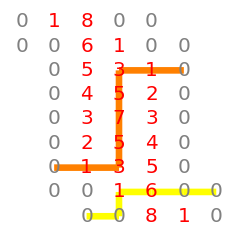
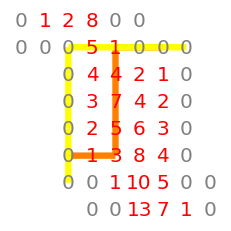
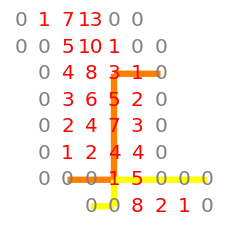
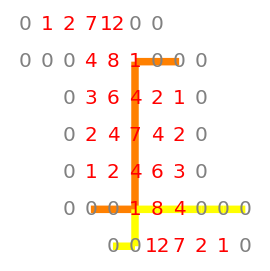

Precomputed Q-systems

```mathematica
DQ4[dA11][1]=DQ4[dAu1][1]={{1,u^5,((1+4 u^2)^4 (u+4 u^3))/1024,u/3+u^5,1},{1/u^4,-1/4+u^2,(13 u^5)/35+u^9,19/240-u^2/2+u^4,1},{256/((1+4 u^2)^4),-1/(2 u^3)+1/u,(75 u)/448+(61 u^3)/112-u^5/4+u^7,-u/2+u^3,1},{1/((u+u^3)^4),(16 (19-120 u^2+240 u^4))/(15 (1+4 u^2)^4),(13 u)/35+u^5,-1/4+u^2,1},{65536/((9+40 u^2+16 u^4)^4),(1+3 u^4)/(3 u^3 (1+u^2)^4),u/4+u^3,u,1}};

DQ4[dA1u][1]=DQ4[dAuu][1]={{1,u^6,((1+4 u^2)^5 (u+4 u^3))/4096,1/3 (u^2+u^4+3 u^6+3 u^8),9/16+(5 u^2)/2+u^4},{1/u^5,-1/4+u^2,(13 u^6)/35+u^10,19/960-(11 u^2)/240-u^4/4+u^6,u+u^3},{1024/((1+4 u^2)^5),-1/(2 u^4)+1/u^2,(75 u)/448+(61 u^3)/112-u^5/4+u^7,-u^2/2+u^4,1/4+u^2},{1/((u+u^3)^5),(64 (19-120 u^2+240 u^4))/(15 (1+4 u^2)^5),13/35+u^4,-1/4+u^2,u},{1048576/((9+40 u^2+16 u^4)^5),(1+3 u^4)/(3 u^4 (1+u^2)^5),u,1,1}};
```

#### B 1

```mathematica
DQ4[dB10][1]=DQ4[dBu0][1]={{1,u^5,(u (1+4 u^2)^5)/1024,u (-1+u^2),((7 u)/12+u^3)/((-ⅈ/2+u) (ⅈ/2+u) (-(3 ⅈ)/2+u) ((3 ⅈ)/2+u))},{1/u^4,-47/108+u^2,u^5 (11/27-(10 u^2)/27+u^4),-5/12+u^2,(1/9+u^2)/(u (-ⅈ+u) (ⅈ+u))},{256/((1+4 u^2)^4),-19/(18 u^3)+1/u,1/576 u (29-116 u^2-784 u^4+576 u^6),u,u/((-ⅈ/2+u) (ⅈ/2+u))},{1/((u+u^3)^4),(16 (4673-4872 u^2+3024 u^4))/(189 (1+4 u^2)^4),u (37/63-(20 u^2)/9+u^4),1,1/u},{(65536 u)/((9+40 u^2+16 u^4)^4),(-494+487 u^2-147 u^4+126 u^6)/(126 (u+u^3)^4),27/112-(11 u^2)/6+u^4,1,1}};

DQ4[dB01][1]={{1,u^4,((1+4 u^2)^4 (81-616 u^2+336 u^4))/86016,-247/63+(487 u^2)/126-(7 u^4)/6+u^6,u},{1/u^5,1,u^5 (37/63-(20 u^2)/9+u^4),4673/3024-(29 u^2)/18+u^4,1},{u/((-ⅈ/2+u)^5 (ⅈ/2+u)^5),1/u^3,1/576 u (29-116 u^2-784 u^4+576 u^6),-(19 u)/18+u^3,1},{(1/9+u^2)/(u^5 (-ⅈ+u)^5 (ⅈ+u)^5),(64 (-5+12 u^2))/(3 (1+4 u^2)^4),(11 u)/27-(10 u^3)/27+u^5,-47/108+u^2,1},{((7 u)/12+u^3)/((-ⅈ/2+u)^5 (ⅈ/2+u)^5 (-(3 ⅈ)/2+u)^5 ((3 ⅈ)/2+u)^5),(-1+u^2)/(u^3 (1+u^2)^4),u/4+u^3,u,1}};

DQ4[dB0u][1]={{1,u^5,((1+4 u^2)^5 (81-616 u^2+336 u^4))/344064,1/126 u (-494-7 u^2+340 u^4-21 u^6+126 u^8),(9 u)/16+(5 u^3)/2+u^5},{1/u^6,1,u^6 (37/63-(20 u^2)/9+u^4),4673/12096+(3455 u^2)/3024-(49 u^4)/36+u^6,u+u^3},{u/((-ⅈ/2+u)^6 (ⅈ/2+u)^6),1/u^4,1/576 u (29-116 u^2-784 u^4+576 u^6),-(19 u^2)/18+u^4,1/4+u^2},{(1/9+u^2)/(u^6 (-ⅈ+u)^6 (ⅈ+u)^6),(256 (-5+12 u^2))/(3 (1+4 u^2)^5),11/27-(10 u^2)/27+u^4,-47/108+u^2,u},{((7 u)/12+u^3)/((-ⅈ/2+u)^6 (ⅈ/2+u)^6 (-(3 ⅈ)/2+u)^6 ((3 ⅈ)/2+u)^6),(-1+u^2)/(u^4 (1+u^2)^5),u,1,1}};
```

#### C 1

Δ=7.5
2-fold degeneracy

[0,0|3,2,2,2|2,1]	L=6
[0,0|4,3,3,3|1,0]	L=7

and the conjugate pair

[1,2|4,4,4,3|0,0]	L=6
[0,1|4,4,4,3|0,0]	L=7

ℚ’s

```mathematica
DQ4[long3][1]//Reverse//Grid
```

(262144 u (215+728 u^2+240 u^4))/(15 (1+4 u^2)^5 (9+4 u^2)^6) | (-377+496 u^2-1063 u^4+1225 u^6+980 u^8+315 u^10)/(315 u^5 (1+u^2)^6) | u/4+u^3 | u | 1
(1+265 u^2+225 u^4)/(225 u^5 (1+u^2)^6) | (16 (74529-439760 u^2+471520 u^4+403200 u^6+518400 u^8))/(2025 (1+4 u^2)^6) | (13 u)/45-u^3/9+u^5 | -11/36+u^2 | 1
(1024 u)/((1+4 u^2)^5) | (13-5 u^2+45 u^4)/(45 u^5) | u/64-(7 u^3)/48-(7 u^5)/12+u^7 | -(2 u)/3+u^3 | 1
1/u^5 | -11/36+u^2 | -(2 u^7)/3+u^9 | 121/144-(5 u^2)/6+u^4 | 1
1 | u^6 | ((1+4 u^2)^6)/4096 | -2+(7 u^2)/3+u^6 | u

Young diagrams

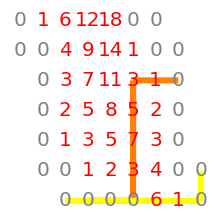
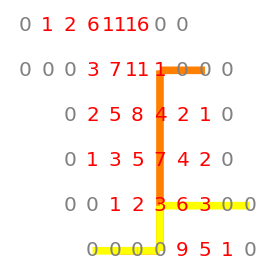

```mathematica
DQ4[dC10][1]=DQ4[dCu0][1]={{1,u^7,((1+4 u^2)^6 (u+4 u^3))/16384,1/315 u (-377+496 u^2-1063 u^4+1225 u^6+980 u^8+315 u^10),(43 u)/192+(397 u^3)/240+(197 u^5)/60+u^7},{1/u^6,-11/36+u^2,(13 u^7)/45-u^9/9+u^11,8281/57600-(5497 u^2)/6480+(2947 u^4)/3240+(7 u^6)/9+u^8,u/225+(53 u^3)/45+u^5},{4096/((1+4 u^2)^6),-2/(3 u^5)+1/u^3,u/64-(7 u^3)/48-(7 u^5)/12+u^7,(13 u)/45-u^3/9+u^5,u/4+u^3},{1/((u+u^3)^6),(256 (121-120 u^2+144 u^4))/(9 (1+4 u^2)^6),-(2 u)/3+u^3,-11/36+u^2,u},{(16777216 u)/((9+40 u^2+16 u^4)^6),(-6+7 u^2+3 u^6)/(3 (u+u^3)^6),1,1,1}};

DQ4[dC01][1]={{1,u^6,((1+4 u^2)^6)/4096,-2+(7 u^2)/3+u^6,u},{1/u^5,-11/36+u^2,-(2 u^7)/3+u^9,121/144-(5 u^2)/6+u^4,1},{(1024 u)/((1+4 u^2)^5),(13-5 u^2+45 u^4)/(45 u^5),u/64-(7 u^3)/48-(7 u^5)/12+u^7,-(2 u)/3+u^3,1},{(1+265 u^2+225 u^4)/(225 u^5 (1+u^2)^6),(16 (74529-439760 u^2+471520 u^4+403200 u^6+518400 u^8))/(2025 (1+4 u^2)^6),(13 u)/45-u^3/9+u^5,-11/36+u^2,1},{(262144 u (215+728 u^2+240 u^4))/(15 (1+4 u^2)^5 (9+4 u^2)^6),(-377+496 u^2-1063 u^4+1225 u^6+980 u^8+315 u^10)/(315 u^5 (1+u^2)^6),u/4+u^3,u,1}};

DQ4[dC0u][1]=DQ4[dC01][1]xresc[-1];
```

#### D 2

```mathematica
DQ4[dD10][1]=DQ4[dDu0][1]={{1,u^6,((1+4 u^2)^5 (u+4 u^3))/4096,1/9 u^2 (-13-2 √61+3 u^2+(25+2 √61) u^4+9 u^6),1/60 u (41-2 √61+60 u^2)},{1/u^5,1/252 (-80-√61)+u^2,1/126 u^6 (49-√61-(17+√61) u^2+126 u^4),((1+4 u^2) (-469-74 √61+72 (14+3 √61) u^2+1296 u^4))/5184,1/90 (13-√61)+u^2},{1024/((1+4 u^2)^5),-(59+√61-84 u^2)/(84 u^4),(u (1+4 u^2) (175-18 √61-8 (38+√61) u^2+336 u^4))/1344,1/9 u^2 (2+√61+9 u^2),u},{1/((u+u^3)^5),(64 (605+58 √61-24 (38+√61) u^2+1008 u^4))/(63 (1+4 u^2)^5),1/21 (10-√61-(17+√61) u^2+21 u^4),1/36 (-5+2 √61)+u^2,1},{(1048576 u)/((9+40 u^2+16 u^4)^5),(-2 (53+7 √61)+(131+13 √61) u^2-3 (3+√61) u^4+84 u^6)/(84 (u+u^3)^5),1/28 (1-2 √61)+u^2,u,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dD01][1]=hodge[DQ4[dD10][1]][length[dD10]];
DQ4[dD0u][1]=hodge[DQ4[dDu0][1]][length[dDu0]];
```

```mathematica
DQ4[dD10][2]=DQ4[dDu0][2]={{1,u^6,(u (1+4 u^2)^6)/4096,1/9 u^2 (-13+2 √61+3 u^2+(25-2 √61) u^4+9 u^6),1/60 (41+2 √61) u+u^3},{1/u^5,1/252 (-80+√61)+u^2,1/126 u^6 (49+√61+(-17+√61) u^2+126 u^4),((1+4 u^2) (-469+74 √61+72 u^2 (14-3 √61+18 u^2)))/5184,1/90 (13+√61)+u^2},{1024/((1+4 u^2)^5),(-59+√61)/(84 u^4)+1/u^2,(u (1+4 u^2) (175+18 √61+8 u^2 (-38+√61+42 u^2)))/1344,-1/9 (-2+√61) u^2+u^4,u},{1/((u+u^3)^5),(64 (605-58 √61+24 u^2 (-38+√61+42 u^2)))/(63 (1+4 u^2)^5),1/21 (10+√61+(-17+√61) u^2+21 u^4),1/36 (-5-2 √61)+u^2,1},{(1048576 u)/((9+40 u^2+16 u^4)^5),(2 (-53+7 √61)+(131-13 √61) u^2+3 (-3+√61) u^4+84 u^6)/(84 (u+u^3)^5),1/28 (1+2 √61)+u^2,u,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dD01][2]=hodge[DQ4[dD10][2]][length[dD10]];
DQ4[dD0u][2]=hodge[DQ4[dDu0][2]][length[dDu0]];
```

#### E 1

```mathematica
DQ4[dE10][1]=DQ4[dEu0][1]={{1,u^6,(-ⅈ/2+u)^5 (ⅈ/2+u)^5 (u/4+u^3),-(13 u)/28-(3 u^3)/2+(47 u^5)/28+u^7,(13 u)/28+u^3},{1/u^5,-3/8+u^2,u^5 ((7 u)/20-u^3/4+u^5),-(201 u)/560+(9 u^3)/14+u^5,1/14+u^2},{1/((-ⅈ/2+u)^5 (ⅈ/2+u)^5),(-(7 u)/8+u^3)/u^5,u/32-(3 u^3)/16-u^5+u^7,u/4+u^3,u},{1/(u^5 (-ⅈ+u)^5 (ⅈ+u)^5),(85/72-(5 u^2)/4+u^4)/((-ⅈ/2+u)^5 (ⅈ/2+u)^5),1/6-(3 u^2)/2+u^4,u,1},{u/((-ⅈ/2+u)^5 (ⅈ/2+u)^5 (-(3 ⅈ)/2+u)^5 ((3 ⅈ)/2+u)^5),(-35/12+(73 u^2)/24-(5 u^4)/8+u^6)/(u^5 (-ⅈ+u)^5 (ⅈ+u)^5),-1+u^2,1,1}};

DQ4[dE01][1]=hodge[DQ4[dE10][1]][length[dE10]];
DQ4[dE0u][1]=hodge[DQ4[dEu0][1]][length[dEu0]];
```

#### F 4

```mathematica
DQ4[dFu1][j_/;j≤4]:=DQ4[dF11][j]
DQ4[dFuu][j_/;j≤4]:=hodge[DQ4[dFu1][j]][length[dFu1]]
DQ4[dF1u][j_/;j≤4]:=hodge[DQ4[dFu1][j]][length[dFu1]]

DQ4[dF11][j_/;j≤4]:=DQ4[dF11][j]={{{1,u^7,((1+4 u^2)^7)/16384,1/224 (-√91+7 u (10+u (√91+u (24+u (-√91+u (42+7 √91 u+60 u^2+32 u^4)))))),5/32+1/56 u (√91+7 u+56 u^3)},{1/u^6,-1/4+u^2,1/14 u^7 (-√91-7 u+14 u^3),1/448 (-31+4 u (-3 √91+u (21+4 u (3 √91+7 u+28 u^3)))),-1/6+u^2},{4096/((1+4 u^2)^6),((3 √(13/7))/8-u/2+u^3)/u^6,1/448 (-3+4 u (-2 √91+u (133+4 u (-2 √91-49 u+28 u^3)))),(3 √(13/7))/8-u/2+u^3,1},{(-1+6 u^2)/(6 (u+u^3)^6),(64 (-31+4 u (-3 √91+u (21+4 u (3 √91+7 u+28 u^3)))))/(7 (1+4 u^2)^6),-1/14 u (√91+7 u-14 u^3),-1/4+u^2,1},{(524288 (35+4 u (√91+7 u+56 u^3)))/(7 (9+40 u^2+16 u^4)^6),-1/(224 (u+u^3)^6)(√91-7 u (10+u (√91+u (24+u (-√91+u (42+7 √91 u+60 u^2+32 u^4)))))),1/4+u^2,u,1}},{{1,u^7,((1+4 u^2)^7)/16384,1/224 (√91+7 u (10+u (-√91+u (24+u (√91+u (42-7 √91 u+60 u^2+32 u^4)))))),5/32-1/8 √(13/7) u+u^2/8+u^4},{1/u^6,-1/4+u^2,1/14 u^7 (√91-7 u+14 u^3),1/448 (-31+4 u (3 √91+u (21+4 u (-3 √91+7 u+28 u^3)))),-1/6+u^2},{4096/((1+4 u^2)^6),(-(3 √(13/7))/8-u/2+u^3)/u^6,1/448 (-3+4 u (2 √91+u (133+4 u (2 √91-49 u+28 u^3)))),-(3 √(13/7))/8-u/2+u^3,1},{(-1+6 u^2)/(6 (u+u^3)^6),(64 (-31+4 u (3 √91+u (21+4 u (-3 √91+7 u+28 u^3)))))/(7 (1+4 u^2)^6),1/14 u (√91-7 u+14 u^3),-1/4+u^2,1},{(524288 (35+4 u (-√91+7 u+56 u^3)))/(7 (9+40 u^2+16 u^4)^6),1/(224 (u+u^3)^6)(√91+7 u (10+u (-√91+u (24+u (√91+u (42-7 √91 u+60 u^2+32 u^4)))))),1/4+u^2,u,1}},{{1,u^7,((1+4 u^2)^7)/16384,1/168 (-√266+7 u (-36+u (3 √266+u (-20+u (-5 √266+u (28+u (√266+36 u+24 u^3))))))),25/48-1/3 √(19/14) u-u^2/3+u^4},{1/u^6,-7/36+u^2,1/42 u^7 (√266-14 u+42 u^3),(951+4 u (-52 √266+u (301+12 u (4 √266+7 u+84 u^3))))/4032,-4/9+u^2},{4096/((1+4 u^2)^6),-(√266+14 u-42 u^3)/(42 u^6),-1/448+(3 u^2)/16-(5 u^4)/4+u^6,(√(19/14))/3-u/3+u^3,1},{(-4+9 u^2)/(9 (u+u^3)^6),1/(63 (1+4 u^2)^6)64 (951+4 u (52 √266+u (301+12 u (-4 √266+7 u+84 u^3)))),-1/42 u (√266+14 u-42 u^3),-7/36+u^2,1},{(1048576 (175+8 u (√266-14 u+42 u^3)))/(21 (9+40 u^2+16 u^4)^6),1/(168 (u+u^3)^6)(√266+7 u (-36+u (-3 √266+u (-20+u (5 √266+u (28-√266 u+36 u^2+24 u^4)))))),1/4+u^2,u,1}},{{1,u^7,((1+4 u^2)^7)/16384,1/168 (√266+7 u (-36+u (-3 √266+u (-20+u (5 √266+u (28-√266 u+36 u^2+24 u^4)))))),25/48+1/3 √(19/14) u-u^2/3+u^4},{1/u^6,-7/36+u^2,-1/42 u^7 (√266+14 u-42 u^3),(951+4 u (52 √266+u (301+12 u (-4 √266+7 u+84 u^3))))/4032,-4/9+u^2},{4096/((1+4 u^2)^6),(√266-14 u+42 u^3)/(42 u^6),-1/448+(3 u^2)/16-(5 u^4)/4+u^6,-(√(19/14))/3-u/3+u^3,1},{(-4+9 u^2)/(9 (u+u^3)^6),1/(63 (1+4 u^2)^6)64 (951+4 u (-52 √266+u (301+12 u (4 √266+7 u+84 u^3)))),1/42 u (√266-14 u+42 u^3),-7/36+u^2,1},{(1048576 (175-8 u (√266+14 u-42 u^3)))/(21 (9+40 u^2+16 u^4)^6),-1/(168 (u+u^3)^6)(√266-7 u (-36+u (3 √266+u (-20+u (-5 √266+u (28+u (√266+36 u+24 u^3))))))),1/4+u^2,u,1}}}⟦j⟧//N[#,digits]&//CHOP//Rationalize;
```

#### G 1

```mathematica
DQ4[dG10][1]=DQ4[dGu0][2]={{1,u^5,(u (1+4 u^2)^5)/1024,u,u/((-ⅈ/2+u) (ⅈ/2+u) (-(3 ⅈ)/2+u) ((3 ⅈ)/2+u))},{1/u^4,-71/44+u^2,u^5 (7/11-(30 u^2)/11+u^4),1,1/(u (-ⅈ+u) (ⅈ+u))},{(256 u)/((1+4 u^2)^4),1+932/(297 u^4)-30/(11 u^2),27/2816-(1009 u^2)/1584+(3073 u^4)/792-(49 u^6)/11+u^8,1,1/((-ⅈ/2+u) (ⅈ/2+u))},{(5+7 u^2)/(7 (u+u^3)^4),(4 (-1199185+1062004 u^2-390960 u^4+133056 u^6))/(2079 (1+4 u^2)^4),1/99 u (-86+511 u^2-504 u^4+99 u^6),1,1/u},{(16384 u (67+28 u^2))/(7 (9+40 u^2+16 u^4)^4),(384450-284263 u^2+129458 u^4-16947 u^6+9702 u^8)/(9702 (u+u^3)^4),-1755/4928+(2227 u^2)/528-(215 u^4)/44+u^6,1,1}};

DQ4[dG01][1]={{1,u^4,((1+4 u^2)^4 (-5265+62356 u^2-72240 u^4+14784 u^6))/3784704,5825/147-(40609 u^2)/1386+(1321 u^4)/99-(269 u^6)/154+u^8,(67 u)/28+u^3},{1/u^5,1,1/99 u^5 (-86+511 u^2-504 u^4+99 u^6),-1199185/133056+(265501 u^2)/33264-(905 u^4)/308+u^6,5/7+u^2},{1/((-ⅈ/2+u)^5 (ⅈ/2+u)^5),1/u^4,27/2816-(1009 u^2)/1584+(3073 u^4)/792-(49 u^6)/11+u^8,932/297-(30 u^2)/11+u^4,u},{1/(u^5 (-ⅈ+u)^5 (ⅈ+u)^5),256/((1+4 u^2)^4),(7 u)/11-(30 u^3)/11+u^5,-71/44+u^2,1},{u/((-ⅈ/2+u)^5 (ⅈ/2+u)^5 (-(3 ⅈ)/2+u)^5 ((3 ⅈ)/2+u)^5),1/(u^3 (1+u^2)^4),u/4+u^3,u,1}};

DQ4[dG0u][2]={{1,u^5,((1+4 u^2)^5 (-5265+62356 u^2-72240 u^4+14784 u^6))/15138816,1/9702 u (384450+100187 u^2-154805 u^4+112511 u^6-7245 u^8+9702 u^10),1/448 u (603+2932 u^2+2192 u^4+448 u^6)},{1/u^6,1,1/99 u^6 (-86+511 u^2-504 u^4+99 u^6),-1199185/532224-(77807 u^2)/11088+(17219 u^4)/2376-(207 u^6)/77+u^8,(5 u)/7+(12 u^3)/7+u^5},{1/((-ⅈ/2+u)^6 (ⅈ/2+u)^6),1/u^5,27/2816-(1009 u^2)/1584+(3073 u^4)/792-(49 u^6)/11+u^8,(932 u)/297-(30 u^3)/11+u^5,u/4+u^3},{1/(u^6 (-ⅈ+u)^6 (ⅈ+u)^6),1024/((1+4 u^2)^5),7/11-(30 u^2)/11+u^4,-71/44+u^2,u},{u/((-ⅈ/2+u)^6 (ⅈ/2+u)^6 (-(3 ⅈ)/2+u)^6 ((3 ⅈ)/2+u)^6),1/(u^4 (1+u^2)^5),u,1,1}};
```

#### H 3

```mathematica
DQ4[dH10][1]=DQ4[dHu0][1]={{1,u^7,(u (1+4 u^2)^7)/16384,u (u^8+u^6 Root[-11637+17976 #1+59584 #1^2+21952 #1^3&,3]+u^4 Root[-141303+768544 #1-591136 #1^2+65856 #1^3&,1]+Root[-20609+173712 #1-337120 #1^2+65856 #1^3&,2]+u^2 Root[-1549643+2545928 #1+2684416 #1^2+197568 #1^3&,2]),1/(9/16+(5 u^2)/2+u^4)u (u^8+u^6 Root[-3120849+9639000 #1-9172800 #1^2+2744000 #1^3&,3]+u^4 Root[-66229497+85534400 #1-35187200 #1^2+4608000 #1^3&,1]+u^2 Root[-48281895947-119640716160 #1+208912793600 #1^2+101154816000 #1^3&,2]+Root[17680353788641+42767066758080 #1+28132699750400 #1^2+4855431168000 #1^3&,3])},{1/u^6,u^2+Root[853+7818 #1+23544 #1^2+23328 #1^3&,1],1/720 u^7 (720 u^4+Root[-52919808+633344 #1-2432 #1^2+3 #1^3&,2]+u^2 Root[2112000+112000 #1+1120 #1^2+3 #1^3&,1]),1/20160(20160 u^6+u^2 Root[-3326398726464+1000265328 #1-80076 #1^2+#1^3&,1]+Root[16372459368+38484639 #1+16863 #1^2+#1^3&,2]+u^4 Root[9773125632000+1745798400 #1+79440 #1^2+#1^3&,3]),1/(907200 (u+u^3))(907200 u^6+u^2 Root[-221602692877436736+1264282445088 #1-2137104 #1^2+#1^3&,1]+Root[-2099103212107584+59341988016 #1-448956 #1^2+#1^3&,1]+u^4 Root[40142043058176000+503044992000 #1+1386720 #1^2+#1^3&,3])},{4096/((1+4 u^2)^6),(u^2+Root[703+2920 #1+3936 #1^2+1728 #1^3&,1])/u^5,1/96 u (96 u^6+u^4 Root[864768+44608 #1+664 #1^2+3 #1^3&,1]+u^2 Root[-154824-18964 #1-342 #1^2+9 #1^3&,1]+Root[-1437+2210 #1-668 #1^2+24 #1^3&,2]),u^3+1/42 u Root[18981+2610 #1+96 #1^2+#1^3&,3],(2 u (42 u^2+Root[62694+7965 #1+318 #1^2+4 #1^3&,3]))/(21+84 u^2)},{1/((u+u^3)^6),1/((1+4 u^2)^6)4096 (u^4+u^2 Root[96+319 #1+330 #1^2+108 #1^3&,1]+Root[-24013+334640 #1-667392 #1^2+331776 #1^3&,3]),u (u^2+Root[11+70 #1+84 #1^2+27 #1^3&,1]),1,1/u},{(4194304 u (20 u^2+Root[114589+10473 #1+311 #1^2+3 #1^3&,3]))/(5 (9+40 u^2+16 u^4)^6),1/(240 (u+u^3)^6)(240 u^8+u^4 Root[-2227662848+17090816 #1-40272 #1^2+27 #1^3&,3]+Root[-184287232+5092352 #1-24288 #1^2+27 #1^3&,2]+u^6 Root[869400576+8215552 #1+25824 #1^2+27 #1^3&,3]+u^2 Root[-8027209728+84981760 #1+173568 #1^2+81 #1^3&,2]),u^2+Root[729+7492 #1+20016 #1^2+15552 #1^3&,1],1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dH01][1]=hodge[DQ4[dH10][1]][length[dH10]];
DQ4[dH0u][1]=hodge[DQ4[dHu0][1]][length[dHu0]];
```

```mathematica
DQ4[dH10][2]=DQ4[dHu0][2]={{1,u^7,(u (1+4 u^2)^7)/16384,u (u^8+u^6 Root[-11637+17976 #1+59584 #1^2+21952 #1^3&,2]+u^4 Root[-141303+768544 #1-591136 #1^2+65856 #1^3&,2]+Root[-20609+173712 #1-337120 #1^2+65856 #1^3&,1]+u^2 Root[-1549643+2545928 #1+2684416 #1^2+197568 #1^3&,3]),1/(9+40 u^2+16 u^4)16 u (u^8+u^6 Root[-3120849+9639000 #1-9172800 #1^2+2744000 #1^3&,2]+u^4 Root[-66229497+85534400 #1-35187200 #1^2+4608000 #1^3&,2]+u^2 Root[-48281895947-119640716160 #1+208912793600 #1^2+101154816000 #1^3&,3]+Root[17680353788641+42767066758080 #1+28132699750400 #1^2+4855431168000 #1^3&,2])},{1/u^6,u^2+Root[853+7818 #1+23544 #1^2+23328 #1^3&,2],u^7 (u^4+u^2 Root[11+420 #1+3024 #1^2+5832 #1^3&,2]+Root[-34453+296880 #1-820800 #1^2+729000 #1^3&,3]),u^6+u^4 Root[19638+70721 #1+64876 #1^2+16464 #1^3&,2]+u^2 Root[-213888807+1296640240 #1-2092652800 #1^2+526848000 #1^3&,2]+Root[8422047+399099960 #1+3525491200 #1^2+4214784000 #1^3&,3],1/(u+u^3)(u^6+u^4 Root[18441+209650 #1+524300 #1^2+343000 #1^3&,2]+u^2 Root[-6515383789+33721906400 #1-51712640000 #1^2+21952000000 #1^3&,2]+Root[-185148423+4748444400 #1-32590880000 #1^2+65856000000 #1^3&,2])},{4096/((1+4 u^2)^6),(u^2+Root[703+2920 #1+3936 #1^2+1728 #1^3&,2])/u^5,u (u^6+u^4 Root[563+2788 #1+3984 #1^2+1728 #1^3&,2]+u^2 Root[-6451-75856 #1-131328 #1^2+331776 #1^3&,3]+Root[-479+70720 #1-2052096 #1^2+7077888 #1^3&,3]),u (u^2+Root[703+4060 #1+6272 #1^2+2744 #1^3&,2]),(4 u (u^2+Root[1161+6195 #1+10388 #1^2+5488 #1^3&,2]))/(1+4 u^2)},{1/((u+u^3)^6),1/((1+4 u^2)^6)4096 (u^4+u^2 Root[96+319 #1+330 #1^2+108 #1^3&,2]+Root[-24013+334640 #1-667392 #1^2+331776 #1^3&,1]),u (u^2+Root[11+70 #1+84 #1^2+27 #1^3&,2]),1,1/u},{(16777216 u (u^2+Root[114589+209460 #1+124400 #1^2+24000 #1^3&,2]))/(9+40 u^2+16 u^4)^6,1/((u+u^3)^6)(u^8+u^6 Root[70752+160460 #1+121050 #1^2+30375 #1^3&,2]+u^4 Root[-543863+1001415 #1-566325 #1^2+91125 #1^3&,1]+Root[-44992+298380 #1-341550 #1^2+91125 #1^3&,1]+u^2 Root[-653256+1659800 #1+813600 #1^2+91125 #1^3&,3]),u^2+Root[729+7492 #1+20016 #1^2+15552 #1^3&,2],1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dH01][2]=hodge[DQ4[dH10][2]][length[dH10]];
DQ4[dH0u][2]=hodge[DQ4[dHu0][2]][length[dHu0]];
```

```mathematica
DQ4[dH10][3]=DQ4[dHu0][3]={{1,u^7,(u (1+4 u^2)^7)/16384,u (u^8+u^6 Root[-11637+17976 #1+59584 #1^2+21952 #1^3&,1]+u^4 Root[-141303+768544 #1-591136 #1^2+65856 #1^3&,3]+Root[-20609+173712 #1-337120 #1^2+65856 #1^3&,3]+u^2 Root[-1549643+2545928 #1+2684416 #1^2+197568 #1^3&,1]),1/(9+40 u^2+16 u^4)16 u (u^8+u^6 Root[-3120849+9639000 #1-9172800 #1^2+2744000 #1^3&,1]+u^4 Root[-66229497+85534400 #1-35187200 #1^2+4608000 #1^3&,3]+u^2 Root[-48281895947-119640716160 #1+208912793600 #1^2+101154816000 #1^3&,1]+Root[17680353788641+42767066758080 #1+28132699750400 #1^2+4855431168000 #1^3&,1])},{1/u^6,u^2+Root[853+7818 #1+23544 #1^2+23328 #1^3&,3],u^7 (u^4+u^2 Root[11+420 #1+3024 #1^2+5832 #1^3&,3]+Root[-34453+296880 #1-820800 #1^2+729000 #1^3&,1]),u^6+u^4 Root[19638+70721 #1+64876 #1^2+16464 #1^3&,1]+u^2 Root[-213888807+1296640240 #1-2092652800 #1^2+526848000 #1^3&,3]+Root[8422047+399099960 #1+3525491200 #1^2+4214784000 #1^3&,1],1/(u+u^3)(u^6+u^4 Root[18441+209650 #1+524300 #1^2+343000 #1^3&,1]+u^2 Root[-6515383789+33721906400 #1-51712640000 #1^2+21952000000 #1^3&,3]+Root[-185148423+4748444400 #1-32590880000 #1^2+65856000000 #1^3&,3])},{4096/((1+4 u^2)^6),(u^2+Root[703+2920 #1+3936 #1^2+1728 #1^3&,3])/u^5,u (u^6+u^4 Root[563+2788 #1+3984 #1^2+1728 #1^3&,3]+u^2 Root[-6451-75856 #1-131328 #1^2+331776 #1^3&,2]+Root[-479+70720 #1-2052096 #1^2+7077888 #1^3&,1]),u (u^2+Root[703+4060 #1+6272 #1^2+2744 #1^3&,1]),(4 u (u^2+Root[1161+6195 #1+10388 #1^2+5488 #1^3&,1]))/(1+4 u^2)},{1/((u+u^3)^6),1/((1+4 u^2)^6)4096 (u^4+u^2 Root[96+319 #1+330 #1^2+108 #1^3&,3]+Root[-24013+334640 #1-667392 #1^2+331776 #1^3&,2]),u (u^2+Root[11+70 #1+84 #1^2+27 #1^3&,3]),1,1/u},{(16777216 u (u^2+Root[114589+209460 #1+124400 #1^2+24000 #1^3&,1]))/(9+40 u^2+16 u^4)^6,1/((u+u^3)^6)(u^8+u^6 Root[70752+160460 #1+121050 #1^2+30375 #1^3&,1]+u^4 Root[-543863+1001415 #1-566325 #1^2+91125 #1^3&,2]+Root[-44992+298380 #1-341550 #1^2+91125 #1^3&,3]+u^2 Root[-653256+1659800 #1+813600 #1^2+91125 #1^3&,1]),u^2+Root[729+7492 #1+20016 #1^2+15552 #1^3&,3],1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dH01][3]=hodge[DQ4[dH10][3]][length[dH10]];
DQ4[dH0u][3]=hodge[DQ4[dHu0][3]][length[dHu0]];
```

#### I 3

```mathematica
DQ4[dI10][1]=DQ4[dIu0][1]={{1,u^8,(u (1+4 u^2)^8)/65536,1/261273600000 u (u^6 Root[156585351834236878848000000000000000+129581433815040000000000 #1-1251936000000 #1^2+#1^3&,1]+u^2 Root[3593853287386841088000000000000000+13950756126720000000000 #1-499219200000 #1^2+#1^3&,1]+Root[-81533837805355008000000000000000+10438880624640000000000 #1-349920000000 #1^2+#1^3&,1]+1036800000 u^8 (252 u^4+Root[-34207056+412227 #1-1200 #1^2+#1^3&,3]+9 u^2 Root[-195919+10995 #1-189 #1^2+#1^3&,3])+u^4 Root[-690324180038049595392000000000000000+596457709240320000000000 #1+3342124800000 #1^2+#1^3&,2]),u (u^8+u^6 Root[-697316+2819250 #1-3318525 #1^2+1157625 #1^3&,3]+u^4 Root[-9443278703+11750839800 #1-4668955200 #1^2+592704000 #1^3&,1]+u^2 Root[-166606068253-52251249960 #1+1035192110400 #1^2+406594944000 #1^3&,2]+Root[5559629513794343+11008986280078080 #1+5980449742848000 #1^2+951664508928000 #1^3&,3])},{1/u^7,u^2+Root[383+3834 #1+12672 #1^2+13824 #1^3&,1],1/720 u^8 (720 u^4+Root[-13440384+174096 #1-732 #1^2+#1^3&,2]+u^2 Root[108000+13500 #1+240 #1^2+#1^3&,1]),1/60480 u (60480 u^8+u^2 Root[699769608624+1488416076 #1-109644 #1^2+#1^3&,1]+u^6 Root[1976721408000-2083968000 #1-20160 #1^2+#1^3&,3]+u^4 Root[-1549106878464-809518464 #1+23928 #1^2+#1^3&,2]+Root[4071877696323+5887933308 #1+1787856 #1^2+64 #1^3&,2]),u^6+u^2 Root[-55844627+247669065 #1-325854900 #1^2+125023500 #1^3&,1]+u^4 Root[13235479+118073025 #1+230598900 #1^2+125023500 #1^3&,3]+Root[-14895992+335630925 #1-2076283125 #1^2+3906984375 #1^3&,1]},{16384/((1+4 u^2)^7),1/u^4+Root[1148+335 #1+32 #1^2+#1^3&,1]/(16 u^6),1/768 u (768 u^6+u^2 Root[-5750784-96768 #1-240 #1^2+#1^3&,1]+Root[-15984+3852 #1-180 #1^2+#1^3&,2]+u^4 Root[65470464+543744 #1+1344 #1^2+#1^3&,1]),u (u^4+u^2 Root[-59+180 #1+1584 #1^2+1728 #1^3&,3]+Root[7+324 #1+2880 #1^2+6912 #1^3&,3]),u^3+1/60 u Root[59157+4815 #1+123 #1^2+#1^3&,3]},{1/((u+u^3)^7),1/((1+4 u^2)^7)16384 (u^4+u^2 Root[32+127 #1+160 #1^2+64 #1^3&,1]+Root[-17591+345744 #1-783360 #1^2+442368 #1^3&,3]),u^2+Root[1+15 #1+32 #1^2+16 #1^3&,1],u,1},{(16777216 u (80 u^2+Root[1945792+48560 #1+388 #1^2+#1^3&,3]))/(5 (9+40 u^2+16 u^4)^7),1/(160 (u+u^3)^7)(160 u^8+u^6 Root[3080192+65280 #1+448 #1^2+#1^3&,3]+u^4 Root[-273522688+4453632 #1-21024 #1^2+27 #1^3&,3]+Root[-5373952+481536 #1-10368 #1^2+27 #1^3&,2]+u^2 Root[-298369024+8109312 #1+31104 #1^2+27 #1^3&,2]),1,1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dI01][1]=hodge[DQ4[dI10][1]][length[dI10]];
DQ4[dI0u][1]=hodge[DQ4[dIu0][1]][length[dIu0]];
```

```mathematica
DQ4[dI10][2]=DQ4[dIu0][2]={{1,u^8,(u (1+4 u^2)^8)/65536,1/261273600000 u (Root[-81533837805355008000000000000000+10438880624640000000000 #1-349920000000 #1^2+#1^3&,2]+u^2 (u^4 Root[156585351834236878848000000000000000+129581433815040000000000 #1-1251936000000 #1^2+#1^3&,2]+u^6 Root[-38124193416889761792000000000000000+443125161492480000000000 #1-1244160000000 #1^2+#1^3&,1]+Root[3593853287386841088000000000000000+13950756126720000000000 #1-499219200000 #1^2+#1^3&,2]+9331200000 u^8 (28 u^2+Root[-195919+10995 #1-189 #1^2+#1^3&,2])+518400000 u^2 Root[-4955164848+2219472 #1+6447 #1^2+#1^3&,3])),u (u^8+u^6 Root[-697316+2819250 #1-3318525 #1^2+1157625 #1^3&,2]+u^4 Root[-9443278703+11750839800 #1-4668955200 #1^2+592704000 #1^3&,2]+u^2 Root[-166606068253-52251249960 #1+1035192110400 #1^2+406594944000 #1^3&,3]+Root[5559629513794343+11008986280078080 #1+5980449742848000 #1^2+951664508928000 #1^3&,2])},{1/u^7,u^2+Root[383+3834 #1+12672 #1^2+13824 #1^3&,2],1/720 u^8 (720 u^4+Root[-13440384+174096 #1-732 #1^2+#1^3&,3]+u^2 Root[108000+13500 #1+240 #1^2+#1^3&,2]),1/60480 u (60480 u^8+u^2 Root[699769608624+1488416076 #1-109644 #1^2+#1^3&,2]+u^6 Root[1976721408000-2083968000 #1-20160 #1^2+#1^3&,2]+u^4 Root[-1549106878464-809518464 #1+23928 #1^2+#1^3&,1]+Root[4071877696323+5887933308 #1+1787856 #1^2+64 #1^3&,3]),u^6+u^2 Root[-55844627+247669065 #1-325854900 #1^2+125023500 #1^3&,2]+u^4 Root[13235479+118073025 #1+230598900 #1^2+125023500 #1^3&,2]+Root[-14895992+335630925 #1-2076283125 #1^2+3906984375 #1^3&,2]},{16384/((1+4 u^2)^7),1/u^4+Root[1148+335 #1+32 #1^2+#1^3&,2]/(16 u^6),1/768 u (768 u^6+u^2 Root[-5750784-96768 #1-240 #1^2+#1^3&,3]+Root[-15984+3852 #1-180 #1^2+#1^3&,3]+u^4 Root[65470464+543744 #1+1344 #1^2+#1^3&,2]),u (u^4+u^2 Root[-59+180 #1+1584 #1^2+1728 #1^3&,2]+Root[7+324 #1+2880 #1^2+6912 #1^3&,2]),u^3+1/60 u Root[59157+4815 #1+123 #1^2+#1^3&,2]},{1/((u+u^3)^7),1/((1+4 u^2)^7)16384 (u^4+u^2 Root[32+127 #1+160 #1^2+64 #1^3&,2]+Root[-17591+345744 #1-783360 #1^2+442368 #1^3&,1]),u^2+Root[1+15 #1+32 #1^2+16 #1^3&,2],u,1},{(16777216 u (80 u^2+Root[1945792+48560 #1+388 #1^2+#1^3&,2]))/(5 (9+40 u^2+16 u^4)^7),1/(160 (u+u^3)^7)(160 u^8+u^6 Root[3080192+65280 #1+448 #1^2+#1^3&,2]+u^4 Root[-273522688+4453632 #1-21024 #1^2+27 #1^3&,1]+Root[-5373952+481536 #1-10368 #1^2+27 #1^3&,1]+u^2 Root[-298369024+8109312 #1+31104 #1^2+27 #1^3&,3]),1,1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dI01][2]=hodge[DQ4[dI10][2]][length[dI10]];
DQ4[dI0u][2]=hodge[DQ4[dIu0][2]][length[dIu0]];
```

```mathematica
DQ4[dI10][3]=DQ4[dIu0][3]={{1,u^8,(u (1+4 u^2)^8)/65536,1/504 u (504 u^12+u^6 Root[1123973712+482184 #1-2415 #1^2+#1^3&,3]+u^2 Root[25796772+51912 #1-963 #1^2+#1^3&,3]+Root[-585252+38844 #1-675 #1^2+#1^3&,3]+18 u^10 Root[-195919+10995 #1-189 #1^2+#1^3&,1])+u^9 Root[-316732+961863 #1-705600 #1^2+148176 #1^3&,2]+u^5 Root[-11470289+2589384 #1+3790836 #1^2+296352 #1^3&,1],u (u^8+u^6 Root[-697316+2819250 #1-3318525 #1^2+1157625 #1^3&,1]+u^4 Root[-9443278703+11750839800 #1-4668955200 #1^2+592704000 #1^3&,3]+u^2 Root[-166606068253-52251249960 #1+1035192110400 #1^2+406594944000 #1^3&,1]+Root[5559629513794343+11008986280078080 #1+5980449742848000 #1^2+951664508928000 #1^3&,1])},{1/u^7,u^2+Root[383+3834 #1+12672 #1^2+13824 #1^3&,3],1/720 u^8 (720 u^4+Root[-13440384+174096 #1-732 #1^2+#1^3&,1]+u^2 Root[108000+13500 #1+240 #1^2+#1^3&,3]),1/60480 u (60480 u^8+u^2 Root[699769608624+1488416076 #1-109644 #1^2+#1^3&,3]+u^6 Root[1976721408000-2083968000 #1-20160 #1^2+#1^3&,1]+u^4 Root[-1549106878464-809518464 #1+23928 #1^2+#1^3&,3]+Root[4071877696323+5887933308 #1+1787856 #1^2+64 #1^3&,1]),u^6+u^2 Root[-55844627+247669065 #1-325854900 #1^2+125023500 #1^3&,3]+u^4 Root[13235479+118073025 #1+230598900 #1^2+125023500 #1^3&,1]+Root[-14895992+335630925 #1-2076283125 #1^2+3906984375 #1^3&,3]},{16384/((1+4 u^2)^7),1/u^4+Root[1148+335 #1+32 #1^2+#1^3&,3]/(16 u^6),1/768 u (768 u^6+u^2 Root[-5750784-96768 #1-240 #1^2+#1^3&,2]+Root[-15984+3852 #1-180 #1^2+#1^3&,1]+u^4 Root[65470464+543744 #1+1344 #1^2+#1^3&,3]),u (u^4+u^2 Root[-59+180 #1+1584 #1^2+1728 #1^3&,1]+Root[7+324 #1+2880 #1^2+6912 #1^3&,1]),u^3+1/60 u Root[59157+4815 #1+123 #1^2+#1^3&,1]},{1/((u+u^3)^7),1/((1+4 u^2)^7)16384 (u^4+u^2 Root[32+127 #1+160 #1^2+64 #1^3&,3]+Root[-17591+345744 #1-783360 #1^2+442368 #1^3&,2]),u^2+Root[1+15 #1+32 #1^2+16 #1^3&,3],u,1},{(16777216 u (80 u^2+Root[1945792+48560 #1+388 #1^2+#1^3&,1]))/(5 (9+40 u^2+16 u^4)^7),1/(160 (u+u^3)^7)(160 u^8+u^6 Root[3080192+65280 #1+448 #1^2+#1^3&,1]+u^4 Root[-273522688+4453632 #1-21024 #1^2+27 #1^3&,2]+Root[-5373952+481536 #1-10368 #1^2+27 #1^3&,3]+u^2 Root[-298369024+8109312 #1+31104 #1^2+27 #1^3&,1]),1,1,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dI01][3]=hodge[DQ4[dI10][3]][length[dI10]];
DQ4[dI0u][3]=hodge[DQ4[dIu0][3]][length[dIu0]];
```

#### J 2

```mathematica
DQ4[dJuu][j_/;j≤2]:=hodge[DQ4[dJ11][j]][length[dJu1]]
DQ4[dJ1u][j_/;j≤2]:=hodge[DQ4[dJ11][j]][length[dJu1]]

DQ4[dJ11][1]=DQ4[dJu1][1]={{1,u^5,(u (1+4 u^2)^5 (-917+10 √901+468 u^2))/479232,1/27 u (37+√901-(28+√901) u^2+27 u^4),1},{1/u^4,1/540 (-191-2 √901)+u^2,1/10530 u^5 (-7397+91 √901+130 (46+√901) u^2+9 (-2597+31 √901) u^4+10530 u^6),(731+20 √901)/2160-1/90 (101+2 √901) u^2+u^4,1},{256/((1+4 u^2)^4),-(73+√901-90 u^2)/(90 u^3),1/449280 u (1+4 u^2) (-119915+2998 √901+4 (59461+124 √901) u^2+1584 (-199+2 √901) u^4+112320 u^6),1/90 u (-73-√901+90 u^2),1},{1/((u+u^3)^4),(16 (731+20 √901-24 (101+2 √901) u^2+2160 u^4))/(135 (1+4 u^2)^4),1/10530 u (-7397+91 √901+130 (46+√901) u^2+9 (-2597+31 √901) u^4+10530 u^6),1/540 (-191-2 √901)+u^2,1},{65536/((9+40 u^2+16 u^4)^4),(37+√901-(28+√901) u^2+27 u^4)/(27 u^3 (1+u^2)^4),(u (1+4 u^2) (-917+10 √901+468 u^2))/1872,u,1}}//N[#,digits]&//CHOP//Rationalize;

DQ4[dJ11][2]=DQ4[dJu1][2]={{1,u^5,(u (1+4 u^2)^5 (-917-10 √901+468 u^2))/479232,1/27 u (37-√901+(-28+√901) u^2+27 u^4),1},{1/u^4,1/540 (-191+2 √901)+u^2,-1/810 (569+7 √901) u^5-1/81 (-46+√901) u^7-((2597+31 √901) u^9)/1170+u^11,(731-20 √901)/2160+1/90 (-101+2 √901) u^2+u^4,1},{256/((1+4 u^2)^4),(-73+√901+90 u^2)/(90 u^3),-1/449280 u (1+4 u^2) (119915+2998 √901+4 (-59461+124 √901) u^2+1584 (199+2 √901) u^4-112320 u^6),1/90 u (-73+√901+90 u^2),1},{1/((u+u^3)^4),(16 (731-20 √901+24 (-101+2 √901) u^2+2160 u^4))/(135 (1+4 u^2)^4),-1/810 (569+7 √901) u-1/81 (-46+√901) u^3-((2597+31 √901) u^5)/1170+u^7,1/540 (-191+2 √901)+u^2,1},{65536/((9+40 u^2+16 u^4)^4),(37-√901+(-28+√901) u^2+27 u^4)/(27 u^3 (1+u^2)^4),(u (1+4 u^2) (-917-10 √901+468 u^2))/1872,u,1}}//N[#,digits]&//CHOP//Rationalize;
```

## Modified P-ansatz

Structure:

P_a=(gx)^-L(∑_(k=0)^(L-λ_a) d_(a,k)(g x)^k+∑_(k=1)^∞ (c_(a,k)(g/x))^k)

P^a=∑_(k=0)^(λ_a-1) (d^(a,k)(g x))^k+∑_(k=1)^∞ (c^(a,k)(g/x))^k

leading d equals A

d_(a,k)=(d_(a,k))^(1)+g (d_(a,k))^(1.5)+g^2(d_(a,k))^(2)+...

c_(a,k)=g^-1(c_(a,k))^(1)+(c_(a,k))^(1.5)+g^1(c_(a,k))^(2)+... 	if P~O(1)
c_(a,k)=g (c_(a,k))^(1)+g^2(c_(a,k))^(1.5)+g^3(c_(a,k))^(2)+... 	if P~O(u)  (same for d_(a,0))

#### Modify g-scaling of coefficients

```mathematica
gSCALE={c[aa_,kk_][n_]:>c[aa,kk][n]+g c[aa,kk][n+1/2],d[aa_,kk_][n_]:>d[aa,kk][n]+g d[aa,kk][n+1/2],cc[aa_,kk_][n_]:>cc[aa,kk][n]+g cc[aa,kk][n+1/2],dd[aa_,kk_][n_]:>dd[aa,kk][n]+g dd[aa,kk][n+1/2]};
```

#### P_a

```mathematica
PanzD[a_][order_][ns_][K_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=(L+λh[ns])⟦b⟧;

(* Ansatz *)
(g X)^-L(Which[degtype[ns][K]⟦1⟧=="Pt",1/g,degtype[ns][K]⟦1⟧=="P",g,True,1]Sum[c[a,k][n] g^(2n)(g/X)^k,{n,0,order},{k,1,order}]+Sum[d[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,0,L-λ[a]}])+O[g]^order/.If[λ[a]-L==1,c[a,1][q_]:>A[a][q+2][ns],d[a,L-λ[a]][q_]:>A[a][q+1][ns]]/.gSCALE/.symfix[ns]/.If[degtype[ns][K]⟦1⟧=="P",d[a,0][0]->0,{}]//Normal//Collect[#,g,Collect[#,u]&]&
]

PansD[a_][order_][ns_][K_]:=PanzD[a][order][ns][K]//Coefficient[#,g,order-1]&
```

#### (P̃)_a

```mathematica
PtanzD[a_][order_][ns_][K_][trunc_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=(L+λh[ns])⟦b⟧;

(* Ansatz *)
g^(2L+Which[degtype[ns][K]⟦1⟧=="Pt",1,degtype[ns][K]⟦1⟧=="P",-1,True,0])(X/g)^L(Which[degtype[ns][K]⟦1⟧=="Pt",1/g,degtype[ns][K]⟦1⟧=="P",g,True,1]Sum[c[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,1,trunc+2(order-n)}]+Sum[d[a,k][n] g^(2n)(g/X)^k,{n,0,order},{k,0,L-λ[a]}])+O[g]^order
/.If[λ[a]-L==1,c[a,1][q_]:>A[a][q+2][ns],d[a,L-λ[a]][q_]:>A[a][q+1][ns]]/.gSCALE
/.symfix[ns]/.If[degtype[ns][K]⟦1⟧=="P",d[a,0][0]->0,{}]//Normal//Collect[#,g,Collect[#,u]&]&//#/.u^(p_/;p>trunc+L):>0&
]

PtansD[a_][order_][ns_][K_][trunc_]:=PtanzD[a][order][ns][K][trunc]//Coefficient[#,g, order-1]&
```

#### P^a

```mathematica
PPanzD[a_][order_][ns_][K_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=(L+λh[ns])⟦b⟧;

(* Ansatz *)
(Which[degtype[ns][K]⟦2⟧=="Pt",1/g,degtype[ns][K]⟦2⟧=="P",g,True,1]Sum[cc[a,k][n] g^(2n)(g/X)^k,{n,0,order},{k,1,order}]+Sum[dd[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,0,λ[a]-1}])+O[g]^order/.If[λ[a]==0,cc[a,1][q_]:>AA[a][q+2][ns],dd[a,λ[a]-1][q_]:>AA[a][q+1][ns]]/.gSCALE/.If[degtype[ns][K]⟦2⟧=="P",d[a,0][0]->0,{}]//Normal//Collect[#,g,Collect[#,u]&]&
]

PPansD[a_][order_][ns_][K_]:=PPanzD[a][order][ns][K]//Coefficient[#,g,order-1]&
```

#### (P̃)^a

```mathematica
PPtanzD[a_][order_][ns_][K_][trunc_]:=Block[{L,λ},
L=length[ns];
λ[b_]:=(L+λh[ns])⟦b⟧;

(* Ansatz *)
g^Which[degtype[ns][K]⟦2⟧=="Pt",1,degtype[ns][K]⟦2⟧=="P",-1,True,0](Which[degtype[ns][K]⟦2⟧=="Pt",1/g,degtype[ns][K]⟦2⟧=="P",g,True,1]Sum[cc[a,k][n] g^(2n)(g X)^k,{n,0,order},{k,1,trunc+2(order-n)}]+Sum[dd[a,k][n] g^(2n)(g/X)^k,{n,0,order},{k,0,λ[a]-1}])+O[g]^order/.If[λ[a]==0,cc[a,1][q_]:>AA[a][q+2][ns],dd[a,λ[a]-1][q_]:>AA[a][q+1][ns]]/.gSCALE/.If[degtype[ns][K]⟦2⟧=="P",d[a,0][0]->0,{}]//Normal//Collect[#,g,Collect[#,u]&]&//#/.u^(p_/;p>trunc):>0&
]

PPtansD[a_][order_][ns_][K_][trunc_]:=PPtanzD[a][order][ns][K][trunc]//Coefficient[#,g,order-1]&
```

## Loop 1

### P

Take result from standard code

```mathematica
PD[a_][1][ns_][k_,l_]:=PD[a][1][ns][k,l]=P[a][1][ns][k]
xPPD[a_][1][ns_][k_,l_]:=xPPD[a][1][ns][k,l]=xPP[a][1][ns][k]
```

Fix coefficients in ansatz

```mathematica
PfixD[1][ns_][k_,l_]:=PfixD[1][ns][k,l]=CoefficientList[#,u]&/@Join[Table[u^length[ns](PD[a][1][ns][k,l]-PansD[a][1][ns][k]),{a,4}],Table[xPPD[a][1][ns][k,l]-PPansD[a][1][ns][k],{a,4}]]//Solve[#==0,Cases[#,d[__][_]|dd[__][_],All]]⟦1⟧&//Expand//CHOP
```

### μ

#### (Q_(ab|ij))^- / Q^(ab|ij -)

```mathematica
xQD[a_,b_][i_,j_][ns_][k_]:=xQD[a,b][i,j][ns][k]=xQm[a,b][i,j][ns][k]

xQQD[a_,b_][i_,j_][ns_][k_]:=xQQD[a,b][i,j][ns][k]=Signature[{a,b,compl[a,b]}]Signature[{i,j,compl[i,j]}]xQD[compl[a,b]][compl[i,j]][ns][k]
```

#### μ

μ_ab=m[0][1,2][1] (Q_(ab|12))^-

```mathematica
xxμD[a_,a_][1][ns_][k_,l_]:=0
xxμD[a_,b_][1][ns_][k_,l_]:=xxμD[a,b][1][ns][k,l]=m[0][1,2][1] xQD[a,b][1,2][ns][k]

xxμμD[a_,b_][1][ns_][k_,l_]:=xxμμD[a,b][1][ns][k,l]=(-Signature[{compl[a,b],a,b}])/Pfμ[1] xxμD[compl[a,b]][1][ns][k,l]
```

### P̃

```mathematica
MPtD[1][ns_][k_,l_]:=MPtD[1][ns][k,l]=Block[{PT,PPT,eqsP,eqsPP,varsP,varsPP,solP,solPP,sol,none},

Table[PT[a]=Sum[xxμD[a,b][1][ns][k,l]xPPD[b][1][ns][k,l],{b,4}]//rewrite,{a,4}];
Table[PPT[a]=Sum[xxμμD[a,b][1][ns][k,l]PD[b][1][ns][k,l],{b,4}]//rewrite,{a,4}];

eqsP=Table[coeflist[PT[a]-PtansD[a][1][ns][k][2maxord-1]]/.PfixD[1][ns][k,l]//Expand//CHOP,{a,4}];
eqsPP=Table[coeflist[PPT[a]-PPtansD[a][1][ns][k][2maxord-1]]/.PfixD[1][ns][k,l],{a,4}]//Expand//CHOP;

varsP=Cases[eqsP,Subscript[Δ, 1]|c[__][_]|cc[__][_]|d[__][_]|dd[__][_]|If[FreeQ[degtype[ns][k],"none"],none,m[_][__][_](*Pfμ[1]*)]|Subscript[ϕ, _,_](*|m[_][__][_]*),All]//DeleteDuplicates;

solP=Quiet[Solve[eqsP==0,varsP]⟦1⟧,Solve::svars]//Expand//CHOP;

eqsPP=eqsPP//.solP;

varsPP=Cases[eqsPP,Subscript[Δ, 1]|c[__][_]|cc[__][_]|d[__][_]|dd[__][_]|If[FreeQ[degtype[ns][k],"none"],none,m[_][__][_](*Pfμ[1]*)]|Subscript[ϕ, _,_](*|m[_][__][_]*),All]//DeleteDuplicates;

solPP=Solve[eqsPP==0,varsPP]⟦1⟧//Expand//CHOP;

sol=Join[solP//.solPP,solPP]//Expand//CHOP;

Join[Table[PT[a]/.sol//rewrite,{a,4}],Table[PPT[a]/.sol//rewrite,{a,4}],{sol}]
]

xPtD[a_][1][ns_][k_,l_]:=MPtD[1][ns][k,l]⟦a⟧
xPPtD[a_][1][ns_][k_,l_]:=MPtD[1][ns][k,l]⟦4+a⟧
PtfixD[1][ns_][k_,l_]:=MPtD[1][ns][k,l]⟦9⟧
```

### All fixes

#### Combine fixes

```mathematica
fixD[1][ns_][k_,l_]:=fixD[1][ns][k,l]=Join[PfixD[1][ns][k,l]/.PtfixD[1][ns][k,l],PtfixD[1][ns][k,l]]//Expand//CHOP
```

#### Partially fixed quantities

Fully fixed P^a, (Q_(ab|ij))^-

```mathematica
PPD[a_][1][ns_][k_,l_]:=PPD[a][1][ns][k,l]=xPPD[a][1][ns][k,l]/.fixD[1][ns][k,l]//rewrite

QD[a_,b_][i_,j_][ns_][k_,l_]:=QD[a,b][i,j][ns][k,l]=xQD[a,b][i,j][ns][k]/.fixD[1][ns][k,l]//rewrite

QQD[a_,b_][i_,j_][ns_][k_,l_]:=QQD[a,b][i,j][ns][k,l]=xQQD[a,b][i,j][ns][k]/.fixD[1][ns][k,l]//rewrite
```

Partially fixed μ’s

```mathematica
xμD[a_,b_][1][ns_][k_,l_]:=xμD[a,b][1][ns][k,l]=xxμD[a,b][1][ns][k,l]/.fixD[1][ns][k,l]//rewrite
xμμD[a_,b_][1][ns_][k_,l_]:=xμμD[a,b][1][ns][k,l]=xxμμD[a,b][1][ns][k,l]/.fixD[1][ns][k,l]//rewrite
```

## Loop 2

### P

```mathematica
MPD[2][ns_][k_,l_]:=MPD[2][ns][k,l]=Block[{tP,tPP,eqs,vars,sol,æ1,æ2},
æ1=AbsoluteTime[];

(*Print order*)
If[splits,Print["O(\!\(\*SuperscriptBox[\(g\), \("<>ToString[1]<>"\)]\))"],Null];

(* value from ansatz *)
Table[tP[a]=PansD[a][2][ns][k]/.fixD[1][ns][k,l]//rewr,{a,4}];
Table[tPP[a]=PPansD[a][2][ns][k]/.fixD[1][ns][k,l]//rewr,{a,4}];

(* impose Subscript[P, a] P^a=0 *)
eqs=coeflist[Sum[PD[a][1][ns][k,l]tPP[a]+tP[a]PPD[a][1][ns][k,l],{a,4}]/.fixD[1][ns][k,l]];
vars=Cases[eqs,Subscript[Δ, _]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Pfμ[1]|m[_][__][_],All]//DeleteDuplicates;
sol=Solve[eqs==0,vars]⟦1⟧//Expand//CHOP//Quiet;

æ2=AbsoluteTime[];
If[splits,Print["Contructing P: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

Join[Table[tP[a],{a,4}]/.sol//rewr,Table[tPP[a],{a,4}]/.sol//rewr,{sol}]
]

xPD[a_][2][ns_][k_,l_]:=MPD[2][ns][k,l]⟦a⟧
xPPD[a_][2][ns_][k_,l_]:=MPD[2][ns][k,l]⟦4+a⟧
PfixD[2][ns_][k_,l_]:=MPD[2][ns][k,l]⟦9⟧
```

### μ

#### μ_ab

```mathematica
invsqrtD[j_/;OddQ[j]]:=invsqrt[(j+1)/2]
invsqrtD[j_/;EvenQ[j]]:=0
```

Notice that we do not solve for Pfμ[1] - that leads to solutions with Pfμ[1]=0

```mathematica
MμD[2][ns_][k_,l_]:=MμD[2][ns][k,l]=Block[{bP,bPP,J,ΨQJ,Xμ,exps,minpow,eqs,sol,æ0,æ1,æ2,æ3,æ4,æ5},

bP[a_][1]:=PD[a][1][ns][k,l];
bP[a_][2]:=xPD[a][2][ns][k,l];

bPP[a_][1]:=PPD[a][1][ns][k,l];
bPP[a_][2]:=xPPD[a][2][ns][k,l];

æ0=AbsoluteTime[];

(* six source terms *)
{{J[1,2],J[1,3],J[1,4]},{J[2,3],J[2,4]},{J[3,4]}}=Table[Sum[bP[b][k2]bPP[aa][3-k2](xμD[a,aa][1][ns][k,l]/.Sh[2])-bP[a][k2]bPP[aa][3-k2](xμD[b,aa][1][ns][k,l]/.Sh[2]),{aa,1,4},{k2,1,2}]/.PfixD[2][ns][k,l]//rewrite//CHOP,{a,1,3},{b,a+1,4}];

æ1=AbsoluteTime[];
If[splits,Print["Constructing sources: "<>ToString[Round[æ1-æ0]]<>"s"],Null];

(* Ψ[Q^(ab|ij-)Subscript[J, ab]] *)
{{ΨQJ[1,2],ΨQJ[1,3],ΨQJ[1,4]},{ΨQJ[2,3],ΨQJ[2,4]},{ΨQJ[3,4]}}=Table[
Ψ[Sum[QQD[a,b][j1,j2][ns][k,l]J[a,b],{a,1,3},{b,a+1,4}]//ηLinear]+m[0][j1,j2][2]+Sum[m[j][j1,j2][2]𝒫[j],{j,1,1}](*//rewrite*),{j1,1,3},{j2,j1+1,4}]//rewrite//CHOP;

æ2=AbsoluteTime[];
If[splits,Print["Applying Ψ: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

(* Subscript[μ, ab] = Subscript[Q, ab|ij]^-Ψ[Q^-J]^ij *)
{{Xμ[1,2],Xμ[1,3],Xμ[1,4]},{Xμ[2,3],Xμ[2,4]},{Xμ[3,4]}}=
Table[Sum[QD[a,b][j1,j2][ns][k,l]ΨQJ[j1,j2] ,{j1,1,3},{j2,j1+1,4}]//ηLinear//rewrite//CHOP,{a,1,3},{b,a+1,4}];

æ3=AbsoluteTime[];
If[splits,Print["Summing and linearising: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

(* impose regularity *)

(* power expansions of 12 terms *)
exps=Table[{TaylorExp[Xμ[a,b]+(Xμ[a,b]/.Sh[2]),-1],TaylorExp[invsqrtD[2](xμD[a,b][1][ns][k,l]-(xμD[a,b][1][ns][k,l]/.Sh[2]))+(Xμ[a,b]-(Xμ[a,b]/.Sh[2]))/u/.PfixD[2][ns][k,l]//CHOP,-1]
},{a,1,3},{b,a+1,4}]//Flatten//CHOP;

æ4=AbsoluteTime[];
If[splits,Print["Expanding μ±μ^[2]: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

(* minimal overall power in u *)
minpow=Exponent[exps,u,Min]//Min;

(* list of coefficients *)
eqs=Table[CoefficientList[u^-minpow(exps⟦j⟧+ø/u),u]/.ø->0,{j,1,12}]//CHOP;

(* solve iteratively *)
sol[0]={};

Table[sol[j]=Block[{nw},nw=eqs⟦;;,j⟧//Quiet[Solve[(#/.sol[j-1]//Expand//CHOP)==0,Cases[#,m[_][__][s_/;s>1]|d[__][_]|dd[__][_]|Subscript[Δ, _]|invPfμ[_]|c[__][_]|cc[__][_],All]//DeleteDuplicates],Solve::svars]&//Factor//Simplify//CHOP;
Join[sol[j-1]/.nw,nw]//Simplify//CHOP//Expand//Flatten],{j,1,-minpow}];

sol[-minpow]=sol[-minpow]//FullSimplify//Expand//CHOP;

æ5=AbsoluteTime[];
If[splits,Print["Solving regularity constraints: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[Xμ[a,b]/.sol[-minpow]//Simplify//rewrite//CHOP,{a,1,3},{b,a+1,4}],{sol[-minpow]}]
]

xμD[a_,b_][2][ns_][k_,l_]:=MμD[2][ns][k,l]⟦a,b-a⟧
xμD[a_,b_][2][ns_][k_,l_]/;a>b:=-xμD[b,a][2][ns][k,l]
xμD[a_,a_][2][ns_][k_,l_]:=0
μfixD[2][ns_][k_,l_]:=MμD[2][ns][k,l]⟦4⟧
```

#### μ^ab

```mathematica
invPfμ[1]:=1/Pfμ[1];

xμμD[a_,b_][2][ns_][k_,l_]:=xμμD[a,b][2][ns][k,l]=Block[{μn},
μn=-Signature[{compl[a,b],a,b}]xμD[compl[a,b]][2][ns][k,l];
μn invPfμ[1]+xμμD[a,b][1][ns][k,l]invPfμ[2]/.fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]//Simplify//rewrite
]

xμμD[a_,b_][ord_][ns_][k_,l_]/;a>b:=-xμμD[b,a][ord][ns][k,l]
xμμD[a_,a_][ord_][ns_][k_,l_]:=0
```

### P̃

#### Precomputing solutions manually for irrational cases

```mathematica
PteqsD[2][ns_][k_,l_]:=Block[{XPt,XPPt,Peqs,PPeqs},

{XPt[1],XPt[2],XPt[3],XPt[4]}=Table[Sum[
xμD[a,b][1][ns][k,l]xPPD[b][2][ns][k,l]
+xμD[a,b][2][ns][k,l]PPD[b][1][ns][k,l]
,{b,4}]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]//rewrite,{a,4}];

{XPPt[1],XPPt[2],XPPt[3],XPPt[4]}=Table[Sum[
xμμD[a,b][1][ns][k,l]xPD[b][2][ns][k,l]
+xμμD[a,b][2][ns][k,l]PD[b][1][ns][k,l]
,{b,4}]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]//rewrite,{a,4}];

Peqs=Table[coeflist[TaylorExp[XPt[a],2 maxord-2+length[ns]]-PtansD[a][2][ns][k][2 maxord-2]/.fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]]//CHOP,{a,4}];

PPeqs=Table[coeflist[TaylorExp[XPPt[a],2 maxord-2]-PPtansD[a][2][ns][k][2 maxord-2]/.fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]]//CHOP,{a,4}];

Join[Peqs,PPeqs]//Expand//CHOP
]
```

Solving equations iteratively by hand

Needed in cases where 1-loop Q-system is irrational

dD

```mathematica
eqs=PteqsD[2][dD10][2,1];
Length/@eqs
```

{19,18,17,15,18,19,20,20}

```mathematica
eqs1=eqs[[;;,1]];
vars1=Cases[eqs1,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol1=Solve[eqs1==0,vars1][[1]]//Expand//CHOP;
sol1/.(a_->_):>a
```

{d[4,3][1/2],dd[1,1][1/2],dd[1,3][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,1][1/2],dd[1,3][1/2]}

```mathematica
eqs2=eqs[[;;,2]]/.sol1//Expand//CHOP;
vars2=Cases[eqs2,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol2=Solve[eqs2==0,vars2][[1]];
sol2/.(a_->_):>a
SOL2=Join[sol1/.sol2,sol2];
```

{c[4,1][1/2],d[4,3][1/2],m[0][1,2][2],m[0][1,4][2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{m[0][1,2][2],m[0][1,4][2]}

```mathematica
eqs3=eqs[[;;,3]]/.SOL2//Expand//CHOP;
vars3=Cases[eqs3,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol3=Solve[eqs3==0,vars3][[1]];
sol3/.(a_->_):>a
SOL3=Join[SOL2/.sol3,sol3]//Expand//CHOP;
```

{d[4,3][1/2],c[4,2][1/2]}

{d[4,3][1/2],c[4,2][1/2]}

```mathematica
eqs4=eqs[[;;,4]]/.SOL3//Expand//CHOP;
vars4=Cases[eqs4,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol4=Solve[eqs4==0,vars4][[1]];
sol4/.(a_->_):>a
SOL4=Join[SOL3/.sol4,sol4]//Expand//CHOP;
```

{c[3,1][1/2],c[4,1][1/2],c[4,3][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{c[4,1][1/2],c[4,3][1/2]}

```mathematica
eqs5=eqs[[;;,5]]/.SOL4//Expand//CHOP;
vars5=Cases[eqs5,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates
Solve[eqs5==0,vars5]//Length
sol5=Solve[eqs5==0,vars5][[1]];
sol5/.(a_->_):>a
{Pfμ[1]->(Pfμ[1]/.sol5)}
SOL5=Join[SOL4/.sol5,sol5]//Expand//CHOP;
```

{Pfμ[1],c[2,1][1/2],c[3,2][1/2],c[4,4][1/2],cc[1,1][1/2]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Pfμ[1],c[2,1][1/2],c[3,2][1/2],c[4,4][1/2],cc[1,1][1/2]}

{Pfμ[1]→-1.997715740578737492661500327011686492361458682334192721884953239251857403481822109886553887770220266515730448860509464760469745339775795589844764598253789885459159307749636080594349030517811542245942556300066088089686076496422741038621361551499297117677316647820580668217343405189987367873325042764867575601759744735072883755918694784879646035608289122663147927126304259012438679405158961382426176936160533601129191423783115885339516085881100115819058754803125666437480920982640334714574163224768961298573794671127876218396233806315465578998428599206978941782552881585682543262327181180566481917921142284407101763452670399046389536339452635179228513423307304526714373269716088184011144136189244062061102497831271818004822390462652809212370220556831273743272874251709687348993159407925549148533785110515945961016352667998510624719270863367056814132292428827683388234721004456768612485540048347528759025208782570493361758136481882056069988743303141755480749259373679952173475156900558974987908050224391500836353137159560079141952516335424233446116398859492655880740597753537834320396008995435949669237752362172486955979119882696206801684042729318476726827548810217458948757243373283467984766517772030386638900837512276414901490730433545636951540134802029167776585047573220632320400141923316153252206936462412826055423193646707054857530361034641206418120663863241695291540498732437573995844341564917429604808672702809666930662425119711295983500090023660376328666770609913777842598357770129010319481290646316948307964647001360922821145533662772487937461742483527021562596438887681337962260246841852268922369068207997045251658464981458845108337772926299522920143141175175122230358533331082969067347119479042272191513110348173599946747101470011964112381066520531774531541824730857444814053083953095046608122286665644813966927208056730332569827724215699609762445080630637668362864791806218373334153995687236425415086680855710508064906653477461221076711381062380558128775052618716178298367831757947036998508697990372715433465342575595784744924570939356978405470366507583349640011224592146316369716266000862492417770110243219636931015473029117585502722812097550994486969316275960485713940333345673056871180183709517911902498502512009503358703162807128053593898446233430474596294523795782547446845141672983120977657932788012347829530810262267822580742866746097610439019094576408385940089580229312138145843329160323446656469629432828873406282448560238650244400592118926033804756054123731828032593885772626025448784618305619496083264536534882956339001167001419886584600524497538247240777214996202333030952897026704502618750360866509086620310683881624635220972377799431946728622096283887004649703064472298217476614620956075581769809020496513994340775619889954105575321116980257125865721910886076693374362933349403394382265406216854555362945576315702338645340902741906841317016718990696243730355998655389713}

dF

```mathematica
eqs=PteqsD[2][dFu1][4,1];
Length/@eqs
```

O(g^1)

Contructing P: 2s

Constructing sources: 0s

Applying Ψ: 4s

Summing and linearising: 4s

Expanding μ±μ^[2]: 29s

Solving regularity constraints: 5s

{22,21,20,20,20,21,20,21}

```mathematica
eqs1=eqs[[;;,1]];
vars1=Cases[eqs1,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol1=Solve[eqs1==0,vars1][[1]]//Expand//CHOP;
sol1/.(a_->_):>a
```

{d[3,3][1/2],d[4,3][1/2],d[4,4][1/2],dd[1,1][1/2],dd[1,2][1/2],dd[1,3][1/2],dd[1,4][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,3][1/2],dd[1,4][1/2]}

```mathematica
eqs2=eqs[[;;,2]]/.sol1//Expand//CHOP;
vars2=Cases[eqs2,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol2=Solve[eqs2==0,vars2][[1]];
sol2/.(a_->_):>a
SOL2=Join[sol1/.sol2,sol2];
```

{d[3,3][1/2],d[4,3][1/2],d[4,4][1/2],dd[1,1][1/2],dd[1,2][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,1][1/2],dd[1,2][1/2]}

```mathematica
eqs3=eqs[[;;,3]]/.SOL2//Expand//CHOP;
vars3=Cases[eqs3,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol3=Solve[eqs3==0,vars3][[1]];
sol3/.(a_->_):>a
SOL3=Join[SOL2/.sol3,sol3]//Expand//CHOP;
```

{d[3,3][1/2],d[4,3][1/2],d[4,4][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{d[4,3][1/2],d[4,4][1/2]}

```mathematica
eqs4=eqs[[;;,4]]/.SOL3//Expand//CHOP;
vars4=Cases[eqs4,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol4=Solve[eqs4==0,vars4][[1]];
sol4/.(a_->_):>a
SOL4=Join[SOL3/.sol4,sol4]//Expand//CHOP;
```

{d[3,3][1/2]}

{d[3,3][1/2]}

```mathematica
eqs5=eqs[[;;,5]]/.SOL4//Expand//CHOP;
vars5=Cases[eqs5,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol5=Solve[eqs5==0,vars5][[1]];
sol5/.(a_->_):>a
SOL5=Join[SOL4/.sol5,sol5]//Expand//CHOP;
```

{}

{}

```mathematica
eqs6=eqs[[;;,6]]/.SOL5//Expand//CHOP;
vars6=Cases[eqs6,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol6=Solve[eqs6==0,vars6][[1]]//Expand//CHOP;
sol6/.(a_->_):>a
SOL6=Join[SOL5/.sol6,sol6]//Expand//CHOP;
```

{d[3,0][1],m[0][1,2][2],d[4,0][1]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{m[0][1,2][2],d[4,0][1]}

```mathematica
eqs7=eqs[[;;,7]]/.SOL6//Expand//CHOP;
vars7=Cases[eqs7,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates
Solve[eqs7==0,vars7]//Length
sol7=Solve[eqs7==0,vars7][[4]];
{Pfμ[1]->(Pfμ[1]/.sol7),m[0][1,2][1]->(m[0][1,2][1]/.sol7)}//Rationalize
SOL7=Join[SOL6/.sol7,sol7]//Expand//CHOP;
```

{m[0][1,2][1],Pfμ[1],d[2,0][1],d[3,0][1],c[3,1][1/2],c[4,1][1/2],cc[1,1][1/2],cc[3,1][1/2],invPfμ[2]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

4

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{Pfμ[1]→1,m[0][1,2][1]→222254.4487743721183036746746996030285243075765820563806104424807588100882846321782618225077745461465471588706704284674662030899828689560100040064979215790059739996267938066027355193409046859161031443929882675383842413454849444325756647437100646029034315792957077865936956304465839159587040178964275817028293002279962985180957642271975119408747874189641816014060411964833468736927364320298960109367276071341282697592344425136849023078491286350200737600777405140257763718304711664322313579222303928519467247708998836482328082229602608468113523557984108633038127983364579167051707587481146190523826045816807817315265279757991635346808835466731742736181123213291492023675931172642660073134919968538949841658560776698859637436123835682400702571482099048454188982166256641953594668682444788400423145154258627645449369747660494593118225797815219195141546520120353758856044749597159338302758466329059923053545166601625636781921198790285180493277593906112509828449638564588665003069852017102660865565466789965092254608445394405693615211891422859308431958486745931689329947576223340485811813593882245221702214365839888069640813814989058471066654720967189291160281468266899147892417457014031714652748864520362310288002676341661774736300579545025009254848198144357217883967557642232153103288175971737260648037198462888386759481170269946257614266254073653704022472426758581988928513538692795365063950764847040271831375360626665320709704477700408401684660505986034686162603318781159161487020782398927621168580738183834248970273978126459146030486274521148895733438420557610455012344116437530290304371899853320212194116523902568234295124479506446698329581471601708404850996554491775210080427038234618852888315276373329909185835944265989096437893097341436216783601465358484828114074831783316015944390015580890942233110105424597268983690805031746701791498891910445865398834352974037932550755929012143219398140987516966111092817342692437490013240216762143933478635022031792252682019427837537473491514937097339777761127298600948193652118364126579358650617863539698643597613472700673407458033706692135413282837772600202019319035736498207821451561806665992062842918662148735735198464450962170847221201441172653252737326347224246811597340102728980085871486179887047400763699571913649286705219698112021771373331118547836472450303868213712209259604995333417165547263514634530068817882662561436835197254107322288150717634143636146134869229404958220755331998484688438353263238480730589622676895653556390650725942536082945240430469573781520578692730872718993882349164892146407944395409534687688501156495848354591845541630340471196960511752367491171820041016045438060708285892499491842849479375360351588549675049833945949384318064260929199358440487865908071173580072572210210614522068647853450935962263762}

dH

```mathematica
eqs=PteqsD[2][dH10][3,1];
Length/@eqs
```

O(g^1)

Contructing P: 0s

Constructing sources: 0s

Applying Ψ: 0s

Summing and linearising: 1s

Expanding μ±μ^[2]: 4s

Solving regularity constraints: 0s

{20,19,18,16,20,21,20,14}

```mathematica
eqs1=eqs[[;;,1]];
vars1=Cases[eqs1,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol1=Solve[eqs1==0,vars1][[1]]//Expand//CHOP;
sol1/.(a_->_):>a
```

{dd[1,1][1/2],m[0][1,4][2],m[0][2,4][2],invPfμ[2],dd[1,2][1/2],m[0][1,2][2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,1][1/2],m[0][2,4][2],m[0][1,2][2]}

```mathematica
eqs2=eqs[[;;,2]]/.sol1//Expand//CHOP;
vars2=Cases[eqs2,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol2=Solve[eqs2==0,vars2][[1]];
sol2/.(a_->_):>a
SOL2=Join[sol1/.sol2,sol2];
```

{dd[1,2][1/2],d[4,3][1/2],d[4,5][1/2],cc[4,2][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,2][1/2],d[4,5][1/2],cc[4,2][1/2]}

```mathematica
eqs3=eqs[[;;,3]]/.SOL2//Expand//CHOP;
vars3=Cases[eqs3,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol3=Solve[eqs3==0,vars3][[1]];
sol3/.(a_->_):>a
SOL3=Join[SOL2/.sol3,sol3]//Expand//CHOP;
```

{invPfμ[2],c[4,1][1/2],m[0][1,4][2],d[4,4][1/2],cc[4,3][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{c[4,1][1/2],d[4,4][1/2],cc[4,3][1/2]}

```mathematica
eqs4=eqs[[;;,4]]/.SOL3//Expand//CHOP;
vars4=Cases[eqs4,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol4=Solve[eqs4==0,vars4][[1]];
sol4/.(a_->_):>a
SOL4=Join[SOL3/.sol4,sol4]//Expand//CHOP;
```

{c[4,2][1/2],d[4,3][1/2],cc[4,4][1/2]}

{c[4,2][1/2],d[4,3][1/2],cc[4,4][1/2]}

```mathematica
eqs5=eqs[[;;,5]]/.SOL4//Expand//CHOP;
vars5=Cases[eqs5,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates
sol5=Solve[eqs5==0,vars5][[1]];
sol5/.(a_->_):>a
SOL5=Join[SOL4/.sol5,sol5]//Expand//CHOP;
```

{invPfμ[2],c[3,1][1/2],c[4,3][1/2],m[0][1,4][2],cc[4,5][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{c[3,1][1/2],c[4,3][1/2],m[0][1,4][2],cc[4,5][1/2]}

```mathematica
eqs6=eqs[[;;,6]]/.SOL5//Expand//CHOP;
vars6=Cases[eqs6,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates
Solve[eqs6==0,vars6]//Length
sol6=Solve[eqs6==0,vars6][[2]];
sol6/.(a_->_):>a
{Pfμ[1]->(Pfμ[1]/.sol6)}
```

{Pfμ[1],c[2,1][1/2],c[3,2][1/2],c[4,4][1/2],cc[4,6][1/2]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Pfμ[1],c[2,1][1/2],c[3,2][1/2],c[4,4][1/2],cc[4,6][1/2]}

{Pfμ[1]→0.20034115576032824152311996998316466363117055617374591036976475432964894917190101484602957951478531034601494424659810353934472013702885740408110552901011526146039572532560393134700524680720346639254456164149174222006365631194497214965925326993156755593473142666108820546660186162239067030600824174141360722960924389719812868075760904409880549285981760678364482708528667498751481916509046117704328707264327406924747068438576008302547773038557244122283812424390266969267933972623999637184822571413584404890487998887816205592986558812085843314958385439818034609956431018160614563905803512744385949647390020498910710189070608793722505681317796521436987521096250400457599574117650107325070151845902871814932352688303884110993799918637839570397918100370229123373163097464078254018244794709118760168431379474698884962431879639823773586285519186129800733419716662489629914831743901961444127566819651033293903838551911855119678888267585368559833693144122604419074492108494158622116034796286256256827718797978130482074630157036039285640953723289994615647380813415943408632770660450039527917891604193922922030261922220306038826738333244623369907459725459081025914527373734885728204250587745391639472425699826413915905043623511851560918361803381277858022014201742752044904882009523352131227353942585834217656221628069209553348013944822317622596310349125352233928300404396481401060212988078151884261499456417685782649043067522752457502678701232982623023738572554157901592926523147636718637142461885497459788007500662518324568112831091770850645464376613332874150948451771233521898474330444341549068627496636850215422343170795122806137851743779173299024977813721007832220166716072566411584785991561299206955791392880144049048265643335817376458756705688584904271345150452216117306495340562711398036523778590736676933220905332564876045144379992460570894220188491506676311089749128252734041988630300192603901534684971950446621878483772505904230256515300456883000643784330779155807524567025721408569125965692146626484313960211394544046359617373844953583479316813641544358831516767194102657984210069004611811267625567204934745054265436236850132974893409756291189868706098113482652569100604908550454249465851034760179200850546046361178074320911679533295704350331374348651337117855543924543840507009521644829002866120461760741245564463250781898281036970913119422030813410360298671230712981306737473453029298395754706304208813803458769797851254976707878044300576638318144670731166572771650692256825074512101843688885665450997694945819426296180842360561317789763923293181626698364077773518803133654673126089268462257231073118817103487223377618839488222134925818784728829698787726596434611965103939824866593764058659090061773506168406323664404014443940862068380867123913831099747938336297375880729044271401110980956423314017012800810647566044495063639461782639504357061520219978461625472057130879713183792222997066463671}

dI

```mathematica
eqs=PteqsD[2][dI10][3,1];
Length/@eqs
```

O(g^1)

Contructing P: 0s

Constructing sources: 0s

Applying Ψ: 3s

Summing and linearising: 3s

Expanding μ±μ^[2]: 11s

Solving regularity constraints: 1s

{21,20,19,17,20,21,22,22}

```mathematica
eqs1=eqs[[;;,1]];
vars1=Cases[eqs1,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol1=Solve[eqs1==0,vars1][[1]]//Expand//CHOP;
sol1/.(a_->_):>a
```

{d[4,3][1/2],d[4,5][1/2],dd[1,1][1/2],dd[1,3][1/2],dd[1,5][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,3][1/2],dd[1,5][1/2]}

```mathematica
eqs2=eqs[[;;,2]]/.sol1//Expand//CHOP;
vars2=Cases[eqs2,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol2=Solve[eqs2==0,vars2][[1]];
sol2/.(a_->_):>a
SOL2=Join[sol1/.sol2,sol2];
```

{d[4,4][1/2],dd[1,2][1/2],dd[1,4][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{dd[1,2][1/2],dd[1,4][1/2]}

```mathematica
eqs3=eqs[[;;,3]]/.SOL2//Expand//CHOP;
vars3=Cases[eqs3,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol3=Solve[eqs3==0,vars3][[1]];
sol3/.(a_->_):>a
SOL3=Join[SOL2/.sol3,sol3]//Expand//CHOP;
```

{d[4,3][1/2],d[4,5][1/2],dd[1,1][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{d[4,5][1/2],dd[1,1][1/2]}

```mathematica
eqs4=eqs[[;;,4]]/.SOL3//Expand//CHOP;
vars4=Cases[eqs4,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol4=Solve[eqs4==0,vars4][[1]];
sol4/.(a_->_):>a
SOL4=Join[SOL3/.sol4,sol4]//Expand//CHOP;
```

{c[4,1][1/2],d[4,3][1/2],d[4,4][1/2],m[0][1,2][2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{d[4,4][1/2],m[0][1,2][2]}

```mathematica
eqs5=eqs[[;;,5]]/.SOL4//Expand//CHOP;
vars5=Cases[eqs5,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol5=Solve[eqs5==0,vars5][[1]];
sol5/.(a_->_):>a
SOL5=Join[SOL4/.sol5,sol5]//Expand//CHOP;
```

{d[4,3][1/2],c[4,2][1/2]}

{d[4,3][1/2],c[4,2][1/2]}

```mathematica
eqs6=eqs[[;;,6]]/.SOL5//Expand//CHOP;
vars6=Cases[eqs6,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol6=Solve[eqs6==0,vars6][[1]]//Expand//CHOP;
sol6/.(a_->_):>a
SOL6=Join[SOL5/.sol6,sol6]//Expand//CHOP;
```

{c[3,1][1/2],c[4,1][1/2],c[4,3][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{c[4,1][1/2],c[4,3][1/2]}

```mathematica
eqs7=eqs[[;;,7]]/.SOL6//Expand//CHOP;
vars7=Cases[eqs7,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates
Solve[eqs7==0,vars7]//Length
sol7=Solve[eqs7==0,vars7][[2]];
{Pfμ[1]->(Pfμ[1]/.sol7)}//Rationalize
SOL7=Join[SOL6/.sol7,sol7]//Expand//CHOP;
```

{Pfμ[1],c[2,1][1/2],c[3,2][1/2],c[4,4][1/2],cc[1,1][1/2]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{Pfμ[1]→1.8122628760088120282712377560206926644299591944533911850323275455109034955531932619710186003714126531632918384004595613966997500347395035752531177933116540182926860465973398064198597444482976598233414777750985905972782833184802347073803775178575529628825373784062216461084838487791983769514849058692277186826219342500975036117526258760218845329305863838224142896684550094171820870148606669799960917596471585207950601675595678795127361093165340757911203353635627669774760436794314773520013100940483063020756277599432075663390279835274388301020524519212758007047876795761598851983578578929006088511803807325125555408658892064328237830504385249114394469345911003137367224422183733087720250970191555070648785804218205608723541385751594221571288665945389772400814915377973547265362025100840571501086673874707167067404634084214962055159176765158660673361571733248887750408030455450082074648973057795331916164984098420252444551082067016774663338392500300242155574844264878768136416070789015213376962982257009769880709393427730686541883822944675292116875900022805431512083107712895779816701729197587740779310154535244239483074236942158708791096126910082760170366318931002282491838026270150018421940090371192163252038147710749182481611859551898468310876153362361049655854419075621658583859177891080698244449111155038807934913759296675377500739801525454504504277663755500882982699175683802147894549820298039675748075534528365238745724912423344948553007440269855233370178810638797619653008657193235635516452164752065450822165307319570793292483231723725969238305496103348793657827550821773924360859655260983165742839904594315000470125098861044709857454937910993785815934555129188902981242249718561893304405105349811686050664396915645088858751556242983983845433573295182723135702070590457564597306828873154498440852374390080721061208632769154959121751374797271095444786664817290979590842603422598618474052611356754408931047059431668598347630917000644442462428190841835034645787698995043295078513047779669884209796245416993518772180131725679900728259402031097191887277520916423516598032996257331278988242038355479194470848649024126867117911489317790329379304346185247967250457168576889846439732631672384371863691039447196470626266345785230247826433075234841050872143343238698120731469791099670099823198839721598114255067067786534769844222065944125883498295427061454773671723044891115593732817079505877977809354814941740064197435344852113625481586215821062595326519671019488218634972132308263970410633573517919301832495477373641403585198477363345794058238753688580843767247930244447537644348768845964284802836128097776501436580779018285533677459252098072217525811547829065327658620606718088741190751131873028827006920890843230173553867227549489710962277523198525894686806520213222845288042511961964916729268462067895455980365399039682711557252862516637808956065}

dJ

```mathematica
eqs=PteqsD[2][dJu1][1,1];
Length/@eqs
```

O(g^1)

Contructing P: 0s

Constructing sources: 0s

Applying Ψ: 1s

Summing and linearising: 1s

Expanding μ±μ^[2]: 5s

Solving regularity constraints: 1s

{24,23,22,21,22,23,22,23}

```mathematica
eqs1=eqs[[;;,1]];
vars1=Cases[eqs1,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol1=Solve[eqs1==0,vars1][[1]]//Expand//CHOP;
sol1/.(a_->_):>a
```

{dd[1,2][1/2],m[0][1,3][2],m[0][1,4][2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{m[0][1,3][2],m[0][1,4][2]}

```mathematica
eqs2=eqs[[;;,2]]/.sol1//Expand//CHOP;
vars2=Cases[eqs2,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol2=Solve[eqs2==0,vars2][[1]];
sol2/.(a_->_):>a
SOL2=Join[sol1/.sol2,sol2];
```

{}

{}

```mathematica
eqs3=eqs[[;;,3]]/.SOL2//Expand//CHOP;
vars3=Cases[eqs3,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol3=Solve[eqs3==0,vars3][[1]];
sol3/.(a_->_):>a
SOL3=Join[SOL2/.sol3,sol3]//Expand//CHOP;
```

{dd[1,2][1/2],d[4,0][1]}

{dd[1,2][1/2],d[4,0][1]}

```mathematica
eqs4=eqs[[;;,4]]/.SOL3//Expand//CHOP;
vars4=Cases[eqs4,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_](*|Pfμ[1]*),All]//DeleteDuplicates//DeleteCases[#,m[0][1,2][1]]&
sol4=Solve[eqs4==0,vars4][[1]];
sol4/.(a_->_):>a
SOL4=Join[SOL3/.sol4,sol4]//Expand//CHOP;
```

{d[3,0][1],m[0][1,2][2],c[4,1][1/2]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{m[0][1,2][2],c[4,1][1/2]}

```mathematica
eqs5=eqs[[;;,5]]/.SOL4//Expand//CHOP;
vars5=Cases[eqs5,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates
sol5x=Solve[{eqs5[[1]],eqs5[[-1]]}==0]
Solve[(eqs5/.sol5x[[1]]//Expand//CHOP)==0]
```

{m[0][1,2][1],Pfμ[1],d[2,0][1],c[3,1][1/2],c[4,2][1/2],cc[1,1][1/2],cc[3,1][1/2]}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pfμ[1]→-1.,m[0][1,2][1]→-547532.43103226483534954809566399700558037761587900985744117931897340001868603034843043299258904311061396724026707933037741653180621643742187892179809447770884108719592684758986457633056822500372731606674690021216825040174806065746891510675621109470620422136562220899401667723114135298982016319426101581157967834436299196000172253513151199647561919052901327614004911119727311797791243392707628568004253098487405286270623966647724704904267850987289488853639278006176098506959149219207985499963202119829859389543646433726555243833723039996099615763219008836682192446227847196430452751884570119806149403522270573195632885268411218600840046096952976249006729480892926534820298282312102013561104281211551822364059292348680947367672239303571209629331837108202055379443591685974858136042502852168632486462627533574838113286994319327526643909664671502438989111054411405610106677103852316624121719113952716309401139146853706194143264498011136667478807934912857330126252843284569937038797224543853635617018917596270982609538141342987008286712512231906139474827334605737251222532895564443764944219294607964033606340332304777490528427688467161734695147356043714511066009132667284264782588439208515349905498696962606355951994404784136920021128586158686918459122731772752933130460300718202742165486924015154406438322125300627937239624614633242419269756710942867650031661646125806985498161542687436632285200110917945066077214562305425340616122755623003111496915184713074807766114478906635574104236622134180133704095004402574987144821969950158677477568330441811048237512980747791045173340333031550572231761428014287965608959615560261544600540813418202654290649207366757025361286809068484023631925306499858299011487413519994470091256679827200036119187400000569316533661412484514783309902660530793610695669826776768511953592668123751724612228560787453524481770925127069875658543988993756368782116300973685642661177896560578882061562440772257905736142651286085718854141719178272781738986015457197398104785202238899160612478927163192436271078473878184852621907462393195517115553578594077822558590520851255773882851548034507982894581673605693973834870528656712816457784951089241440563219380048696955627238880010131720512458359788191729852893909962490388548967637139317993373172030493294903333754971483979342316306318453596364434621089296494132326769692532466394261799130586531840173972840697730302621159406315160736476154472327686369672148839094638915235364679507519510019777219662345800221465436633688415943375023877502425289646589952737106085357473611415116169104664340750196180562937472464165511511634307391386556808086064305314676628467375818043601011741140214794572087207773228376368819056065501596013021452057464364862962402126696355751344383213200166042873857779220487895491896608813019286455502818562497956922714078229732916210271299399898530450905381731171136320324571683239814159313511},{Pfμ[1]→1.,m[0][1,2][1]→-477344.776476452328157473497113232926060145819310083823236633890374847125638938277292548277032202026667228439082326066371463276227129533454354188523558631630817189665642843164656552447126465311689679205181357124934631339226208498403799590318698201650635146733100788612826545040881400714224545131317589243343336759673481193681867159085853633089028967433547061872359559118528063771636756287571155029380747798347491236183426404210597776642567921754629684299005872023833556026982640118397225860375927963558584349491878911175410976283060403286549296560597006474325086025708217592812049275911813574240146915883380254495199794095862201056401442193246956742453893801147646863559103886376274852636416879708580971955388124842791563401049645863448287756707612574880416078118087389306591105164133200818268490013779434155824546686928996021739795467971285964974191400159728185001487801355642693765394281453494699169575874967008122944175480774122614972651252721592294445602494554915034254823959646705380409310513669852088098175074353959213041656255360172101065744298608581383629437225060194374146232667652448739924744681597954219026450237775990695225798015509213582300300490137214886837986115001018611173937602594420477123161986678352202811452381323120383946699123465588621094861121401572623898608704026679214788827817336004207396174347719959151666030165891081566517563953953458374782420896643435911505896315967746476810948589692733293399721521212415505485392311401265195549805009522702663351182095125474013445232904434055689336271488305520732012199727293317112837359355896517314268828769922982434418493487757481846509505761040631468367082320325072058602313507959629900837439261768794657412289244211382898715990124113269153139062224769991472371183883410879510751154901308727942979703216455494156989002618061829259451415199456584372788742673718267805208569239562751970718374683312327346622483840476922701950899645980676892270718923590147787306030791867175261169633856216727251057557737778815115367653198507208726333175756775210577056531424853946758165767093764241754726925464243797055500487532443189896367920680211627831215318301580894490893182181693611252525711522063219395914178362868104495762743540939495571209371950918776538322650693847593402744762965922944961739486864870308539883693331962498805561323034855879013260296803984407871147148567034411678922750579154526224689402797367014156819743747633866667965375703120187254112654996434270445647597551048988442947258264263504102693763915787722924788561702271387966943956030875109797628119456429729625195297434588566028128599850566578400778030239380688528377618413205812577667818104430292671280648779604783462035678305419855937789686033886924524639480143339314963481089227555403620851698169358242086162621084310267790643110374129379810779056594266386485155573937842347207926614882326757581308649009205862020213418936413427352590958560647489},{Pfμ[1]→1.,m[0][1,2][1]→477344.776476452328157473497113232926060145819310083823236633890374847125638938277292548277032202026667228439082326066371463276227129533454354188523558631630817189665642843164656552447126465311689679205181357124934631339226208498403799590318698201650635146733100788612826545040881400714224545131317589243343336759673481193681867159085853633089028967433547061872359559118528063771636756287571155029380747798347491236183426404210597776642567921754629684299005872023833556026982640118397225860375927963558584349491878911175410976283060403286549296560597006474325086025708217592812049275911813574240146915883380254495199794095862201056401442193246956742453893801147646863559103886376274852636416879708580971955388124842791563401049645863448287756707612574880416078118087389306591105164133200818268490013779434155824546686928996021739795467971285964974191400159728185001487801355642693765394281453494699169575874967008122944175480774122614972651252721592294445602494554915034254823959646705380409310513669852088098175074353959213041656255360172101065744298608581383629437225060194374146232667652448739924744681597954219026450237775990695225798015509213582300300490137214886837986115001018611173937602594420477123161986678352202811452381323120383946699123465588621094861121401572623898608704026679214788827817336004207396174347719959151666030165891081566517563953953458374782420896643435911505896315967746476810948589692733293399721521212415505485392311401265195549805009522702663351182095125474013445232904434055689336271488305520732012199727293317112837359355896517314268828769922982434418493487757481846509505761040631468367082320325072058602313507959629900837439261768794657412289244211382898715990124113269153139062224769991472371183883410879510751154901308727942979703216455494156989002618061829259451415199456584372788742673718267805208569239562751970718374683312327346622483840476922701950899645980676892270718923590147787306030791867175261169633856216727251057557737778815115367653198507208726333175756775210577056531424853946758165767093764241754726925464243797055500487532443189896367920680211627831215318301580894490893182181693611252525711522063219395914178362868104495762743540939495571209371950918776538322650693847593402744762965922944961739486864870308539883693331962498805561323034855879013260296803984407871147148567034411678922750579154526224689402797367014156819743747633866667965375703120187254112654996434270445647597551048988442947258264263504102693763915787722924788561702271387966943956030875109797628119456429729625195297434588566028128599850566578400778030239380688528377618413205812577667818104430292671280648779604783462035678305419855937789686033886924524639480143339314963481089227555403620851698169358242086162621084310267790643110374129379810779056594266386485155573937842347207926614882326757581308649009205862020213418936413427352590958560647489},{Pfμ[1]→-1.,m[0][1,2][1]→547532.43103226483534954809566399700558037761587900985744117931897340001868603034843043299258904311061396724026707933037741653180621643742187892179809447770884108719592684758986457633056822500372731606674690021216825040174806065746891510675621109470620422136562220899401667723114135298982016319426101581157967834436299196000172253513151199647561919052901327614004911119727311797791243392707628568004253098487405286270623966647724704904267850987289488853639278006176098506959149219207985499963202119829859389543646433726555243833723039996099615763219008836682192446227847196430452751884570119806149403522270573195632885268411218600840046096952976249006729480892926534820298282312102013561104281211551822364059292348680947367672239303571209629331837108202055379443591685974858136042502852168632486462627533574838113286994319327526643909664671502438989111054411405610106677103852316624121719113952716309401139146853706194143264498011136667478807934912857330126252843284569937038797224543853635617018917596270982609538141342987008286712512231906139474827334605737251222532895564443764944219294607964033606340332304777490528427688467161734695147356043714511066009132667284264782588439208515349905498696962606355951994404784136920021128586158686918459122731772752933130460300718202742165486924015154406438322125300627937239624614633242419269756710942867650031661646125806985498161542687436632285200110917945066077214562305425340616122755623003111496915184713074807766114478906635574104236622134180133704095004402574987144821969950158677477568330441811048237512980747791045173340333031550572231761428014287965608959615560261544600540813418202654290649207366757025361286809068484023631925306499858299011487413519994470091256679827200036119187400000569316533661412484514783309902660530793610695669826776768511953592668123751724612228560787453524481770925127069875658543988993756368782116300973685642661177896560578882061562440772257905736142651286085718854141719178272781738986015457197398104785202238899160612478927163192436271078473878184852621907462393195517115553578594077822558590520851255773882851548034507982894581673605693973834870528656712816457784951089241440563219380048696955627238880010131720512458359788191729852893909962490388548967637139317993373172030493294903333754971483979342316306318453596364434621089296494132326769692532466394261799130586531840173972840697730302621159406315160736476154472327686369672148839094638915235364679507519510019777219662345800221465436633688415943375023877502425289646589952737106085357473611415116169104664340750196180562937472464165511511634307391386556808086064305314676628467375818043601011741140214794572087207773228376368819056065501596013021452057464364862962402126696355751344383213200166042873857779220487895491896608813019286455502818562497956922714078229732916210271299399898530450905381731171136320324571683239814159313511}}

{{c[3,1][1/2]→-28.60284317898842392767832461206746800232911676415051177930301997173009968215882047578299490191094593977564340027759286053707113548625192185888501593997208698999532139938247233859593674985007256683896296557869317849554808066424569849269328931164296533596901915490569094122737438089315207384021125702999023957510463920789966332850747288222490985525131373704672655479661434177737045949005778188592255905319949995642249043584522503810680166604115503384628451532188537568888788474051024894807172955437107862453653938984516654407831796932597982894866244117042875796907559733368396153073940225244676445248184320006167067786125114561000748997573265085671264415477206495097091566542350495145747739104827284143828916018760998517700600779306845913452090311523756598490073991940614089738899209896789894464145858192691880647667488919464313426426953602332844851629255297954977623697180477852327981333833353992010179767207540371041947508318911727356680708827125071185072955996570760055654823256013578604628963276629521229908147832185602985927645497073024180638089019719131281992672772083300742269080730954530519152780244200527702975941872153920697004643352989174390463561308414940207573279996903612995879112203567672980798758904272676251352447719498053213661288083647181886041783895735185175270076907495283156698902762601952460239172224825997268631707331143488237944077447757263687614944136254956259709543965077285939647832766318310143844440044198908751959198422310111588456564626877145215566143739676264900006245120204581657156538260743502032351860574538028952330720224976422454747967278940483649025928747313735375248281633762531083037714615054925324496569134354304821926651333189451933691694108738811725528851486470269082927059684449364240231256937196534178163033910856990639643888448420956586547019061790192555958432990454086679878197258167993417442455387522727617332704255313973016799248416032207873497971172861856402727183235761679737052735224884781209140942885681141560541684875661421669899039105039791365084551631744828029801713015203180476939801473992794242956939266048188014213273942982364717348208229372533766320407749473181554804708151754649888128163601661929474415240994126990805811429336621887466373343039877957998296334138592652522858975612652541720244527957929857320937915455733807156945171756774849654340805805420610515830154026617396148489705376783042969060451613086251769103304742975206042900800741728411321331896177100529893870642778478720648483051819391778934567063613766835024760991916550723955891123672392804852689063470844988194411313847503324982169329932205504720781947609203664565543949961482342567705111792380655967706971553312759269416989813946798429402935663571393615072723826291788258491752334346478523449727208896286486630918339351088078268223567051987351042323979764229549210331401668312375931547472657444782154421208132599578050134206199713788559105747963 ⅈ,c[4,2][1/2]→456.8997184117211003563371462102660494577055753184554191389265321648213435789629055835151011605733514200561370606100527516056360977369901195869667515941877373567341177808287944968376887044749704617207384872360966542640175633273424065938492441093702908172595763585950544480309982702476887543651084138144307356815391739671524505153045634091624350934185967172762792005659339428442087437110691332681369512753466205265406974570446735378132138972068177060676859991184876924116380891028708079792680417282372323021742788598920740978123033040567262357799391137240485843771854840177352248730127276535513069013739460919197094958316989923265378458466038262841461071507203855491478724884776025752859133146828421977645567901205191369981355831295634165165980249398481370897479458511826738464336192331860397699138196051623897580782907044499858334325142258439331183589084481658179251691123516946817842508185721914101563125473308729371927550885856811219065361465612240297862333973037317956028955319309829926940977054723059917577811230839223706544992706323921575802603557317903341371143916572622903303981031788837142920233257590617027508883025844210029877847196586638293164158662010444245546344978929391020550469428906379707851639011628662868153194609538513753135464522017025820045988032110710937223758960685389378391728820450377701281992056976557525390037250532635970844436767830170763206655851605716399160795822765238334991124631950320827791432980233204724744385721945192061087120881027223687466440815615712961330237823822825369127372204705756414289733249259836297068161841664526614386147328059572267917390657934454390531220480504570603569076023950568189863549871832883234306558957041844745370621142866918739735000289445299663242543369872223994906218767543039770322120724854817822460601086093922847780923489133778210465004233952946635893200654692178140338484840870247358690846365571623094514502524415009043945734725862152473713504912485847061828449951989959153002830885768692442440596838877537339188389818027358357182787232596532646348251135325414151241802002331026840158583827150468504021526539104815021397210631707651293907774633683877839506643924754363268016231622331319717965495670937363700619109172297994389088583734180436779212167167646364395917839692435283366618746502966290021084178306311081146607128175346351061402453630813386363498806776248541707745964499175062193714485346646613497827888125754454443033617413363406978344749999756018067840486923512584608260911639240521428377850830954013376332745912567902914405601644985692939780054489656124062649879021237818289649450347022005530139613684679512395786164910791721085834871274287976555348817444369858038932421679635156445350701641978573138860706800774126298163070235239173475554322990046689563791391209825514246993406884173900898327402957240600774030915313212189029554415273671947643388477085093282168172014713042100755164920971695,cc[1,1][1/2]→-131.9625553865802332033758456038247258277837740000875223196261815861880262449390045980850166068191178595964992078820982755109488347878493925816171684960153953842427643924090841541505919760300283266633656649568017656927611606995045514087500027053050356611939296498417799813193087147393131968396475540351302375699474541697392725927793764231606707902065634431387656499163747393885723028045759433602146986715124926539852122874234601722702124174684192864834302753653944146614557059557167809022980835807946675530719888908528052279086558193486998006136825429343854237383044738364139084155486541047129304968169093497161775422309948179703072123527707258209844202042470919330928352286221081115230250726957275272707593807135432470469494474433665306377093295351428535721416099089549374239812526934163764757876356395008685526616522021066158228620481070364792267959097758207217889172992795104714414839358540988822091308203894036492160402803372324924841272930443370583272686641247793908809209938082755209961060363248411897166599638159510760726391179550057768463378579784441301082970701883640920148988044393225338788677209270920870934640176187554011116971549930925729278384675044552782169768584159920524626735529610990018875269018349203841906569060301002333646656774587988559909357476816758650495874693445352664250752887525403005638059906220326093722563017011153287167533998129349796385257074557917131049495578696851953072846857459864769892179922317241060161117462452947180836263507486190039514257322457712498662537585704503163130989316504910305005443093641155050624047259071982365634058051864346970510752821171382356985722968566778757174152187873825715489926952013437781200822404335996768719283132724210675363049810329267886187123017647454802396819183145368603610368434080215775215807492940829595269256347742644630876822463981642701709942300500688335644047608249671861541857744698186667457635169543132049361925144568994332254379148188505603056894416047804821209505956457890394777886819274218190132264796606432746515113829651964877467621341211359791746319406764289106455831653224192543942648386458727255719486364695313659931192213963298060124060326653511762375276547832142573156179161589913649613022964686246960647331897002728057404172464305581302880705566869946432179093598640734746540853297979017159974015818380047532063595577808495320519220828393544075281991306717347795475950677928704687158689152654017245900699116884544832294470125066056139339230392698781137635008933209655703189556618949771659872057178585589649596684906124265022769288841536395092554576350787238894159793346342678228026850688744035882761361461509408644540031291180016676273740467007511330228432635837717080116153237098723218268499159727067024750956428180393144630790595880861692411665998115713107201081403462380013160914044619291363288778710361590015106587312505270766773586548767740537553202686154139214776404819911,cc[3,1][1/2]→30.33572316045341912281864912466814643079132491286928937237424248768811826489519828523368468847962863768393172314152987387719109485065454297696738727412077690769187385451461574923935979862783024044903375836601071724805908583531694599613137867032330143288156688244745669601570428774444001682876705386152817017849106155934687139231324057177163326139138814658570573117004104317103938700226837505176564918582349598758306026224403790053318906178980026771060961792774763069586968497217423915732550430241730437812700811781752772875606935654334452660359777310302777855549762859547243640718125478528670520882555837301617692803727126861628886457928604154067134614907023159600025556431409573080219755534751772514253542488338639464327764111668806832553245828659992783032744681436920029451515793829692128413723320647544363399220364181771532364035238642604604805882706550843746776911368173131706585521803143730427311000695503503497769098301009738464069000602470875286008889450486557183799654575555698876641813115002808382992929591418758669827689526780032352494188960418440932711227162414341519678868693230226215116703351516024429497556466560596318322720759356675945555337921816165209223170360533133201538393970697312204667689607446443296472665825757265663029176047318022653660280290990967617697217212368984760087276878222305860574895364271080869101310332687992063103038546979351696334094724930449726950124809955250454487706393421623983176258676860174737657433578698455575148991493446671957109931523767547883991514773173341176791139657108362111973143612338307219592666520289800723740966774098433464171076581105184996653751388237038520454934513355809341951206143672364692281021655144023189954947932281078363536847528166404067648366005859835416407796743762262229955724889098294903426421013451345525053578451936529294250889071780841950832975348839033767447443319844730483837541206296493481238734603368193295323804030001580276895474429642816490424635940821185126253634089536668166082870010857339234857918169036495934017744678040650600569371480899636324624700595408744021042782432354678586119256313068204239880333795608325409227751045875238235882565599186665258123899998997635049101119916359265938028178178056894794195172405572881855848169537480399055498982788597503526310268962153387050161071998118352734728331862030571800024424331678082921826869949479192794910509855697007112820258375502695676968225846202900571853961157541730044895406602527166731304380261323958691150757381197124984298807620003306813251358030886853012469962905484649755534683221299481680744306354960050953621356184908884658182297620708617007048530216196205838269307992640157738522490859312155556675308481269876992711063989881677370014350901691170257623666588932566791275326202049297528626970067744001175278566042669959721819320785912626412683402774693527869291962923129814844080586890480160673831164239878622496232353768053,d[2,0][1]→1.969194380821931318761633659805836956551983183183394624773984285223344625009911299602770761453220136067830275867717766205324580693408455193318663308919047115230804387446375142624439892598074582179674510381534917067147684568841491178453311752100718599351765144748831418407723086269461658553349199664464407792951518125502212823742513717531530832630363085552664697937249761594696129838299934900953477258461042770218480321443670886267205972924816949870896719405533698592088126097066581348714340847307512047947964036926377032876928462694443053130965539002752588822258717138799163421399202604250231825821661289837809218643115228977284394293903733700823277582237119991125073104844780544563049059202757760298908471948723404844068816274337780458959480131218112084929969132559749233864983934225986936041754179658874280568405117601278638891796256714636400978793756619808212371966352450517212594143308722505162245755445076508608069031094712777799382510036561743698144063953187500811529391602064093448193649602879780880994953783426727868805090059192326073333845699754764633947688054598813187480928063055485155030702974724553333115855057715701074332571862892209236213114818227720580604973595282842906267895715054040015961461331903555634918372681138915956468017814718748596499241133738307087596888768805373024187399073392954108371417839722522108827762312908963683258544512659887676002391927396817908479516743038420742513595669564889430234109198355125814403674027134966696774352373873081537773677091856363768109569226619270780776269582091033649983155603313308985328423845042462209055080059564924139445553291067830577935567375713638243911199933726245697639724485934566964829006972311908510568418355917418657740822354807106147331293225964002190473562057526313177439572932949360533768577637637761220167871205182012745795002538997018112593596026989173960995430161431500603560192548173026294714496004633054103590225257667142690990176389403651279246874326583430369353885829373352525285571631702772752734447058348920116378005780746136819198337249482639089550179275892637793770592580894711955586645813315967153491672235560567367018652825932985233162698214216912199556106196400044310713509004881788551951231635953066992128885559220834959348532620467843972521912259555061542041554754763104188631043540154705945686125048183018454995946295649145099976124047161254475965199973204481536191425225674676676037309236163746360975068334901916690369921984990519430961725594465728929050397816856523091251810167693080657838509118526307210917466616751988993401307620596425800484120212423720061311212105490927687389992168804710754467506358562973596784520559685710165654727886343491329622286843496838197214499063675047707507753971669434143751141083496737368508230973395072491526149421176073073778152681475426084398918629414378922143852660300737703356291889679915506040928501019836286460421384720067361603933658046}}

Precomputed values of Pfμ[1] (and m[0][1,2][1])

```mathematica
Pt2cheat[ns_][k_,l_]:={}

(* dD *)

Pt2cheat[dDu0][k_,l_]:=Pt2cheat[dD10][k,l]

Pt2cheat[dD10][1,l_]:={Pfμ[1]->(-1)^l 0.6067886761821795683212807491591245880051260597807120363376299290096223866365036712515415054610131755822442977171959993568369734951984820374751153236329081126416648049192676543639373003675694093552830270977332497393496697150957215121366342706836307303466104622312415571488444998158431395947389839745521706989299023483928071811122875354917635833983735718698193229619668275011205073351121382658930312485615432301588919050530626321455984415968273937024873592737086898540586954716984676428933072756442939165131643827207184202185857162176315580509803285299070501636881993526201357309997686138988430383936785858271429478149710143735090899385077466389383813150065724144860960771043095629765142337768308218664406904627789329827286061147673840716114314826010329738525357083683361430674566326556650258080195835711462504653051941042250866785280104142932445957853386629504141963681610282876380692365618307316774773376002997651856831703240901314189631060612555760213854534294090838398665657055930789029245116729066462302527241131435821313829331186177526481173321490257802217807062957184406641353934901113758391748587264169680696809727189174535179315147683350919828372715486506550787717758032352325565351371872207318991766477579602095497138929805796690053653898832508853351559652684068439148970865919318182809297332674437112708197041260533947446293923801243632912023633328399561663414836874514973951601327221248633856298863674323791946775781540202791498772916855848147220200213736659566035246251331568025812056791047929798044806148873741941456258379200209724798345712405154352496216500647752797437801538742734484089486936728853586978997613722831709192251320959091673553020053340736048092326182983141033204653485649975021134059443006211651936949155715167202401834642234905045160561230747737115929336315027193355084068376162770854803288830858763508001521308283309812817988144363201676612122439310431452140604475286760272043668056215782407170356851541942072685596560129293408974819330485671975921573927530395445320551334720527669373923610851842624405101915211835731125010635740003683047509485720589582399967552882950010967454302416793108494949307589167501716701592856077771535900979783817292617815994658905207094992847453171944721037700198260866613050172387541459375190011255867300854760370432591509479797687946495700446115078970219440259916529020360757126782470619879456040642188204590729637416117534483423903354664792524331550496748007055500522085327296775458562164748178427511263894078006307277690291375592225870731988475611608113043918582367678170104687149975863849110034381303137969875945697065469550508126629727913429480663822167688426613873453871137353469901983302714016518946467622031890790721087411544250504951920144930305468814671478533188039269078139518838385711583295001750685310831349333131089661759696361028372104461117517827364071370444325100994604725165727803376282457153491684635848578687782`2874.3010285536025};

Pt2cheat[dD10][2,l_]:=
{Pfμ[1]->(-1)^l 1.99771574057873749266150032701168649236145868233419272188495323925185740348182210988655388777022026651573044886050946476046974533977579558984476459825378988545915930774963608059434903051781154224594255630006608808968607649642274103862136155149929711767731664782058066821734340518998736787332504276486757560175974473507288375591869478487964603560828912266314792712630425901243867940515896138242617693616053360112919142378311588533951608588110011581905875480312566643748092098264033471457416322476896129857379467112787621839623380631546557899842859920697894178255288158568254326232718118056648191792114228440710176345267039904638953633945263517922851342330730452671437326971608818401114413618924406206110249783127181800482239046265280921237022055683127374327287425170968734899315940792554914853378511051594596101635266799851062471927086336705681413229242882768338823472100445676861248554004834752875902520878257049336175813648188205606998874330314175548074925937367995217347515690055897498790805022439150083635313715956007914195251633542423344611639885949265588074059775353783432039600899543594966923775236217248695597911988269620680168404272931847672682754881021745894875724337328346798476651777203038663890083751227641490149073043354563695154013480202916777658504757322063232040014192331615325220693646241282605542319364670705485753036103464120641812066386324169529154049873243757399584434156491742960480867270280966693066242511971129598350009002366037632866677060991377784259835777012901031948129064631694830796464700136092282114553366277248793746174248352702156259643888768133796226024684185226892236906820799704525165846498145884510833777292629952292014314117517512223035853333108296906734711947904227219151311034817359994674710147001196411238106652053177453154182473085744481405308395309504660812228666564481396692720805673033256982772421569960976244508063063766836286479180621837333415399568723642541508668085571050806490665347746122107671138106238055812877505261871617829836783175794703699850869799037271543346534257559578474492457093935697840547036650758334964001122459214631636971626600086249241777011024321963693101547302911758550272281209755099448696931627596048571394033334567305687118018370951791190249850251200950335870316280712805359389844623343047459629452379578254744684514167298312097765793278801234782953081026226782258074286674609761043901909457640838594008958022931213814584332916032344665646962943282887340628244856023865024440059211892603380475605412373182803259388577262602544878461830561949608326453653488295633900116700141988658460052449753824724077721499620233303095289702670450261875036086650908662031068388162463522097237779943194672862209628388700464970306447229821747661462095607558176980902049651399434077561988995410557532111698025712586572191088607669337436293334940339438226540621685455536294557631570233864534090274190684131701671899069624373035599865538971260851447985890412`2893.291019111238};

(* dF *)
Pt2cheat[dFuu][k_,l_]:=Pt2cheat[dF11][k,l]
Pt2cheat[dF1u][k_,l_]:=Pt2cheat[dF11][k,l]
Pt2cheat[dFu1][k_,l_]:=Pt2cheat[dF11][k,l]

Pt2cheat[dF11][1,1]=
{Pfμ[1]->-1,m[0][1,2][1]->-111127.22438718605915183733734980151426215378829102819030522124037940504414231608913091125388727307327357943533521423373310154499143447800500200324896078950298699981339690330136775967045234295805157219649413376919212067274247221628783237185503230145171578964785389329684781522329195797935200894821379085141465011399814925904788211359875597043739370948209080070302059824167343684636821601494800546836380356706413487961722125684245115392456431751003688003887025701288818591523558321611567896111519642597336238544994182411640411148013042340567617789920543165190639916822895835258537937405730952619130229084039086576326398789958176734044177333658713680905616066457460118379655863213300365674599842694749208292803883494298187180619178412003512857410495242270944910831283209767973343412223942002115725771293138227246848738302472965591128989076095975707732600601768794280223747985796691513792331645299615267725833008128183909605993951425902466387969530562549142248192822943325015349260085513304327827333949825461273042226972028468076059457114296542159792433729658446649737881116702429059067969411226108511071829199440348204069074945292355333273604835946455801407341334495739462087285070158573263744322601811551440013381708308873681502897725125046274240990721786089419837788211160765516440879858686303240185992314441933797405851349731288071331270368268520112362133792909944642567693463976825319753824235201359156876803133326603548522388502042008423302529930173430813016593905795807435103911994638105842903690919171244851369890632295730152431372605744478667192102788052275061720582187651451521859499266601060970582619512841171475622397532233491647907358008542024254982772458876050402135191173094264441576381866649545929179721329945482189465486707181083918007326792424140570374158916580079721950077904454711165550527122986344918454025158733508957494459552229326994171764870189662753779645060716096990704937584830555464086713462187450066201083810719667393175110158961263410097139187687367457574685486698888805636493004740968260591820632896793253089317698493217988067363503367037290168533460677066414188863001010096595178682491039107257809033329960314214593310743678675992322254810854236106007205863266263686631736121234057986700513644900429357430899435237003818497859568246433526098490560108856866655592739182362251519341068561046298024976667085827736317573172650344089413312807184175986270536611440753588170718180730674346147024791103776659992423442191766316192403652948113384478267781953253629712680414726202152347868907602893463654363594969411745824460732039721977047673438442505782479241772959227708151702355984802558761837455859100205080227190303541429462497459214247396876801757942748375249169729746921590321304645996792202439329540355867900362861051053072610343239267254679811318810011`2767.7373282496305};

Pt2cheat[dF11][1,2]={Pfμ[1]->1,m[0][1,2][1]->-102737.15528922862346842155811831222709792934168627181723750081932984924173899073543233339027663541099113433066962088511090322347896792458079169172903439492769323023947824236638897485619966831471133354251670651695679804822628381296577889243115862341619469220369426672203040208099984111546878747397129496660851202926775204990188558012112519182042842061678540402504015315410322725129610094370019325881734988625918033982202012829790716161338952152077157491015948325990923287471902454669105871558673363983953804465791409845706354993712094799328472059398901234858877977512323266774542350502377019402671971543859509261751897482207022855271752656307908871973625869075838114133318818671824019834182931006424956565801875013538099728606824203639775674906756165838713639328147191577894946246681805463488274711707781107664746230930004496800734817270493771749033378262651698922107973958331687917542931952330077786798331395136123636730768712801465082449207423360211624078307160224984800721178295093124418619328544048300057398438119511820568131702433805858065281312587088511955714994258330644734028663857425006980785487827904839535110310873456332943392754215411056085753072152247881148123440619095204373141392689724364836432163505444389981679528172228311907714342317213937203483897642460241143995282463269605734734676981922172171548446890615822109524970082749591942598319687855870131904654711327192816768277969866304874048257450525409155844049556266779861879728825925218941352190497919813642243778966059611233456177188513069480848791112052500608898648974126492072335576320080755253988260705364028475986916173261972779623139147042590886535517410560631350673090723600322295393965987457385205523075665530688630289014559572626928768106182705340186354460389446645792290491613028963349253002349933579907626382444670624586060465988877785487285753693302105326019253634140915100525703645397691359298607162673423255314526275833185506823887765320169207795668290972122955955547343073914415119729682932076851319162299522072909279314497581920768523873606068861657795521202343488879172557589886263460248387341740249797497146027908375057013356046884634853353545018363083057146192183945756706484033798057680790266845042188676341217895246790606642983849440488262548867755766102835441909947934798926070363053669660156795128173796248961634748628065571949843722861240397684344578329372121505060953015886673294251740966184213519202237363749492069486488820073755458823816519836069179135428611996143552365039527663799852482542130078941045216730014772096779358313893694784730285465868152847054827731392628512917765577335250393255324233660871292556136991427081886694756570035093855049356690351005563505913986666687541582899435356603609423967842004055379410541196876836568437194271093404546691363208555921262942051086542133`2767.7373282496305};

Pt2cheat[dF11][1,3]=
{Pfμ[1]->1,m[0][1,2][1]->102737.15528922862346842155811831222709792934168627181723750081932984924173899073543233339027663541099113433066962088511090322347896792458079169172903439492769323023947824236638897485619966831471133354251670651695679804822628381296577889243115862341619469220369426672203040208099984111546878747397129496660851202926775204990188558012112519182042842061678540402504015315410322725129610094370019325881734988625918033982202012829790716161338952152077157491015948325990923287471902454669105871558673363983953804465791409845706354993712094799328472059398901234858877977512323266774542350502377019402671971543859509261751897482207022855271752656307908871973625869075838114133318818671824019834182931006424956565801875013538099728606824203639775674906756165838713639328147191577894946246681805463488274711707781107664746230930004496800734817270493771749033378262651698922107973958331687917542931952330077786798331395136123636730768712801465082449207423360211624078307160224984800721178295093124418619328544048300057398438119511820568131702433805858065281312587088511955714994258330644734028663857425006980785487827904839535110310873456332943392754215411056085753072152247881148123440619095204373141392689724364836432163505444389981679528172228311907714342317213937203483897642460241143995282463269605734734676981922172171548446890615822109524970082749591942598319687855870131904654711327192816768277969866304874048257450525409155844049556266779861879728825925218941352190497919813642243778966059611233456177188513069480848791112052500608898648974126492072335576320080755253988260705364028475986916173261972779623139147042590886535517410560631350673090723600322295393965987457385205523075665530688630289014559572626928768106182705340186354460389446645792290491613028963349253002349933579907626382444670624586060465988877785487285753693302105326019253634140915100525703645397691359298607162673423255314526275833185506823887765320169207795668290972122955955547343073914415119729682932076851319162299522072909279314497581920768523873606068861657795521202343488879172557589886263460248387341740249797497146027908375057013356046884634853353545018363083057146192183945756706484033798057680790266845042188676341217895246790606642983849440488262548867755766102835441909947934798926070363053669660156795128173796248961634748628065571949843722861240397684344578329372121505060953015886673294251740966184213519202237363749492069486488820073755458823816519836069179135428611996143552365039527663799852482542130078941045216730014772096779358313893694784730285465868152847054827731392628512917765577335250393255324233660871292556136991427081886694756570035093855049356690351005563505913986666687541582899435356603609423967842004055379410541196876836568437194271093404546691363208555921262942051086542133`2767.7373282496305};

Pt2cheat[dF11][1,4]={Pfμ[1]->-1,m[0][1,2][1]->111127.22438718605915183733734980151426215378829102819030522124037940504414231608913091125388727307327357943533521423373310154499143447800500200324896078950298699981339690330136775967045234295805157219649413376919212067274247221628783237185503230145171578964785389329684781522329195797935200894821379085141465011399814925904788211359875597043739370948209080070302059824167343684636821601494800546836380356706413487961722125684245115392456431751003688003887025701288818591523558321611567896111519642597336238544994182411640411148013042340567617789920543165190639916822895835258537937405730952619130229084039086576326398789958176734044177333658713680905616066457460118379655863213300365674599842694749208292803883494298187180619178412003512857410495242270944910831283209767973343412223942002115725771293138227246848738302472965591128989076095975707732600601768794280223747985796691513792331645299615267725833008128183909605993951425902466387969530562549142248192822943325015349260085513304327827333949825461273042226972028468076059457114296542159792433729658446649737881116702429059067969411226108511071829199440348204069074945292355333273604835946455801407341334495739462087285070158573263744322601811551440013381708308873681502897725125046274240990721786089419837788211160765516440879858686303240185992314441933797405851349731288071331270368268520112362133792909944642567693463976825319753824235201359156876803133326603548522388502042008423302529930173430813016593905795807435103911994638105842903690919171244851369890632295730152431372605744478667192102788052275061720582187651451521859499266601060970582619512841171475622397532233491647907358008542024254982772458876050402135191173094264441576381866649545929179721329945482189465486707181083918007326792424140570374158916580079721950077904454711165550527122986344918454025158733508957494459552229326994171764870189662753779645060716096990704937584830555464086713462187450066201083810719667393175110158961263410097139187687367457574685486698888805636493004740968260591820632896793253089317698493217988067363503367037290168533460677066414188863001010096595178682491039107257809033329960314214593310743678675992322254810854236106007205863266263686631736121234057986700513644900429357430899435237003818497859568246433526098490560108856866655592739182362251519341068561046298024976667085827736317573172650344089413312807184175986270536611440753588170718180730674346147024791103776659992423442191766316192403652948113384478267781953253629712680414726202152347868907602893463654363594969411745824460732039721977047673438442505782479241772959227708151702355984802558761837455859100205080227190303541429462497459214247396876801757942748375249169729746921590321304645996792202439329540355867900362861051053072610343239267254679811318810011`2767.7373282496305};

Pt2cheat[dF11][2,1]={Pfμ[1]->-1,m[0][1,2][1]->-111127.22438718605915183733734980151426215378829102819030522124037940504414231608913091125388727307327357943533521423373310154499143447800500200324896078950298699981339690330136775967045234295805157219649413376919212067274247221628783237185503230145171578964785389329684781522329195797935200894821379085141465011399814925904788211359875597043739370948209080070302059824167343684636821601494800546836380356706413487961722125684245115392456431751003688003887025701288818591523558321611567896111519642597336238544994182411640411148013042340567617789920543165190639916822895835258537937405730952619130229084039086576326398789958176734044177333658713680905616066457460118379655863213300365674599842694749208292803883494298187180619178412003512857410495242270944910831283209767973343412223942002115725771293138227246848738302472965591128989076095975707732600601768794280223747985796691513792331645299615267725833008128183909605993951425902466387969530562549142248192822943325015349260085513304327827333949825461273042226972028468076059457114296542159792433729658446649737881116702429059067969411226108511071829199440348204069074945292355333273604835946455801407341334495739462087285070158573263744322601811551440013381708308873681502897725125046274240990721786089419837788211160765516440879858686303240185992314441933797405851349731288071331270368268520112362133792909944642567693463976825319753824235201359156876803133326603548522388502042008423302529930173430813016593905795807435103911994638105842903690919171244851369890632295730152431372605744478667192102788052275061720582187651451521859499266601060970582619512841171475622397532233491647907358008542024254982772458876050402135191173094264441576381866649545929179721329945482189465486707181083918007326792424140570374158916580079721950077904454711165550527122986344918454025158733508957494459552229326994171764870189662753779645060716096990704937584830555464086713462187450066201083810719667393175110158961263410097139187687367457574685486698888805636493004740968260591820632896793253089317698493217988067363503367037290168533460677066414188863001010096595178682491039107257809033329960314214593310743678675992322254810854236106007205863266263686631736121234057986700513644900429357430899435237003818497859568246433526098490560108856866655592739182362251519341068561046298024976667085827736317573172650344089413312807184175986270536611440753588170718180730674346147024791103776659992423442191766316192403652948113384478267781953253629712680414726202152347868907602893463654363594969411745824460732039721977047673438442505782479241772959227708151702355984802558761837455859100205080227190303541429462497459214247396876801757942748375249169729746921590321304645996792202439329540355867900362861051053072610343239267254679811318810011`2765.0034376954873};

Pt2cheat[dF11][2,2]={Pfμ[1]->1,m[0][1,2][1]->-102737.15528922862346842155811831222709792934168627181723750081932984924173899073543233339027663541099113433066962088511090322347896792458079169172903439492769323023947824236638897485619966831471133354251670651695679804822628381296577889243115862341619469220369426672203040208099984111546878747397129496660851202926775204990188558012112519182042842061678540402504015315410322725129610094370019325881734988625918033982202012829790716161338952152077157491015948325990923287471902454669105871558673363983953804465791409845706354993712094799328472059398901234858877977512323266774542350502377019402671971543859509261751897482207022855271752656307908871973625869075838114133318818671824019834182931006424956565801875013538099728606824203639775674906756165838713639328147191577894946246681805463488274711707781107664746230930004496800734817270493771749033378262651698922107973958331687917542931952330077786798331395136123636730768712801465082449207423360211624078307160224984800721178295093124418619328544048300057398438119511820568131702433805858065281312587088511955714994258330644734028663857425006980785487827904839535110310873456332943392754215411056085753072152247881148123440619095204373141392689724364836432163505444389981679528172228311907714342317213937203483897642460241143995282463269605734734676981922172171548446890615822109524970082749591942598319687855870131904654711327192816768277969866304874048257450525409155844049556266779861879728825925218941352190497919813642243778966059611233456177188513069480848791112052500608898648974126492072335576320080755253988260705364028475986916173261972779623139147042590886535517410560631350673090723600322295393965987457385205523075665530688630289014559572626928768106182705340186354460389446645792290491613028963349253002349933579907626382444670624586060465988877785487285753693302105326019253634140915100525703645397691359298607162673423255314526275833185506823887765320169207795668290972122955955547343073914415119729682932076851319162299522072909279314497581920768523873606068861657795521202343488879172557589886263460248387341740249797497146027908375057013356046884634853353545018363083057146192183945756706484033798057680790266845042188676341217895246790606642983849440488262548867755766102835441909947934798926070363053669660156795128173796248961634748628065571949843722861240397684344578329372121505060953015886673294251740966184213519202237363749492069486488820073755458823816519836069179135428611996143552365039527663799852482542130078941045216730014772096779358313893694784730285465868152847054827731392628512917765577335250393255324233660871292556136991427081886694756570035093855049356690351005563505913986666687541582899435356603609423967842004055379410541196876836568437194271093404546691363208555921262942051086542133`2765.0034376954873};

Pt2cheat[dF11][2,3]={Pfμ[1]->1,m[0][1,2][1]->102737.15528922862346842155811831222709792934168627181723750081932984924173899073543233339027663541099113433066962088511090322347896792458079169172903439492769323023947824236638897485619966831471133354251670651695679804822628381296577889243115862341619469220369426672203040208099984111546878747397129496660851202926775204990188558012112519182042842061678540402504015315410322725129610094370019325881734988625918033982202012829790716161338952152077157491015948325990923287471902454669105871558673363983953804465791409845706354993712094799328472059398901234858877977512323266774542350502377019402671971543859509261751897482207022855271752656307908871973625869075838114133318818671824019834182931006424956565801875013538099728606824203639775674906756165838713639328147191577894946246681805463488274711707781107664746230930004496800734817270493771749033378262651698922107973958331687917542931952330077786798331395136123636730768712801465082449207423360211624078307160224984800721178295093124418619328544048300057398438119511820568131702433805858065281312587088511955714994258330644734028663857425006980785487827904839535110310873456332943392754215411056085753072152247881148123440619095204373141392689724364836432163505444389981679528172228311907714342317213937203483897642460241143995282463269605734734676981922172171548446890615822109524970082749591942598319687855870131904654711327192816768277969866304874048257450525409155844049556266779861879728825925218941352190497919813642243778966059611233456177188513069480848791112052500608898648974126492072335576320080755253988260705364028475986916173261972779623139147042590886535517410560631350673090723600322295393965987457385205523075665530688630289014559572626928768106182705340186354460389446645792290491613028963349253002349933579907626382444670624586060465988877785487285753693302105326019253634140915100525703645397691359298607162673423255314526275833185506823887765320169207795668290972122955955547343073914415119729682932076851319162299522072909279314497581920768523873606068861657795521202343488879172557589886263460248387341740249797497146027908375057013356046884634853353545018363083057146192183945756706484033798057680790266845042188676341217895246790606642983849440488262548867755766102835441909947934798926070363053669660156795128173796248961634748628065571949843722861240397684344578329372121505060953015886673294251740966184213519202237363749492069486488820073755458823816519836069179135428611996143552365039527663799852482542130078941045216730014772096779358313893694784730285465868152847054827731392628512917765577335250393255324233660871292556136991427081886694756570035093855049356690351005563505913986666687541582899435356603609423967842004055379410541196876836568437194271093404546691363208555921262942051086542133`2765.0034376954873};

Pt2cheat[dF11][2,4]={Pfμ[1]->-1,m[0][1,2][1]->111127.22438718605915183733734980151426215378829102819030522124037940504414231608913091125388727307327357943533521423373310154499143447800500200324896078950298699981339690330136775967045234295805157219649413376919212067274247221628783237185503230145171578964785389329684781522329195797935200894821379085141465011399814925904788211359875597043739370948209080070302059824167343684636821601494800546836380356706413487961722125684245115392456431751003688003887025701288818591523558321611567896111519642597336238544994182411640411148013042340567617789920543165190639916822895835258537937405730952619130229084039086576326398789958176734044177333658713680905616066457460118379655863213300365674599842694749208292803883494298187180619178412003512857410495242270944910831283209767973343412223942002115725771293138227246848738302472965591128989076095975707732600601768794280223747985796691513792331645299615267725833008128183909605993951425902466387969530562549142248192822943325015349260085513304327827333949825461273042226972028468076059457114296542159792433729658446649737881116702429059067969411226108511071829199440348204069074945292355333273604835946455801407341334495739462087285070158573263744322601811551440013381708308873681502897725125046274240990721786089419837788211160765516440879858686303240185992314441933797405851349731288071331270368268520112362133792909944642567693463976825319753824235201359156876803133326603548522388502042008423302529930173430813016593905795807435103911994638105842903690919171244851369890632295730152431372605744478667192102788052275061720582187651451521859499266601060970582619512841171475622397532233491647907358008542024254982772458876050402135191173094264441576381866649545929179721329945482189465486707181083918007326792424140570374158916580079721950077904454711165550527122986344918454025158733508957494459552229326994171764870189662753779645060716096990704937584830555464086713462187450066201083810719667393175110158961263410097139187687367457574685486698888805636493004740968260591820632896793253089317698493217988067363503367037290168533460677066414188863001010096595178682491039107257809033329960314214593310743678675992322254810854236106007205863266263686631736121234057986700513644900429357430899435237003818497859568246433526098490560108856866655592739182362251519341068561046298024976667085827736317573172650344089413312807184175986270536611440753588170718180730674346147024791103776659992423442191766316192403652948113384478267781953253629712680414726202152347868907602893463654363594969411745824460732039721977047673438442505782479241772959227708151702355984802558761837455859100205080227190303541429462497459214247396876801757942748375249169729746921590321304645996792202439329540355867900362861051053072610343239267254679811318810011`2765.0034376954873};

Pt2cheat[dF11][3,1]={Pfμ[1]->1,m[0][1,2][1]->-222254.448774372118303674674699603028524307576582056380610442480758810088284632178261822507774546146547158870670428467466203089982868956010004006497921579005973999626793806602735519340904685916103144392988267538384241345484944432575664743710064602903431579295707786593695630446583915958704017896427581702829300227996298518095764227197511940874787418964181601406041196483346873692736432029896010936727607134128269759234442513684902307849128635020073760077740514025776371830471166432231357922230392851946724770899883648232808222960260846811352355798410863303812798336457916705170758748114619052382604581680781731526527975799163534680883546673174273618112321329149202367593117264266007313491996853894984165856077669885963743612383568240070257148209904845418898216625664195359466868244478840042314515425862764544936974766049459311822579781521919514154652012035375885604474959715933830275846632905992305354516660162563678192119879028518049327759390611250982844963856458866500306985201710266086556546678996509225460844539440569361521189142285930843195848674593168932994757622334048581181359388224522170221436583988806964081381498905847106665472096718929116028146826689914789241745701403171465274886452036231028800267634166177473630057954502500925484819814435721788396755764223215310328817597173726064803719846288838675948117026994625761426625407365370402247242675858198892851353869279536506395076484704027183137536062666532070970447770040840168466050598603468616260331878115916148702078239892762116858073818383424897027397812645914603048627452114889573343842055761045501234411643753029030437189985332021219411652390256823429512447950644669832958147160170840485099655449177521008042703823461885288831527637332990918583594426598909643789309734143621678360146535848482811407483178331601594439001558089094223311010542459726898369080503174670179149889191044586539883435297403793255075592901214321939814098751696611109281734269243749001324021676214393347863502203179225268201942783753747349151493709733977776112729860094819365211836412657935865061786353969864359761347270067340745803370669213541328283777260020201931903573649820782145156180666599206284291866214873573519846445096217084722120144117265325273732634722424681159734010272898008587148617988704740076369957191364928670521969811202177137333111854783647245030386821371220925960499533341716554726351463453006881788266256143683519725410732228815071763414363614613486922940495822075533199848468843835326323848073058962267689565355639065072594253608294524043046957378152057869273087271899388234916489214640794439540953468768850115649584835459184554163034047119696051175236749117182004101604543806070828589249949184284947937536035158854967504983394594938431806426092919935844048786590807117358007257221021061452206864785345093596226376200217944296260671521055`2784.503565464646};

Pt2cheat[dF11][3,2]={Pfμ[1]->-1,m[0][1,2][1]->-214050.331342481427508813828795153512338199581250429964367126451987033474034984229517917262824231438855917797409181445459976144046202194770984946760055893882526830422583290106772551636778705605383919616636493582166251774686429595996440879879205585534628926900992615140247999910710202503233069595155201053118933725153215365417478021897691279716948789548120965750493531784954622639429771133614632403842479249281874668169675973096153102602331316368649271216826987238843801425915026117954073971046265919073818647266432735107297225088987165262377402569888034781250512555357093282746805946371637801251274456104745518076521990309403165662430864042011920279320681945027929664550739428771314747745499785283226611721636561943046911834201266391415741525060730024900324738256813235271866492707685447114890255051022297839975575626889992444968316578973622727405867274725650262688608504880399991525740758795160240508621985914964271275565089533681363182124455517685649345667808390721067407037638903363637653437619880208044424136990569909213844711225241644191219626204261065641515454503567814225398822432111783054501902902193447960142006879946144437289768089915046768248505067048900623670034735655533969211017059784164427495652497173002693546354892881859855929343256167412701520147083726541093438573081749848437700450048644613009763710906152333668353818071220522215238335508606210889946652432497544911526843452053826981881196677923093238910145867293647827790108456518136268458989017785944707697626293602559587094433470204844152074436525180946892828516567319691230153785940068353477505038141102437519579057230632368803584491853490543873620970120865167511142043544036305656045475584782541759825740667461159497777323950012014540379765304616207649332407891203780513435001546700136758821767874840808404894036179111143209932920214119816280235572347463231116870172914574670149417899029469262386024939670492414644121125446631652640349766834556846414017458445574895498161914581541619609520890193338703326804621527113712099201762068837045487674975809358557981648452585741485453602294493783622745283104614021695780085649999268925503769373091450421789202019352816574279878050590502886262574416783222037023067654085784195533582808653411168895952769477455919087021102288480099508474499097070196378811913889591761440713704454309651052057154730517287904625704138071147068677732729136696903435949530404819018803032950736526164879249806325718571893491183036035528580928409407669915232813142062977053283446472712521482631798508515166585109238841030411098124677658289260331223210246761005298006379379760639530890058910877090710187219860965024740224787634546619490828436952115644925147103776565333111517340241824852808058810621667144504382221005419259805286750129403074367165932399999767488589789756151195262812278016139186264836039640833`2784.5035654646454};

Pt2cheat[dF11][3,3]={Pfμ[1]->-1,m[0][1,2][1]->214050.331342481427508813828795153512338199581250429964367126451987033474034984229517917262824231438855917797409181445459976144046202194770984946760055893882526830422583290106772551636778705605383919616636493582166251774686429595996440879879205585534628926900992615140247999910710202503233069595155201053118933725153215365417478021897691279716948789548120965750493531784954622639429771133614632403842479249281874668169675973096153102602331316368649271216826987238843801425915026117954073971046265919073818647266432735107297225088987165262377402569888034781250512555357093282746805946371637801251274456104745518076521990309403165662430864042011920279320681945027929664550739428771314747745499785283226611721636561943046911834201266391415741525060730024900324738256813235271866492707685447114890255051022297839975575626889992444968316578973622727405867274725650262688608504880399991525740758795160240508621985914964271275565089533681363182124455517685649345667808390721067407037638903363637653437619880208044424136990569909213844711225241644191219626204261065641515454503567814225398822432111783054501902902193447960142006879946144437289768089915046768248505067048900623670034735655533969211017059784164427495652497173002693546354892881859855929343256167412701520147083726541093438573081749848437700450048644613009763710906152333668353818071220522215238335508606210889946652432497544911526843452053826981881196677923093238910145867293647827790108456518136268458989017785944707697626293602559587094433470204844152074436525180946892828516567319691230153785940068353477505038141102437519579057230632368803584491853490543873620970120865167511142043544036305656045475584782541759825740667461159497777323950012014540379765304616207649332407891203780513435001546700136758821767874840808404894036179111143209932920214119816280235572347463231116870172914574670149417899029469262386024939670492414644121125446631652640349766834556846414017458445574895498161914581541619609520890193338703326804621527113712099201762068837045487674975809358557981648452585741485453602294493783622745283104614021695780085649999268925503769373091450421789202019352816574279878050590502886262574416783222037023067654085784195533582808653411168895952769477455919087021102288480099508474499097070196378811913889591761440713704454309651052057154730517287904625704138071147068677732729136696903435949530404819018803032950736526164879249806325718571893491183036035528580928409407669915232813142062977053283446472712521482631798508515166585109238841030411098124677658289260331223210246761005298006379379760639530890058910877090710187219860965024740224787634546619490828436952115644925147103776565333111517340241824852808058810621667144504382221005419259805286750129403074367165932399999767488589789756151195262812278016139186264836039640833`2784.5035654646454};

Pt2cheat[dF11][3,4]={Pfμ[1]->1,m[0][1,2][1]->222254.448774372118303674674699603028524307576582056380610442480758810088284632178261822507774546146547158870670428467466203089982868956010004006497921579005973999626793806602735519340904685916103144392988267538384241345484944432575664743710064602903431579295707786593695630446583915958704017896427581702829300227996298518095764227197511940874787418964181601406041196483346873692736432029896010936727607134128269759234442513684902307849128635020073760077740514025776371830471166432231357922230392851946724770899883648232808222960260846811352355798410863303812798336457916705170758748114619052382604581680781731526527975799163534680883546673174273618112321329149202367593117264266007313491996853894984165856077669885963743612383568240070257148209904845418898216625664195359466868244478840042314515425862764544936974766049459311822579781521919514154652012035375885604474959715933830275846632905992305354516660162563678192119879028518049327759390611250982844963856458866500306985201710266086556546678996509225460844539440569361521189142285930843195848674593168932994757622334048581181359388224522170221436583988806964081381498905847106665472096718929116028146826689914789241745701403171465274886452036231028800267634166177473630057954502500925484819814435721788396755764223215310328817597173726064803719846288838675948117026994625761426625407365370402247242675858198892851353869279536506395076484704027183137536062666532070970447770040840168466050598603468616260331878115916148702078239892762116858073818383424897027397812645914603048627452114889573343842055761045501234411643753029030437189985332021219411652390256823429512447950644669832958147160170840485099655449177521008042703823461885288831527637332990918583594426598909643789309734143621678360146535848482811407483178331601594439001558089094223311010542459726898369080503174670179149889191044586539883435297403793255075592901214321939814098751696611109281734269243749001324021676214393347863502203179225268201942783753747349151493709733977776112729860094819365211836412657935865061786353969864359761347270067340745803370669213541328283777260020201931903573649820782145156180666599206284291866214873573519846445096217084722120144117265325273732634722424681159734010272898008587148617988704740076369957191364928670521969811202177137333111854783647245030386821371220925960499533341716554726351463453006881788266256143683519725410732228815071763414363614613486922940495822075533199848468843835326323848073058962267689565355639065072594253608294524043046957378152057869273087271899388234916489214640794439540953468768850115649584835459184554163034047119696051175236749117182004101604543806070828589249949184284947937536035158854967504983394594938431806426092919935844048786590807117358007257221021061452206864785345093596226376200217944296260671521055`2784.503565464646};

Pt2cheat[dF11][4,1]={Pfμ[1]->1,m[0][1,2][1]->-222254.448774372118303674674699603028524307576582056380610442480758810088284632178261822507774546146547158870670428467466203089982868956010004006497921579005973999626793806602735519340904685916103144392988267538384241345484944432575664743710064602903431579295707786593695630446583915958704017896427581702829300227996298518095764227197511940874787418964181601406041196483346873692736432029896010936727607134128269759234442513684902307849128635020073760077740514025776371830471166432231357922230392851946724770899883648232808222960260846811352355798410863303812798336457916705170758748114619052382604581680781731526527975799163534680883546673174273618112321329149202367593117264266007313491996853894984165856077669885963743612383568240070257148209904845418898216625664195359466868244478840042314515425862764544936974766049459311822579781521919514154652012035375885604474959715933830275846632905992305354516660162563678192119879028518049327759390611250982844963856458866500306985201710266086556546678996509225460844539440569361521189142285930843195848674593168932994757622334048581181359388224522170221436583988806964081381498905847106665472096718929116028146826689914789241745701403171465274886452036231028800267634166177473630057954502500925484819814435721788396755764223215310328817597173726064803719846288838675948117026994625761426625407365370402247242675858198892851353869279536506395076484704027183137536062666532070970447770040840168466050598603468616260331878115916148702078239892762116858073818383424897027397812645914603048627452114889573343842055761045501234411643753029030437189985332021219411652390256823429512447950644669832958147160170840485099655449177521008042703823461885288831527637332990918583594426598909643789309734143621678360146535848482811407483178331601594439001558089094223311010542459726898369080503174670179149889191044586539883435297403793255075592901214321939814098751696611109281734269243749001324021676214393347863502203179225268201942783753747349151493709733977776112729860094819365211836412657935865061786353969864359761347270067340745803370669213541328283777260020201931903573649820782145156180666599206284291866214873573519846445096217084722120144117265325273732634722424681159734010272898008587148617988704740076369957191364928670521969811202177137333111854783647245030386821371220925960499533341716554726351463453006881788266256143683519725410732228815071763414363614613486922940495822075533199848468843835326323848073058962267689565355639065072594253608294524043046957378152057869273087271899388234916489214640794439540953468768850115649584835459184554163034047119696051175236749117182004101604543806070828589249949184284947937536035158854967504983394594938431806426092919935844048786590807117358007257221021061452206864785345093596226376200217944296260671521055`2776.0652380637734};

Pt2cheat[dF11][4,2]={Pfμ[1]->-1,m[0][1,2][1]->-214050.331342481427508813828795153512338199581250429964367126451987033474034984229517917262824231438855917797409181445459976144046202194770984946760055893882526830422583290106772551636778705605383919616636493582166251774686429595996440879879205585534628926900992615140247999910710202503233069595155201053118933725153215365417478021897691279716948789548120965750493531784954622639429771133614632403842479249281874668169675973096153102602331316368649271216826987238843801425915026117954073971046265919073818647266432735107297225088987165262377402569888034781250512555357093282746805946371637801251274456104745518076521990309403165662430864042011920279320681945027929664550739428771314747745499785283226611721636561943046911834201266391415741525060730024900324738256813235271866492707685447114890255051022297839975575626889992444968316578973622727405867274725650262688608504880399991525740758795160240508621985914964271275565089533681363182124455517685649345667808390721067407037638903363637653437619880208044424136990569909213844711225241644191219626204261065641515454503567814225398822432111783054501902902193447960142006879946144437289768089915046768248505067048900623670034735655533969211017059784164427495652497173002693546354892881859855929343256167412701520147083726541093438573081749848437700450048644613009763710906152333668353818071220522215238335508606210889946652432497544911526843452053826981881196677923093238910145867293647827790108456518136268458989017785944707697626293602559587094433470204844152074436525180946892828516567319691230153785940068353477505038141102437519579057230632368803584491853490543873620970120865167511142043544036305656045475584782541759825740667461159497777323950012014540379765304616207649332407891203780513435001546700136758821767874840808404894036179111143209932920214119816280235572347463231116870172914574670149417899029469262386024939670492414644121125446631652640349766834556846414017458445574895498161914581541619609520890193338703326804621527113712099201762068837045487674975809358557981648452585741485453602294493783622745283104614021695780085649999268925503769373091450421789202019352816574279878050590502886262574416783222037023067654085784195533582808653411168895952769477455919087021102288480099508474499097070196378811913889591761440713704454309651052057154730517287904625704138071147068677732729136696903435949530404819018803032950736526164879249806325718571893491183036035528580928409407669915232813142062977053283446472712521482631798508515166585109238841030411098124677658289260331223210246761005298006379379760639530890058910877090710187219860965024740224787634546619490828436952115644925147103776565333111517340241824852808058810621667144504382221005419259805286750129403074367165932399999767488589789756151195262812278016139186264836039640833`2776.0652380637734};

Pt2cheat[dF11][4,3]={Pfμ[1]->-1,m[0][1,2][1]->214050.331342481427508813828795153512338199581250429964367126451987033474034984229517917262824231438855917797409181445459976144046202194770984946760055893882526830422583290106772551636778705605383919616636493582166251774686429595996440879879205585534628926900992615140247999910710202503233069595155201053118933725153215365417478021897691279716948789548120965750493531784954622639429771133614632403842479249281874668169675973096153102602331316368649271216826987238843801425915026117954073971046265919073818647266432735107297225088987165262377402569888034781250512555357093282746805946371637801251274456104745518076521990309403165662430864042011920279320681945027929664550739428771314747745499785283226611721636561943046911834201266391415741525060730024900324738256813235271866492707685447114890255051022297839975575626889992444968316578973622727405867274725650262688608504880399991525740758795160240508621985914964271275565089533681363182124455517685649345667808390721067407037638903363637653437619880208044424136990569909213844711225241644191219626204261065641515454503567814225398822432111783054501902902193447960142006879946144437289768089915046768248505067048900623670034735655533969211017059784164427495652497173002693546354892881859855929343256167412701520147083726541093438573081749848437700450048644613009763710906152333668353818071220522215238335508606210889946652432497544911526843452053826981881196677923093238910145867293647827790108456518136268458989017785944707697626293602559587094433470204844152074436525180946892828516567319691230153785940068353477505038141102437519579057230632368803584491853490543873620970120865167511142043544036305656045475584782541759825740667461159497777323950012014540379765304616207649332407891203780513435001546700136758821767874840808404894036179111143209932920214119816280235572347463231116870172914574670149417899029469262386024939670492414644121125446631652640349766834556846414017458445574895498161914581541619609520890193338703326804621527113712099201762068837045487674975809358557981648452585741485453602294493783622745283104614021695780085649999268925503769373091450421789202019352816574279878050590502886262574416783222037023067654085784195533582808653411168895952769477455919087021102288480099508474499097070196378811913889591761440713704454309651052057154730517287904625704138071147068677732729136696903435949530404819018803032950736526164879249806325718571893491183036035528580928409407669915232813142062977053283446472712521482631798508515166585109238841030411098124677658289260331223210246761005298006379379760639530890058910877090710187219860965024740224787634546619490828436952115644925147103776565333111517340241824852808058810621667144504382221005419259805286750129403074367165932399999767488589789756151195262812278016139186264836039640833`2776.0652380637734};

Pt2cheat[dF11][4,4]={Pfμ[1]->1,m[0][1,2][1]->222254.448774372118303674674699603028524307576582056380610442480758810088284632178261822507774546146547158870670428467466203089982868956010004006497921579005973999626793806602735519340904685916103144392988267538384241345484944432575664743710064602903431579295707786593695630446583915958704017896427581702829300227996298518095764227197511940874787418964181601406041196483346873692736432029896010936727607134128269759234442513684902307849128635020073760077740514025776371830471166432231357922230392851946724770899883648232808222960260846811352355798410863303812798336457916705170758748114619052382604581680781731526527975799163534680883546673174273618112321329149202367593117264266007313491996853894984165856077669885963743612383568240070257148209904845418898216625664195359466868244478840042314515425862764544936974766049459311822579781521919514154652012035375885604474959715933830275846632905992305354516660162563678192119879028518049327759390611250982844963856458866500306985201710266086556546678996509225460844539440569361521189142285930843195848674593168932994757622334048581181359388224522170221436583988806964081381498905847106665472096718929116028146826689914789241745701403171465274886452036231028800267634166177473630057954502500925484819814435721788396755764223215310328817597173726064803719846288838675948117026994625761426625407365370402247242675858198892851353869279536506395076484704027183137536062666532070970447770040840168466050598603468616260331878115916148702078239892762116858073818383424897027397812645914603048627452114889573343842055761045501234411643753029030437189985332021219411652390256823429512447950644669832958147160170840485099655449177521008042703823461885288831527637332990918583594426598909643789309734143621678360146535848482811407483178331601594439001558089094223311010542459726898369080503174670179149889191044586539883435297403793255075592901214321939814098751696611109281734269243749001324021676214393347863502203179225268201942783753747349151493709733977776112729860094819365211836412657935865061786353969864359761347270067340745803370669213541328283777260020201931903573649820782145156180666599206284291866214873573519846445096217084722120144117265325273732634722424681159734010272898008587148617988704740076369957191364928670521969811202177137333111854783647245030386821371220925960499533341716554726351463453006881788266256143683519725410732228815071763414363614613486922940495822075533199848468843835326323848073058962267689565355639065072594253608294524043046957378152057869273087271899388234916489214640794439540953468768850115649584835459184554163034047119696051175236749117182004101604543806070828589249949184284947937536035158854967504983394594938431806426092919935844048786590807117358007257221021061452206864785345093596226376200217944296260671521055`2776.0652380637734};

(*dH*)
Pt2cheat[dHu0][k_,l_]:=Pt2cheat[dH10][k,l]

Pt2cheat[dH10][1,l_]:=
{Pfμ[1]->(-1)^l 1.48435138107926202251194476716165532581693056868346946308895687747366653106721239431576443994984197366183939372874813897920342434691011521756573963261558483558225676070341165211944620891755957449540348097777770033081886899505783185384299719063754640626316125432243708769337489844198417963372767066520913313080438935204871246736806091633487719259119476225158083774689208499360939104783598872667944666572834473632090934820342104312435793134343020999119752200098905221404005733225777503565151887202384953823081122420309013316334213561977535987356903527330796260311933466272661716440298158880720670139098328167262132505628995637078649665364763234745087748530199048659286385379671776943343853150884467489502209742046464449409527071069866937820259522325744886363382576392397741202951822535498198612520416558992995817253487897751850970758211957545263122011088908259322884264242525510115488953016107632485248873091789679915474686379661341217982860938925621018278547256215490345821338603837705222558225727073805264182171982045900268070342915748719835912465343398401489978256892586029033942127666667977875533250320582234158488493441733176519223918963032718976060880775366077222804157502752048379444814121895723296010724126954936261173575875417400936100492950205539280390429359085905455986182665075014839622400279153637413131834293790491609075108311702154265180410524742563201562165711293321760661041403293890164576208952959128627490446271401565852403650791759933248059129363410742754159032777882700284279081645714803096422136820138582261170006259135546897440630383064777054099633653562298203062993554233166050351354191944058638865256227382527394104993292235410368156252086692079169227899510025983455853007855121441740372356780183817440518482990917551670234336462430133882467079918694074770577600118281968674948248666669731115171513618088506283414574406897998268100279751071120280647072159946081429238784442002417654697253426679610255745920148414010555715067100019359512206506707569798481775495422975116611294528571922755232220659732382512917321606771271159123659746436223107023232110295899311154746545353987866583074036438560883642446257424884017168046456189084109430244665322884570013368223771852970194613124778298500928001177497291981363970775853826971197065481037763949097591543097223503265866225518481856504366925929121550123222787949896136153348849499538898259652227188998205556405729969014236230430778004108632129982590796717500918134500151720980728578926960454566382443883764898065564622296378004415686731701513096950649511124372682149512856614468542661370061511997142786054884930108602049023047551329808504989454929166509218069633131767961994388001790752016821269244446398534547024487309914053591156923763920914210863974109606166672393964015786405852357240879812746047373803178684773857825161139934494479387823565674230729008563081722920438702205393611386336140283767459049626639323359369894340483760549305747814`2894.6406430056645};

Pt2cheat[dH10][2,l_]:={Pfμ[1]->(-1)^l 0.659713167705215148926719505820476585464372860296941605023396544577883580743781163572338016688711284857261952130529036150034980984011028556703957461274708808798424165267478733981872333602464036371463512894146457632273299496637183370386783138489610030143391389377820996474201582980562364651970966641831671795198229211553399423701240602970114740158678333148015038568272837619637740353633128348840383873567514379227531801654565748036726479240589982760927868853609266783002097076629789231251995070349796382568691685593981652676743689381261549432461610453422338084608699061305410227460286998361806532108240616416953269171514279948467177327165130622092272061357489167764315111981545483529762505713848841905009302015306827832125041404860359736950445852059786170391051253333186429954519220338942748073558053411969832749467199453621525385764513488973406851198655109630343187973628528872008980792081950711735302439606538653865648967232394039650185203829179998519699664225220125630098754884518727619870162009480811021035466677763882546901357170296931753021455115552454837296060013615796301531738653404255672968547756207000580032320040000564246013310643201040978658017535822078317429522656035931898896479197675729975012100694526102354472175210335374305543660714230906045041413394844326234724749530388532022455601339416543541186740574048652472590111924253105648639019793486574665754669493707804371414263757481319272762698483641207645131061176508747640422531944626830817436708496649908701130057300815357103054850974907483648037242347116067690649500100233260932268098036283976543160805858045027793849571711982031787957770511822484310802795253780714295292025477567731588592293625350820648384242481737727277597256098963802598831214573929406214586116478421818561901358145146350370761539643933570889452318804272316410115793366118658380288453318288646200121419789347413350004583984688424690699152828549445850436744870922084518603421224880424177166296978864990932884435816515901600299022999571617369483963798754408468970715366140264652596315831955056017621202077893756546450853919745704122375863966274361839385573182222393578313517696046183991758549997114320178281505648125419022749346175813008949398398170289049471267932470757518742090813195192918915835024532423357893343359560929631834231831998391741879992166267128108180888560665765167742907185440713807315303286828172488544829632409145432762599657951405607071655528454297707968359455504573536962401166712504860840281180271214922879417659760577964565752712875876918242778269661706144587260717064397402056143412926126464338256273038168703395823500596393370570748235047932376350175359417110445030317710683225625356007752038698583076338630434132602885536474453981816921196839800421348345911470997130235753622451168411768397072427194548148824340527454288131195403370759967973078584273193423905067723217757482582743225145383843913229141198693524267247269450711368624002773382246239630721685584218979653`2906.661090925969};

Pt2cheat[dH10][3,l_]:={Pfμ[1]->(-1)^l 0.20034115576032824152311996998316466363117055617374591036976475432964894917190101484602957951478531034601494424659810353934472013702885740408110552901011526146039572532560393134700524680720346639254456164149174222006365631194497214965925326993156755593473142666108820546660186162239067030600824174141360722960924389719812868075760904409880549285981760678364482708528667498751481916509046117704328707264327406924747068438576008302547773038557244122283812424390266969267933972623999637184822571413584404890487998887816205592986558812085843314958385439818034609956431018160614563905803512744385949647390020498910710189070608793722505681317796521436987521096250400457599574117650107325070151845902871814932352688303884110993799918637839570397918100370229123373163097464078254018244794709118760168431379474698884962431879639823773586285519186129800733419716662489629914831743901961444127566819651033293903838551911855119678888267585368559833693144122604419074492108494158622116034796286256256827718797978130482074630157036039285640953723289994615647380813415943408632770660450039527917891604193922922030261922220306038826738333244623369907459725459081025914527373734885728204250587745391639472425699826413915905043623511851560918361803381277858022014201742752044904882009523352131227353942585834217656221628069209553348013944822317622596310349125352233928300404396481401060212988078151884261499456417685782649043067522752457502678701232982623023738572554157901592926523147636718637142461885497459788007500662518324568112831091770850645464376613332874150948451771233521898474330444341549068627496636850215422343170795122806137851743779173299024977813721007832220166716072566411584785991561299206955791392880144049048265643335817376458756705688584904271345150452216117306495340562711398036523778590736676933220905332564876045144379992460570894220188491506676311089749128252734041988630300192603901534684971950446621878483772505904230256515300456883000643784330779155807524567025721408569125965692146626484313960211394544046359617373844953583479316813641544358831516767194102657984210069004611811267625567204934745054265436236850132974893409756291189868706098113482652569100604908550454249465851034760179200850546046361178074320911679533295704350331374348651337117855543924543840507009521644829002866120461760741245564463250781898281036970913119422030813410360298671230712981306737473453029298395754706304208813803458769797851254976707878044300576638318144670731166572771650692256825074512101843688885665450997694945819426296180842360561317789763923293181626698364077773518803133654673126089268462257231073118817103487223377618839488222134925818784728829698787726596434611965103939824866593764058659090061773506168406323664404014443940862068380867123913831099747938336297375880729044271401110980956423314017012800810647566044495063639461782639504357061520219978461625472057130879713183792222997066463670552776103567295`2894.904484763562};

(*dI*)
Pt2cheat[dIu0][k_,l_]:=Pt2cheat[dI10][k,l]

Pt2cheat[dI10][1,l_]:={Pfμ[1]->(-1)^l 23.19251249337658189174768499196583893609257780115618712022984207322456015220379408238755413302979799514634207738050750543435771885922531703824034656088093869266916213637287746611932923877974988639250966826075471573564669488246741074873585083376872628254689035679661443058320373295745326668782706403546498580435209368563048727603607604455310321679160712556701263377846515621920129138210342143796154656127959201530050272705657973979786992351820873732138816285745815578727622216371717727776284027306356096300720006062352778430532706350227735865753846849066258234848695581481082533360875111078994690664702930777444036359976029605657522654664493147823374870275165075606862756135343048676429722096449087033054179520141885024724385713070911390228598914097396004706376675337629462531972576685191009832569695267244978193635848487217546690003556209161650089313121383451641937467288318047285369491233032196580153246562884200892050616223819001944283970277439230247600282615226422185005613880233657370395810117009729634025289607123863066107307026079760557476902068730720507553838954833576896681923263271896941654915631861833824641149763585433334801372850217491383253708683602401769412665338584504564457956585710015716433533559081008184948697388937775090605889096817491367349374333835146571494282168313908394676199136443047547364609189704038509851579769334624497311148579882491976224065752331471111555678562267519159966569203419423259283832918168406183576559417939306229841101545007036383196510131875638287332872650685188528690447092352071923590529320905289276820544560713588731941280049021128086254362566044521077852220458814215436851393128509238459838062738895737720694764241793210124714659501461958245955213428869667992694663212895880529141312177852458603784079829746845543529800260599957684238019392442000512083558220113635220984939058308791098787258761684435744768920670207338434834519910680904807713332132878826720820660579518802358962626209286992675837556920533013187512529518611129581194644208590097366171283525616833030541345201823262920850262708594893187802850284683864750940691035317627158620502571772456856063502309972269929274594371907087890704598605011327563847866153061032574391974306153414161546162203236964968580192078939652491731415177590872251433746645598642686250811806426971777692841636984344993289796899971674367985950860643749054759854963380622549350440233949301160393986457037926636060020359877781453192079598822234690787084348399480662358788217914931866645618583356278438681805525073210835543894049395349528259732571961766952715699540605901050067391407769090390721429211697354476580277118099101810031114782188982464745012163389530595899313782725999174242646563001982797626013742365535032774101020293190421292509374849943544716178327435273462142876002383775145285893558114655493739988208395165389949925510234554381950918787389125522579209240388749553722745381033`2854.7818983793213};

Pt2cheat[dI10][2,l_]:={Pfμ[1]->(-1)^l 4.7352171917901873137322871301468058491141617283239235062921772594538333154883652716979406555964648631496282002369437212629342434085870011769287321841549594826577038357065760211322052560138285536825118175206944139803062853204739297084820854550710700303860003367585298438823850553475141618180363592841962413074673768034303655453093064363451244913425043287295606575474316160446743620906947260507926192557733037797313555537283587647523833563792118936191080788506482763128842463524721843958566067856740643726087608262650864468830197939337753251192513276058522567217937256382002941650038515648870783412887521331773183191383610261619118153849220398500371117372033677951700155893966357240736257661008453798771721285448706500660303538770515459789089575353458610845738267698250684850631426971891304544790810639992781857664594224972310161566617033900207396748287978293215340941028384127959069781657329765510401179064689492681791898389804251128298619748218812043374984442155539544424672061658040701072415006961879163275216449171581493631052586145355399182645722914118029568056405896593735618515158282107402677837186574777269860315894272898816675857385106990908838437132463878249928036684046326670032403994392585093578086077123221125219370913170309462732785426193324842643122270871105822511931308559477406916020809879147695097138786291633602561147773615739490949400962510958105635740110028706918756704343325207324128995894805117401399099065702251854076787727041078277948675992964186144827314385106461150573860541562435206094423557971837131240993158394107978366965553884921245613741328923028912899519685008553173292648678394636778511326231150517914651434258835899940160114699246607486825871070810595279699036098048540924706950120537957989089094799822894691798881464990951619152254491961993003555399662517805576924130084347762046417227628456173703336321565112200719760346965610858377369701246213351624934244388838882228501131982627190847889338653790544465916059448418888170804596477324854034002057319862910142311108870967565148416443234928301903183119673372798970674890849666664272086141555978880458402637085640751603162479409472181944571249581992204811735058394281303840215556024673660524424149701520456649745004353733394414995395273960658055261751328973640382200397547057958130670670456441850938560666204932018094504978086645120032421485601010521828231436254579634399349455036423634850905802179351859588575256979244147325922839996709501362007959752783788774006912608940959782746088021387693507217025483019569623596034426789261889017206608835244891263915630352529969883333204703518216772390890135156898861951949604323884052230821382335804759657423924046219506886256949494729219531512198758531558471983103708732744613226057893820348197641262451423852674557268368569642899941029517903374902813240239742178481174999549276962171365336561905485056428567075298904263720478292735924969696973714789675740727814666`2862.737987439824};

Pt2cheat[dI10][3,l_]:={Pfμ[1]->-1.81226287600881202827123775602069266442995919445339118503232754551090349555319326197101860037141265316329183840045956139669975003473950357525311779331165401829268604659733980641985974444829765982334147777509859059727828331848023470738037751785755296288253737840622164610848384877919837695148490586922771868262193425009750361175262587602188453293058638382241428966845500941718208701486066697999609175964715852079506016755956787951273610931653407579112033536356276697747604367943147735200131009404830630207562775994320756633902798352743883010205245192127580070478767957615988519835785789290060885118038073251255554086588920643282378305043852491143944693459110031373672244221837330877202509701915550706487858042182056087235413857515942215712886659453897724008149153779735472653620251008405715010866738747071670674046340842149620551591767651586606733615717332488877504080304554500820746489730577953319161649840984202524445510820670167746633383925003002421555748442648787681364160707890152133769629822570097698807093934277306865418838229446752921168759000228054315120831077128957798167017291975877407793101545352442394830742369421587087910961269100827601703663189310022824918380262701500184219400903711921632520381477107491824816118595518984683108761533623610496558544190756216585838591778910806982444491111550388079349137592966753775007398015254545045042776637555008829826991756838021478945498202980396757480755345283652387457249124233449485530074402698552333701788106387976196530086571932356355164521647520654508221653073195707932924832317237259692383054961033487936578275508217739243608596552609831657428399045943150004701250988610447098574549379109937858159345551291889029812422497185618933044051053498116860506643969156450888587515562429839838454335732951827231357020705904575645973068288731544984408523743900807210612086327691549591217513747972710954447866648172909795908426034225986184740526113567544089310470594316685983476309170006444424624281908418350346457876989950432950785130477796698842097962454169935187721801317256799007282594020310971918872775209164235165980329962573312789882420383554791944708486490241268671179114893177903293793043461852479672504571685768898464397326316723843718636910394471964706262663457852302478264330752348410508721433432386981207314697910996700998231988397215981142550670677865347698442220659441258834982954270614547736717230448911155937328170795058779778093548149417400641974353448521136254815862158210625953265196710194882186349721323082639704106335735179193018324954773736414035851984773633457940582387536885808437672479302444475376443487688459642848028361280977765014365807790182855336774592520980722175258115478290653276586206067180887411907511318730288270069208908432301735538672275494897109622775231985258946868065202132228452880425119619649167292684620678954559803653990396827115572528625166378089560645335662849271945784624843`2846.288504975309};

(*dJ*)
Pt2cheat[dJuu][k_,l_]:=Pt2cheat[dJ11][k,l]
Pt2cheat[dJ1u][k_,l_]:=Pt2cheat[dJ11][k,l]
Pt2cheat[dJu1][k_,l_]:=Pt2cheat[dJ11][k,l]

Pt2cheat[dJ11][1,l_]:={{Pfμ[1]->-1,m[0][1,2][1]->-547532.431032264835349548095663997005580377615879009857441179318973400018686030348430432992589043110613967240267079330377416531806216437421878921798094477708841087195926847589864576330568225003727316066746900212168250401748060657468915106756211094706204221365622208994016677231141352989820163194261015811579678344362991960001722535131511996475619190529013276140049111197273117977912433927076285680042530984874052862706239666477247049042678509872894888536392780061760985069591492192079854999632021198298593895436464337265552438337230399960996157632190088366821924462278471964304527518845701198061494035222705731956328852684112186008400460969529762490067294808929265348202982823121020135611042812115518223640592923486809473676722393035712096293318371082020553794435916859748581360425028521686324864626275335748381132869943193275266439096646715024389891110544114056101066771038523166241217191139527163094011391468537061941432644980111366674788079349128573301262528432845699370387972245438536356170189175962709826095381413429870082867125122319061394748273346057372512225328955644437649442192946079640336063403323047774905284276884671617346951473560437145110660091326672842647825884392085153499054986969626063559519944047841369200211285861586869184591227317727529331304603007182027421654869240151544064383221253006279372396246146332424192697567109428676500316616461258069854981615426874366322852001109179450660772145623054253406161227556230031114969151847130748077661144789066355741042366221341801337040950044025749871448219699501586774775683304418110482375129807477910451733403330315505722317614280142879656089596155602615446005408134182026542906492073667570253612868090684840236319253064998582990114874135199944700912566798272000361191874000005693165336614124845147833099026605307936106956698267767685119535926681237517246122285607874535244817709251270698756585439889937563687821163009736856426611778965605788820615624407722579057361426512860857188541417191782727817389860154571973981047852022388991606124789271631924362710784738781848526219074623931955171155535785940778225585905208512557738828515480345079828945816736056939738348705286567128164577849510892414405632193800486969556272388800101317205124583597881917298528939099624903885489676371393179933731720304932949033337549714839793423163063184535963644346210892964941323267696925324663942617991305865318401739728406977303026211594063151607364761544723276863696721488390946389152353646795075195100197772196623458002214654366336884159433750238775024252896465899527371060853574736114151161691046643407501961805629374724641655115116343073913865568080860643053146766284673758180436010117411402147945720872077732283763688190560655015960130214520574643648629624021266963557513443832132001660428738577792204878954918966088130192864555028185624979569227140782297329162102712993998985304509053817311711363203245716832398141593135110111935556354114270731`2883.886788688915},{Pfμ[1]->1,m[0][1,2][1]->-477344.7764764523281574734971132329260601458193100838232366338903748471256389382772925482770322020266672284390823260663714632762271295334543541885235586316308171896656428431646565524471264653116896792051813571249346313392262084984037995903186982016506351467331007886128265450408814007142245451313175892433433367596734811936818671590858536330890289674335470618723595591185280637716367562875711550293807477983474912361834264042105977766425679217546296842990058720238335560269826401183972258603759279635585843494918789111754109762830604032865492965605970064743250860257082175928120492759118135742401469158833802544951997940958622010564014421932469567424538938011476468635591038863762748526364168797085809719553881248427915634010496458634482877567076125748804160781180873893065911051641332008182684900137794341558245466869289960217397954679712859649741914001597281850014878013556426937653942814534946991695758749670081229441754807741226149726512527215922944456024945549150342548239596467053804093105136698520880981750743539592130416562553601721010657442986085813836294372250601943741462326676524487399247446815979542190264502377759906952257980155092135823003004901372148868379861150010186111739376025944204771231619866783522028114523813231203839466991234655886210948611214015726238986087040266792147888278173360042073961743477199591516660301658910815665175639539534583747824208966434359115058963159677464768109485896927332933997215212124155054853923114012651955498050095227026633511820951254740134452329044340556893362714883055207320121997272933171128373593558965173142688287699229824344184934877574818465095057610406314683670823203250720586023135079596299008374392617687946574122892442113828987159901241132691531390622247699914723711838834108795107511549013087279429797032164554941569890026180618292594514151994565843727887426737182678052085692395627519707183746833123273466224838404769227019508996459806768922707189235901477873060307918671752611696338562167272510575577377788151153676531985072087263331757567752105770565314248539467581657670937642417547269254642437970555004875324431898963679206802116278312153183015808944908931821816936112525257115220632193959141783628681044957627435409394955712093719509187765383226506938475934027447629659229449617394868648703085398836933319624988055613230348558790132602968039844078711471485670344116789227505791545262246894027973670141568197437476338666679653757031201872541126549964342704456475975510489884429472582642635041026937639157877229247885617022713879669439560308751097976281194564297296251952974345885660281285998505665784007780302393806885283776184132058125776678181044302926712806487796047834620356783054198559377896860338869245246394801433393149634810892275554036208516981693582420861626210843102677906431103741293798107790565942663864851555739378423472079266148823267575813086490092058620202134189364134273525909585606474888658923534723183342293`2883.886788688895},{Pfμ[1]->1,m[0][1,2][1]->477344.7764764523281574734971132329260601458193100838232366338903748471256389382772925482770322020266672284390823260663714632762271295334543541885235586316308171896656428431646565524471264653116896792051813571249346313392262084984037995903186982016506351467331007886128265450408814007142245451313175892433433367596734811936818671590858536330890289674335470618723595591185280637716367562875711550293807477983474912361834264042105977766425679217546296842990058720238335560269826401183972258603759279635585843494918789111754109762830604032865492965605970064743250860257082175928120492759118135742401469158833802544951997940958622010564014421932469567424538938011476468635591038863762748526364168797085809719553881248427915634010496458634482877567076125748804160781180873893065911051641332008182684900137794341558245466869289960217397954679712859649741914001597281850014878013556426937653942814534946991695758749670081229441754807741226149726512527215922944456024945549150342548239596467053804093105136698520880981750743539592130416562553601721010657442986085813836294372250601943741462326676524487399247446815979542190264502377759906952257980155092135823003004901372148868379861150010186111739376025944204771231619866783522028114523813231203839466991234655886210948611214015726238986087040266792147888278173360042073961743477199591516660301658910815665175639539534583747824208966434359115058963159677464768109485896927332933997215212124155054853923114012651955498050095227026633511820951254740134452329044340556893362714883055207320121997272933171128373593558965173142688287699229824344184934877574818465095057610406314683670823203250720586023135079596299008374392617687946574122892442113828987159901241132691531390622247699914723711838834108795107511549013087279429797032164554941569890026180618292594514151994565843727887426737182678052085692395627519707183746833123273466224838404769227019508996459806768922707189235901477873060307918671752611696338562167272510575577377788151153676531985072087263331757567752105770565314248539467581657670937642417547269254642437970555004875324431898963679206802116278312153183015808944908931821816936112525257115220632193959141783628681044957627435409394955712093719509187765383226506938475934027447629659229449617394868648703085398836933319624988055613230348558790132602968039844078711471485670344116789227505791545262246894027973670141568197437476338666679653757031201872541126549964342704456475975510489884429472582642635041026937639157877229247885617022713879669439560308751097976281194564297296251952974345885660281285998505665784007780302393806885283776184132058125776678181044302926712806487796047834620356783054198559377896860338869245246394801433393149634810892275554036208516981693582420861626210843102677906431103741293798107790565942663864851555739378423472079266148823267575813086490092058620202134189364134273525909585606474888658923534723183342293`2883.886788688895},{Pfμ[1]->-1,m[0][1,2][1]->547532.431032264835349548095663997005580377615879009857441179318973400018686030348430432992589043110613967240267079330377416531806216437421878921798094477708841087195926847589864576330568225003727316066746900212168250401748060657468915106756211094706204221365622208994016677231141352989820163194261015811579678344362991960001722535131511996475619190529013276140049111197273117977912433927076285680042530984874052862706239666477247049042678509872894888536392780061760985069591492192079854999632021198298593895436464337265552438337230399960996157632190088366821924462278471964304527518845701198061494035222705731956328852684112186008400460969529762490067294808929265348202982823121020135611042812115518223640592923486809473676722393035712096293318371082020553794435916859748581360425028521686324864626275335748381132869943193275266439096646715024389891110544114056101066771038523166241217191139527163094011391468537061941432644980111366674788079349128573301262528432845699370387972245438536356170189175962709826095381413429870082867125122319061394748273346057372512225328955644437649442192946079640336063403323047774905284276884671617346951473560437145110660091326672842647825884392085153499054986969626063559519944047841369200211285861586869184591227317727529331304603007182027421654869240151544064383221253006279372396246146332424192697567109428676500316616461258069854981615426874366322852001109179450660772145623054253406161227556230031114969151847130748077661144789066355741042366221341801337040950044025749871448219699501586774775683304418110482375129807477910451733403330315505722317614280142879656089596155602615446005408134182026542906492073667570253612868090684840236319253064998582990114874135199944700912566798272000361191874000005693165336614124845147833099026605307936106956698267767685119535926681237517246122285607874535244817709251270698756585439889937563687821163009736856426611778965605788820615624407722579057361426512860857188541417191782727817389860154571973981047852022388991606124789271631924362710784738781848526219074623931955171155535785940778225585905208512557738828515480345079828945816736056939738348705286567128164577849510892414405632193800486969556272388800101317205124583597881917298528939099624903885489676371393179933731720304932949033337549714839793423163063184535963644346210892964941323267696925324663942617991305865318401739728406977303026211594063151607364761544723276863696721488390946389152353646795075195100197772196623458002214654366336884159433750238775024252896465899527371060853574736114151161691046643407501961805629374724641655115116343073913865568080860643053146766284673758180436010117411402147945720872077732283763688190560655015960130214520574643648629624021266963557513443832132001660428738577792204878954918966088130192864555028185624979569227140782297329162102712993998985304509053817311711363203245716832398141593135110111935556354114270731`2883.886788688915}}[[l]];

Pt2cheat[dJ11][2,l_]:={{Pfμ[1]->-1,m[0][1,2][1]->-138005.1884516855757177755343900869285464628574809008977467360606263000526043351967321970620953506359841593490896957396210514280938889105099486911271135941377201947027862414627514580661281414672743027366661366722179207980134735864109818692225406835006219583626943404627067765588122303922559503752347106388503183266532674861456235653325589601141062920990335849770972891575236130603441629106193376168633970322938495721963646321389522782274496088938015784725791221349313267066024297151621004306931146835920851523569058627536381363120915460963764637576914345153677279824040963517547650804452670740317282789170972667128095502915618510361410123497035325070547456820862921483364925056412607556554410737397353332398515604678687975638235449100649056529511960739536575858298724411703265078378565601524218813746727773890157494337204579503238424938430379851589819890366899906930376883984921979337386868442090236333638758196205790632819889700213509959374018617280135048597226342213704394667964661974640962752207992736315356285207858338573056999631511994271147327413443111392688480301480178245314518953085264665372725627389953453460632403384468212117287089565605800226627010360810850394927100000612494583104075590279087544078288096940233251335893215655748071315491449670360969022256518423903306015121909856038824422336884556529106171610786940525835265169820058156839283333450203937407751336548562372744252646635366534234598427053245986739766351942613096012966041480238437163685113243206206122379783829351481065602858869651653446190288371637644710713697790752914418248119551732814264667313530562104217970925501496242321055115694223384363223374483472831120078657841752141618005406632724256190464234186217104246185106789670988112550759445938278629217386145988137685770727326211748883487804296907462718255964652568625238550766052447513410586148947652466215137368918331356891570147191335471490174116476558778342872823747762945878073238230595662318129047703315046669372686441591475094290267884349865361202508018011368015895528885725852931255357924919319105670970405534355391042159715119355943965426998626462548174672606367100251104178857965434871414049098262953520178841928720954730435910035820398502951942909382866697673562976540481226540687599557832987526753377733460466982640052479803282748916161030536596451024227655801456921774656860362175463639658976855720571480287170009100169193082571781150181133980517813551767293686961097585261470863984979237657201346044836468016893947281395222028955815645851490775041942575105887014653235984405802972950846056653878727927858019346001291253272792157604113554364001563168435111649146608861384706852773692881664886779857965097557991709108065486228729608541754808665435788823610355416952250001354367868052133832013972445344090261163500910971196224517281384342488698534501034679305104642814204810690140680623911107149428532742864285024248841284502877995387654802907928561140588`2881.326315419666},{Pfμ[1]->1,m[0][1,2][1]->-122383.6472771841209957513389986019502967609659470539368455496138242443952331519885901810904664582419763378693218350034123436179587627871227453231412196639383048861622742714038596048017211374291662262821090972119591876140135167052603063586564028291102663223698994551234070947686061656473670037745905429204937061819379277391483177482523018441600665105981612757743154200977097672592863789080336092924001410445595532481038439746758481023347460978240992628172354280812278084949722496304230913980039729343864661972669070228163081767109787733110651883446307479386624195208824037633599396472927465996931124746496827851148650608204431049544830613635800408938559748227774449563972177175087813093008929701505047719995156606083217259276713565378543553990353918732095455568668144555698932949276407053658253612791821816526132775067172433714784008944319758019739529131145870322896581497316033896940488063894371008846127547371815069710787506031670643402719696250427470293493253686158197709247881350475838776266587566506348797733133396611867368003826068794673910046342777224623684900884600127054923959084283832605834387617244612631353931620779734178006952135719681538480551262024920624496566321805729590035651937054937558963583449828971356636805865827799521004913211666887853009855578673216080460224342269384477742882401641395400304496756346466106515313451512201068030473515695575612502968294398602246575547946973407006782889363537103710776561770400075951547869947518292905725726925572457525532809745557282475819753780262730625228253651231959000963509928931122820107334482767847215042540577775728658405481611878045329752065954436574240983120977368459149914816473503905426406313955654828846423065329519775890485529072942644048839306149558005341473169646364278409914074825925576769378074351333708999935446700835660001944061340628188121191453034315793445388365173764375862384302950978643317904560580278600353390605183533059804731538382518937869328123091884734728089570511642867837843080846270254063587453020660062588165725027920265383469438971082992295851501268798236598780623325883090818743672085035304928856637062390348669603317081889831882827136648987645477199855642578501875288136396508140212040272703452838199015360689306117574819768528676381153387556614623771863901901984205915239270095332322953389037402273165461601209294660623338141187806755199133959789541565127462572807757974659877719813288956529918374256068447383027117251582557826590760939245012441551272125266817660161741334575353793904842165018305347002544085003896338371914918186458221887812679088576003000010618783727817141592563309154706197697521792709084975619062322478056232717721791535644735012273946800022521090344212439043693096760917065441439102953473750750392251310194462337258823425860739911007266877616619046698709472779120350746385819298109495331924696584766480521810270305670937101302740527060126105849365472386512351056381030631866015371`2881.3263154196657},{Pfμ[1]->1,m[0][1,2][1]->122383.6472771841209957513389986019502967609659470539368455496138242443952331519885901810904664582419763378693218350034123436179587627871227453231412196639383048861622742714038596048017211374291662262821090972119591876140135167052603063586564028291102663223698994551234070947686061656473670037745905429204937061819379277391483177482523018441600665105981612757743154200977097672592863789080336092924001410445595532481038439746758481023347460978240992628172354280812278084949722496304230913980039729343864661972669070228163081767109787733110651883446307479386624195208824037633599396472927465996931124746496827851148650608204431049544830613635800408938559748227774449563972177175087813093008929701505047719995156606083217259276713565378543553990353918732095455568668144555698932949276407053658253612791821816526132775067172433714784008944319758019739529131145870322896581497316033896940488063894371008846127547371815069710787506031670643402719696250427470293493253686158197709247881350475838776266587566506348797733133396611867368003826068794673910046342777224623684900884600127054923959084283832605834387617244612631353931620779734178006952135719681538480551262024920624496566321805729590035651937054937558963583449828971356636805865827799521004913211666887853009855578673216080460224342269384477742882401641395400304496756346466106515313451512201068030473515695575612502968294398602246575547946973407006782889363537103710776561770400075951547869947518292905725726925572457525532809745557282475819753780262730625228253651231959000963509928931122820107334482767847215042540577775728658405481611878045329752065954436574240983120977368459149914816473503905426406313955654828846423065329519775890485529072942644048839306149558005341473169646364278409914074825925576769378074351333708999935446700835660001944061340628188121191453034315793445388365173764375862384302950978643317904560580278600353390605183533059804731538382518937869328123091884734728089570511642867837843080846270254063587453020660062588165725027920265383469438971082992295851501268798236598780623325883090818743672085035304928856637062390348669603317081889831882827136648987645477199855642578501875288136396508140212040272703452838199015360689306117574819768528676381153387556614623771863901901984205915239270095332322953389037402273165461601209294660623338141187806755199133959789541565127462572807757974659877719813288956529918374256068447383027117251582557826590760939245012441551272125266817660161741334575353793904842165018305347002544085003896338371914918186458221887812679088576003000010618783727817141592563309154706197697521792709084975619062322478056232717721791535644735012273946800022521090344212439043693096760917065441439102953473750750392251310194462337258823425860739911007266877616619046698709472779120350746385819298109495331924696584766480521810270305670937101302740527060126105849365472386512351056381030631866015371`2881.3263154196657},{Pfμ[1]->-1,m[0][1,2][1]->138005.1884516855757177755343900869285464628574809008977467360606263000526043351967321970620953506359841593490896957396210514280938889105099486911271135941377201947027862414627514580661281414672743027366661366722179207980134735864109818692225406835006219583626943404627067765588122303922559503752347106388503183266532674861456235653325589601141062920990335849770972891575236130603441629106193376168633970322938495721963646321389522782274496088938015784725791221349313267066024297151621004306931146835920851523569058627536381363120915460963764637576914345153677279824040963517547650804452670740317282789170972667128095502915618510361410123497035325070547456820862921483364925056412607556554410737397353332398515604678687975638235449100649056529511960739536575858298724411703265078378565601524218813746727773890157494337204579503238424938430379851589819890366899906930376883984921979337386868442090236333638758196205790632819889700213509959374018617280135048597226342213704394667964661974640962752207992736315356285207858338573056999631511994271147327413443111392688480301480178245314518953085264665372725627389953453460632403384468212117287089565605800226627010360810850394927100000612494583104075590279087544078288096940233251335893215655748071315491449670360969022256518423903306015121909856038824422336884556529106171610786940525835265169820058156839283333450203937407751336548562372744252646635366534234598427053245986739766351942613096012966041480238437163685113243206206122379783829351481065602858869651653446190288371637644710713697790752914418248119551732814264667313530562104217970925501496242321055115694223384363223374483472831120078657841752141618005406632724256190464234186217104246185106789670988112550759445938278629217386145988137685770727326211748883487804296907462718255964652568625238550766052447513410586148947652466215137368918331356891570147191335471490174116476558778342872823747762945878073238230595662318129047703315046669372686441591475094290267884349865361202508018011368015895528885725852931255357924919319105670970405534355391042159715119355943965426998626462548174672606367100251104178857965434871414049098262953520178841928720954730435910035820398502951942909382866697673562976540481226540687599557832987526753377733460466982640052479803282748916161030536596451024227655801456921774656860362175463639658976855720571480287170009100169193082571781150181133980517813551767293686961097585261470863984979237657201346044836468016893947281395222028955815645851490775041942575105887014653235984405802972950846056653878727927858019346001291253272792157604113554364001563168435111649146608861384706852773692881664886779857965097557991709108065486228729608541754808665435788823610355416952250001354367868052133832013972445344090261163500910971196224517281384342488698534501034679305104642814204810690140680623911107149428532742864285024248841284502877995387654802907928561140588`2881.326315419666}}[[l]];
```

#### Constructing and matching P̃

```mathematica
MPtD[2][ns_][k_,l_]:=MPtD[2][ns][k,l]=Block[{XPt,XPPt,Peqs,PPeqs,eqs,vars,sol,æ1,æ2,æ3,æ4,æ5},

æ1=AbsoluteTime[];

{XPt[1],XPt[2],XPt[3],XPt[4]}=Table[Sum[
xμD[a,b][1][ns][k,l]xPPD[b][2][ns][k,l]
+xμD[a,b][2][ns][k,l]PPD[b][1][ns][k,l]
,{b,4}]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.Pt2cheat[ns][k,l]//rewrite,{a,4}];

{XPPt[1],XPPt[2],XPPt[3],XPPt[4]}=Table[Sum[
xμμD[a,b][1][ns][k,l]xPD[b][2][ns][k,l]
+xμμD[a,b][2][ns][k,l]PD[b][1][ns][k,l]
,{b,4}]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.Pt2cheat[ns][k,l]//rewrite,{a,4}];

æ2=AbsoluteTime[];
If[splits,Print["Constructing Pt and PPt: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

Peqs=Table[coeflist[TaylorExp[XPt[a],2 maxord-2+length[ns]]-PtansD[a][2][ns][k][2 maxord-2]/.fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.Pt2cheat[ns][k,l]]//CHOP,{a,4}];

æ3=AbsoluteTime[];
If[splits,Print["Expanding Pt: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

PPeqs=Table[coeflist[TaylorExp[XPPt[a],2 maxord-2]-PPtansD[a][2][ns][k][2 maxord-2]/.fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.Pt2cheat[ns][k,l]]//CHOP,{a,4}];

æ4=AbsoluteTime[];
If[splits,Print["Expanding PPt: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

eqs=Join[Peqs,PPeqs]//Flatten//CHOP;
vars=Cases[eqs,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates;

sol=Quiet[Solve[eqs==0,vars]⟦If[Pt2cheat[ns][k,l]==={},l,1]⟧,Solve::svars]//CHOP;

sol=sol/.{√a_:>N[√a,digits],1/(√a_):>N[1/√a,digits]}//CHOP;

sol=sol//FullSimplify//Expand//CHOP;

(*NOT WORKING sol=Quiet[NSolve[(eqs//Expand//CHOP)==0,vars,WorkingPrecision->digits]⟦If[ord==2,l,1]⟧//CHOP,NSolve::svars];*)

æ5=AbsoluteTime[];
If[splits,Print["Matching with ansatz: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[XPt[a]/.sol//rewrite,{a,4}],Table[XPPt[a]/.sol//rewrite,{a,4}],{Join[Pt2cheat[ns][k,l],sol]}]
]

PtD[a_][2][ns_][k_,l_]:=MPtD[2][ns][k,l]⟦a⟧
PPtD[a_][2][ns_][k_,l_]:=MPtD[2][ns][k,l]⟦4+a⟧
PtfixD[2][ns_][k_,l_]:=MPtD[2][ns][k,l]⟦9⟧
```

### All fixes

#### Combine all fixes

```mathematica
fixD[2][ns_][k_,l_]:=fixD[2][ns][k,l]=Join[fixD[1][ns][k,l]/.PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.PtfixD[2][ns][k,l],PfixD[2][ns][k,l]/.μfixD[2][ns][k,l]/.PtfixD[2][ns][k,l],μfixD[2][ns][k,l]/.PtfixD[2][ns][k,l],PtfixD[2][ns][k,l]]//CHOP//FullSimplify//Expand//CHOP
```

#### Fixed quantities

```mathematica
PD[a_][2][ns_][k_,l_]:=PD[a][2][ns][k,l]=xPD[a][2][ns][k,l]/.fixD[2][ns][k,l]//rewrite
PPD[a_][2][ns_][k_,l_]:=PPD[a][2][ns][k,l]=xPPD[a][2][ns][k,l]/.fixD[2][ns][k,l]//rewrite

μD[a_,b_][1][ns_][k_,l_]:=μD[a,b][1][ns][k,l]=xμD[a,b][1][ns][k,l]/.fixD[2][ns][k,l]//rewrite
μμD[a_,b_][1][ns_][k_,l_]:=μμD[a,b][1][ns][k,l]=xμμD[a,b][1][ns][k,l]/.fixD[2][ns][k,l]//rewrite

μD[a_,b_][2][ns_][k_,l_]:=μD[a,b][2][ns][k,l]=xμD[a,b][2][ns][k,l]/.fixD[2][ns][k,l]//rewrite
μμD[a_,b_][2][ns_][k_,l_]:=μμD[a,b][2][ns][k,l]=xμμD[a,b][2][ns][k,l]/.fixD[2][ns][k,l]//rewrite

PtD[a_][1][ns_][k_,l_]:=PtD[a][1][ns][k,l]=xPtD[a][1][ns][k,l]/.fixD[2][ns][k,l]//rewrite
PPtD[a_][1][ns_][k_,l_]:=PPtD[a][1][ns][k,l]=xPPtD[a][1][ns][k,l]/.fixD[2][ns][k,l]//rewrite
```

## Higher loops

### P

```mathematica
MPD[ord_/;ord>2][ns_][k_,l_]:=MPD[ord][ns][k,l]=Block[{tP,tPP,eqs,vars,sol,æ1,æ2},
æ1=AbsoluteTime[];

(*Print order*)
If[splits,Print["O(\!\(\*SuperscriptBox[\(g\), \("<>ToString[ord-1]<>"\)]\))"],Null];

(* value from ansatz *)
Table[tP[a]=PansD[a][ord][ns][k]/.fixD[ord-1][ns][k,l]//rewr,{a,4}];
Table[tPP[a]=PPansD[a][ord][ns][k]/.fixD[ord-1][ns][k,l]//rewr,{a,4}];

(* impose Subscript[P, a] P^a=0 *)
eqs=coeflist[Sum[PD[a][1][ns][k,l]tPP[a]+Sum[PD[a][j][ns][k,l]PPD[a][ord+1-j][ns][k,l],{j,2,ord-1}]+tP[a]PPD[a][1][ns][k,l],{a,4}]/.fixD[ord-1][ns][k,l]]//Expand//CHOP;
vars=Cases[eqs,Subscript[Δ, _]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|invPfμ[_],All]//DeleteDuplicates;
sol=Solve[eqs==0,vars]⟦1⟧//Expand//CHOP//Quiet;

æ2=AbsoluteTime[];
If[splits,Print["Contructing P: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

Join[Table[tP[a],{a,4}]/.sol//rewr,Table[tPP[a],{a,4}]/.sol//rewr,{sol}]
]

xPD[a_][ord_][ns_][k_,l_]:=MPD[ord][ns][k,l]⟦a⟧
xPPD[a_][ord_][ns_][k_,l_]:=MPD[ord][ns][k,l]⟦4+a⟧
PfixD[ord_][ns_][k_,l_]:=MPD[ord][ns][k,l]⟦9⟧
```

### μ

#### μ_ab

```mathematica
invsqrtD[j_/;OddQ[j]]:=invsqrt[(j+1)/2]
invsqrtD[j_/;EvenQ[j]]:=0
```

```mathematica
MμD[ord_/;ord>2][ns_][k_,l_]:=MμD[ord][ns][k,l]=Block[{bP,bPP,J,ΨQJ,Xμ,exps,minpow,eqs,sol,æ0,æ1,æ2,æ3,æ4,æ5},

bP[a_][order_]:=If[order==ord,xPD[a][ord][ns][k,l],PD[a][order][ns][k,l]]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l];
bPP[a_][order_]:=If[order==ord,xPPD[a][ord][ns][k,l],PPD[a][order][ns][k,l]]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l];

æ0=AbsoluteTime[];

(* six source terms *)
{{J[1,2],J[1,3],J[1,4]},{J[2,3],J[2,4]},{J[3,4]}}=Table[Sum[bP[b][k2]bPP[aa][ord+2-k1-k2](μD[a,aa][k1][ns][k,l]/.Sh[2])-bP[a][k2]bPP[aa][ord+2-k1-k2](μD[b,aa][k1][ns][k,l]/.Sh[2]),{aa,1,4},{k1,1,ord-1},{k2,1,ord+1-k1}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]//rewrite,{a,1,3},{b,a+1,4}];

æ1=AbsoluteTime[];
If[splits,Print["Constructing sources: "<>ToString[Round[æ1-æ0]]<>"s"],Null];

(* Ψ[Q^(ab|ij-)Subscript[J, ab]] *)
{{ΨQJ[1,2],ΨQJ[1,3],ΨQJ[1,4]},{ΨQJ[2,3],ΨQJ[2,4]},{ΨQJ[3,4]}}=Table[
Ψ[Sum[QQD[a,b][j1,j2][ns][k,l]J[a,b],{a,1,3},{b,a+1,4}]//ηLinear]+m[0][j1,j2][ord]+Sum[m[j][j1,j2][ord]𝒫[j],{j,1,ord-1(*2*)}](*//rewrite*),{j1,1,3},{j2,j1+1,4}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]//rewrite;

æ2=AbsoluteTime[];
If[splits,Print["Applying Ψ: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

(* Subscript[μ, ab] = Subscript[Q, ab|ij]^-Ψ[Q^-J]^ij *)
{{Xμ[1,2],Xμ[1,3],Xμ[1,4]},{Xμ[2,3],Xμ[2,4]},{Xμ[3,4]}}=
Table[Sum[QD[a,b][j1,j2][ns][k,l]ΨQJ[j1,j2] ,{j1,1,3},{j2,j1+1,4}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]//ηLinear//rewrite,{a,1,3},{b,a+1,4}];

æ3=AbsoluteTime[];
If[splits,Print["Summing and linearising: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

(* impose regularity *)

(* power expansions of 12 terms *)
exps=Table[{TaylorExp[Xμ[a,b]+(Xμ[a,b]/.Sh[2]),-1],TaylorExp[Sum[invsqrtD[j](μD[a,b][ord+1-j][ns][k,l]-(μD[a,b][ord+1-j][ns][k,l]/.Sh[2])),{j,2,ord}]+(Xμ[a,b]-(Xμ[a,b]/.Sh[2]))/u/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]//CHOP,-1]
},{a,1,3},{b,a+1,4}]//Flatten//CHOP;

æ4=AbsoluteTime[];
If[splits,Print["Expanding μ±μ^[2]: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

(* minimal overall power in u *)
minpow=Exponent[exps,u,Min]//Min;

(* list of coefficients *)
eqs=Table[CoefficientList[u^-minpow(exps⟦j⟧+ø/u),u]/.ø->0,{j,1,12}]//CHOP;

(* solve iteratively *)
sol[0]={};

Table[sol[j]=Block[{nw},nw=eqs⟦;;,j⟧//Quiet[Solve[(#/.sol[j-1]//Expand//CHOP)==0,Cases[#,m[_][__][s_/;s>1]|d[__][_]|dd[__][_]|Subscript[Δ, _]|invPfμ[_],All]//DeleteDuplicates],Solve::svars]&//Factor//Simplify//CHOP;
Join[sol[j-1]/.nw,nw]//Simplify//CHOP//Expand//Flatten],{j,1,-minpow}];

sol[-minpow]=sol[-minpow](*//Rationalize*)//FullSimplify//Expand//CHOP;

æ5=AbsoluteTime[];
If[splits,Print["Solving regularity constraints: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[Xμ[a,b]/.sol[-minpow]//rewrite,{a,1,3},{b,a+1,4}],{sol[-minpow]}]
]

xμD[a_,b_][ord_/;ord>2][ns_][k_,l_]:=MμD[ord][ns][k,l]⟦a,b-a⟧
xμD[a_,b_][ord_/;ord>2][ns_][k_,l_]/;a>b:=-xμD[b,a][ord][ns][k,l]
xμD[a_,a_][ord_/;ord>2][ns_][k_,l_]:=0
μfixD[ord_/;ord>2][ns_][k_,l_]:=MμD[ord][ns][k,l]⟦4⟧
```

#### μ^ab

```mathematica
xμμD[a_,b_][ord_/;ord>2][ns_][k_,l_]:=xμμD[a,b][ord][ns][k,l]=Block[{μn},
μn=-Signature[{compl[a,b],a,b}]xμD[compl[a,b]][ord][ns][k,l];
μn invPfμ[1]+Sum[μμD[a,b][ord+1-j][ns][k,l]invPfμ[j],{j,2,ord}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]//rewrite
]

xμμD[a_,b_][ord_][ns_][k_,l_]/;a>b:=-xμμD[b,a][ord][ns][k,l]
xμμD[a_,a_][ord_][ns_][k_,l_]:=0
```

### P̃

Iterative solve

```mathematica
MPtD[ord_/;ord>2][ns_][k_,l_]:=MPtD[ord][ns][k,l]=Block[{XPt,XPPt,Peqs,PPeqs,eqs,eqsL,vars,sol,æ1,æ2,æ3,æ4,æ5},

æ1=AbsoluteTime[];

{XPt[1],XPt[2],XPt[3],XPt[4]}=Table[Sum[
μD[a,b][1][ns][k,l]xPPD[b][ord][ns][k,l]
+Sum[μD[a,b][j][ns][k,l]PPD[b][ord+1-j][ns][k,l],{j,2,ord-1}]
+xμD[a,b][ord][ns][k,l]PPD[b][1][ns][k,l]
,{b,4}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]//rewrite,{a,4}];

{XPPt[1],XPPt[2],XPPt[3],XPPt[4]}=Table[Sum[
μμD[a,b][1][ns][k,l]xPD[b][ord][ns][k,l]
+Sum[μμD[a,b][j][ns][k,l]PD[b][ord+1-j][ns][k,l],{j,2,ord-1}]
+xμμD[a,b][ord][ns][k,l]PD[b][1][ns][k,l]
,{b,4}]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]//rewrite,{a,4}];

æ2=AbsoluteTime[];
If[splits,Print["Constructing Pt and PPt: "<>ToString[Round[æ2-æ1]]<>"s"],Null];

Peqs=Table[coeflist[TaylorExp[XPt[a],2 maxord-ord+length[ns]]-PtansD[a][ord][ns][k][2 maxord-ord]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]]//CHOP,{a,4}];

æ3=AbsoluteTime[];
If[splits,Print["Expanding Pt: "<>ToString[Round[æ3-æ2]]<>"s"],Null];

PPeqs=Table[coeflist[TaylorExp[XPPt[a],2 maxord-ord]-PPtansD[a][ord][ns][k][2 maxord-ord]/.fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]]//CHOP,{a,4}];

æ4=AbsoluteTime[];
If[splits,Print["Expanding PPt: "<>ToString[Round[æ4-æ3]]<>"s"],Null];

eqs=Join[Peqs,PPeqs]//Expand//CHOP;

(*vars=Cases[eqs,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates;*)

(* extend expansion lists so they are of same length *)
eqsL=Max[Length/@eqs];
eqs=Replace[eqs,x_:>If[Length[x]<eqsL,Join[x,Table[0,eqsL-Length[x]]],x],{1}]; 

(* solve iteratively *)
sol[0]={};

Table[sol[j]=Block[{nw},nw=eqs⟦;;,j⟧//Quiet[Solve[(#/.sol[j-1]//Expand//CHOP)==0,Cases[#,m[_][__][_]|d[__][_]|dd[__][_]|c[__][_]|cc[__][_]|Subscript[Δ, _]|invPfμ[_]|Pfμ[1],All]//DeleteDuplicates],Solve::svars]&;
Join[sol[j-1]/.nw,nw]//Simplify//CHOP//Expand//CHOP//Flatten],{j,1,eqsL}];

sol[eqsL]=sol[eqsL]//FullSimplify//Expand//CHOP;

(* non-iterative*)
(*sol=Quiet[Solve[eqs==0,vars]⟦1⟧,Solve::svars]//CHOP//FullSimplify//Expand//CHOP;*)

æ5=AbsoluteTime[];
If[splits,Print["Matching with ansatz: "<>ToString[Round[æ5-æ4]]<>"s"],Null];

Join[Table[XPt[a]/.sol[eqsL]//rewrite,{a,4}],Table[XPPt[a]/.sol[eqsL]//rewrite,{a,4}],{sol[eqsL]}]
]

PtD[a_][ord_/;ord>2][ns_][k_,l_]:=MPtD[ord][ns][k,l]⟦a⟧
PPtD[a_][ord_/;ord>2][ns_][k_,l_]:=MPtD[ord][ns][k,l]⟦4+a⟧
PtfixD[ord_/;ord>2][ns_][k_,l_]:=MPtD[ord][ns][k,l]⟦9⟧
```

### All fixes

#### Combine all fixes

```mathematica
fixD[ord_][ns_][k_,l_]:=fixD[ord][ns][k,l]=Join[fixD[ord-1][ns][k,l]/.PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]/.PtfixD[ord][ns][k,l],PfixD[ord][ns][k,l]/.μfixD[ord][ns][k,l]/.PtfixD[ord][ns][k,l],μfixD[ord][ns][k,l]/.PtfixD[ord][ns][k,l],PtfixD[ord][ns][k,l]]//CHOP//FullSimplify//Expand//CHOP
```

#### Fixed quantities

```mathematica
PD[a_][ord_][ns_][k_,l_]:=PD[a][ord][ns][k,l]=xPD[a][ord][ns][k,l]/.fixD[ord][ns][k,l]//rewrite
PPD[a_][ord_][ns_][k_,l_]:=PPD[a][ord][ns][k,l]=xPPD[a][ord][ns][k,l]/.fixD[ord][ns][k,l]//rewrite

μD[a_,b_][ord_][ns_][k_,l_]:=μD[a,b][ord][ns][k,l]=xμD[a,b][ord][ns][k,l]/.fixD[ord][ns][k,l]//rewrite
μμD[a_,b_][ord_][ns_][k_,l_]:=μμD[a,b][ord][ns][k,l]=xμμD[a,b][ord][ns][k,l]/.fixD[ord][ns][k,l]//rewrite

findγD[ord_][ns_][k_,l_]:=Sum[Subscript[Δ, j] g^(2j),{j,ord}]/.fixD[2ord-1+If[shortQ[ns]=={False,False},2,0]][ns][k,l]
```

## Checks

### Typical solutions

#### μ_ab-μ_ab^[2]=(P̃)_a P_b-(P̃)_b P_a

```mathematica
checkμPtP[ord_][ns_][k_]:=Table[μ[a,b][ord][ns][k]-(μ[a,b][ord][ns][k]/.Sh[2])-Sum[Pt[a][j][ns][k]P[b][ord+1-j][ns][k]-Pt[b][j][ns][k]P[a][ord+1-j][ns][k],{j,1,ord}],{a,1,3},{b,a+1,4}]//rewrite//Flatten
```

#### μ^ab-μ^(ab [2])=-(P̃)^a P^b+(P̃)^b P^a

```mathematica
checkμμPPtPP[ord_][ns_][k_]:=Table[μμ[a,b][ord][ns][k]-(μμ[a,b][ord][ns][k]/.Sh[2])+Sum[PPt[a][j][ns][k]PP[b][ord+1-j][ns][k]-PPt[b][j][ns][k]PP[a][ord+1-j][ns][k],{j,1,ord}],{a,1,3},{b,a+1,4}]//rewrite//Flatten
```

#### (P̃)_a=μ_ab P^b

```mathematica
checkPtμPP[ord_][ns_][k_]:=Table[Pt[a][ord][ns][k]-Sum[μ[a,b][j][ns][k]PP[b][ord+1-j][ns][k],{j,1,ord},{b,4}],{a,4}]//rewrite
```

#### (P̃)^a=μ^ab P_b

```mathematica
checkPPtμμP[ord_][ns_][k_]:=Table[PPt[a][ord][ns][k]-Sum[μμ[a,b][j][ns][k]P[b][ord+1-j][ns][k],{j,1,ord},{b,4}],{a,4}]//rewrite
```

#### P_a=μ_ab(P̃)^b

```mathematica
checkPμPPt[ord_][ns_][k_]:=Table[P[a][ord-length[ns]][ns][k]-Sum[μ[a,b][j][ns][k]PPt[b][ord+1-j][ns][k],{j,1,ord},{b,4}],{a,4}]/.𝒫to𝒫1//ηLinear//rewrite

P[_][ord_/;ord<1][_][_]:=0
```

#### P^a=μ^ab(P̃)_b

```mathematica
checkPPμμPt[ord_][ns_][k_]:=Table[PP[a][ord-length[ns]][ns][k]-Sum[μμ[a,b][j][ns][k]Pt[b][ord+1-j][ns][k],{j,1,ord},{b,4}],{a,4}]/.𝒫to𝒫1//ηLinear//rewrite

PP[_][ord_/;ord<1][_][_]:=0
```

#### Pf(μ)

μ_ab

```mathematica
checkPfμ[ord_][ns_][k_]:=Sum[μ[1,2][j][ns][k]μ[3,4][ord+1-j][ns][k]-μ[1,3][j][ns][k]μ[2,4][ord+1-j][ns][k]+μ[1,4][j][ns][k]μ[2,3][ord+1-j][ns][k],{j,1,ord}]/.𝒫to𝒫1//ηLinear//rewrite
```

#### P_a P^a=0

```mathematica
checkPPP[ord_][ns_][k_]:=Sum[P[a][j][ns][k]PP[a][ord+1-j][ns][k],{j,1,ord},{a,1,4}]//rewr
```

#### (P̃)_a(P̃)^a=0

```mathematica
checkPtPPt[ord_][ns_][k_]:=Sum[Pt[a][j][ns][k]PPt[a][ord+1-j][ns][k],{j,1,ord},{a,1,4}]/.𝒫to𝒫1//ηLinear//rewrite
```

#### P_a(P̃)^a=0 and (P̃)_a P^a=0

```mathematica
checkPPtP[ord_][ns_][k_]:=Sum[P[a][j][ns][k]PPt[a][ord+1-j][ns][k],{j,1,ord},{a,1,4}]//rewrite
checkPtPP[ord_][ns_][k_]:=Sum[Pt[a][j][ns][k]PP[a][ord+1-j][ns][k],{j,1,ord},{a,1,4}]//rewrite
```